∇_a |a| = a/(|a|)
∇_a^(2) |a| = I/(|a|)-(a⊗a)/(|a|)^3
∇_a^(3) |a| = -([I⊗a]_(ijk+ikj+kij))/(|a|)^3+(a⊗a⊗a)/(|a|)^5

# DBG Notes

Mark Boyer, Feb. 8 2024

These are a collection of notes for an upcoming paper on the use of distributed Gaussian bases in an AIMD context. Most code and figures have been hidden.

Generic algorithms and expressions for integrals involving a product of a multidimensional Gaussian with arbitrary rotation (covariance matrix) and complex phases are provided, as well as specific symmetrizations that allow for entirely real integrals.

Miscellaneous other proofs and algorithms are provided, like tensor derivatives for inverse-distance weighted interpolants, some code for handling arbitrary tensor product derivatives, and a convenient way to defined reduced dimensional coordinate spaces

Everything is caveat emptor, these are personal notes, although well-tested implementations of most derivations are provided here [https://github.com/McCoyGroup/Psience]

## DGB Definition

Our basis functions are given by

ϕ(x, ξ, α) = N(α)e^(-(α(x-ξ))^2)

where

N(α) = ((2α)/π)^(1/4)

The real saving grace of a DGB approach is that the product of two DGB functions is again a DGB function, just centered around the weighted average of the original DGB points

ϕ(x, ξ_i, α_i)ϕ(x, ξ_j, α_j) = W((α_i α_j)/(α_i+α_j), ξ_i-ξ_j)ϕ(x, (α_i ξ_i+α_j ξ_j)/(α_i+α_j), α_i+α_j)

where

W(A, Δx) = N(A)e^(-AΔ x^2)

which it should be noted is equivalent to ϕ(ξ_i, ξ_j, (α_i α_j)/(α_i+α_j))

### Functional Form

```mathematica
DGB[α_, ξ_]["Normalization"]:=(2 α / π)^(1/4);
DGB[α_, ξ_][x_]:=(2 α / π)^(1/4)*Exp[-α(x-ξ)^2];
```

```mathematica
DGBN[ξ_List, α_List]["Normalization"]:=Times@@((2*α/π)^(1/4));
DGBN[ξ_List, α_List][vars__]:=
DGBN[ξ, α]["Normalization"]*Exp[-Total[α*({vars}-ξ)^2]];
DGBN/:Times[DGBN[ξ1_List, α1_List], DGBN[ξ2_List, α2_List]]:=
DGBN[ξ1, α1*α2/(α1+α2) ][Sequence@@ξ2]*
DGBN[(α1*ξ1 + α2*ξ2)/(α1+α2), (α1+α2)]
augDGBN[n_List, ξ_List, α_List][vars__]:=
DGBN[ξ, α][vars]*Apply[Times,
MapThread[
HermiteH[#,  Sqrt[2 #2](#3-#4)]/Sqrt[2^# * #!]&,
{n, α, {vars}, ξ}
]
]
```

### Overlaps

As we have

ϕ(x, ξ_i, α_i)ϕ(x, ξ_j, α_j) = W((α_i α_j)/(α_i+α_j), ξ_i-ξ_j)ϕ(x, (α_i ξ_i+α_j ξ_j)/(α_i+α_j), α_i+α_j)

it is straightforward to note that

φ_i φ_j = ∫P_nm^(i,j)(x)ϕ^(i)(x)ϕ^(j)(x)
= W^(i,j)∫ϕ(x, (α_i ξ_i+α_j ξ_j)/(α_i+α_j), α_i+α_j)
= (W^(i,j)((2π)/(α_i+α_j)))^(1/4)
= ((2(α_i α_j)/(α_i+α_j))/π)^(1/4)((2π)/(α_i+α_j))^(1/4)exp(-(α_i α_j)/(α_i+α_j)(ξ_i-ξ_j)^2)
= ((4 α_i α_j)/(α_i+α_j)^2)^(1/4)exp(-(α_i α_j)/(α_i+α_j)(ξ_i-ξ_j)^2)

## Using Mass-Weighted Coordinates

We note initially that the normal modes may be expressed as

L = G^(1/2)Q_FG

where Q_FG is the unitary matrix that diagonalizes G^(1/2)F G^(1/2)

Therefore when we do integrals in this coordinate system we have

∫f(x)ⅆx = ∫f(q)|L|ⅆq

where |L| = (|G|)^(1/2), here it should be noted that x need not be proper Cartesian coordinates

And so for every linear transformation we have we need to multiply by the determinant of the transformation

DOESN”T FUCKING MATTER SINCE WE INTEGRATE ALONG THE AXES DEFINED BY COMPUTING EIGENVALUES OF THE COVARIANCE MATRIX → THIS IS ALWAYS UNITARY

## Integration of the Potential (Non-Rotated)

We start with our multivariate Gaussian basis function centered around a point ξ^(i)

φ_i(x)=∏_(j=1)^(3N) ϕ(x_(j,)ξ_j^(i), α_i)

the integral we then want to evaluate is

∫_(ℝ^N) φ_i(x)V(x)φ_j(x)ⅆx

where then

φ_i(x)φ_j(x)=∏_(k=1)^(3N) ϕ(x_(k,)ξ_k^(i), α_i)ϕ(x_(k,)ξ_k^(j), α_j)
=∏_(k=1)^(3N) W((α_i α_j)/(α_i+α_j), ξ_k^(i)-ξ_k^(j))∏_(k=1)^(3N) ϕ(x_(k,)(α_i ξ_k^(i)+α_j ξ_k^(j))/(α_i+α_j), α_i+α_j)

and so

∫_(ℝ^N) φ_i(x)V(x)φ_j(x)ⅆx = ∏_(k=1)^(3N) W((α_i α_j)/(α_i+α_j), ξ_k^(i)-ξ_k^(j))∫_(ℝ^N) V(x)∏_(k=1)^(3N) ϕ(x_(k,)(α_i ξ_k^(i)+α_j ξ_k^(j))/(α_i+α_j), α_i+α_j)ⅆx

When evaluating this final integral, we then have a few approaches

### Quadrature

Straightforward

The relevant Gauss-Hermite quadrature weights are built into scipy

Scales poorly with dimension

### Expansions

#### Taylor Series

We expand the potential up to some order M about some point ζ as

V(x) = ∑_(m=0)^M 1/W∇_(X^m) V(ζ)⊙(x-ζ)^m

where ⊙ signifies a complete contraction of the tensors and (x-ζ)^m is the mth-order outer product

(x-ζ)^m = (x-ζ)⊗…⊗(x-ζ)

and W is the factorial tensor defined by

W_p = ∏_k p_k!

so at the end of the day we get

1/W∇_(X^m) V(ζ)⊙(x-ζ)^m = ∑_(p∈P(m))^ 1/W_p(∂V(ζ))/(∂x_1^p_1...∂x_(3N)^(p_(3N)))∏_(k=1)^(3N) (x_k-ζ_k)^p_k

where 𝒫(m) is the set of permutations of integer partitions of m—i.e. a way to index the tensor elements of ∇_(X^m) V(ζ).

So we get

∫_(ℝ^N) V(x)∏_(k=1)^(3N) ϕ(x_(k,)(α_i ξ_k^(i)+α_j ξ_k^(j))/(α_i+α_j), α_i+α_j)ⅆx =
∑_(m=0)^M 1/W_p∑_(p∈P(m))^ (∂V(ζ))/(∂x_1^p_1...∂x_(3N)^(p_(3N)))∫_(ℝ^N) ∏_(k=1)^(3N) ϕ(x_(k,)(α_i ξ_k^(i)+α_j ξ_k^(j))/(α_i+α_j), α_i+α_j)(x_k-ζ_k)^p_k ⅆx

and finally

∫_(ℝ^N) ∏_(k=1)^(3N) ϕ(x_(k,)(α_i ξ_k^(i)+α_j ξ_k^(j))/(α_i+α_j), α_i+α_j)(x_k-ζ_k)^p_k ⅆx =
∏_(k=1)^(3N) ∫ϕ(x_(k,)(α_i ξ_k^(i)+α_j ξ_k^(j))/(α_i+α_j), α_i+α_j)(x_k-ζ_k)^p_k ⅆ x_k

which can be evaluated analytically after shifting by ζ_k, where we make the substitution

ϕ(x_(k,)(α_i ξ_k^(i)+α_j ξ_k^(j))/(α_i+α_j), α_i+α_j)(x_k-ζ_k)^p_k → ϕ(x_(k,)(α_i ξ_k^(i)+α_j ξ_k^(j))/(α_i+α_j) - ζ_k, α_i+α_j)x_k^p_k

and for simplicity we then define

ξ = (α_i ξ_k^(i)+α_j ξ_k^(j))/(α_i+α_j) - ζ_k
α = α_i+α_j

giving us the integral

```mathematica
taylorInt=Assuming[
ξ∈Reals&&n∈Integers&&n>=0&&α>0,
Integrate[DGB[ξ, α][x] x^n, {x, -∞, ∞}]
]
```

1/(2^(3/4) π^(1/4))α^(1/4-n/2) (-((-1+(-1)^n) n ξ Gamma[n/2] Hypergeometric1F1[1/2-n/2,3/2,-α ξ^2])+((1+(-1)^n) Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-α ξ^2])/(√α))

first we can express this in terms of an alternate variable Ξ = √α ξ, and we can factor out the I_0 contribution (which is just an overlap contribution), finally

(1+(-1)^n) A - (-1 + (-1)^n) B = 2 Piecewise[{{A, n even}, {B, n odd}}]

so we get

I_n(ξ, α) =1/(√2)(α^(-(2n+1))/(2π))^(1/4)2Piecewise[{{nΓ((1+n)/2)HGF(-n/2;1/2;-Ξ^2), n even}, {Γ(n/2) HGF((1-n)/2;3/2;-Ξ^2), n odd}}]

but the evaluation of the RHS is still potentially super annoying, except for the fact that we can recognize the pattern in the polynomial coefficients.

```mathematica
Table[
-(-1+(-1)^n) n Ξ Gamma[n/2] Hypergeometric1F1[1/2-n/2,3/2,-Ξ^2]+(1+(-1)^n) Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-Ξ^2], {n, 5}]/√π//Expand//Simplify
```

{2 Ξ,1+2 Ξ^2,Ξ (3+2 Ξ^2),3/2+6 Ξ^2+2 Ξ^4,(15 Ξ)/2+10 Ξ^3+2 Ξ^5}

In particular, this generates scaled variants of the Hermite polynomials with entirely positive (or negative) coefficients.

Therefore we can modify the explicit generating function of the Hermite polynomials to have

I_n(ξ, α)= 1/(√2)(α^(-(2n+1))/(2π))^(1/4)(√π n!)/2^(n-1)∑_(m=0)^Floor[n/2] 2^(n-2m)/(m!(n-2m)!)Ξ^(n-2m)
=√(π/2)(α^(-(2n+1))/(2π))^(1/4) ∑_(m=0)^Floor[n/2] (n!)/(m!(n-2m)!)2^(n-2m)/2^(n-1)Ξ^(n-2m)
= √(π/2)(α^(-(2n+1))/(2π))^(1/4) ∑_(m=0)^Floor[n/2] ((max(m, n-2m)+1, n)!)/(min(m, n-2m)!)Ξ^(n-2m)/2^(2m-1)

where (m, n)! is the rising factorial

(m, n)!=∏_(l=m)^n l

to avoid having such a clunky term we’ll define

f(n, m) = ((max(m, n-2m)+1, n)!)/(min(m, n-2m)!) = Piecewise[{{((n-2m+1, n)!)/(m!), m < n/3}, {((m+1, n)!)/((n-2m)!), else}}]

and even though this looks nasty, it can in fact be evaluated totally generically.

```mathematica
hermy[n_,x_]:=√(π/2)(α^(-(2n+1))/(2π))^(1/4)Total@Table[(n! x^(n-2 m))/((m! (n-2 m)!) 2^(2 m-1)),{m,0,Floor[n/2]}]
```

```mathematica
(taylorInt/.ξ->(Ξ/Sqrt[α]))/.n->10//Expand//Simplify
```

(π^(1/4) (945+9450 Ξ^2+12600 Ξ^4+5040 Ξ^6+720 Ξ^8+32 Ξ^10))/(16 2^(3/4) α^(21/4))

```mathematica
hermy[10, Ξ]//Expand//Assuming[α>0, Simplify[#]]&
```

(π^(1/4) (945+9450 Ξ^2+12600 Ξ^4+5040 Ξ^6+720 Ξ^8+32 Ξ^10))/(16 2^(3/4) α^(21/4))

Finally, we’ll factor out the contribution coming from the overlap by first noting that

I_0(ξ, α) = ((2π)/α)^(1/4)

so

I_n(ξ, α) = √(π/2)(α^(-(2n+1))/(2π))^(1/4) ∑_(m=0)^Floor[n/2] (f(n, m))/2^(2m-1)Ξ^(n-2m)
= (I_0(ξ, α))/(√2)(α^(-2n)/4)^(1/4) ∑_(m=0)^Floor[n/2] (f(n, m))/2^(2m-1)Ξ^(n-2m)
= (I_0(ξ, α))/(2 √(α^n)) ∑_(m=0)^Floor[n/2] (f(n, m))/2^(2m-1)Ξ^(n-2m)

which, looking ahead, could have been factored into a form with a 1/√(2^n a^n) prefactor if we really wanted to by writing

I_n(ξ, α) = (I_0(ξ, α))/(√(2^2 α^n))∑_(m=0)^Floor[n/2] (f(n, m))/2^(2m-1)Ξ^(n-2m)
= (I_0(ξ, α))/(√(2^n α^n))∑_(m=0)^Floor[n/2] f(n, m)Ξ^(n-2m)/2^(2m-n/2)

Putting this all together, starting by defining

ξ^(ij) = (α^(i)ξ_k^(i)+α^(j)ξ_k^(j))/(α^(i)+α^(j))
α^(ij) = α^(i)+α^(j)

we get

∫_(ℝ^N) V(x)∏_(k=1)^(3N) ϕ(x_(k,) ξ^(ij), α^(ij))ⅆx =
∑_(m=0)^M 1/W_p∑_(p∈P(m))^ (∂V(ζ))/(∂x_1^p_1...∂x_(3N)^(p_(3N)))∏_(k=1)^(3N) ∫_(ℝ^N) ϕ(x_(k,)ξ^(ij), α^(ij))(x_k-ζ_k)^p_k ⅆx =

and

∏_(k=1)^(3N) ∫_(ℝ^N) ϕ(x_(k,)ξ^(ij), α^(ij))(x_k-ζ_k)^p_k =
∏_(k=1)^(3N) (I_0(ξ_k^(ij)-ζ_k, α^(ij)))/(√(2^n(α_k^(ij))^n))∑_(m=0)^Floor[n/2] f(n, m)((α^((n-2m)/2)(ξ_k^(ij)-ζ_k))^(n-2m))/2^(2m-n/2)

then we note that

S_ij = ∏_(k=1)^(3N) I_0(ξ_k^(ij)-ζ_k, α^(ij))W((α_i α_j)/(α_i+α_j), ξ_k^(i)-ξ_k^(j))

so at the end of the day we have

∫_(ℝ^N) V(x)∏_(k=1)^(3N) ϕ(x_(k,)(α_i ξ_k^(i)+α_j ξ_k^(j))/(α_i+α_j), α_i+α_j)ⅆx =
∑_(m=0)^M 1/W_p∑_(p∈P(m))^ (∂V(ζ))/(∂x_1^p_1...∂x_(3N)^(p_(3N)))∫_(ℝ^N) ∏_(k=1)^(3N) ϕ(x_(k,)(α_i ξ_k^(i)+α_j ξ_k^(j))/(α_i+α_j), α_i+α_j)(x_k-ζ_k)^p_k ⅆx

∫_(ℝ^N) φ_i(x)V(x)φ_j(x)ⅆx =
S_ij∑_(m=0)^M 1/W_p∑_(p∈P(m))^ (∂V(ζ))/(∂x_1^p_1...∂x_(3N)^(p_(3N)))∏_(k=1)^(3N) 1/(√(2^p_k(α_k^(ij))^p_k))∑_(l=0)^Floor[p_k/2]  f(p_k, l )((α^((p_k-2l)/2)(ξ_k^(ij)-ζ_k))^(p_k-2l))/2^(2l-p_k/2)=
S_ij∑_(m=0)^M 1/(√(2^m))∑_(p∈P(m))^ 1/W_p(∂V(ζ))/(∂x_1^p_1...∂x_(3N)^(p_(3N)))∏_(k=1)^(3N) 1/((α_k^(ij))^(p_(k/2)))∑_(l=0)^Floor[p_k/2] f(p_k, l )((α^((p_k-2l)/2)(ξ_k^(ij)-ζ_k))^(p_k-2l))/2^(2l-p_k/2)

Which looks nasty, certainly, but ends up being straightforward to implement

#### ALTERNATE EXPRESSION

We can also express f in terms of binomial coefficients by recognizing that

(n!)/(m!(n-2m)!) = (2m!)/(m!)(n!)/(2m!(n-2m)!)
= (2m!)/(m!)(n
2m)
= 2^m(n
2m) ∏_(i=1)^m 2i-1

meaning

f(p_k, l ) = 2^l(p_k
2l)∏_(i=1)^l 2i-1

```mathematica
f[n_, l_]:=2^l Binomial[n, 2l]Product[2i-1, {i, 1, l}]
```

```mathematica
f[3, 1]
```

6

```mathematica
f2[n_, l_]:=(n!)/(l! * (n-2l)!)
```

```mathematica
f2[3, 1]
```

6

```mathematica
f3[n_, l_]:=2^l Product[(n-l+1-i)(n+1-i)(2-i)/((l+i)i), {i, 1, l}]
```

```mathematica
f3[3, 0]
```

1

```mathematica
{f3[3, 0], f3[3, 1]}
```

{1,6}

##### Most Stable (Direct) Computation

For direct evaluation we can expand things out, noting that

(n
2m) (∏_(i=1)^m 2i-1) =  (∏_(i=1)^(2m) (n+1-i)/i) (∏_(i=1)^m 2i-1)
=  (∏_(i=m+1)^(2m) (n+1-i)/i) (∏_(i=1)^m ((n+1-i)(2i-1))/i)
=  (∏_(i=1)^m ((n-m)+1-i)/(m+i)) (∏_(i=1)^m ((n+1-i)(2i-1))/i)
=  (∏_(i=1)^m ((n-m+1-i)(n+1-i)(2i-1))/((m+i)i))

##### Connection to Hermite Polynomials

We will note that with this form we have a very direct connection to the Hermite polynomials. Denoting the l-th coefficient of the n-th Hermite polynomial in x as H_l^n, we get

H_k^n = (-1)^Floor[(n-k)/2] 2^n(n
n-k)∏_(i=1)^Floor[(n-k)/2] (i-1/2)

and so

H_(p_k-2l)^p_k = (-1)^l 2^(p_k-l) (p_k
2l) ∏_(i=1)^l (2i-1)

Meaning we can evaluate Hermite polynomial coefficients by

H_(p_k-2l)^p_k =(-1)^l 2^(p_k-l)(∏_(i=1)^(p_k-2l) ((p_k-l+1-i)(p_k+1-i)(2i-1))/((l+i)i))
=(-1)^l 2^(p_k-l)η_l^p_k

with the full polynomial given by

H_p_k(x) = ∑_(l=0)^Floor[p_k/2] H_(p_k-2l)^p_k x^(p_k-2l)
= ∑_(l=0)^Floor[p_k/2] (-1)^l 2^(p_k-l)η_l^p_k x^(p_k-2l)

#### Final Expression

Using these evaluation strategies we have

∫_(ℝ^N) φ_i(x)V(x)φ_j(x)ⅆx
= S_ij∑_(m=0)^M 1/(√(2^m))∑_(p∈P(m))^ V_p∏_(k=1)^(3N) 1/((α_k^(ij))^(p_(k/2)))∑_(l=0)^Floor[p_k/2] |H_(p_k-2l)^p_k|(α^((p_k-2l)/2)(ξ_k^(ij)-ζ_k))^(p_k-2l)

where

V_p = 1/W_p(∂V(ζ))/(∂x_1^p_1...∂x_(3N)^(p_(3N)))

If we choose p∈P_+(m), where P_+(m) are non-decreasing permutations, we can omit the (W_p)^-1

We could reduce this further, but that would decrease the direct correspondence with the local expansion form.

##### Pros & Cons

Scales well as we need only to expand about one point

Can be handled analytically

Requires designating a reference point to expand about

#### Local Expansions

The local expansion context is largely the same as the Taylor series context, except instead of picking one point to expand about, we expand locally around every integration point, i.e. we choose

ζ_k = (α_i ξ_k^(i)+α_j ξ_k^(j))/(α_i+α_j)

which means our final integrals end up as

∫_(ℝ^N) ∏_(k=1)^(3N) ϕ(x_(k,)(α_i ξ_k^(i)+α_j ξ_k^(j))/(α_i+α_j), α_i+α_j)(x_k-ζ_k)^p_k ⅆx =
∏_(k=1)^(3N) ∫ϕ(x_(k,)0, α_i+α_j)x_k^p_k ⅆ x_k

which is easy to integrate

```mathematica
baseInt=Assuming[
n∈Integers&&n>=0&&α>0,
Integrate[DGB[0, α][x] x^n, {x, -∞, ∞}]
]
```

((1+(-1)^n) α^(-1/4-n/2) Gamma[(1+n)/2])/(2^(3/4) π^(1/4))

And notably, this says the odd-degree contribution vanishes, giving us

∫ϕ(x_(k,)0, α)x_k^p_k = Piecewise[{{((2 α^(-(2 p_k+1)))/π)^(1/4)Γ((p_k+1)/2), p_k even}, {0, else}}]

and then for even order terms we have

Γ((p_k+1)/2) = (√π)/2^(p_k/2)∏_(m=1)^(p_k/2) (2m-1)

giving us, for even p_k,

∫ϕ(x_(k,)0, α)x_k^p_k = ((2 α^(-(2 p_k+1)))/π)^(1/4)(√π)/2^(p_k/2)∏_(m=1)^(p_k/2) (2m-1)
= 1/(√(2^(p_k/2)α^(p_k/2)))((2π)/α)^(1/4)∏_(m=1)^(p_k/2) (2m-1)

which we can also make proportional to contribution from the overlap, S_ij^(k)= (2π/α)^(1/4)

∫ϕ(x_(k,)0, α)x_k^p_k = S_ij^(k)/(√(2^p_k α^p_k))∏_(m=1)^(p_k/2) (2m-1)

Then expanding back out we get (for entirely even p_k w/ ∑_k p_k = m)

∫_(ℝ^N) ∏_(k=1)^(3N) ϕ(x_(k,)0, α_i+α_j)x_k^p_k = ∏_(k=1)^(3N) S_ij^(k)/(√(2^p_k((α_i+α_j)_k)^p_k))∏_(l=1)^(p_k/2) (2l-1)
=S_ij/(√(2^m)) ∏_(k=1)^(3N) 1/((α_i+α_j)_k)^(p_k/2)∏_(l=1)^(p_k/2) (2l-1)

so finally

∫_(ℝ^N) V(x)∏_(k=1)^(3N) ϕ(x_(k,)(α_i ξ_k^(i)+α_j ξ_k^(j))/(α_i+α_j), α_i+α_j)ⅆx =
S_ij∑_(m=0)^M ∑_(p∈P_E(m))^ 1/(W_p √(2^m))(∂V(ζ))/(∂x_1^p_1...∂x_(3N)^(p_(3N)))∏_(k=1)^(3N) 1/((α_i+α_j)_k)^(p_k/2)∏_(l=1)^(p_k/2) (2l-1)

where we pick P_E(m) to be the entirely even partitions of m

For a quadratic expansion this becomes

ξ^(ij) = (α^(i)ξ_k^(i)+α^(j)ξ_k^(j))/(α^(i)+α^(j))
α^(ij) = α^(i)+α^(j)
V_ij = S_ij(V(ξ^(ij)) +1/4 ∑_(k=1)^(3N) 1/α_k^(ij)∂^2/(∂x_k^2)V(ζ))

#### Equivalence to Taylor Series

We’ll try to show the Taylor Series expression is identical by evaluating it at ξ_k^(ij) = ζ_k, meaning all summed terms with p_k ≠ 2l vanish (which eliminates all odd-order terms)

V_ij = S_ij∑_(m=0)^M 1/(√(2^m))∑_(p∈P(m))^ 1/W_p(∂V(ζ))/(∂x_1^p_1...∂x_(3N)^(p_(3N)))∏_(k=1)^(3N) 1/((α_k^(ij))^(p_(k/2)))∑_(l=0)^Floor[p_k/2] f(p_k, l )((ξ_k^(ij)-ζ_k)^(p_k-2l))/2^(2l-p_k/2)
= S_ij∑_(m=0)^M 1/(√(2^m))∑_(p∈P(m))^ 1/W_p(∂V(ζ))/(∂x_1^p_1...∂x_(3N)^(p_(3N)))∏_(k=1)^(3N) 1/((α_k^(ij))^(p_(k/2)))∑_(l=0)^Floor[p_k/2] f(p_k, l )(0)^(p_k-2l)/2^(2l-p_k/2)
= S_ij∑_(m=0)^M 1/(√(2^m))∑_(p∈P(m))^ 1/W_p(∂V(ζ))/(∂x_1^p_1...∂x_(3N)^(p_(3N)))∏_(k=1)^(3N) 1/((α_k^(ij))^(p_(k/2)))((p_k/2+1, p_k)!)/((p_k-2p_k/2)!2^(2(p_k/2)-p_k/2))
= S_ij∑_(m=0)^M 1/(√(2^m))∑_(p∈P(m))^ 1/W_p(∂V(ζ))/(∂x_1^p_1...∂x_(3N)^(p_(3N)))∏_(k=1)^(3N) 1/((α_k^(ij))^(p_(k/2)))((p_k/2+1, p_k)!)/2^(p_k/2)

and now we’re forced to show that

∏_(l=1)^(p_k/2) (2l-1) = ((p_k/2+1, p_k)!)/2^(p_k/2)

which we’ll do by reverting to our original expression

((p_k/2+1, p_k)!)/2^(p_k/2) = (p_k!)/((p_k/2)!2^(p_k/2))

and we’ll note that even numbers up to p_k can be generated by ∏_(l=1)^(p_k/2) (2l) and the odds are generated by ∏_(l=1)^(p_k/2) (2l-1), giving us

(p_k!)/((p_k/2)!2^(p_k/2-1))=(∏_(l=1)^(p_k/2) (2l-1)∏_(l=1)^(p_k/2) (2l))/(2^(p_k/2) ∏_(l=1)^(p_k/2) l)
=1/2^(p_k/2)∏_(l=1)^(p_k/2) ((2l-1)(2l))/l
= 2^(p_k/2)/2^(p_k/2) ∏_(l=1)^(p_k/2) ((2l-1)(2l))/(2l)
=  ∏_(l=1)^(p_k/2) (2l-1)

and so the two expressions are equivalent when evaluated with local expansions

## Integration of the Kinetic Energy (Non-Rotated)

We start with our multivariate Gaussian basis function centered around a point ξ^(i)

φ_i(x)=∏_(j=1)^(3N) ϕ(x_(j,)ξ_j^(i), α_i)

the integral we then want to evaluate is

T_ij = -∫_(ℝ^N) φ_i(x)∇^2/(2m)φ_j(x)ⅆx
= -∑_k 1/(2 m_k)∫_(ℝ^N) φ_i(x)∂/(∂x_k)φ_j(x)ⅆx

where we note that

∂/(∂x_k)φ_j(x) = 2α_k^(j)(2(α_k^(j)(x_k-ξ_k^(j)))^2-1) φ_j(x)

so we have

ξ^(ij) = (α^(i)ξ_k^(i)+α^(j)ξ_k^(j))/(α^(i)+α^(j))
α^(ij) = α^(i)+α^(j)

T_ij = -∫_(ℝ^N) φ_i(x)∇^2/(2m)φ_j(x)ⅆx
= -∑_k 1/(2 m_k)∫_(ℝ^N) 2α_k^(j)(2(α_k^(j)(x_k-ξ_k^(j)))^2-1)ϕ_i(x)ϕ_j(x)ⅆx
=∑_k 1/(2 m_k)W^(ij)∫_(ℝ^N) 2α_k^(j)(1-2(α_k^(j)(x_k-ξ_k^(j)))^2)ϕ^(ij)(x)ⅆx

#### Shifted Approach

We will now introduce the shift χ^(ij) = x − ξ^(ij), giving us

α_k^(j)(1-2(α_k^(j)(x_k-ξ_k^(j)))^2) = α_k^(j)(1-2(α_k^(j)(χ^(ij) + (ξ_k^(ij) - ξ_k^(j))))^2)

where

ξ^(ij) - ξ^(j) = α^(i)/(α^(i) + α^(j))(ξ^(i) - ξ^(j))
=α^(i)/α^(ij) Δξ^(ij)

and so

α^(j)(1-2(α^(j)(x-ξ^(j)))^2) = α^(j) - 2 α^((j)^2)(χ^(ij))^2 + 4(α^((j)^2)α^(i))/α^(ij)χ^(ij)Δξ^(ij) - 2((α^(j)α^(i))/α^(ij))^2 Δξ^((ij)^2)

Next we’ll note that the linear term in χ^(ij) will vanish when integrating its product with ϕ^(ij), and so we are left with

T_ij = ∑_k 1/m_k W^(ij)∫_(ℝ^N) (α_k^(j) - 2((α_k^(j)α_k^(i))/α_k^(ij))^2 Δξ_k^((ij)^2))ϕ^(ij)(x)  - 2 α^((j)^2)(χ_k^(ij))^2 ⅆx
= ∑_k 1/m_k S_ij(α_k^(j) - 2((α_k^(j)α_k^(i))/α_k^(ij))^2 Δξ_k^((ij)^2)) - 2 α_k^((j)^2)∫_(ℝ^N) (χ_k^(ij))^2 ϕ^(ij)(x)ⅆx

where, as ϕ^(ij)(x) is really centered around  χ_k^(ij) we get (from the portion on local expansions)

∫_(ℝ^N) (χ_k^(ij))^2 ϕ^(ij)(x)ⅆx = S_ij/(2 α_k^(ij))

giving us

T_ij = S_ij∑_k 1/m_k(α_k^(j) - 2((α_k^(j)α_k^(i))/α_k^(ij))^2 Δξ_k^((ij)^2)) - (α_k^((j)^2))/α_k^(ij)
= S_ij∑_k 1/m_k((α_k^(j)α_k^(ij)- α_k^((j)^2))/α_k^(ij) - 2((α_k^(j)α_k^(i))/α_k^(ij))^2 Δξ_k^((ij)^2))
= S_ij∑_k 1/m_k((α_k^(i)α_k^(j))/α_k^(ij) - 2((α_k^(j)α_k^(i))/α_k^(ij))^2 Δξ_k^((ij)^2))
= S_ij∑_k 1/m_k(α_k^(i)α_k^(j))/α_k^(ij)(1 - 2((α_k^(j)α_k^(i))/α_k^(ij))Δξ_k^((ij)^2))

#### Direct Strategy

which we can recognize as adapted from the Taylor series expansion ideas previously, and so, first defining

ξ^(ij) = (α^(i)ξ_k^(i)+α^(j)ξ_k^(j))/(α^(i)+α^(j))
α^(ij) = α^(i)+α^(j)

we get

T_ij = S_ij∑_(m=0)^M 1/(√(2^m))∑_(p∈P(m))^ (∂^2/(∂x_k^2)ϕ_j(x))_p∏_(k=1)^(3N) 1/((α_k^(ij))^(p_(k/2)))∑_(l=0)^Floor[p_k/2] f(p_k, l )((α_k^(ij))^((p_k-2l)/2)(ξ_k^(ij)-ξ_k^(j))^(p_k-2l))/2^(2l-p_k/2)
= S_ij ∑_k 1/(2 m_k)2α_k^(j)(1 - (2 α_k^(j))/(√(2^2))1/((α_k^(ij))^(2/2))∑_(l=0)^Floor[2/2] f(2, l )((α_k^(ij))^((2-2l)/2)(ξ_k^(ij)-ξ_k^(j))^(2-2l))/2^(2l-2/2))
= S_ij ∑_k 1/(2 m_k)2α_k^(j)(1 - α_k^(j)/(2 α_k^(ij))(f(2, 0 )((α_k^(ij))^((2-0)/2)(ξ_k^(ij)-ξ_k^(j))^(2-0))/2^(0-2/2) + f(2, 1 )((ξ_k^(ij)-ξ_k^(j))^(2-2))/2^(2-2/2)))
= S_ij ∑_k 1/(2 m_k)2α_k^(j)(1 - α_k^(j)/(2 α_k^(ij))(2(α_k^(ij)(ξ_k^(ij)-ξ_k^(j)))^2 + 2((α_k^(ij))^0(ξ_k^(ij)-ξ_k^(j))^0)/2))
=  S_ij ∑_k 1/m_k α_k^(j)(1 - α_k^(j)/α_k^(ij)(2(α_k^(ij)(ξ_k^(ij)-ξ_k^(j)))^2 + 1))

and rather than do all the tedious simplifications ourselves, we’ll let Mathematica help us simplify this

```mathematica
aj (1-aj/aij (2 aij (ξij-ξj)^2+1))/.{
aij->ai+aj,
ξij -> (ai ξi + aj ξj)/(ai+aj)
}//Simplify//ReplaceAll[(ξi-ξj)^2->d]//Expand
```

(ai^2 aj)/(ai+aj)^2+(ai aj^2)/(ai+aj)^2-(2 ai^2 aj^2 d)/(ai+aj)^2

next we have

```mathematica
(ai^2 aj)/(ai+aj)^2+(ai aj^2)/(ai+aj)^2 //Simplify
```

(ai aj)/(ai+aj)

giving us the expected result of

α_k^(j)(1 - α_k^(j)/α_k^(ij)(2(α_k^(ij)(ξ_k^(ij)-ξ_k^(j)))^2 + 1)) = (α_k^(i)α_k^(j))/α_k^(ij)(1-2(α_k^(i)α_k^(j))/α_k^(ij)(ξ_k^(ij)-ξ_k^(j))^2)

and so as predicted

T_ij=S_ij∑_k 1/m_k(α^(i)α^(j))/(α^(i)+α^(j))(1-2(α^(i)α^(j))/(α^(i)+α^(j))(ξ_k^(i)-ξ_k^(j))^2)

## Rotated Basis

By supplying a full covariance matrix we can use everything developed by the statistics community in arbitrary dimensions. Given a covariance matrix Σ, which will be by default the diagonal matrix with 1/2 α_i as its values, we have

ϕ(x, ξ, Σ) = N(Σ)e^(-1/2(Σ^-1⊙(x-ξ)^2))

where

N(Σ) = (π^-d det(Σ^-1))^(1/4)

we’ll note that we are off from the standard Gaussian normalization by a factor of  2^(−d/2)N(Σ)

Then we have (from the Matrix Cookbook)

ϕ(x, ξ_i, Σ_i)ϕ(x, ξ_j, Σ_j) = W(Σ_i+Σ_j, ξ_i-ξ_j)ϕ(x, ξ_c, Σ_c)

where

Σ_c^-1 = Σ_i^-1+Σ_j^-1
ξ_c = Σ_c(Σ_i^-1 ξ_i + Σ_j^-1 ξ_j)

plus we’ll add in the helpful identity that

(Σ_i+Σ_j)^-1 = ((Σ_i^-1)^-1+(Σ_j^-1)^-1)^-1
= (Σ_i^-1(Σ_i^-1+Σ_j^-1))^-1 Σ_j^-1
= Σ_i^-1 Σ_c Σ_j^-1

and to figure out exactly what W must be, we first note that for standard Gaussians we would have

W_N = 1/(√(2^d π^d|Σ_i+Σ_j|))e^(-1/2((Σ_i+Σ_j)^-1⊙(ξ_i-ξ_j)^2))

but letting φ^(i) be a properly normalized Gaussian,

ϕ^(i) = 1/(2^(−d/2)N(Σ^(i)))φ^(i)

so we have

ϕ(x, ξ_i, Σ_i)ϕ(x, ξ_j, Σ_j) = 1/(2^(−d/2)N(Σ^(i)))1/(2^(−d/2)N(Σ^(j)))φ^(i)φ^(j)
= 1/(2^-d N(Σ^(i))N(Σ^(j)))W_N φ^(c)
= (2^(−d/2)N(Σ^(c)))/(2^-d N(Σ^(i))N(Σ^(j)))W_N ϕ^(c)
= (2^(−d/2)(π^-d det((Σ^(c))^-1))^(1/4))/(2^-d(π^-d det((Σ^(i))^-1))^(1/4)(π^-d det((Σ^(j))^-1))^(1/4))W_N ϕ^(c)
=1/(2^(-d/2)(π^-d det((Σ^(i))^-1 Σ^(c)(Σ^(j))^-1))^(1/4))W_N ϕ^(c)
=(2^(d/2)(π^d|Σ_i+Σ_j|)^(1/4))/(√(2^d π^d|Σ_i+Σ_j|))e^(-1/2((Σ_i+Σ_j)^-1⊙(ξ_i-ξ_j)^2))ϕ^(c)
= N(Σ_i+Σ_j)e^(-1/2((Σ_i+Σ_j)^-1⊙(ξ_i-ξ_j)^2))ϕ^(c)

giving us

W(Σ_i+Σ_j, ξ_i-ξ_j) = N(Σ^(i)+Σ^(j))e^(-1/2((Σ^(i)+Σ^(j))^-1⊙(ξ_i-ξ_j)^2))

and as a final note, this can be made more useful by considering that

det((Σ_i+Σ_j)^-1) = det(Σ_i^-1)det(Σ_c)det(Σ_j^-1)
⇒ det(Σ_c) = (det((Σ_i+Σ_j)^-1))/(det(Σ_i^-1)det(Σ_j^-1))

And to confirm we’re on the right track, we can note that in the case that Σ_i is diagonal with diagonal entries 1/2 α_k^(i) and similarly with Σ_j we get

W(Σ_i+Σ_j, ξ_i-ξ_j) = (1/π^d∏_k 2((α_k^(i)α_k^(j))/(α_k^(i)+α_k^(j))))^(1/4)∏_k exp(-(α_k^(i)α_k^(j))/(α_k^(i)+α_k^(j))(ξ_k^(i)-ξ_k^(j))^2)
= (2/π)^(d/4)∏_k ((α_k^(i)α_k^(j))/(α_k^(i)+α_k^(j)))^(1/4)exp(-(α_k^(i)α_k^(j))/(α_k^(i)+α_k^(j))(ξ_k^(i)-ξ_k^(j))^2)

which is of course our original expression.

Finally, by diagonalizing Σ_c^-1 we can get a new set of normal effective modes and alphas, returning to a decoupled form, with α^(c) = (Λ^(c))^-1/2 for Λ^(c) the vector of eigenvalues

### Functional Form

```mathematica
DGBN[ξ_List, α_List, tf_List?SquareMatrixQ]["Covariance"]:=tf.DiagonalMatrix[1/(2*α)].Transpose[tf];
DGBN[ξ_List, α_List, tf_List?SquareMatrixQ]["InverseCovariance"]:=tf.DiagonalMatrix[(2*α)].Transpose[tf];
(d:DGBN[ξ_List, α_List, tf_List?SquareMatrixQ])["Normalization"]:=(Power[π, -1/4])^Length[α]*Power[Det[d["InverseCovariance"]], 1/4];
DGBN[ξ_List, α_List, tf_List?SquareMatrixQ]["Centers"]:=
ξ;
(d:DGBN[ξ_List, α_List, tf_List?SquareMatrixQ])[vars__]:=
With[{n=d["Normalization"], x={vars}-d["Centers"], S=d["InverseCovariance"]},n*Exp[
-1/2x.(S.x)
]
]
```

### Overlaps

Just for the heck of it,

N(Σ) = (π^-d det(Σ^-1))^(1/4)

∫_(ℝ^d) ϕ(x, ξ_i, Σ_i)ϕ(x, ξ_j, Σ_j)ⅆx 
 = W(Σ_i+Σ_j, ξ_i-ξ_j)∫_(ℝ^d) ϕ(x, ξ_c, Σ_c)ⅆx 
= (N(Σ^(i)+Σ^(i)))/(2^(−d/2)N(Σ^(c)))e^(-1/2((Σ^(i)+Σ^(j))^-1⊙(ξ_i-ξ_j)^2))
= 2^(d/2)((|Σ^(c)|)/(|Σ^(i)+Σ^(j)|))^(1/4)e^(-1/2((Σ^(i)+Σ^(j))^-1⊙(ξ_i-ξ_j)^2))
= 2^(d/2)(((|(Σ^(i)+Σ^(j))^-1|)^2)/(|Σ^(i)||Σ^(j)|))^(1/4)e^(-1/2((Σ^(i)+Σ^(j))^-1⊙(ξ_i-ξ_j)^2))
= 2^(d/2)((|Σ^((i)-1)||Σ^((j)-1)|)/((|Σ^((c)-1)|)^2))^(1/4)e^(-1/2((Σ^(i)+Σ^(j))^-1⊙(ξ_i-ξ_j)^2))

and then just to confirm that this makes sense, in the case that Σ_i and Σ_j are diagonal with 1/2 α_k^(i) we get

2^(d/2) ((|Σ^((i)-1)||Σ^((j)-1)|)/((|Σ^((c)-1)|)^2))^(1/4)e^(-1/2((Σ_i+Σ_j)^-1⊙(ξ_i-ξ_j)^2)) =
2^(d/2)∏_k ((α_k^(i)α_k^(j))/((α_k^(i)+α_k^(j))^2))^(1/4)exp(-(α_k^(i)α_k^(j))/(α_k^(i)+α_k^(j))(ξ_k^(i)-ξ_k^(j))^2)

which ends up being the correct result

##### Tests

```mathematica
ϕ1=DGBN[{0, 0}, {1, 2}, N@RotationMatrix[π/2]];
ϕ2=DGBN[{-1, 1}, {1, 6}, N@RotationMatrix[π/6]];
c1=ϕ1["InverseCovariance"];
C1=ϕ1["Covariance"];
c2=ϕ2["InverseCovariance"];
C2=ϕ2["Covariance"];
{aac,llc}=Eigensystem[c1+c2];
llc=Normalize/@llc;
ξc=Inverse[c1+c2].(c1.ϕ1[[1]]+c2.ϕ2[[1]]);
ϕc=DGBN[ξc, aac/2, llc];
```

```mathematica
2^(2/2)*((Det[c1]*Det[c2])/Det[c1+c2]^2)^(1/4)*Exp[-1/2*Dot[ϕ1[[1]]-ϕ2[[1]],Dot[Inverse[C1+C2],ϕ1[[1]]-ϕ2[[1]]]]]
```

0.106891

```mathematica
gaussianIntegrate[
ϕc[[3]]//Transpose,
ϕc[[1]],
{x, y},
ϕ1[x, y]*ϕ2[x, y],
True
][[-1]]//N
```

0.106891

```mathematica
gaussianIntegrate[
ϕc[[3]]//Transpose,
ϕc[[1]],
{x, y},
ϕ1[x, y](
D[ϕ2[x, y], {x, 2}]
+D[ϕ2[x, y], {y, 2}]
)//Simplify,
True
][[-1]]//N
```

```mathematica
NIntegrate[
ϕ1[x, y]*ϕ2[x, y],
{x, -∞, ∞},
{y, -∞, ∞}
]
```

0.344043

### Kinetic Energy

#### Shifted Approach

As in the direct approach we note that

T_ij=-1/2W(Σ_i+Σ_j, ξ_i-ξ_j)∫_(ℝ^d)^ ϕ(x, ξ_c, Σ_c)Tr(M^-1 𝒯_j)ⅆx

where

𝒯_j = (∇_x (Σ_j^-1⊙(x-ξ_j)^2))^2 - ∇_(x^2) (Σ_j^-1⊙(x-ξ_j)^2)

then we’ll note that

Σ_j^-1 = Σ_c^-1 - Σ_i^-1

and as before we’ll write

x = x - ξ_c + ξ_c

which admittedly seems unhelpful, but we’ll plow on, noting

ξ_c = Σ_c(Σ_i^-1 ξ_i + Σ_j^-1 ξ_j)
ξ_j = Σ_c(Σ_c^-1 ξ_j)
= Σ_c(Σ_i^-1 ξ_j + Σ_j^-1 ξ_j)
⇒ ξ_c-ξ_j = Σ_c Σ_i^-1(ξ_i-ξ_j)

So then when we have

∇_x (1/2 Σ_j^-1⊙(x-ξ_j)^2) = Σ_j^-1(x-ξ_j)
∇_(x^2) (1/2 Σ_j^-1⊙(x-ξ_j)^2) = Σ_j^-1
∇_x (1/2 Σ_j^-1⊙(x-ξ_j)^2)^2 = ([Σ_j^-1(x-ξ_j)]⊗[Σ_j^-1(x-ξ_j)])

we can replace x−ξ_j with x−ξ_c

Σ_j^-1(x-ξ_c+ξ_c-ξ_j) = Σ_j^-1(x-ξ_c) + Σ_j^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)

and so

[Σ_j^-1(x-ξ_j)]⊗[Σ_j^-1(x-ξ_j)] = [Σ_j^-1(x-ξ_c)]⊗[Σ_j^-1(x-ξ_c)]
 +  [Σ_j^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)]⊗[Σ_j^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)]
 + linear terms

Therefore we have

𝒯_j = (∇_x (Σ_j^-1⊙(x-ξ_j)^2))^2 - ∇_(x^2) (Σ_j^-1⊙(x-ξ_j)^2)
= [Σ_j^-1(x-ξ_c)]⊗[Σ_j^-1(x-ξ_c)] 
 + [Σ_j^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)]⊗[Σ_j^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)] - Σ_j^-1
 + linear terms
= ∑_n ([Σ_j^-1(x-ξ_c)]_n)^2
 + [Σ_j^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)]⊗[Σ_j^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)] - Σ_j^-1
 + linear terms

Next so we can actually integrate, we’ll make the substitution

q = L(x-ξ_c)

where L diagonalizes Σ_c, i.e.

L Σ_c^-1 L^T = A_c

and so

L Σ_i^-1 L^T + L Σ_j^-1 L^T = A_c

Putting this together,

Σ_j^-1(x-ξ_c) = Σ_j^-1 L^T q

Giving us

𝒯_j = ∑_n ([Σ_j^-1 L^T q]_n)^2
 + [Σ_j^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)]⊗[Σ_j^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)] - Σ_j^-1
 + linear terms

and when we evaluate the proper Laplacian we have

Tr(M^-1 𝒯_j) = ∑_n 1/m_n[ ([Σ_j^-1 L^T q]_n)^2 + ([Σ_j^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)]_n)^2 - (Σ_j^-1)_nn ]

This is again, not manifestly symmetric, but we’ll consider the integration here where since the linear terms vanish we get

∫([Σ_j^-1 L^T q]_n)^2 ϕ_c(q) = S^(c) ∑_k ((Σ_j^-1 L^T)_nk^2)/α_k^(c)

so in total we have

∫_(ℝ^d)^ ϕ(x, ξ_c, Σ_c)Tr(M^-1 𝒯_j)ⅆx = ∑_n 1/m_n[ ∑_k ((Σ_j^-1 L^T)_nk^2)/α_k^(c) + ([Σ_j^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)]_n)^2 - (Σ_j^-1)_nn]

and now I have to do some gymnastics to figure out how everything cancels, in particular I guess I have something like

∑_k ((Σ_j^-1 L^T)_nk^2)/α_k^(c) = (Σ_j^-1)_(n:)(L^T A_c^-1 L)(Σ_j^-1)_(:n)
= (Σ_j^-1)_(n:)(Σ_c(Σ_j^-1))_(:n)
= (Σ_j^-1)_(n:)(Σ_i^-1+Σ_j^-1)^-1(Σ_j^-1)_(:n)

Next we’ll use the Woodbury identity to write

(Σ_i^-1+Σ_j^-1)^-1 = (L^(i)A_i(L^(i))^T+Σ_j^-1)^-1
= Σ_j - Σ_j (L^(i)(A_i^-1 + (L^(i))^T Σ_j L^(i)))^-1(L^(i))^T Σ_j

which seems nasty, but we’ll note that

A_i^-1 + L^(i)Σ_j(L^(i))^T = (L^(i))^T Σ_i L^(i) + (L^(i))^T Σ_j L^(i)
= (L^(i))^T(Σ_i+Σ_j)L^(i)
((L^(i))^T(Σ_i+Σ_j)L^(i))^-1 = ((L^(i))^T(Σ_i+Σ_j))^-1 L^(i)

and so

Σ_c = (Σ_i^-1+Σ_j^-1)^-1 = Σ_j - (Σ_j(Σ_i+Σ_j))^-1 Σ_j

Then,

(Σ_j^-1)_(n:)(Σ_i^-1+Σ_j^-1)^-1(Σ_j^-1)_(:n) = (Σ_j^-1)_(n:)(Σ_j - (Σ_j(Σ_i+Σ_j))^-1 Σ_j)(Σ_j^-1)_(:n) 
= (Σ_j^-1)_(n:)δ_(:n) - (δ_(n:)(Σ_i+Σ_j))^-1 δ_(:n)
= (Σ_j^-1)_nn - ((Σ_i+Σ_j)^-1)_nn

so in total

T_ij = S_ij ∑_n 1/m_n[ ([Σ_j^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)]_n)^2 - ((Σ_i+Σ_j)^-1)_nn]

Finally, we’ll consider

Σ_j^-1 Σ_c Σ_i^-1 = (Σ_j^-1(Σ_i^-1+Σ_j^-1))^-1 Σ_i^-1
= (Σ^(i)+Σ^(j))^-1

which is clearly symmetric

Therefore, we know that once and for all, T is symmetric with

T_ij = -1/2 S_ij ∑_n 1/m_n[ ([Σ_j^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)]_n)^2 - ((Σ_i+Σ_j)^-1)_nn]

and to confirm for the diagonal case, we have

T_ij = S_ij∑_k 1/m_k(α_k^(i)α_k^(j))/α_k^(ij)(1 - 2((α_k^(j)α_k^(i))/α_k^(ij))Δξ_k^((ij)^2))
= -1/2 S_ij∑_k 1/m_k 2(α_k^(i)α_k^(j))/α_k^(ij)(2((α_k^(j)α_k^(i))/α_k^(ij))Δξ_k^((ij)^2) - 1)

where

(Σ_i+Σ_j)^-1 = 2(1/α^(i)+1/α^(j))^-1
= 2(α^(i)α^(j))/(α^(i)+α^(j))
= Σ_j^-1 Σ_c Σ_i^-1

##### Tests

```mathematica
ϕ1=DGBN[{0, 0}, {1, 2}, N@RotationMatrix[π/2]];
ϕ2=DGBN[{-1, 1}, {1, 6}, N@RotationMatrix[π/6]];
c1=ϕ1["InverseCovariance"];
C1=ϕ1["Covariance"];
c2=ϕ2["InverseCovariance"];
C2=ϕ2["Covariance"];
{aac,llc}=Eigensystem[c1+c2];
llc=Normalize/@llc;
ξc=Inverse[c1+c2].(c1.ϕ1[[1]]+c2.ϕ2[[1]]);
ϕc=DGBN[ξc, aac/2, llc];
```

T_ij = -1/2 S_ij ∑_n 1/m_n[ ([(Σ_i+Σ_j)^-1(ξ_i-ξ_j)]_n)^2 - ((Σ_i+Σ_j)^-1)_nn]

```mathematica
oooov=2^(2/2)*((Det[c1]*Det[c2])/Det[c1+c2]^2)^(1/4)*Exp[-1/2*Dot[ϕ1[[1]]-ϕ2[[1]],Dot[Inverse[C1+C2],ϕ1[[1]]-ϕ2[[1]]]]]
```

0.106891

```mathematica
gaussianIntegrate[
ϕc[[3]]//Transpose,
ϕc[[1]],
{x, y},
ϕ1[x, y](
D[ϕ2[x, y], {x, 2}]
+D[ϕ2[x, y], {y, 2}]
)//Simplify,
True
][[-1]]/oooov//N
```

5.2415

```mathematica
(
((Inverse[C1+C2].(ϕ1[[1]]-ϕ2[[1]]))^2)-Diagonal[Inverse[C1+C2]]
)//Total
```

5.2415

Old Tests

```mathematica
BlockRandom[
SeedRandom[12];
s1=#.Transpose[#]&@RandomInteger[{-5, 5}, {3, 3}];
u1=RandomInteger[{-5, 5}, {3}];
s2=#.Transpose[#]&@RandomInteger[{-5, 5}, {3, 3}];
u2=RandomInteger[{-5, 5}, {3}];
m=RandomInteger[{1, 5}, {3}];
z=RandomReal[{}, 3];
x={x1, x2, x3};
Grad[(x-u1).(s1.(x-u1)),x]-
2*s1.(x-u1)//Simplify
]
```

{0,0,0}

```mathematica
f1=Exp[-1/2(x-u1).(s1.(x-u1))];
f2=Exp[-1/2(x-u2).(s2.(x-u2))];
int1=f1*Sum[
D[f2, {x[[i]], 2}]/m[[i]],
{i, 3}
]//Simplify;
int2=f2*Sum[
D[f1, {x[[i]], 2}]/m[[i]],
{i, 3}
]//Simplify;
```

```mathematica
Integrate[
int1, 
{x1, -∞, ∞},
{x2, -∞, ∞},
{x3, -∞, ∞}
] - Integrate[
int2, 
{x1, -∞, ∞},
{x2, -∞, ∞},
{x3, -∞, ∞}
]
```

0

```mathematica
int1/.Power[E, _]->1//CoefficientList[#, x]&//Map[MatrixForm]
```

{(5216 | -2552 | 388
-2656 | 592 | 0
344 | 0 | 0),(-4776 | 1536 | 0
1080 | 0 | 0
0 | 0 | 0),(1538 | 0 | 0
0 | 0 | 0
0 | 0 | 0)}

```mathematica
int1//Cases[#, Power[E, _], Infinity]&
```

{ⅇ^(-929/2-52 x1^2-(21 x2^2)/2+x2 (6-12 x3)+16 x3-30 x3^2-x1 (135+27 x2+32 x3))}

```mathematica
int2//Cases[#, Power[E, _], Infinity]&
```

{ⅇ^(-929/2-52 x1^2-(21 x2^2)/2+x2 (6-12 x3)+16 x3-30 x3^2-x1 (135+27 x2+32 x3))}

```mathematica
Integrate[
int1, 
{x1, -∞, ∞},
{x2, -∞, ∞},
{x3, -∞, ∞}
]
```

(963371436233 √(2/17889) π^(3/2))/(106672107 ⅇ^(1756009/5963))

```mathematica
Integrate[
int2, 
{x1, -∞, ∞},
{x2, -∞, ∞},
{x3, -∞, ∞}
]
```

(963371436233 √(2/17889) π^(3/2))/(106672107 ⅇ^(1756009/5963))

```mathematica
int2/.Thread[x->u1]
```

-44/ⅇ^647

Misc

and so

(Σ_c^-1-Σ_i^-1)⊙(x-ξ_c + ξ_c-ξ_j)^2= (x-ξ_c + ξ_c-ξ_j)^T(Σ_c^-1-Σ_i^-1)(x-ξ_c + ξ_c-ξ_j)
= (x-ξ_c)^T Σ_c^-1(x-ξ_c) + (ξ_c-ξ_j)^T Σ_c^-1(ξ_c-ξ_j) - (x-ξ_j)^T Σ_i^-1(x-ξ_j) 
(ξ_c-ξ_j)^T Σ_c^-1(ξ_c-ξ_j) = (ξ_i-ξ_j)^T Σ_i^-1 Σ_c Σ_c^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)
= (ξ_i-ξ_j)^T Σ_i^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)
(x-ξ_c)^T Σ_c^-1(ξ_c-ξ_j) = (x-ξ_c)^T Σ_i^-1(ξ_i-ξ_j)
Σ_j^-1⊙(x-ξ_j)^2 = (x-ξ_c)^T Σ_c^-1(x-ξ_c) + (ξ_i-ξ_j)^T Σ_i^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)
   + (x-ξ_c)^TΣ_i^-1(ξ_i-ξ_j) + (ξ_i-ξ_j)^T Σ_i^-1(x-ξ_c) - (x-ξ_j)^T Σ_i^-1(x-ξ_j)

Then

∇_x (Σ_j^-1⊙(x-ξ_j)^2) = ∇_x ((x-ξ_c)^T Σ_c^-1(x-ξ_c)) + Σ_i^-1(ξ_i-ξ_j) + (ξ_i-ξ_j)^T Σ_i^-1 - ∇_x ((x-ξ_j)^T Σ_i^-1(x-ξ_j))

next, to be able to integrate cleanly we need to replace every x-ξ_j with x-ξ_c, so we have

∇_x ((x-ξ_j)^T Σ_i^-1(x-ξ_j)) = ∇_x ((x-ξ_c+ξ_c-ξ_j)^T Σ_i^-1(x-ξ_c+ξ_c-ξ_j))
= ∇_x ((x-ξ_c)^T Σ_i^-1(x-ξ_c)) + Σ_i^-1(ξ_c-ξ_j) + (ξ_c-ξ_j)^T Σ_i^-1
= ∇_x ((x-ξ_c)^T Σ_i^-1(x-ξ_c)) + Σ_i^-1 Σ_c Σ_i^-1(ξ_i-ξ_j) + (ξ_i-ξ_j)^T Σ_i^-1 Σ_c Σ_i^-1

Misc

and

∇_x ((x-ξ_j)^T Σ_i^-1(x-ξ_j)) = Σ_i^-1(x-ξ_j) + (x-ξ_j)^T Σ_i^-1

and we can once again write

Σ_i^-1(x-ξ_j) = Σ_i^-1(x-ξ_i+ξ_i-ξ_j)

giving us

∇_x ((x-ξ_j)^T Σ_i^-1(x-ξ_j)) = Σ_i^-1(x-ξ_i) + Σ_i^-1(ξ_i-ξ_j) + (x-ξ_i)^T Σ_i^-1 + (ξ_i-ξ_j)^T Σ_i^-1

and so

∇_x (Σ_j^-1⊙(x-ξ_j)^2) = ∇_x ((x-ξ_c)^T Σ_c^-1(x-ξ_c)) - ∇_x ((x-ξ_i)^T Σ_i^-1(x-ξ_i))

which feels both suspicious and annoyingly far from symmetric...but we’ll continue on.

To be able to integrate cleanly we need to replace every x-ξ_j with x-ξ_c, so we have

(x-ξ_i)^T Σ_i^-1(x-ξ_i) = (x-ξ_c + ξ_c-ξ_i)^T Σ_i^-1(x-ξ_c + ξ_c-ξ_i)
= (x-ξ_c + Σ_c Σ_j^-1(ξ_j-ξ_i))^T Σ_i^-1(x-ξ_c + Σ_c Σ_j^-1(ξ_j-ξ_i))
= (x-ξ_c)^T Σ_i^-1(x-ξ_c) + (ξ_j-ξ_i)^T Σ_j^-1 Σ_c Σ_i^-1 Σ_c Σ_j^-1(ξ_j-ξ_i)
  + (x-ξ_c)^T Σ_i^-1 Σ_c Σ_j^-1(ξ_j-ξ_i) + (ξ_j-ξ_i)^T Σ_j^-1 Σ_c Σ_i^-1(x-ξ_c)

and so

∇_x ((x-ξ_i)^T Σ_i^-1(x-ξ_i)) = ∇_x ((x-ξ_c)^T Σ_i^-1(x-ξ_c)) + Σ_i^-1 Σ_c Σ_j^-1(ξ_j-ξ_i) + (ξ_j-ξ_i)^T Σ_j^-1 Σ_c Σ_i^-1

We have now

∇_x (Σ_j^-1⊙(x-ξ_j)^2) ⊗ ∇_x (Σ_j^-1⊙(x-ξ_j)^2) = ∇_x ((x-ξ_c)^T Σ_c^-1(x-ξ_c))^2+∇_x ((x-ξ_i)^T Σ_i^-1(x-ξ_i))^2
 - ∇_x ((x-ξ_c)^T Σ_c^-1(x-ξ_c))⊗∇_x ((x-ξ_i)^T Σ_i^-1(x-ξ_i))
 - ∇_x ((x-ξ_i)^T Σ_i^-1(x-ξ_i))⊗∇_x ((x-ξ_c)^T Σ_c^-1(x-ξ_c))

##### Misc Old Shit

(Σ_c^-1-Σ_i^-1)⊙(x-ξ_c + ξ_c-ξ_j)^2 = (x-ξ_c + ξ_c-ξ_j)^T(Σ_c^-1-Σ_i^-1)(x-ξ_c + ξ_c-ξ_j)
→ Σ_c^-1(ξ_c-ξ_j) = (Σ_i^-1 ξ_i + Σ_j^-1 ξ_j) - (Σ_i^-1+ Σ_j^-1)ξ_j
= Σ_i^-1(ξ_i-ξ_j)
→ (Σ_c^-1-Σ_i^-1)(x-ξ_c + ξ_c-ξ_j) =Σ_c^-1(x-ξ_c) + Σ_i^-1(ξ_i-ξ_j) - Σ_i^-1 x + Σ_i^-1 ξ_j
=Σ_c^-1(x-ξ_c) - Σ_i^-1(x-ξ_i)
→ (x-ξ_c + ξ_c-ξ_j)^T(Σ_c^-1-Σ_i^-1)(x-ξ_c + ξ_c-ξ_j)  = (x-ξ_c)^T Σ_c^-1(x-ξ_c) + (ξ_c- ξ_j)^T Σ_c^-1(x-ξ_c) 
   - (x-ξ_j)^TΣ_i^-1(x-ξ_i)
→ ξ_c^T Σ_c^-1 = (Σ_i^-1 ξ_i + Σ_j^-1 ξ_j)^T Σ_c^T Σ_c^-1 [symmetric]
= ξ_i^T Σ_i^-1 + ξ_j^T Σ_j^-1
→(ξ_c- ξ_j)^T Σ_c^-1(x-ξ_c) =(ξ_i^T Σ_i^-1 + ξ_j^T Σ_j^-1)(x-ξ_c) - ξ_j^T Σ_c^-1(x-ξ_c)

```mathematica
(zc-zj)**Z-(x-zj)**SiI**(x-zi)
```

∂/(∂x_k)(Σ_j^-1⊙(x-ξ_c + ξ_c-ξ_j)^2) = ∑_n (1+δ_kn)(Σ_j^-1)_kn(x-ξ_c + ξ_c-ξ_j)_n
= ∑_n (1+δ_kn)(Σ_c^-1 - Σ_i^-1)_kn(x-ξ_c + ξ_c-ξ_j)_n
= ∑_n (1+δ_kn)[(Σ_c^-1)_kn(x-ξ_c + ξ_c-ξ_j)_n - (Σ_i^-1)_kn(x-ξ_j)_n]

then we’ll note that

ξ_c = Σ_c(Σ_i^-1 ξ_i + Σ_j^-1 ξ_j)

so

∑_n (1+δ_kn)[(Σ_c^-1)_kn(x-ξ_c + ξ_c-ξ_j)_n - (Σ_i^-1)_kn(x-ξ_j)_n]

which

[(∇_x (Σ_j^-1⊙(x - -ξ_j)^2))^2]_kl = [∂/(∂x_k)(Σ_j^-1⊙(x-ξ_c + ξ_c-ξ_j)^2)][∂/(∂x_l)(Σ_j^-1⊙(x-ξ_c + ξ_c-ξ_j)^2)]

and the other term is given by

∂/(∂x_k∂x_l)

so

𝒯_j = (∇_x (Σ_j^-1⊙(x - -ξ_j)^2))^2 - ∇_(x^2) (Σ_j^-1⊙(x-ξ_j)^2)

#### Direct Approach

We note that

∇_x ϕ(x, ξ, Σ) = -1/2∇_x (Σ^-1⊙(x-ξ)^2)ϕ(x, ξ, Σ)
∇_(x^2) ϕ(x, ξ, Σ) = (-1/2∇_(x^2) (Σ^-1⊙(x-ξ)^2) + 1/4(∇_x (Σ^-1⊙(x-ξ)^2))^2)ϕ(x, ξ, Σ)

and so

∇^2 ϕ(x, ξ, Σ) = Tr(∇_(x^2) ϕ(x, ξ, Σ)) 
= ϕ(x, ξ, Σ)(Tr((∇_x (Σ^-1⊙(x-ξ)^2))^2 - ∇_(x^2) (Σ^-1⊙(x-ξ)^2))

where for now we’ll say

𝒯 = (∇_x (Σ^-1⊙(x-ξ)^2))^2 - ∇_(x^2) (Σ^-1⊙(x-ξ)^2)

and so in total we have

T_ij=-∫_(ℝ^d)^ ϕ(x, ξ_i, Σ_i)∇^2/(2m)ϕ(x, ξ_j, Σ_j)ⅆx
=-∫_(ℝ^d)^ ϕ(x, ξ_i, Σ_i)ϕ(x, ξ_j, Σ_j)Tr(M^-1 𝒯_j)ⅆx
=-W(Σ_i+Σ_j, ξ_i-ξ_j)∫_(ℝ^d)^ ϕ(x, ξ_c, Σ_c)Tr(M^-1 𝒯_j)ⅆx

then we’ll introduce the unitary transformation L_c that diagonalizes Σ_c. We will then define

q = L_c(x - ξ_j)

leading to

ϕ(x, ξ_c, Σ_c) = ϕ(q, ζ_c, Λ_c)
ζ_c = L_c(ξ_c-ξ_j)
= L_c Σ_c(Σ_i^-1 ξ_i + Σ_j^-1 ξ_j - Σ_c^-1 ξ_j)
 = (Λ_c)^-1 L_c^T(Σ_i^-1 ξ_i + Σ_j^-1 ξ_j - Σ_c^-1 ξ_j)
= (Λ_c)^-1 L_c^T(Σ_i^-1(ξ_i - ξ_j))

As this is a unitary linear transformation (plus a shift), we now have

T_ij = -W(Σ_i+Σ_j, ξ_i-ξ_j)∫_(ℝ^d)^ ϕ(q, ζ_c, Λ_c)Tr/(2m)(𝒯_j)ⅆq

We can now evaluate this by first defining

η_j = (Σ_j^-1⊙(x-ξ_j)^2)
∇_x η_j = Σ_j^-1⊙∇_x (x-ξ_j)^2
= 2(Σ_j^-1)(x-ξ_j)
∇_(x^2) η_j=2 Σ_j^-1

and then noting that

∇_x η_j= 2L_c(Σ_j^-1)(x - ξ_j)
= 2 Σ_j^-1 L_c^T q

so we have

1/4 Tr(M^-1∇_x η_j⊗∇_x η_j) = 1/4 Tr(M^-1(Σ_j^-1 L_c^T q ⊗ Σ_j^-1 L_c^T q))
= 1/4 Tr(M^(-1/2)Σ_j^-1 L_c^T(q ⊗ q)L_c Σ_j^-1 M^(-1/2))
= 1/4 Tr(L_c Σ_j^-1 M^-1 Σ_j^-1 L_c^T(q ⊗ q))
= 1/4∑_k (L_c Σ_j^-1 M^-1 Σ_j^-1 L_c^T)_k·(q⊗q)_k
= 1/4(L_c Σ_j^-1 M^-1 Σ_j^-1 L_c^T)⊙q^2

which we’ll write more compactly by noting that L_c Σ_j^-1 M^-1 Σ_j^-1 L_c^T is just a similarity transformation of the mass-weighted alphas (squared) to this new basis, meaning it’s reasonable to write

A_j^((c)-2) = L_c Σ_j^-1 M^-1 Σ_j^-1 L_c^T

and finally

1/2 Tr(M^-1 L_c(∇_(x^2) η_j)L_c^T) = 1/2 Tr(M^-1∇_(x^2) η_j)
= 1/2 Tr(M^-1 Σ_j^-1)
= 1/2∑_k (Σ_j^-1)_kk/m_k
= 1/2 M^-1⊙Σ_j^-1

so we end up with

T_ij = -W(Σ_i+Σ_j, ξ_i-ξ_j)∫_(ℝ^d)^ ϕ(q, ζ_c, Λ_c)Tr(𝒯_j)ⅆq 
= -W(Σ_i+Σ_j, ξ_i-ξ_j)∫_(ℝ^d)^ ϕ(q, ζ_c, Λ_c)(1/4 A_j^((c)-2)⊙q^2 - 1/2∑_k (Σ_j^-1)_kk/m_k)ⅆq

Finally, the actual process of evaluating this ends up very similar to the evaluation of the potential for a Taylor series expanded potential.

We will let

α^(ij) = (Λ_c)^-1/2

giving us

tr_1=1/2∑_(k>k')^ (A_j^((c)-2))_kk' ζ_k^(c)ζ_k'^(c)
tr_2=∑_k^ (A_j^((c)-2))_kk 1/α_k^(ij)(2(α_k^(ij)(ζ_k^(c)))^2+1)

T_ij = S_ij/2(M^-1⊙Σ_j^-1 -(tr_1 + tr_2)/2)

and if we squint we can kinda see how this reduces to the previous form if Σ_i is diagonal with diagonal entries 1/2 α_k^(i) and similarly with Σ_j.

NOTE: I’m off by a factor of two here I think → check the code for the correct result

Expanding that idea out, noting that L_c = I, we get

(A_j^((c)-2))_kk' = (Σ_j^-1 M^-1 Σ_j^-1)_kk'
= ((2 α_k^(j))^2)/m_k
tr_1=1/2∑_(k>k')^ (A_j^((c)-2))_kk' ζ_k^(c)ζ_k'^(c) = 0
tr_2=∑_k^  (4(α_k^(j))^2)/(m_k α_k^(ij))(2(α_k^(ij)(ζ_k^(c)))^2+1)

so

T_ij = S_ij/2(∑_k^ (2 α_k^(j))/m_k -(2(α_k^(j))^2)/(m_k α_k^(ij))((α_k^(ij)(ξ_k^(ij)-ξ_k^(j)))^2 + 1))
= S_ij∑_k^ α_k^(j)/m_k(1-α_k^(j)/α_k^(ij)((α_k^(ij)(ξ_k^(ij)-ξ_k^(j)))^2 + 1))

S_ij ∑_k 1/m_k α_k^(j)(1 - α_k^(j)/α_k^(ij)(2(α_k^(ij)(ξ_k^(ij)-ξ_k^(j)))^2 + 1))

#### Alternate Formulation

Taking advantage of

(((Λ_c)^-1 L_c^T Σ_i^-1(ξ_i - ξ_j))_k = 2α_k^(ij)(L_c^T Σ_i^-1(ξ_i - ξ_j)) ))_k
= α_k^(i)/α_k^(ij)

we get

tr_1=1/2∑_(k>k')^ (A_j^((c)-2))_kk' ζ_k^(c)ζ_k'^(c)
tr_2=∑_k^ (A_j^((c)-2))_kk 1/α_k^(ij)(2((α_k^(ij)((Λ_c)^-1 L_c^T(Σ_i^-1(ξ_i - ξ_j))))_k)^2+1)
= ∑_k^ (A_j^((c)-2))_kk 1/α_k^(ij)(2(((α_k^(ij))^2((Λ_c)^-1 L_c^T(Σ_i^-1(ξ_i - ξ_j))))_k)^2+1)

tr_2=∑_k^  (4(α_k^(j))^2)/(m_k α_k^(ij))(2((α_k^(ij)((Λ_c)^-1 L_c^T(Σ_i^-1(ξ_i - ξ_j))))_k)^2+1) =

### Potential Energy

We’re able to use everything from before, not even needing to rotate the derivatives. To confirm this, we’ll consider our integral

V_ij = W(Σ_i+Σ_j, ξ_i-ξ_j)∫_(ℝ^N) V(x) ϕ(x, ξ_c, Σ_c)ⅆx

where we’ll expand V(x) as

V(x) = ∑_(m=0)^M 1/W∇_(X^m) V(ζ)⊙(x-ζ)^m

so giving us

∫_(ℝ^N) V(x) ϕ(x, ξ_c, Σ_c)ⅆx = ∑_(m=0)^M  ∫_(ℝ^N) 1/W∇_(X^m) V(ζ)⊙(x-ζ)^m ϕ(x, ξ_c, Σ_c)ⅆx

where for simplicity we’ll first shift by ζ to give

∫_(ℝ^N) V(x) ϕ(x, ξ_c, Σ_c)ⅆx = ∑_(m=0)^M  ∫_(ℝ^N) 1/W∇_(X^m) V(ζ)⊙(x)^m ϕ(x, ξ_c-ζ, Σ_c)ⅆx

then by applying L_c as our change of basis, we get up with

∫_(ℝ^N) 1/W∇_(X^m) V(ζ)⊙(x)^m ϕ(x, ξ_c-ζ, Σ_c)ⅆx = 
= ∫_(ℝ^N) 1/W∇_(Q^m) V(ζ)⊙(q)^m ϕ(q, L_c(ξ_c-ζ), Λ_c)ⅆq

which can be evaluated using what we did previously after recognizing that we have a linear transformation between q and x and so

∇_(Q^m) V(ζ) = L_c⟨2, m⟩(L_c⟨2, m⟩(...(L_c⟨2, m⟩∇_(X^m) V(ζ))))

which is equivalent to just rotating the derivatives as claimed previously

## Internal Coordinates

We likely will want to work in internals at some point, for which we have

H = pGp + V(r) + V'(r)

The integrals induced by G and V' now require some thought

Considering just one matrix element, we get

ϕ_iTϕ_j = ∑_(a,b) ϕ_i p_a G_ab p_b ϕ_j 
ϕ_i p_a G_ab p_b ϕ_j  = ∫ G_ab(r)ϕ_i(r)p_a p_b ϕ_j(r)

where we have assumed the internal coordinates live on the [-∞, ∞] range, ignoring the considerations given in Section IV of Frederick and Woywood

Such integrals are very difficult to handle generically, but we can approximate them by again doing local expansions of the G and V' terms

### Rotations

It is straightforward to use the ideas developed previously for a rotated basis in this context, as these are all just polynomial and polynomial-product integrals.

## Watson Coordinates

An alternative to proper internal coordinates is to use a rotated Cartesian-displacement normal mode coordinates. To start, we’ll note that these coordinates can be expressed as

q_i = ∑_n L_in Δ x_n

and their overlaps may be computed just like any Gaussian product basis

The difficulty arises in integrating the kinetic energy, where we have

T = P^2 + 1/2∑_α I_α^-1 p_α^2

for

p_α = ∑_(r,s) ζ_rs^α(Q_r P_s-Q_s P_r)

where

ζ_rs^α = (-1)^β ∑_k L_(r (k,β))L_(s (k,γ)) - L_(r (k,γ))L_(s (k,β))

for the cyclic permutations β = α+1 mod 3, γ = α+2 mod 3

This is clearly coming from the a cross-product like term (this is classically expressed with the Levi Cevita symbol), which is basically just a generator of rotation

Notably,

ζ_sr^α = -ζ_rs^α
ζ_rr^α = 0

This gives us

T = P^2 + 1/2∑_(i,j,k,l) ∑_α I_α^-1 ζ_ij^α ζ_kl^α Q_i P_j Q_k P_l

We will note that under our approximation, L is definitional, which is to say our choice of L will not change no matter what value of Q we choose. Therefore

ϕ_n I_α^-1 ζ_ij^α ζ_kl^α Q_i P_j Q_k P_l ϕ_m = ζ_ij^α ζ_kl^α ϕ_n I_α^-1 Q_i P_j Q_k P_l ϕ_m

and then for simplicity, we will also assume I_α^(−1) is independent of Q, although this is simply an approximation (I think)

This gives us a 4D tensor described by

QPQP ϕ_j = K_j(q)ϕ_j

which we then element-wise multiply into

Z =∑_α I_α^-1(ζ^α⊗ζ^α)

and then we can integrate the tensor expansion induced by Z∘K_j

##### Tests

```mathematica
n=4;
BlockRandom[
SeedRandom[10];
(*L1=RotationMatrix[
π/5,
RandomInteger[{-5, 5}, 3]
]//N;*)
L1=IdentityMatrix[n];
a=RandomInteger[{1, 5}, n];
s1=Transpose[L1].DiagonalMatrix[a].L1;
u1=RandomReal[{-.5, .5}, {n}];
L2=Eigenvectors[
#.Transpose[#]&@
RandomReal[{-5, 5}, {n, n}]
];
(*L2=IdentityMatrix[3];*)
a=RandomInteger[{1, 5}, n];
s2=Transpose[L2].DiagonalMatrix[a].L2;
u2=RandomReal[{-.5, .5}, {n}];
sc=s1 + s2;
{ac, L}=Eigensystem[sc];
uc = Inverse[s1 + s2].(s1.u1 + s2.u2);
m=RandomInteger[{1, 5}, {n}];
z=RandomReal[{}, n];
x=Table[Symbol["x"<>ToString@i], {i, n}];
]
```

```mathematica
f1=Exp[-1/2(x-u1).(s1.(x-u1))];
f2=Exp[-1/2(x-u2).(s2.(x-u2))];
testWatson[f1_, f2_, x_, uc_, ijkl_]:=
With[{i=ijkl[[1]], j=ijkl[[2]], k=ijkl[[3]], l=ijkl[[4]]},
f1*(x[[i]]-uc[[i]])*D[
(x[[k]]-uc[[k]])*D[f2, x[[l]]],
x[[j]]
]
];
watsonZeta[i_,j_,k_,l_]:=
If[i==j||k==l, 
0,
If[j<i,-1, 1]*If[l<k,-1, 1]*
(z@@Flatten[Sort@{Sort@{i,j},Sort@{k, l}}])
];
```

```mathematica
watsonTotalIntegrate[f1_, f2_, x_]:=
Block[{terms, exponent, polys},
terms=Total@Table[
(watsonZeta@@ijkl)*testWatson[f1, f2, x, {0, 0, 0}, ijkl],
{ijkl, Tuples[Range[3], {4}]}
]//Simplify;
exponent=Cases[terms, Power[E, _], Infinity][[1]];
polys=terms/.Power[E, _]->1//Expand//Apply[List]//GroupBy[#, 
Cases[#, z[ijkl__], Infinity][[1]]&,
Total@*ReplaceAll[{
_z->1
}]
]&;
Prepend[
{#, -Infinity, Infinity}&/@x,
exponent*#
]&/@polys
]
```

```mathematica
Clear[gaussianIntegrate, gaussianPolyIntegral];
gaussianPolyIntegral[k_, alpha_]:=
1/2 (1+(-1)^k) alpha^(-1/2-k/2) Gamma[(1+k)/2];
gaussianIntegrate[L_, uc_, x_, integrand_,normalize:False|True:True]:=
Block[
{
int, exp,arg,
prefac,alphas,norm,
q=Array[q, Length@x], 
poly,
polyEvals
},
int=integrand/.Thread[x->(L.q+uc)]//Simplify;
exp=Cases[int, e:Power[E, _]:>Chop[e], Infinity][[1]]//FullSimplify;
arg={exp}//Cases[#, Power[E, p_]:>p, Infinity]&//First;
prefac=CoefficientList[arg, q][[Sequence@@ConstantArray[1, Length@q]]];
alphas=-CoefficientList[arg, q][[Sequence@@#]]&/@Permutations[
{3}~Join~ConstantArray[1, Length@q-1]
];
poly=int/.Power[E, _]->1//Expand;
poly=poly/.{
p:Power[_q,n_?EvenQ]:>p,
Power[_q,n_?OddQ]:>0,
_q:>0
};
norm=Apply[Times, Sqrt[π/alphas]];
{
poly*exp,
prefac, 
alphas,
poly,
Exp[prefac]*Apply[Times, Sqrt[π/alphas]],
If[normalize,
Exp[prefac]*Apply[Times, Sqrt[π/alphas]],
1
]*
poly/.Power[q[i_], k_]:>(
gaussianPolyIntegral[k, alphas[[i]]]/gaussianPolyIntegral[0, alphas[[i]]]
)
}
]
```

```mathematica
sortIJKL[i_,j_,k_,l_]:=
With[{counts=Counts[{i, j, k, l}]},
Map[
SortBy[{counts[#], #}&],
Sort@{Sort[{i,j}],Sort@{k, l}}
]
];
watsonZeta2[i_,j_,k_,l_]:=
If[i==j||k==l, 
0,
If[j<i,-1, 1]*If[l<k,-1, 1]*
(
z@@#[[{1, 2, 4, 3}]]&@Flatten[
sortIJKL[i, j, k, l]
]
)
];
qpqp[{i_, j_, k_, l_}]:=q[i]**p[j]**q[k]**p[l];
watsonTotalTerms[f1_, f2_, x_]:=
Block[{terms},
terms=Total@Table[
(watsonZeta2@@ijkl)*qpqp[ijkl],
{ijkl, Tuples[Range[3], {4}]}
];
GroupBy[
List@@terms, 
Cases[#, z[ijkl__], Infinity][[1]]&,
Total[#/._z->1]&
]
];
```

```mathematica
gaussianIntegrate[
Transpose@L,
uc,
x,
#[[1]]
][[-1]]&/@watsonTotalIntegrate[f1, f2, x]
```

<|z[1,2,1,2]→0.00862828,z[1,2,1,3]→0.0663356,z[1,2,2,3]→-0.0397689,z[1,3,1,3]→0.00984135,z[1,3,2,3]→0.0906427,z[2,3,2,3]→-0.0265723|>

```mathematica
gaussianIntegrate[
Transpose@L,
uc,
x,
#[[1]]
][[-1]]&/@watsonTotalIntegrate[f2, f1, x]
```

<|z[1,2,1,2]→0.00862828,z[1,2,1,3]→0.0663356,z[1,2,2,3]→-0.0397689,z[1,3,1,3]→0.00984135,z[1,3,2,3]→0.0906427,z[2,3,2,3]→-0.0265723|>

Misc

and so

(Σ_c^-1-Σ_i^-1)⊙(x-ξ_c + ξ_c-ξ_j)^2= (x-ξ_c + ξ_c-ξ_j)^T(Σ_c^-1-Σ_i^-1)(x-ξ_c + ξ_c-ξ_j)
= (x-ξ_c)^T Σ_c^-1(x-ξ_c) + (ξ_c-ξ_j)^T Σ_c^-1(ξ_c-ξ_j) - (x-ξ_j)^T Σ_i^-1(x-ξ_j) 
(ξ_c-ξ_j)^T Σ_c^-1(ξ_c-ξ_j) = (ξ_i-ξ_j)^T Σ_i^-1 Σ_c Σ_c^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)
= (ξ_i-ξ_j)^T Σ_i^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)
(x-ξ_c)^T Σ_c^-1(ξ_c-ξ_j) = (x-ξ_c)^T Σ_i^-1(ξ_i-ξ_j)
Σ_j^-1⊙(x-ξ_j)^2 = (x-ξ_c)^T Σ_c^-1(x-ξ_c) + (ξ_i-ξ_j)^T Σ_i^-1 Σ_c Σ_i^-1(ξ_i-ξ_j)
   + (x-ξ_c)^TΣ_i^-1(ξ_i-ξ_j) + (ξ_i-ξ_j)^T Σ_i^-1(x-ξ_c) - (x-ξ_j)^T Σ_i^-1(x-ξ_j)

Then

∇_x (Σ_j^-1⊙(x-ξ_j)^2) = ∇_x ((x-ξ_c)^T Σ_c^-1(x-ξ_c)) + Σ_i^-1(ξ_i-ξ_j) + (ξ_i-ξ_j)^T Σ_i^-1 - ∇_x ((x-ξ_j)^T Σ_i^-1(x-ξ_j))

next, to be able to integrate cleanly we need to replace every x-ξ_j with x-ξ_c, so we have

∇_x ((x-ξ_j)^T Σ_i^-1(x-ξ_j)) = ∇_x ((x-ξ_c+ξ_c-ξ_j)^T Σ_i^-1(x-ξ_c+ξ_c-ξ_j))
= ∇_x ((x-ξ_c)^T Σ_i^-1(x-ξ_c)) + Σ_i^-1(ξ_c-ξ_j) + (ξ_c-ξ_j)^T Σ_i^-1
= ∇_x ((x-ξ_c)^T Σ_i^-1(x-ξ_c)) + Σ_i^-1 Σ_c Σ_i^-1(ξ_i-ξ_j) + (ξ_i-ξ_j)^T Σ_i^-1 Σ_c Σ_i^-1

Misc

and

∇_x ((x-ξ_j)^T Σ_i^-1(x-ξ_j)) = Σ_i^-1(x-ξ_j) + (x-ξ_j)^T Σ_i^-1

and we can once again write

Σ_i^-1(x-ξ_j) = Σ_i^-1(x-ξ_i+ξ_i-ξ_j)

giving us

∇_x ((x-ξ_j)^T Σ_i^-1(x-ξ_j)) = Σ_i^-1(x-ξ_i) + Σ_i^-1(ξ_i-ξ_j) + (x-ξ_i)^T Σ_i^-1 + (ξ_i-ξ_j)^T Σ_i^-1

and so

∇_x (Σ_j^-1⊙(x-ξ_j)^2) = ∇_x ((x-ξ_c)^T Σ_c^-1(x-ξ_c)) - ∇_x ((x-ξ_i)^T Σ_i^-1(x-ξ_i))

which feels both suspicious and annoyingly far from symmetric...but we’ll continue on.

To be able to integrate cleanly we need to replace every x-ξ_j with x-ξ_c, so we have

(x-ξ_i)^T Σ_i^-1(x-ξ_i) = (x-ξ_c + ξ_c-ξ_i)^T Σ_i^-1(x-ξ_c + ξ_c-ξ_i)
= (x-ξ_c + Σ_c Σ_j^-1(ξ_j-ξ_i))^T Σ_i^-1(x-ξ_c + Σ_c Σ_j^-1(ξ_j-ξ_i))
= (x-ξ_c)^T Σ_i^-1(x-ξ_c) + (ξ_j-ξ_i)^T Σ_j^-1 Σ_c Σ_i^-1 Σ_c Σ_j^-1(ξ_j-ξ_i)
  + (x-ξ_c)^T Σ_i^-1 Σ_c Σ_j^-1(ξ_j-ξ_i) + (ξ_j-ξ_i)^T Σ_j^-1 Σ_c Σ_i^-1(x-ξ_c)

and so

∇_x ((x-ξ_i)^T Σ_i^-1(x-ξ_i)) = ∇_x ((x-ξ_c)^T Σ_i^-1(x-ξ_c)) + Σ_i^-1 Σ_c Σ_j^-1(ξ_j-ξ_i) + (ξ_j-ξ_i)^T Σ_j^-1 Σ_c Σ_i^-1

We have now

∇_x (Σ_j^-1⊙(x-ξ_j)^2) ⊗ ∇_x (Σ_j^-1⊙(x-ξ_j)^2) = ∇_x ((x-ξ_c)^T Σ_c^-1(x-ξ_c))^2+∇_x ((x-ξ_i)^T Σ_i^-1(x-ξ_i))^2
 - ∇_x ((x-ξ_c)^T Σ_c^-1(x-ξ_c))⊗∇_x ((x-ξ_i)^T Σ_i^-1(x-ξ_i))
 - ∇_x ((x-ξ_i)^T Σ_i^-1(x-ξ_i))⊗∇_x ((x-ξ_c)^T Σ_c^-1(x-ξ_c))

##### Symmetry Proof

But maybe we want to see that we truly get a symmetric form out of K_j after we integrate?

Computer Assisted Expressions

We’ll let the computer build us expressions of the form

T_1⊗T_2⊗T_3⊗T_4

where each of those tensors is 1D and in total we end up with a 4D form to be contracted with the Coriolis product ζ^α⊗ζ^α

We do this by noting that

∇_Q ϕ^(j) = Σ_j^-1(Q-ξ_j)ϕ^(j)
∇_Q ((Q-ξ_c + ξ_c)⊗Σ_j^-1(Q-ξ_j)ϕ^(j)) = ...
∇_Q (A⊗B) = ∇_Q (A)⊗B + T(A⊗∇_Q (B), n_A+1->1)
∇_Q (T(X, n->m)) = T(∇_Q (X), n+1->m+1)

We can then make use of the symmetries of the Coriolis constants to rearrange this, in particular we know

ζ_ij^α ζ_kl^α = ζ_kl^α ζ_ij^α = -ζ_ij^α ζ_lk^α

and so we can swap things like

T_1⊗T_2⊗T_3⊗T_4 -> -T_2⊗T_1⊗T_3⊗T_4

or

T_1⊗T_2⊗T_3⊗T_4 -> -T_3⊗T_4⊗T_2⊗T_1

to find simplifications

```mathematica
Clear[dQ, ΤQ,ΤQsimp, nQ, watSimp, watFmt,wrapPlusRecursive];
dQ[ϕ[j]]=(-Σ[j]**Q[ξ[j]])*ϕ[j];
dQ[NonCommutativeMultiply[a_, b_]]:=dQ[a]**b+a**dQ[b];
dQ[CircleTimes[a_, b_]]:=dQ[a]⊗b+ΤQ[a⊗dQ[b], nQ[a]+1->1];
dQ[HoldPattern[Plus][x__]]:=Plus@@Map[dQ, {x}];
dQ[HoldPattern[Times][x_?NumericQ, y_]]:=x*dQ[y];
dQ[HoldPattern[Times][x_, ϕ[j]]]:=x⊗dQ[ϕ[j]]+dQ[x]*ϕ[j];
dQ[ΤQ[A_, x_->y_]]:=ΤQ[dQ[A], x+1->y+1];
dQ[Q]=Ι;
dQ[Q[x_]]:=Ι;
dQ[Ι]=0;
dQ[Σ[_]]:=0;
dQ[ξ[_]]:=0;
dQ[i_?NumericQ]:=0;
ΤQsimp[t:ΤQ[CircleTimes[a__], n_->m_]]:=
With[{nSums=Accumulate[Map[nQ, {a}]], x={a}},
Replace[
{
FirstPosition[nSums, n], 
FirstPosition[nSums, m]
},
{
{{nP_Integer}, {mP_Integer}}/;nP>=mP:>
CircleTimes@@Join[
x[[;;mP-1]],
x[[{nP}]],
x[[mP;;nP-1]],
x[[nP+1;;]]
],
_->t
}
]
];
nQ[CircleTimes[a__]]:=Total@Map[nQ, {a}];
nQ[_Q]:=1;
nQ[_ξ]:=1;
nQ[_Σ]:=2;
nQ[_Γ]:=2;
nQ[_Δ]:=1;
nQ[HoldPattern[Times[x_, ϕ[j]]]]:=nQ[x];
nQ[HoldPattern[Times[-1, x]]]:=nQ[x];
nQ[NonCommutativeMultiply[x__]]:=
With[
{nQs=Map[nQ, {x}]},
If[nQs[[-1]]==1, 1, 2](* specializing because I know what terms show up... *)
];
nQ[HoldPattern[Plus][x__]]:=
With[
{nQs=Map[nQ, {x}]},
If[Length@DeleteDuplicates[nQs]>1, Throw[nQs]];
nQs[[1]]
];
watSimp[expr_]:=
ReplaceRepeated[
expr,
{
NonCommutativeMultiply[b___,HoldPattern[Plus][a__], c___]:>
Plus@@Map[NonCommutativeMultiply[b, #, c]&, {a}],
NonCommutativeMultiply[b___, HoldPattern[Times][x_?NumericQ, y_], c___]:>
x*NonCommutativeMultiply[b, y, c],
NonCommutativeMultiply[b___, HoldPattern[Times][x_, f_ϕ], c___]:>
NonCommutativeMultiply[b, x, c]*f,
HoldPattern[Power][n_, 2]:>
CircleTimes[n, n],
NonCommutativeMultiply[___, 0, ___]:>0,
NonCommutativeMultiply[a___, Ι, b___]:>NonCommutativeMultiply[a, b],
(*NonCommutativeMultiply[a:_ξ|_Q, b:_ξ|_Q, x_]:>
NonCommutativeMultiply[b, x, a],*)
ΤQ[0, _]:>0,
ΤQ[HoldPattern[Plus][a__], n_]:>
Plus@@Map[ΤQ[#, n]&, {a}],
ΤQ[HoldPattern[Times][x_?NumericQ, y_], n_]:>x*ΤQ[y, n],
CircleTimes[___, 0, ___]:>0,
CircleTimes[b___, HoldPattern[Times][x_, f_ϕ], c___]:>
CircleTimes[b, x, c]*f,
CircleTimes[b___,HoldPattern[Plus][a__], c___]:>
Plus@@Map[CircleTimes[b, #, c]&, {a}],
CircleTimes[b___, HoldPattern[Times][x_?NumericQ, y_], c___]:>
x*CircleTimes[b, y, c],
CircleTimes[a___, CircleTimes[b___], c___]:>
CircleTimes[a, b, c],
NonCommutativeMultiply[s_Σ]:>s
(*NonCommutativeMultiply[a_]:>a*)
}
]/.t_ΤQ:>ΤQsimp[t];
wrapPlusRecursive[HoldPattern[Plus][a__]]:=
Plus@@Map[wrapPlusRecursive, {a}];
wrapPlusRecursive[e_]:=
e/.p_Plus:>Row@{"(", wrapPlusRecursive[p], ")"}
watFmt[expr_]:=
Interpretation[
Style[
ReplaceRepeated[
wrapPlusRecursive[
expr//.
CircleTimes[a___, CircleTimes[b__], c___]:>CircleTimes[a, b ,c]
],
{
NonCommutativeMultiply[x___]:>Row[{ x}],
CircleTimes[x_, y_]:>Row@{"(", x, "⊗", y, ")"},
Q[T]:>Superscript["Q", "T"],
Q[a_]:>Row@{"(", Q-a, ")"},
Σ[x_]:>Superscript[Σ,Row@{"(", x, ")", Style[RawBoxes@AdjustmentBox["-1", BoxBaselineShift->-1.5], 11]}],
Γ[x_]:>Superscript[Σ,Row@{ "(", x, ")"}],
ξ[x_]:>Superscript[ξ,Row@{ "(", x, ")"}],
Δ[a_, b_]:>"Δ"
}
],
18,
ShowStringCharacters->False
],
expr
];
Clear[groupOrders, pruneLinear];
groupOrders[HoldPattern[Plus][x__], sym_]:=
GroupBy[
{x},
Length@Cases[#, sym, Infinity]&
];
pruneLinear[HoldPattern[Plus][x__], sym_]:=
KeySelect[
groupOrders[Plus[x], sym],
EvenQ
];
```

```mathematica
dQ[dQ[ϕ[j]]]//ReplaceAll[{
ϕ[j]->1,
Q[ξ[j]]->(Q[ξ[c]]+Γ[c]**Σ[i]**Δ[i, j])
}]//watSimp//pruneLinear[#, Q[ξ[c]]]&
```

<|2→{Σ[j]**Q[ξ[c]]⊗Σ[j]**Q[ξ[c]]},0→{Σ[j]**Γ[c]**Σ[i]**Δ[i,j]⊗Σ[j]**Γ[c]**Σ[i]**Δ[i,j],-Σ[j]}|>

```mathematica
Qc=Q[ξ[c]]+ξ[c];
baseExpr=
(Qc)⊗dQ[(Qc)⊗dQ[ϕ[j]]]//ReplaceAll[{
ϕ[j]->1,
Q[ξ[j]]->(Q[ξ[c]]-Γ[c]**Σ[i]**Δ[i, j])
}]//watSimp//watSimp;
niceExpr=baseExpr/.{
Σ[j]**Γ[c]**Σ[i]->Γ[d]
};
niceExpr//watFmt
```

(Q-ξ^(c))⊗Ι⊗Σ^(d)Δ-(Q-ξ^(c))⊗Ι⊗Σ^((j)-1)(Q-ξ^(c))+ξ^(c)⊗Ι⊗Σ^(d)Δ-ξ^(c)⊗Ι⊗Σ^((j)-1)(Q-ξ^(c))+(Q-ξ^(c))⊗Σ^(d)Δ⊗(Q-ξ^(c))⊗Σ^(d)Δ-(Q-ξ^(c))⊗Σ^(d)Δ⊗(Q-ξ^(c))⊗Σ^((j)-1)(Q-ξ^(c))+(Q-ξ^(c))⊗Σ^(d)Δ⊗ξ^(c)⊗Σ^(d)Δ-(Q-ξ^(c))⊗Σ^(d)Δ⊗ξ^(c)⊗Σ^((j)-1)(Q-ξ^(c))-(Q-ξ^(c))⊗Σ^((j)-1)(Q-ξ^(c))⊗(Q-ξ^(c))⊗Σ^(d)Δ+(Q-ξ^(c))⊗Σ^((j)-1)(Q-ξ^(c))⊗(Q-ξ^(c))⊗Σ^((j)-1)(Q-ξ^(c))-(Q-ξ^(c))⊗Σ^((j)-1)(Q-ξ^(c))⊗ξ^(c)⊗Σ^(d)Δ+(Q-ξ^(c))⊗Σ^((j)-1)(Q-ξ^(c))⊗ξ^(c)⊗Σ^((j)-1)(Q-ξ^(c))+ξ^(c)⊗Σ^(d)Δ⊗(Q-ξ^(c))⊗Σ^(d)Δ-ξ^(c)⊗Σ^(d)Δ⊗(Q-ξ^(c))⊗Σ^((j)-1)(Q-ξ^(c))+ξ^(c)⊗Σ^(d)Δ⊗ξ^(c)⊗Σ^(d)Δ-ξ^(c)⊗Σ^(d)Δ⊗ξ^(c)⊗Σ^((j)-1)(Q-ξ^(c))-ξ^(c)⊗Σ^((j)-1)(Q-ξ^(c))⊗(Q-ξ^(c))⊗Σ^(d)Δ+ξ^(c)⊗Σ^((j)-1)(Q-ξ^(c))⊗(Q-ξ^(c))⊗Σ^((j)-1)(Q-ξ^(c))-ξ^(c)⊗Σ^((j)-1)(Q-ξ^(c))⊗ξ^(c)⊗Σ^(d)Δ+ξ^(c)⊗Σ^((j)-1)(Q-ξ^(c))⊗ξ^(c)⊗Σ^((j)-1)(Q-ξ^(c))-((Q-ξ^(c))⊗ΤQ[((Q-ξ^(c))⊗Σ^((j)-1)),2→1])-((Q-ξ^(c))⊗ΤQ[(ξ^(c)⊗Σ^((j)-1)),2→1])-(ξ^(c)⊗ΤQ[((Q-ξ^(c))⊗Σ^((j)-1)),2→1])-(ξ^(c)⊗ΤQ[(ξ^(c)⊗Σ^((j)-1)),2→1])

Hand Simplification: Case 0

```mathematica
niceExpr//pruneLinear[#, Q[ξ[c]]]&//watFmt/@#[0]&//Column
```

-(ξ^(c)⊗ΤQ[(ξ^(c)⊗Σ^((j)-1)),2→1])
ξ^(c)⊗Ι⊗Σ^(d)Δ
ξ^(c)⊗Σ^(d)Δ⊗ξ^(c)⊗Σ^(d)Δ

Annoyingly, all of these terms survive, although we can write

Σ^((j)^-1) = ∑_s 2 α_s^(j)L_s^(j)⊗L_s^(j)

to get the first term to become

∑_s 2 α_s^(j)ξ^(c)⊗L_s^(j)⊗ξ^(c)⊗L_s^(j)

we can do the same trick with the second one if we want, too giving us

∑_s ξ^(c)⊗e_s⊗e_s⊗(Σ^(d)Δ^(i,j))

Term Expressions

-∑_s 2 α_s^(j)ξ^(c)⊗L_s^(j)⊗ξ^(c)⊗L_s^(j) ->=-∑_numv ζ_nu^α ζ_mv^α∑_s 2α_s^(j)((L_s^(j))_u(L_s^(j))_v)(ξ^(c))_n(ξ^(c))_m
=-∑_numv ζ_nu^α ζ_mv^α(ξ^(c))_n(ξ^(c))_m∑_s 2α_s^(j)((L_s^(j))_u(L_s^(j))_v)
=- ∑_numv ζ_nu^α ζ_mv^α(ξ^(c))_n(ξ^(c))_m(Σ^((j)^-1))_uv

∑_s ξ^(c)⊗e_s⊗e_s⊗(Σ^(d)Δ^(i,j)) ->=∑_numv ζ_nu^α ζ_mv^α∑_s ((e_s^(j))_u(e_s^(j))_m)(ξ^(c))_n(Σ^(d)Δ^(i,j))_v
=∑_numv ζ_nu^α ζ_mv^α(δ_um(ξ^(c)))_n(Σ^(d)Δ^(i,j))_v

ξ^("("c")")⊗Σ^("("d")")"Δ"⊗ξ^("("c")")⊗Σ^("("d")")"Δ" ->=∑_nmv ζ_nm^α(ζ_mv^α(ξ^(c)))_n(ξ^(c))_m(Σ^(d)Δ^(i,j))_u(Σ^(d)Δ^(i,j))_v

Old Pretranspose Note ;___;

One nice thing to note here is that we get no contribution from anything of the form

S_1⊗S_2

where S_1 and S_2 are symmetric matrices, because the total Coriolis contribution is antisymmetric

That means we only pick up a contribution from

"("ξ^("("c")")"⊗""("Ι"⊗"Σ^("("d")")"Δ"")"")"

and even then the contribution is incredibly sparse, as the I in the center is only non-zero for Coriolis terms that share the middle indices, i.e. of the form ζ_ij^α ζ_jk^α and that is only non-zero when i≠j and k≠j, although i=k is fine, giving us -(ζ_ij^α)^2, and in fact we also know that we’ll double up on the other terms, since (by two antisymmetries)

ζ_ij^α ζ_jk^α = ζ_kj^α ζ_ji^α

Finally, let’s unroll some notation,

Σ^(d)Δ = Σ^((j)^-1)Σ^(c)Σ^((i)^-1)(ξ^(i)-ξ^(j))

Therefore we end up with

-∑_(n,k,m) ζ_nk^α(ζ_km^α(ξ^(c)))_n(Σ^((j)^-1)Σ^(c)Σ^((i)^-1)(ξ^(i)-ξ^(j)))_m

which in turn has some nice simplifications, in particular we can do n > m and double and then do the squaring for the n=m case, but all of that seems like details given that this is already symmetric...wait no it’s antisymetric...which suggests it cancels something else...

Old Tests

```mathematica
testZeta=
#+-Transpose[#]&@UpperTriangularize[RandomReal[{}, {5, 5}], 1];
testCor=Outer[Times, testZeta, testZeta];
```

```mathematica
guh=Outer[Times, RandomReal[{}, 5], IdentityMatrix[5], RandomReal[{}, 5]];
guh//Dimensions
```

{5,5,5,5}

```mathematica
guh=With[{v=RandomReal[{}, 5]},
Outer[Times, v, v, #+Transpose[#]&@RandomReal[{}, {5, 5}]]
];
guh//Dimensions
```

{5,5,5,5}

```mathematica
testCor*guh//Flatten//Total
```

-9.02056×10^-17

Hand Simplification: Case 2

Base Expressions

```mathematica
niceExpr//pruneLinear[#, Q[ξ[c]]]&//watFmt/@#[2]&//Column
```

-((Q-ξ^(c))⊗ΤQ[((Q-ξ^(c))⊗Σ^((j)-1)),2→1])
-((Q-ξ^(c))⊗Ι⊗Σ^((j)-1)(Q-ξ^(c)))
(Q-ξ^(c))⊗Σ^(d)Δ⊗(Q-ξ^(c))⊗Σ^(d)Δ
-((Q-ξ^(c))⊗Σ^(d)Δ⊗ξ^(c)⊗Σ^((j)-1)(Q-ξ^(c)))
-((Q-ξ^(c))⊗Σ^((j)-1)(Q-ξ^(c))⊗ξ^(c)⊗Σ^(d)Δ)
-(ξ^(c)⊗Σ^(d)Δ⊗(Q-ξ^(c))⊗Σ^((j)-1)(Q-ξ^(c)))
-(ξ^(c)⊗Σ^((j)-1)(Q-ξ^(c))⊗(Q-ξ^(c))⊗Σ^(d)Δ)
ξ^(c)⊗Σ^((j)-1)(Q-ξ^(c))⊗ξ^(c)⊗Σ^((j)-1)(Q-ξ^(c))

We’ll do the same trick as above to write the first term as

∑_s 2 α_s^(j)Q^(c)⊗L_s^(j)⊗Q^(c)⊗L_s^(j)

and the second one as

∑_s Q^(c)⊗e_s⊗e_s⊗(Σ^((j)^-1)Q^(c))

we’ll ignore the third and recognize that we can write the next four as

A⊗B⊗C⊗D
A⊗D⊗C⊗B
C⊗B⊗A⊗D
C⊗D⊗A⊗B

which reduces initially to

2A⊗B⊗C⊗D
A⊗D⊗C⊗B

but we might get some extra symmetry down the line (seems unlikely though)

Integration

We can integrate any term of the form

L^(1)Q^(c)⊗A⊗L^(2)Q^(c)⊗B

by doing the classic rotation (see old integration attempt)

R = L Q^(c)

giving us

L^(1)L^T R ⊗A⊗L^(2)L^T R⊗B

and since only the even order terms contribute we can consider that end up with integrals of the form

∫(L^(1)L^T R)_i(L^(2)L^T R)_k A_j B_l = ∫A_j B_l((L^(1)L^T)_i⊗(L^(2)L^T)_k)⊙R^2
= S^(c)A_j B_l∑_s (((L^(1)L^T)_i⊗(L^(2)L^T)_k)_ss)/(2 α_s^(c))

and generically we can write this as

∑_s (((L^(1)L^T)_i⊗(L^(2)L^T)_j)_ss)/(2 α_s^(c)) = ∑_s (L^(1)L^T)_is(A^(c))_ss(L^(2)L^T)_js
= ∑_s (L^(1)L^T)_is(A^(c))_ss((L^(2)L^T)^T)_sj
= ∑_(u,v) ∑_s (L^(1))_iu(L^T)_us(A^(c))_ss(L)_sv(L^(2))_vj
= (L^(1)Σ^(c)L^(2))_ij

ϕ_n I_α^-1(ζ^α⊗ζ^α)(L^(1)Q^(c)⊗A⊗L^(2)Q^(c)⊗B) ϕ_m = 
S^(c)∑_ijkl (I_α^-1(ζ^α⊗ζ^α))_ijkl A_j(B_l(L^(1)Σ^(c)L^(2)))_ik

and obviously there was nothing special about the way we ordered the A and B so this works generically, giving us a quadratic contributions that looks like

Term 1:

-∑_s 2 α_s^(j)Q^(c)⊗L_s^(j)⊗Q^(c)⊗L_s^(j) =-∑_numv ζ_nu^α ζ_mv^α∑_s 2α_s^(j)((L_s^(j))_u(L_s^(j))_v)(Σ^(c))_nm
=-∑_numv ζ_nu^α(ζ_mv^α(Σ^(c)))_nm∑_s 2α_s^(j)((L_s^(j))_u(L_s^(j))_v)
=- ∑_numv ζ_nu^α(ζ_mv^α(Σ^(c)))_nm(Σ^((j)^-1))_uv

Term 2:

-∑_s Q^(c)⊗e_s⊗e_s⊗(Σ^((j)^-1)Q^(c)) =- ∑_numv ζ_nu^α ζ_mv^α∑_s (e_s)_u(e_s)_m(Σ^(c)Σ^((j)^-1))_nv
=- ∑_nmv ζ_nm^α ζ_mv^α(δ_um(Σ^(c)Σ^((j)^-1)))_nv

Term 3:

Q^(c)⊗Σ^(d)Δ^(i,j)⊗Q^(c)⊗Σ^(d)Δ^(i,j)=∑_numv ζ_nu^α(ζ_mv^α(Σ^(c)))_nm(Σ^(d)Δ^(i,j))_u(Σ^(d)Δ^(i,j))_v

Term(s) 4:

-2("("Q-ξ^("("c")")")"⊗Σ^("("d")")"Δ"⊗ξ^("("c")")⊗Σ^("("j")"-1)"("Q-ξ^("("c")")")")

Q^(c)⊗Σ^(d)Δ^(i,j)⊗ξ^(c)⊗Σ^((j)^-1)Q^(c) =-2∑_numv ζ_nu^α ζ_mv^α (Σ^(c)Σ^((j)^-1))_nv(ξ^(c))_u(Σ^(d)Δ^(i,j))_m
Q^(c)⊗Σ^((j)^-1)Q^(c)⊗ξ^(c)⊗Σ^(d)Δ^(i,j) =-2∑_numv ζ_nv^α ζ_mu^α (Σ^(c)Σ^((j)^-1))_nu(ξ^(c))_v(Σ^(d)Δ^(i,j))_m

Term 5:

ξ^("("c")")⊗Σ^("("j")"-1)"("Q-ξ^("("c")")")"⊗ξ^("("c")")⊗Σ^("("j")"-1)"("Q-ξ^("("c")")")"

ξ^(c)⊗Σ^((j)^-1)Q^(c)⊗ξ^(c)⊗Σ^((j)^-1)Q^(c)=∑_numv ζ_nu^α(ζ_mv^α(Σ^((j)^-1)Σ^(c)Σ^((j)^-1)))_uv(ξ^c)_n(ξ^c)_m
=∑_numv ζ_nu^α(ζ_mv^α(Σ^((j)^-1)Σ^(c)Σ^((j)^-1)))_nm(ξ^c)_u(ξ^c)_v

Integral Test

∫(L^(1)L^T R)_i(L^(2)L^T R)_k A_j B_l = ∫A_j B_l((L^(1)L^T)_i⊗(L^(2)L^T)_k)⊙R^2
= S^(c)A_j B_l∑_s (((L^(1)L^T)_i⊗(L^(2)L^T)_k)_ss)/(2 α_s^(c))

and generically we can write this as

∑_s (((L^(1)L^T)_i⊗(L^(2)L^T)_j)_ss)/(2 α_s^(c)) = ∑_s (L^(1)L^T)_is(A^(c))_ss(L^(2)L^T)_js
= ∑_s (L^(1)L^T)_is(A^(c))_ss((L^(2)L^T)^T)_sj
= ∑_(u,v) ∑_s (L^(1))_iu(L^T)_us(A^(c))_ss(L)_sv(L^(2))_vj
= (L^(1)Σ^(c)L^(2))_ij

```mathematica
LTC1=LT1.Transpose@lC;
LTC2=LT2.Transpose@lC;
Table[
Sum[LTC1[[i, s]]*(1/eigC[[s]])*LTC2[[j, s]], {s, Length@eigC}],
{i, 5},
{j, 5}
]
```

{{-3.35135,-6.35072,-1.56063,-9.52854,-2.24161},{-0.727712,11.4207,24.2856,26.766,23.3738},{0.37368,3.65949,-1.31509,6.52463,-12.1044},{3.05539,10.713,28.2319,32.1211,19.3331},{6.71158,-4.79385,-15.676,-9.12672,-23.146}}

```mathematica
(LT1.sigC.LT2)
```

{{-3.35135,-6.35072,-1.56063,-9.52854,-2.24161},{-0.727712,11.4207,24.2856,26.766,23.3738},{0.37368,3.65949,-1.31509,6.52463,-12.1044},{3.05539,10.713,28.2319,32.1211,19.3331},{6.71158,-4.79385,-15.676,-9.12672,-23.146}}

```mathematica
Clear[integrateTerm2, integrateFull2]
integrateTerm2[t_, i_, j_, alphas_]:=
t*(
Times@@KeyValueMap[
If[#2!=1,
gaussianPolyIntegral[#2, alphas[[#]]]/
gaussianPolyIntegral[0, alphas[[#]]],
0
]&,
Counts[{i, j}]
]);
integrateFull2[n_, m_, alphas_]:=
With[{t=Outer[
Times,
(LT1.Transpose@lC)[[n]],
(LT2.Transpose@lC)[[m]]
]},
Sum[
integrateTerm2[t[[i, j]],i, j, alphas],
{i, Length@alphas},
{j, Length@alphas}
]
]
```

```mathematica
Table[
integrateFull2[i, j, eigC/2],
{i, 5},
{j, 5}
]
```

{{-3.35135,-6.35072,-1.56063,-9.52854,-2.24161},{-0.727712,11.4207,24.2856,26.766,23.3738},{0.37368,3.65949,-1.31509,6.52463,-12.1044},{3.05539,10.713,28.2319,32.1211,19.3331},{6.71158,-4.79385,-15.676,-9.12672,-23.146}}

```mathematica
LTC1=LT1.Transpose@lC;
LTC2=LT2.Transpose@lC;
Table[
Dot[
Diagonal[Outer[Times, LTC1[[i]], LTC2[[j]]]],
1/eigC
],
{i, 5},
{j, 5}
]
```

{{-3.35135,-6.35072,-1.56063,-9.52854,-2.24161},{-0.727712,11.4207,24.2856,26.766,23.3738},{0.37368,3.65949,-1.31509,6.52463,-12.1044},{3.05539,10.713,28.2319,32.1211,19.3331},{6.71158,-4.79385,-15.676,-9.12672,-23.146}}

```mathematica
Ac=DiagonalMatrix[1/eigC];
```

```mathematica
gaussianPolyIntegral[2, eigC[[1]]/2]/
gaussianPolyIntegral[0,eigC[[1]]/2]
```

8.57223

```mathematica
lC.sigC.Transpose[lC]//Threshold//MatrixForm
```

(8.57223 | 0. | 0. | 0. | 0.
0. | 2.516 | 0. | 0. | 0.
0. | 0. | 1.13597 | 0. | 0.
0. | 0. | 0. | 0.947603 | 0.
0. | 0. | 0. | 0. | 0.0736893)

Sad Tests

```mathematica
(watsonZeta@@#)*(
a[#[[1]]]*b[#[[2]]]*c[#[[3]]]*d[#[[4]]]
+a[#[[1]]]*d[#[[2]]]*c[#[[3]]]*b[#[[4]]]
)&/@
Tuples[Range[4], {4}]//Total//GroupBy[
List@@#, 
Cases[#, z[ijkl__], Infinity][[1]]&,
Simplify@Total[#/._z->1]&
]&
```

```mathematica
watsonZeta[1, 4, 3, 2]
```

-z[1,4,2,3]

```mathematica
watsonZeta[3, 2, 1, 4]
```

-z[1,4,2,3]

Old Pretranspose Note ;___;

Once again, symmetry is our friend, we have the S_1⊗S_2 property from above, but we also have the fact that if we have both

A⊗B⊗C⊗D

we can cancel anything of the form

A⊗B⊗D⊗C

by the antisymmetry of flipping those final two indices or by recognizing that

A⊗B⊗C⊗D + A⊗B⊗D⊗C

is symmetric in its final two positions

Therefore from this we only end up with

"(""("Q-ξ^("("c")")")""⊗""("Ι"⊗"Σ^("("j")"-1)"("Q-ξ^("("c")")")"")"")"

which again forces us into the case that ζ_ij^α ζ_jk^α and importantly all of these contributions will look like

(Q-ξ^(c))_i(Σ^((j)^-1)(Q-ξ^(c)))_k

unfortunately we will need to rotate by L again so we can’t simplify directly down to the q_i^2 term but we should get something nice after the transformation

Old Tests

```mathematica
testZeta=
#+-Transpose[#]&@UpperTriangularize[RandomReal[{}, {5, 5}], 1];
testCor=Outer[Times, testZeta, testZeta];
```

```mathematica
With[{vecs=RandomReal[{}, {4, 5}]},
testCor*Outer[Times, vecs[[1]], vecs[[2]], vecs[[3]], vecs[[4]]]
+testCor*Outer[Times, vecs[[1]], vecs[[2]], vecs[[4]], vecs[[3]]]//Flatten//Total
]
```

7.28584×10^-17

Hand Simplification: Case 4

```mathematica
niceExpr//pruneLinear[#, Q[ξ[c]]]&//watFmt/@#[4]&//Column
```

(Q-ξ^(c))⊗Σ^((j)-1)(Q-ξ^(c))⊗(Q-ξ^(c))⊗Σ^((j)-1)(Q-ξ^(c))

Integration

```mathematica
(((1+(-1)^n) α^(-1/4-n/2) Gamma[(1+n)/2])/(2^(3/4) π^(1/4))/.n->4)/(((1+(-1)^n) α^(-1/4-n/2) Gamma[(1+n)/2])/(2^(3/4) π^(1/4))/.n->0)
```

3/(4 α^2)

This will be somewhat tedious, but we have

L^(1)L^T R ⊗L^(2)L^T R⊗L^(3)L^T R⊗L^(4)L^T R

and since only the even order terms contribute we can consider that writing

∫(L^(1)L^T R)_i(L^(2)L^T R)_j(L^(3)L^T R)_k(L^(4)L^T R)_l 
= ∫((L^(1)L^T)_i⊗(L^(2)L^T)_j⊗(L^(3)L^T)_k⊗(L^(4)L^T)_l)⊙R^4
= S^(c)3∑_s (((L^(1)L^T)_i⊗(L^(2)L^T)_j⊗(L^(3)L^T)_k⊗(L^(4)L^T)_l)_ssss)/(4 α_s^(c)) + quadratics

and now

∑_s (([see above])_ss)/(4 α_s^(c)) = ∑_s (L^(1)L^T)_is(A^(c))_ss(L^(2)L^T)_js(L^(3)L^T)_ks(A^(c))_ss(L^(4)L^T)_ls
= ∑_s (L^(1)L^T)_is(A^(c))_ss((L^(2)L^T)^T)_sj(L^(3)L^T)_ks(A^(c))_ss((L^(4)L^T)^T)_sl
= (L^(1)Σ^(c)L^(2))_ij(L^(3)Σ^(c)L^(4))_kl

and accounting for the quadratic products we have have to take all the different possible permutations of (s, s, t, t) to get terms like

(L^(1)L^T R)_is(L^(2)L^T R)_js(L^(3)L^T R)_kt(L^(4)L^T R)_lt

which means we will get

∑_s ∑_(t≠s) ((L^(1)L^T R)_is(L^(2)L^T R)_js(L^(3)L^T R)_kt(L^(4)L^T R)_lt)/(2 α_s^(c)2 α_t^(c))
+((L^(1)L^T R)_is(L^(2)L^T R)_jt(L^(3)L^T R)_ks(L^(4)L^T R)_lt)/(2 α_s^(c)2 α_t^(c))
+((L^(1)L^T R)_is(L^(2)L^T R)_jt(L^(3)L^T R)_kt(L^(4)L^T R)_ls)/(2 α_s^(c)2 α_t^(c))

which is unfortunate because we need the t=s term to simplify, but then we can realize that we can actually add it in since from above the quartic term just pops in a 3!

and each of these will reduce to give us a form like and so in total we have

∫(L^(1)L^T R)_i(L^(2)L^T R)_j(L^(3)L^T R)_k(L^(4)L^T R)_l = (L^(1)Σ^(c)L^(2))_ij(L^(3)Σ^(c)L^(4))_kl
+ (L^(1)Σ^(c)L^(3))_ik(L^(2)Σ^(c)L^(4))_jl
+ (L^(1)Σ^(c)L^(4))_il(L^(2)Σ^(c)L^(3))_jk

Test

```mathematica
LT1=#+Transpose[#]&@RandomReal[{-2, 2}, {5, 5}];
LT2=#+Transpose[#]&@RandomReal[{-2, 2}, {5, 5}];
LT3=#+Transpose[#]&@RandomReal[{-2, 2}, {5, 5}];
LT4=#+Transpose[#]&@RandomReal[{-2, 2}, {5, 5}];
```

```mathematica
Clear[integrateTerm, integrateFull]
integrateTerm[t_, i_, j_, k_, l_, alphas_]:=
t*(Times@@KeyValueMap[
If[#2!=1,
gaussianPolyIntegral[#2, alphas[[#]]]/
gaussianPolyIntegral[0, alphas[[#]]],
0
]&,
Counts[{i, j, k, l}]
]);
integrateFull[n_, m_, u_, v_, alphas_]:=
With[{t=Outer[
Times,
LT1[[n]].Transpose[lC],
LT2[[m]].Transpose[lC],
LT3[[u]].Transpose[lC],
LT4[[v]].Transpose[lC]
]},
Sum[
integrateTerm[t[[i, j, k, l]],i, j, k, l, alphas],
{i, Length@alphas},
{j, Length@alphas},
{k, Length@alphas},
{l, Length@alphas}
]
]
```

```mathematica
integrateFull[1, 4, 2, 1, eigC/2]
```

1651.85

```mathematica
With[{i=1, j=4, k=2, l=1},
(LT1.sigC.LT2)[[i, j]]*(LT3.sigC.LT4)[[k, l]]
+(LT1.sigC.LT3)[[i, k]]*(LT2.sigC.LT4)[[j, l]]
+(LT1.sigC.LT4)[[i, l]]*(LT2.sigC.LT3)[[j, k]]
]
```

1651.85

∫(L^(1)L^T R)_i(L^(2)L^T R)_j(L^(3)L^T R)_k(L^(4)L^T R)_l = (L^(1)Σ^(c)L^(2))_ij(L^(3)Σ^(c)L^(4))_kl
+ (L^(1)Σ^(c)L^(3))_ik(L^(2)Σ^(c)L^(4))_jl
+ (L^(1)Σ^(c)L^(4))_il(L^(2)Σ^(c)L^(3))_jk

Term

giving us

Q^(c)⊗Σ^((j)^-1)Q^(c)⊗Q^(c)⊗Σ^((j)^-1)Q^(c) ->=∑_numv ζ_nu^α ζ_mv^α(
(Σ^(c)Σ^((j)^-1))_nu(Σ^(c)Σ^((j)^-1))_mv
+ (Σ^(c))_nm(Σ^((j)^-1)Σ^(c)Σ^((j)^-1))_uv
+ (Σ^(c)Σ^((j)^-1))_nv(Σ^((j)^-1)Σ^(c))_um
)

which we can contract further by noting that (by symmetry)

(Σ^(c)Σ^((j)^-1))_nv(Σ^((j)^-1)Σ^(c))_um = (Σ^(c)Σ^((j)^-1))_nv(Σ^(c)Σ^((j)^-1))_mu

giving us

Q^(c)⊗Σ^((j)^-1)Q^(c)⊗Q^(c)⊗Σ^((j)^-1)Q^(c) ->=∑_numv ζ_nu^α ζ_mv^α(
(Σ^(c)Σ^((j)^-1))_nu(Σ^(c)Σ^((j)^-1))_mv
+ (Σ^(c)Σ^((j)^-1))_nv(Σ^(c)Σ^((j)^-1))_mu
+ (Σ^(c))_nm(Σ^((j)^-1)Σ^(c)Σ^((j)^-1))_uv
)

Sad Tests

now we get to see what happens when we do some swaps

```mathematica
urgh[i_, j_, k_, l_]:=
watsonZeta[i, j, k, l]*(
A[i, j]*A[k, l]
)
```

ζ_nu^α ζ_mv^α = -ζ_nu^α ζ_vm^α

Old Pretranspose Note ;___;

This is symmetric and vanishes entirely

Adding all terms

Setup

Our total term list is

.=- (ξ^(c))_n(ξ^(c))_m(Σ^((j)^-1))_uv
 .= (δ_um(ξ^(c)))_n(Σ^(d)Δ^(i,j))_v
.= (ξ^(c))_n(ξ^(c))_m(Σ^(d)Δ^(i,j))_u(Σ^(d)Δ^(i,j))_v
.= -(Σ^(c))_nm(Σ^((j)^-1))_uv
.= -(δ_um(Σ^(c)Σ^((j)^-1)))_nv
.= (Σ^(c))_nm(Σ^(d)Δ^(i,j))_u(Σ^(d)Δ^(i,j))_v
.= (Σ^((j)^-1)Σ^(c)Σ^((j)^-1))_nm(ξ^c)_u(ξ^c)_v
.= -2(Σ^(c)Σ^((j)^-1))_nv(ξ^(c))_u(Σ^(d)Δ^(i,j))_m
.= -2(Σ^(c)Σ^((j)^-1))_nu(ξ^(c))_v(Σ^(d)Δ^(i,j))_m
.= (Σ^(c)Σ^((j)^-1))_nu(Σ^(c)Σ^((j)^-1))_mv+(Σ^(c)Σ^((j)^-1))_nv(Σ^(c)Σ^((j)^-1))_mu+(Σ^(c))_nm(Σ^((j)^-1)Σ^(c)Σ^((j)^-1))_uv

Test

```mathematica
BlockRandom[
SeedRandom[15];

sigI1=#.Transpose[#]&@RandomReal[{}, {5, 5}];
sigI2=#.Transpose[#]&@RandomReal[{}, {5, 5}];
cent1=RandomReal[{}, 5];
cent2=RandomReal[{}, 5];

{sigI2, sigI1}={sigI1, sigI2};
{cent2, cent1}={cent1, cent2};

sigIC=sigI1 + sigI2;
sigC = Inverse[sigIC];
{eigC, lC}=Eigensystem[sigIC];
lC=Reverse[lC];
eigC=Reverse[eigC];
centC = sigC.(sigI1.cent1+sigI2.cent2);

testZeta=
#+-Transpose[#]&@UpperTriangularize[RandomReal[{}, {5, 5}], 1];
subZeta = testZeta.testZeta;

]
```

```mathematica
calcTerm[
Σj_,
Γc_,
ξ_,
ΓdΔ_,
zeta_,
{n_, u_, m_, v_}
]:=
With[{ΓΣ=Γc.Σj,ΣΓΣ=Σj.Γc.Σj},
zeta[[n, u]]*zeta[[ m, v]]*{

-ξ[[n]]*ξ[[m]]*Σj[[u, v]]
+ξ[[n]]*ξ[[m]]*ΓdΔ[[u]]*ΓdΔ[[v]]
+ΣΓΣ[[n, m]]*ξ[[u]]*ξ[[v]]

-Γc[[n, m]]*Σj[[u, v]]
+Γc[[n, m]]*ΣΓΣ[[u, v]]
+Γc[[n, m]]*ΓdΔ[[u]]*ΓdΔ[[v]]
,
-KroneckerDelta[u, m]ΓΣ[[n,v]]
+ΓΣ[[n, u]]*ΓΣ[[m, v]]
+ΓΣ[[n, v]]*ΓΣ[[m, u]]
,
+KroneckerDelta[u, m]*ξ[[n]]*ΓdΔ[[v]]
-2ΓΣ[[n, v]]*ξ[[u]]*ΓdΔ[[m]]
-2ΓΣ[[n, u]]*ξ[[v]]*ΓdΔ[[m]]

}
]
```

```mathematica
Sum[
calcTerm[
sigI1, sigC, centC, 
sigI1.sigC.sigI2.(cent1-cent2),
testZeta,
{n, u, m, v}
],
{n, 5},
{m, 5},
{u, 5},
{v, 5}
]
```

{-14.7573,17.95,0.201555}

Simplification

Now we’ll collect everything with two ξ terms,

.= - (ξ^(c))_n(ξ^(c))_m(Σ^((j)^-1))_uv
.= (ξ^(c))_n(ξ^(c))_m(Σ^(d)Δ^(i,j))_u(Σ^(d)Δ^(i,j))_v
.= (Σ^((j)^-1)Σ^(c)Σ^((j)^-1))_nm(ξ^c)_u(ξ^c)_v

and we’ll swap u→m and n→v (two flips ⇒ no sign change) to get

.= -(ξ^(c))_n(ξ^(c))_m(Σ^((j)^-1))_uv
.= (ξ^(c))_n(ξ^(c))_m(Σ^(d)Δ^(i,j))_u(Σ^(d)Δ^(i,j))_v
.= (ξ^(c))_n(ξ^(c))_m(Σ^((j)^-1)Σ^(c)Σ^((j)^-1))_uv

Now we note that by the Woodbury identity

Σ_c = (Σ_i^-1+Σ_j^-1)^-1 = Σ_j - (Σ_j(Σ_i+Σ_j))^-1 Σ_j

so

Σ^((j)^-1)Σ^(c)Σ^((j)^-1) = Σ_j - (Σ_i+Σ_j)^-1

and so we get

(Σ^((j)^-1)Σ^(c)Σ^((j)^-1)-Σ^((j)^-1))_uv = -((Σ_i+Σ_j)^-1)_uv

and in total we have

(ξ^(c))_n(ξ^(c))_m((Σ^(d)Δ^(i,j))⊗(Σ^(d)Δ^(i,j))-(Σ_i+Σ_j)^-1)_uv

which is clearly symmetric with respect to index interchange

We get to do the same simplification with the terms

.= -(Σ^(c))_nm(Σ^((j)^-1))_uv
.= (Σ^(c))_nm(Σ^(d)Δ^(i,j))_u(Σ^(d)Δ^(i,j))_v
.= (Σ^(c))_nm(Σ^((j)^-1)Σ^(c)Σ^((j)^-1))_uv

giving us

(Σ^(c))_nm((Σ^(d)Δ^(i,j))⊗(Σ^(d)Δ^(i,j))-(Σ_i+Σ_j)^-1)_uv

and so this whole block becomes

(Σ^(c) + ξ^(c)⊗ξ^(c))_nm((Σ^(d)Δ^(i,j))⊗(Σ^(d)Δ^(i,j))-(Σ_i+Σ_j)^-1)_uv

Through experimentation we also find the following are symmetric when added up

.= -(δ_um(Σ^(c)Σ^((j)^-1)))_nv
.= (Σ^(c)Σ^((j)^-1))_nu(Σ^(c)Σ^((j)^-1))_mv
.= (Σ^(c)Σ^((j)^-1))_nv(Σ^(c)Σ^((j)^-1))_mu

It is initially strange that this works, but perhaps we try an initial condensation

(Σ^(c)Σ^((j)^-1))_nv(Σ^(c)Σ^((j)^-1))_mu-(δ_um(Σ^(c)Σ^((j)^-1)))_nv = (Σ^(c)Σ^((j)^-1))_nv(Σ^(c)Σ^((j)^-1)-I)_mu

and we’ll recall that we can write

(Σ^(c))^-1 = (Σ^(i))^-1 + Σ^((j)^-1)

α^(c) = α^(i) + α^(j)

Σ^(c)Σ^((j)^-1) = Σ^(c)((Σ^(c))^-1-(Σ^(i))^-1)

so we get

(Σ^(c)Σ^((j)^-1))_nv(Σ^(c)Σ^((j)^-1)-I)_mu= -(Σ^(c)Σ^((j)^-1))_nv(Σ^(c)(Σ^(i))^-1)_mu

which is clearly symmetric once we add up every term

And similarly

(Σ^(c)Σ^((j)^-1))_nu(Σ^(c)Σ^((j)^-1))_mv = (Σ^(c)Σ^((j)^-1))_nu(I-Σ^(c)(Σ^(i))^-1)_mv

which isn’t an issue for the very, very subtle reason that m = v ⇒ ζ_mv^(α) = 0 and so the asymmetric term disappears, which also means that we get away with just writing

(Σ^(c)Σ^((j)^-1))_nu(Σ^(c)Σ^((j)^-1))_mv = -(Σ^(c)Σ^((j)^-1))_nu(Σ^(c)(Σ^(i))^-1)_mv

And these two can be condensed into

-((Σ^(c)Σ^((j)^-1))_nv(Σ^(c)(Σ^(i))^-1)_mu + (Σ^(c)Σ^((j)^-1))_nu(Σ^(c)(Σ^(i))^-1)_mv)

Finally, we have

.= (δ_um(ξ^(c)))_n(Σ^(d)Δ^(i,j))_v
.= -2(Σ^(c)Σ^((j)^-1))_nv(ξ^(c))_u(Σ^(d)Δ^(i,j))_m
.= -2(Σ^(c)Σ^((j)^-1))_nu(ξ^(c))_v(Σ^(d)Δ^(i,j))_m

which will cancel for a very similar reason to what we had above, first off we have

-2(Σ^(c)Σ^((j)^-1))_nu(ξ^(c))_v(Σ^(d)Δ^(i,j))_m = -(Σ^(c)(Σ^(i))^-1)_nu(ξ^(c))_v(Σ^(d)Δ^(i,j))_m

by the exact same argument as before, and then we note that Δ^(i,j) = -Δ^(j,i) and so

-2(Σ^(c)Σ^((j)^-1))_nu(ξ^(c))_v(Σ^(d)Δ^(i,j))_m = -2(Σ^(c)(Σ^(i))^-1)_nu(ξ^(c))_v(Σ^(d)Δ^(j,i))_m

which gives us the symmetry we need

We’ll handle the other term by first swapping n->u and m→v which doesn’t change the sign, this means we have

(ξ^(c))_u(Σ^(d)Δ^(i,j))_m(δ_nv-2(Σ^(c)Σ^((j)^-1))_nv) = (ξ^(c))_u(Σ^(d)Δ^(i,j))_m(I-2(Σ^(c)Σ^((j)^-1)))_nv

which isn’t exactly the pattern we had before, but here’s a mind-blowing fact

2(Σ^(c)Σ^((j)^-1)) = Σ^(c)Σ^((j)^-1) + Σ^(c)Σ^((j)^-1)

and so we can use the first copy to perform the previous trick

I - Σ^(c)Σ^((j)^-1) = Σ^(c)Σ^((i)^-1)

and so we get to do the same double negative as before, giving us

(ξ^(c))_u(Σ^(d)Δ^(i,j))_m(Σ^(c)Σ^((i)^-1)-Σ^(c)Σ^((j)^-1))_nv = -(ξ^(c))_u(Σ^(d)Δ^(i,j))_m(Σ^(c)Σ^((j)^-1)-Σ^(c)Σ^((i)^-1))_nv
= (ξ^(c))_u(Σ^(d)Δ^(j,i))_m(Σ^(c)Σ^((j)^-1)-Σ^(c)Σ^((i)^-1))_nv

And we can combine some of this to make for less typing, first using the same mind blowing 2x = x + x trick to write

-2(Σ^(c)Σ^((j)^-1))_nu(ξ^(c))_v(Σ^(d)Δ^(i,j))_m = -(Σ^(c)Σ^((j)^-1)-Σ^(c)(Σ^(i))^-1)_nu(ξ^(c))_v(Σ^(d)Δ^(i,j))_m

and so we get

((Σ^(c)Σ^((j)^-1)-Σ^(c)Σ^((i)^-1))_nv(ξ^(c))_u - (Σ^(c)Σ^((j)^-1)-Σ^(c)(Σ^(i))^-1)_nu(ξ^(c))_v)(Σ^(d)Δ^(i,j))_m
= (Σ^(c))_n((Σ^((j)^-1)-(Σ^(i))^-1)_v(ξ^(c))_u-(Σ^((j)^-1)-(Σ^(i))^-1)_u(ξ^(c))_v)(Σ^(d)Δ^(i,j))_m
= (Σ^(c))_n((ΔΣ_v(ξ^(c)))_u-(ΔΣ_u(ξ^(c)))_v)(Σ^(d)Δ^(i,j))_m

```mathematica
Button["Export",
Print[expTeX@NotebookRead[]]
]
```

Export

Full Expression

From above we get three classes of terms (I dropped a negative on part of the third expression initially and a 1/2 on the second...)

(Σ^(c)+ξ^(c)⊗ξ^(c))_nm(Δξ⊗Δξ-Σ^+)_uv

-1/2(Γ_nv^(j)Γ_mu^(i) + Γ_nu^(j)Γ_mv^(i))

-Σ_n^(c)(ΔΣ_v ξ_u^(c)+ΔΣ_u ξ_v^(c))Δξ_m

where

Σ^+ = (Σ^(i)+Σ^(j))^-1
Δξ = Σ^+(ξ^(i)-ξ^(j))
Γ^(i) = Σ^(c)Σ^((i)^-1)
ΔΣ = Σ^((i)^-1)-Σ^((j)^-1)

```mathematica
Button["Export",
Print[expTeX@NotebookRead[]]
]
```

Export

From above we get three classes of terms (I dropped a negative on part of the third expression initially and a 1/2 on the second...)
\begin{equation}\left(\Sigma ^{(c)}+\xi ^{(c)}\otimes \xi ^{(c)}\right){}_{nm}\left(\Delta \xi \otimes \Delta \xi -\Sigma ^+\right){}_{uv}\end{equation}
\begin{equation}-\frac{1}{2}\left(\Gamma_{nv}^{(j)}\Gamma_{mu}^{(i)} + \Gamma_{nu}^{(j)}\Gamma_{mv}^{(i)}\right)\end{equation}
\begin{equation}-\Sigma_n^{(c)}\left(\Delta \Sigma_v\xi_u^{(c)}+\Delta \Sigma_u\xi_v^{(c)}\right)\Delta \xi_m\end{equation}
where
\begin{align}
  \Sigma ^+ =& \left(\Sigma ^{(i)}+\Sigma ^{(j)}\right)^{-1} \\
 \Delta \xi  =& \Sigma ^+\left(\xi ^{(i)}-\xi ^{(j)}\right) \\
 \Gamma ^{(i)} =& \Sigma ^{(c)}\Sigma ^{(i)^{-1}} \\
 \Delta \Sigma  =& \Sigma ^{(i)^{-1}}-\Sigma ^{(j)^{-1}} \\
\end{align}

Test 2

```mathematica
simpleZeta={
{0, 1, 1},
{-1, 0, 1},
{-1, -1, 0}
};
With[{inds={1, 2, 3, 1}},
With[{
center1={0, 0, 0},
center2={-34.0531356,-6.2604998,-2.60299368},
alphas1={0.00323066, 0.00623588, 0.00881837},
alphas2={0.00379871, 0.00687799, 0.00757652}
},
With[{
g1=DGBN[center1, alphas1],
g2=DGBN[center2, alphas2],
params=zetaIntegralData[
DiagonalMatrix[2*alphas1],
DiagonalMatrix[2*alphas2],
center1,
center2
]
},
calcTerm2[
Sequence@@params,
simpleZeta,
inds
]*gaussianIntegrate[
IdentityMatrix[3],
Cases[g1*g2, DGBN[c_, _]:>c, Infinity][[1]],
{q1, q2, q3},
g1*g2/.d_DGBN:>d[q1, q2, q3]
][[-1]]
]
]
]
```

```mathematica
testCoriolisTerms[
{0., 0., 0.},{0.00323066, 0.00623588, 0.00881837},
{-34.0531356,-6.2604998,-2.60299368},{0.00379871, 0.00687799, 0.00757652}
]
```

<|z[1,2,1,2]→-0.22442,z[1,2,1,3]→-0.0400838,z[1,2,2,1]→-0.113162,z[1,2,2,3]→-0.0268128,z[1,2,3,1]→0.00913871,z[1,2,3,2]→-0.0121233,z[1,3,1,2]→-0.0400838,z[1,3,1,3]→-0.355269,z[1,3,2,1]→0.0129234,z[1,3,2,3]→-0.0523867,z[1,3,3,1]→-0.104519,z[1,3,3,2]→-0.0478027,z[2,1,1,2]→0.116267,z[2,1,1,3]→0.0207665,z[2,1,2,1]→0.0586265,z[2,1,2,3]→0.0138911,z[2,1,3,1]→-0.00473455,z[2,1,3,2]→0.00628077,z[2,3,1,2]→0.0171439,z[2,3,1,3]→-0.0523867,z[2,3,2,1]→0.0138911,z[2,3,2,3]→-0.0424028,z[2,3,3,1]→-0.0247654,z[2,3,3,2]→0.0247396,z[3,1,1,2]→0.0146849,z[3,1,1,3]→0.130155,z[3,1,2,1]→-0.00473455,z[3,1,2,3]→0.0191922,z[3,1,3,1]→0.0382911,z[3,1,3,2]→0.0175128,z[3,2,1,2]→-0.0121233,z[3,2,1,3]→0.0370451,z[3,2,2,1]→-0.00982304,z[3,2,2,3]→0.029985,z[3,2,3,1]→0.0175128,z[3,2,3,2]→-0.0174945|>

```mathematica
testCoriolisTerms[
{0., 0., 0.},{0.00323066, 0.00623588, 0.00881837},
{-34.0531356,-6.2604998,-2.60299368},{0.00379871, 0.00687799, 0.00757652}
]//Values//Total
```

-0.587081

```mathematica
zetaIntegral[
DiagonalMatrix[2*{0.00379871, 0.00687799, 0.00757652}],
DiagonalMatrix[2*{0.00323066, 0.00623588, 0.00881837}],{-34.0531356,-6.2604998,-2.60299368},
{0, 0, 0}, 
simpleZeta
]*0.11258905675427851//Total
```

-0.588091

```mathematica
zetaIntegral[
DiagonalMatrix[2*{0.00323066, 0.00623588, 0.00881837}],
DiagonalMatrix[2*{0.00379871, 0.00687799, 0.00757652}],
{0, 0, 0}, {-34.0531356,-6.2604998,-2.60299368},
simpleZeta
]*0.11258905675427851//Total
```

-0.588091

```mathematica
watsonTotalIntegrate[f2, f1, x]
```

```mathematica
gaussianIntegrate[
Transpose@L,
uc,
x,
#[[1]]
][[-1]]&/@watsonTotalIntegrate[f2, f1, x]
```

<|z[1,2,1,2]→0.00862828,z[1,2,1,3]→0.0663356,z[1,2,2,3]→-0.0397689,z[1,3,1,3]→0.00984135,z[1,3,2,3]→0.0906427,z[2,3,2,3]→-0.0265723|>

```mathematica
f1=Exp[-1/2(x-u1).(s1.(x-u1))];
f2=Exp[-1/2(x-u2).(s2.(x-u2))];
```

```mathematica
With[{
s1={{3,0,0,0},{0,3,0,0},{0,0,3,0},{0,0,0,5}},
u1={-0.05009428161759044,-0.22371862944019738,0.034440233804658105,0.12921419596771688},
s2={{4.443891957620235,1.0967745521402636,-0.6565346433856761,-0.14968075128580755},{1.0967745521402636,2.6327454566937227,0.8543835745639717,-0.3916828436798232},{-0.6565346433856761,0.8543835745639717,3.2746609067459413,-1.6586085341399592},{-0.14968075128580755,-0.3916828436798232,-1.6586085341399592,2.648701678940099}},
u2={0.4700940091956971,-0.3329129717087662,0.3341933775335444,-0.4777388987959381}
},
calcTerm2[
Sequence@@zetaIntegralData[
s1, s2,
u1, u2
],
ConstantArray[1, {4, 4}],
{1, 2, 1, 2}
]
]
```

{-0.257329,0.00814307,0.0596748}

```mathematica
{-0.25732876442579583,0.008143069864778382,0.059674804277127146}//Total
```

```mathematica
s
```

<|z[1,2,1,2]→0.00862828,z[1,2,1,3]→0.0663356,z[1,2,2,3]→-0.0397689,z[1,3,1,3]→0.00984135,z[1,3,2,3]→0.0906427,z[2,3,2,3]→-0.0265723|>

```mathematica
Clear[zetaIntegralData, calcTerm2, zetaIntegralData];
calcTerm2[
ξ_,Δξ_,
Σc_,Σp_,
Γj_,Γi_,
ΔΣ_,
zeta_,
{n_, u_, m_, v_}
]:=
zeta[[n, u]]*zeta[[ m, v]]*{

(Σc+Outer[Times, ξ,ξ])[[n, m]]
*(Outer[Times, Δξ,Δξ]-Σp)[[u, v]]
,
-(Γj[[n, v]]*Γi[[m, u]]+Γj[[n, u]]*Γi[[m, v]])/2
,

(*((Γi-Γj)[[n, v]]*ξ[[u]]-(Γi-Γj)[[n, u]]ξ[[v]])*Δξ[[m]]*)
-Σc[[n]].(ΔΣ[[v]]*ξ[[u]]+ΔΣ[[u]]*ξ[[v]])*Δξ[[m]]
};
zetaIntegralData[
ΣIi_, ΣIj_,
ξi_, ξj_
]:=
Block[
{
ΣIc=ΣIi+ΣIj,
Σc,ξc,Σp,
ΔΣ=ΣIi-ΣIj,
Γj,Γi,
Δξ
},
Σc=Inverse[ΣIc];
ξc=Σc.(ΣIi.ξi+ΣIj.ξj);
Σp=Inverse[Inverse[ΣIi]+Inverse[ΣIj]];
Γj=Σc.ΣIj;Γi=Σc.ΣIi;
Δξ=ΣIj.Σc.ΣIi.(ξi-ξj);
{
ξc,Δξ,
Σc,Σp,
Γj,Γi,
ΔΣ
}
];
zetaIntegral[
ΣIi_, ΣIj_,
ξi_, ξj_,
zeta_
]:=
Block[
{
ξc,Δξ,
Σc,Σp,
Γj,Γi,
ΔΣ,
nD=Length@ξi
},
{
ξc,Δξ,
Σc,Σp,
Γj,Γi,
ΔΣ
}=zetaIntegralData[ΣIi, ΣIj,ξi, ξj];
Sum[
calcTerm2[
ξc,Δξ,
Σc,Σp,
Γj,Γi,
ΔΣ,
zeta,
{n, u, m, v}
],
{n,nD},
{m,nD},
{u, nD},
{v, nD}
]
]
```

```mathematica
{
zetaIntegral[
sigI2,sigI1,
cent2,cent1,
testZeta
],
zetaIntegral[
sigI1,sigI2,
cent1,cent2,
testZeta
]
}
```

{{-14.7573,17.95,0.201555},{-14.7573,17.95,0.201555}}

```mathematica
Target: {-14.757296289642843,17.950043249947086,0.20155549439708892}
```

```mathematica
asdasdasdasd=Eigenvectors[#.Transpose[#]&@RandomReal[{}, {5, 5}]];
```

```mathematica
zetaData=
Table[
bloopTF=Eigenvectors[#.Transpose[#]&@RandomReal[{}, {5, 5}]];
sigI1=Transpose[bloopTF].DiagonalMatrix[RandomReal[{1, 10}, {5}]].bloopTF;
bloopTF=Eigenvectors[#.Transpose[#]&@RandomReal[{}, {5, 5}]];
sigI2=Transpose[bloopTF].DiagonalMatrix[RandomReal[{1, 10}, {5}]].bloopTF;

cent1=RandomReal[{-3, 3}, 5];cent2=cent1+RandomReal[{}, 5];

testZeta=
#+-Transpose[#]&@UpperTriangularize[RandomReal[{}, {5, 5}], 1];

{Total[#], #}&@
zetaIntegral[
sigI2,sigI1,
cent2,cent1,
testZeta
],
500
];
```

```mathematica
zetaData2=
Table[
SeedRandom[50];

bloopTF=Eigenvectors[#.Transpose[#]&@RandomReal[{}, {5, 5}]];
sigI1=Transpose[bloopTF].DiagonalMatrix[RandomReal[{1, 10}, {5}]].bloopTF;
bloopTF=Eigenvectors[#.Transpose[#]&@RandomReal[{}, {5, 5}]];
sigI2=Transpose[bloopTF].DiagonalMatrix[RandomReal[{1, 10}, {5}]].bloopTF;

cent1=RandomReal[{-3, 3}, 5];cent2=cent1+RandomReal[{}, 5];

testZeta=
#+-Transpose[#]&@UpperTriangularize[RandomReal[{-n, n}, {5, 5}], 1];

{Total[#], #}&@
zetaIntegral[
sigI2,sigI1,
cent2,cent1,
testZeta
],
{n, 10}
];
```

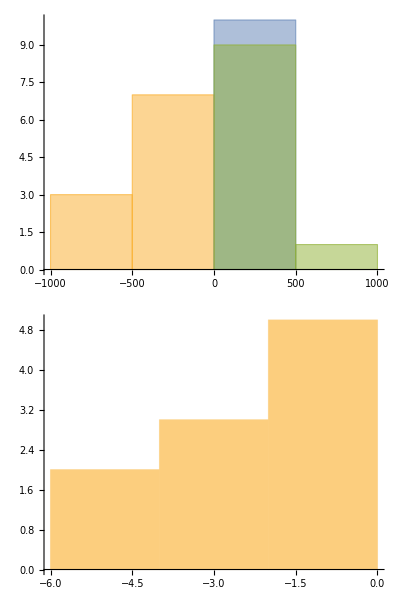

```mathematica
zetaData2//Column@{
Histogram[Transpose@#[[;;,2]], ImageSize->500],
Histogram[#[[;;, 1]], ImageSize->500]
}&
```

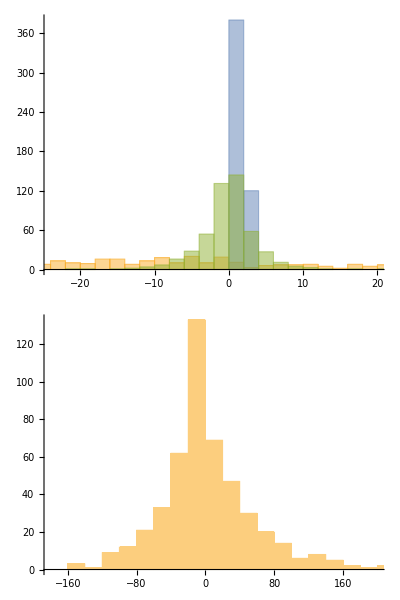

```mathematica
zetaData//Column@{
Histogram[Transpose@#[[;;,2]], ImageSize->500],
Histogram[#[[;;, 1]], ImageSize->500]
}&
```

Full Integration (old)

Bad Symmetry, Good Math

We are therefore left with only two terms that survive the purge

ϕ_n I_α^-1(ζ^α⊗ζ^α)QPQP ϕ_m = 
∑_(n,m,k) (I_α^-1(ζ^α⊗ζ^α))_nkkm∫(Q-ξ^(c))_n(Σ^((j)^-1)(Q-ξ^(c)))_m ϕ^(c) - const

Now to integrate that first term we’ll write

R = L(Q-ξ^(c))

where L diagonalizes Σ^(c) as usual with

L Σ^(c)L^T = A^(c)

This gives us

(Q-ξ^(c))_n(Σ^((j)^-1)(Q-ξ^(c)))_m = (L^T R)_n(Σ^((j)^-1)L^T R)_m
= (L^T_n)⊗(Σ^((j)^-1)L^T)_m⊙R^2

and by symmetry again we know that the only terms that will survive are the diagonal ones, i.e. the ones that look like

((L^T)_n⊗(Σ^((j)^-1)L^T)_m)_kk r_k^2

and so

∫(Q-ξ^(c))_n(Σ^((j)^-1)(Q-ξ^(c)))_m ϕ^(c) = S^(c)∑_k (((L^T)_n⊗(Σ^((j)^-1)L^T)_m)_kk)/(2 α_k^(c))

Now we could stop here but I want to try to see the explicit symmetry emerge so let’s take a page from that I did above and write this as some kind of matrix product by noting that we have

((L^T)_n⊗(Σ^((j)^-1)L^T)_m)_kk = (L^T)_nk (Σ^((j)^-1)L^T)_mk
1/(2 α_k^(c)) = (A^(c))_kk

so

∑_k (((L^T)_n⊗(Σ^((j)^-1)L^T)_m)_kk)/(2 α_k^(c)) = ∑_k (L^T)_nk(A^(c))_kk(Σ^((j)^-1)L^T)_mk
= ∑_k (L^T)_nk(A^(c))_kk((Σ^((j)^-1)L^T)^T)_km
= ∑_u ∑_k (L^T)_nk(A^(c))_kk(L)_ku(Σ^((j)^-1))_um
= ∑_u (Σ^(c))_nu(Σ^((j)^-1))_um
= (Σ^(c)Σ^((j)^-1))_nm
= (Σ^(c))_n(Σ^((j)^-1))_m

and this doesn’t seem too promising, but let’s also bring in our constant term

-∑_(n,k,m) ζ_nk^α(ζ_km^α(ξ^(c)))_n(Σ^((j)^-1)Σ^(c)Σ^((i)^-1)(ξ^(i)-ξ^(j)))_m

and we’ll note that

Σ^((j)^-1)Σ^(c)Σ^((i)^-1)(ξ^(i)-ξ^(j)) = Σ^((j)^-1)(ξ_c-ξ_j)

```mathematica
ssasdasd
```

ξ_c = Σ_c(Σ_i^-1 ξ_i + Σ_j^-1 ξ_j)
ξ_j = Σ_c(Σ_c^-1 ξ_j)
= Σ_c(Σ_i^-1 ξ_j + Σ_j^-1 ξ_j)
⇒ ξ_c-ξ_j = Σ_c Σ_i^-1(ξ_i-ξ_j)

∑_k (((L^T)_n⊗(Σ^((j)^-1)L^T)_m)_kk)/(2 α_k^(c)) = ∑_k (L^T)_nk(A^(c))_kk(Σ^((j)^-1)L^T)_mk
= ∑_k (L^T)_nk(A^(c))_kk((Σ^((j)^-1)L^T)^T)_km
= ∑_u ∑_k (L^T)_nk(A^(c))_kk(L)_ku(Σ^((j)^-1))_um
= ∑_u (Σ^(c))_nu(Σ^((j)^-1))_um
= (Σ^(c)Σ^((j)^-1))_nm
= (Σ^(c))_n(Σ^((j)^-1))_m

```mathematica
With[{n=4, m=1},
{
Sum[
Transpose[lC][[n, k]]*
(sigI2.Transpose[lC])[[m, k]]/eigC[[k]],
{k, 1, 5}
],
(sigC.sigI2)[[n,m]]
}
]
```

{0.20559,0.20559}

```mathematica
BlockRandom[
sigI1=#.Transpose[#]&@RandomReal[{}, {5, 5}];
sigI2=#.Transpose[#]&@RandomReal[{}, {5, 5}];
cent1=RandomReal[{}, 5];
cent2=RandomReal[{}, 5];

{sigI2, sigI1}={sigI1, sigI2};
{cent2, cent1}={cent1, cent2};

sigIC=sigI1 + sigI2;
sigC = Inverse[sigIC];
{eigC, lC}=Eigensystem[sigIC];
centC = sigC.(sigI1.cent1+sigI2.cent2);

testZeta=
#+-Transpose[#]&@UpperTriangularize[RandomReal[{}, {5, 5}], 1];
subZeta = testZeta.testZeta;


Dot[
Flatten@subZeta,
Flatten[
sigC.sigI1- Outer[Times, centC, Dot[sigI1, centC-cent1]]
]
]

]
```

-3.99468

and then as before we have

Σ_c = (Σ_i^-1+Σ_j^-1)^-1 = Σ_j - (Σ_j(Σ_i+Σ_j))^-1 Σ_j

so

and also

Σ_c = (Σ_i^-1+Σ_j^-1)^-1 = Σ_j - (Σ_j(Σ_i+Σ_j))^-1 Σ_j

(Σ_i+Σ_j)^-1 = ((Σ_i^-1)^-1+(Σ_j^-1)^-1)^-1
= (Σ_i^-1(Σ_i^-1+Σ_j^-1))^-1 Σ_j^-1
= Σ_i^-1 Σ_c Σ_j^-1

Σ^(c)Σ^((j)^-1) = 1 - (Σ_j(Σ_i+Σ_j))^-1

##### Value Test

```mathematica
With[{
g1=DGBN[{0., 0., 0.}, {1, 2, 3}],
g2=DGBN[{0., 0., 0.}, {1, 2, 3}]
},
With[{c2=Cases[g1*g2, DGBN[c_, _]:>c, Infinity][[1]]},
gaussianIntegrate[
IdentityMatrix[3],
c2,
{q1, q2, q3},
#[[1]]
][[-1]]&/@watsonTotalIntegrate[
g1[q1, q2, q3],
g2[q1, q2, q3],
{q1, q2, q3}
]
]
]//KeyValueMap[coriolis[[Sequence@@#]]*#2&]//Total
```

-0.5

```mathematica
testCoriolisTermsI[
center1_,alphas1_,
center2_, alphas2_
]:=
With[
{
g1=DGBN[center1, alphas1],
g2=DGBN[center2, alphas2]
},
With[{
c2=Cases[g1*g2, DGBN[c_, _]:>c, Infinity][[1]],
n=gaussianIntegrate[
IdentityMatrix[3],
Cases[g1*g2, DGBN[c_, _]:>c, Infinity][[1]],
{q1, q2, q3},
g1*g2/.d_DGBN:>d[q1, q2, q3]
][[-1]]
},
gaussianIntegrate[
IdentityMatrix[3],
c2,
{q1, q2, q3},
#[[1]]
][[-1]]&/@watsonTotalIntegrate[
g1[q1, q2, q3],
g2[q1, q2, q3],
{q1, q2, q3}
]
]
];
testCoriolisTerms[
center1_,alphas1_,
center2_, alphas2_,
allTerms:True|False:True
]:=
If[allTerms,
Block[{watsonZeta=z},
testCoriolisTermsI[
center1,alphas1,
center2, alphas2
]
],
testCoriolisTermsI[
center1,alphas1,
center2, alphas2
]
]//KeyValueMap[#->coriolis[[Sequence@@#]]*#2&]//Association//Select[#!=0&]
```

```mathematica
testCoriolisTerms[
{0., 0., 0.},{0.00323066, 0.00623588, 0.00881837},
{0., 0., 0.},{0.00323066, 0.00623588, 0.00881837}
]
```

<|z[1,2,1,2]→-0.482555,z[1,2,2,1]→0.25,z[1,3,1,3]→-0.682397,z[1,3,3,1]→0.25,z[2,1,1,2]→0.25,z[2,1,2,1]→-0.129519,z[2,3,2,3]→-0.353534,z[2,3,3,2]→0.25,z[3,1,1,3]→0.25,z[3,1,3,1]→-0.0915889,z[3,2,2,3]→0.25,z[3,2,3,2]→-0.176787|>

```mathematica
%//Values//Total
```

-0.41638

```mathematica
testCoriolisTerms[
{0., 0., 0.},{0.00323066, 0.00623588, 0.00881837},
{-34.0531356,-6.2604998,-2.60299368},{0.00379871, 0.00687799, 0.00757652}
]
```

```mathematica
testCoriolisTerms[
{0., 0., 0.},{0.00323066, 0.00623588, 0.00881837},
{-34.0531356,-6.2604998,-2.60299368},{0.00379871, 0.00687799, 0.00757652}
]
```

<|z[1,2,1,2]→-0.22442,z[1,2,1,3]→-0.0400838,z[1,2,2,1]→-0.113162,z[1,2,2,3]→-0.0268128,z[1,2,3,1]→0.00913871,z[1,2,3,2]→-0.0121233,z[1,3,1,2]→-0.0400838,z[1,3,1,3]→-0.355269,z[1,3,2,1]→0.0129234,z[1,3,2,3]→-0.0523867,z[1,3,3,1]→-0.104519,z[1,3,3,2]→-0.0478027,z[2,1,1,2]→0.116267,z[2,1,1,3]→0.0207665,z[2,1,2,1]→0.0586265,z[2,1,2,3]→0.0138911,z[2,1,3,1]→-0.00473455,z[2,1,3,2]→0.00628077,z[2,3,1,2]→0.0171439,z[2,3,1,3]→-0.0523867,z[2,3,2,1]→0.0138911,z[2,3,2,3]→-0.0424028,z[2,3,3,1]→-0.0247654,z[2,3,3,2]→0.0247396,z[3,1,1,2]→0.0146849,z[3,1,1,3]→0.130155,z[3,1,2,1]→-0.00473455,z[3,1,2,3]→0.0191922,z[3,1,3,1]→0.0382911,z[3,1,3,2]→0.0175128,z[3,2,1,2]→-0.0121233,z[3,2,1,3]→0.0370451,z[3,2,2,1]→-0.00982304,z[3,2,2,3]→0.029985,z[3,2,3,1]→0.0175128,z[3,2,3,2]→-0.0174945|>

```mathematica
ugh
```

<|{1,2,1,2}→-0.22442,{1,2,1,3}→-0.0400838,{1,2,2,1}→-0.00541787,{1,2,2,3}→-0.00591062,{1,2,3,1}→0.0127697,{1,2,3,2}→-0.0121233,{1,3,1,2}→-0.0400838,{1,3,1,3}→-0.355269,{1,3,2,1}→0.01761,{1,3,2,3}→-0.0523867,{1,3,3,1}→0.0262068,{1,3,3,2}→-0.00216535,{2,1,1,2}→-0.0180502,{2,1,1,3}→0.0171618,{2,1,2,1}→0.0586265,{2,1,2,3}→0.0138911,{2,1,3,1}→-0.00473455,{2,1,3,2}→-0.00431771,{2,3,1,2}→-0.00669913,{2,3,1,3}→-0.0523867,{2,3,2,1}→0.0138911,{2,3,2,3}→-0.0424027,{2,3,3,1}→-0.00112181,{2,3,3,2}→0.0312349,{3,1,1,2}→0.0121359,{3,1,1,3}→0.0362866,{3,1,2,1}→-0.00473455,{3,1,2,3}→0.00530509,{3,1,3,1}→0.0382911,{3,1,3,2}→0.0175128,{3,2,1,2}→-0.0121233,{3,2,1,3}→0.00116428,{3,2,2,1}→-0.00216539,{3,2,2,3}→0.0255018,{3,2,3,1}→0.0175128,{3,2,3,2}→-0.0174945|>

```mathematica
0.29422694*2
```

```mathematica
0.51394493+0.29422694*2-.01086625
```

1.09153

```mathematica
%//Values//Total
```

-0.587081

```mathematica
testCoriolisTerms[
{0., 0., 0.},{0.00323066, 0.00623588, 0.00881837},
{32.4484376, 8.79588127,-2.16608811},{0.00373914, 0.00431539, 0.00761978}
]
```

<|z[1,2,1,2]→-0.148612,z[1,2,1,3]→0.0382388,z[1,2,2,1]→-0.137354,z[1,2,2,3]→0.0297863,z[1,2,3,1]→-0.00822379,z[1,2,3,2]→0.00693104,z[1,3,1,2]→0.0382388,z[1,3,1,3]→-0.378372,z[1,3,2,1]→-0.0116295,z[1,3,2,3]→-0.0632255,z[1,3,3,1]→-0.101177,z[1,3,3,2]→-0.0555899,z[2,1,1,2]→0.0769924,z[2,1,1,3]→-0.0198106,z[2,1,2,1]→0.0711596,z[2,1,2,3]→-0.0154316,z[2,1,3,1]→0.00426055,z[2,1,3,2]→-0.00359081,z[2,3,1,2]→-0.00980142,z[2,3,1,3]→-0.0632255,z[2,3,2,1]→-0.0154316,z[2,3,2,3]→-0.0609089,z[2,3,3,1]→-0.0287998,z[2,3,3,2]→0.0176221,z[3,1,1,2]→-0.014009,z[3,1,1,3]→0.138619,z[3,1,2,1]→0.00426055,z[3,1,2,3]→0.023163,z[3,1,3,1]→0.0370666,z[3,1,3,2]→0.0203657,z[3,2,1,2]→0.00693104,z[3,2,1,3]→0.0447097,z[3,2,2,1]→0.0109124,z[3,2,2,3]→0.0430715,z[3,2,3,1]→0.0203657,z[3,2,3,2]→-0.0124614|>

```mathematica
%//Values//Total
```

-0.514959

```mathematica
coriolis="[[[[ 0.  0.  0.]
   [ 0.  0.  0.]
   [ 0.  0.  0.]]

  [[ 0.  1. -1.]
   [-1.  0. -1.]
   [ 1.  1.  0.]]

  [[ 0. -1.  1.]
   [ 1.  0.  1.]
   [-1. -1.  0.]]]


 [[[ 0. -1.  1.]
   [ 1.  0.  1.]
   [-1. -1.  0.]]

  [[ 0.  0.  0.]
   [ 0.  0.  0.]
   [ 0.  0.  0.]]

  [[ 0. -1.  1.]
   [ 1.  0.  1.]
   [-1. -1.  0.]]]


 [[[ 0.  1. -1.]
   [-1.  0. -1.]
   [ 1.  1.  0.]]

  [[ 0.  1. -1.]
   [-1.  0. -1.]
   [ 1.  1.  0.]]

  [[ 0.  0.  0.]
   [ 0.  0.  0.]
   [ 0.  0.  0.]]]]
"//ImportString[StringDelete[#, "["|"]"], "Table"]&//ArrayReshape[#, {3, 3, 3, 3}]&;
```

## Momentum Inclusion

To account for the momentum we change our Gaussian definition to include a momentum dependent phase as

φ^(i) = 𝒩(Σ^(i))exp(-1/2(q-ξ^(i))(Σ^(i))^-1(q-ξ^(i)) + 𝕚 J^(i)q )

where J = Q_Σ p_0 are chosen to be the momenta along the rotated Gaussian axes

The normalization will not need to change

Rephasing

We’ll then take the different phases on the momentum to ensure real matrices, by letting

φ^(i) = ϕ^(i)Θ^(i)
Θ^(i)=1/2(exp(𝕚 J^(i)q) + exp(-𝕚 J^(i)q) ) + 𝕚/2(exp(𝕚 J^(i)q) - exp(-𝕚 J^(i)q) )
[= cos(J^(i)q) - sin(J^(i)q)]

where we’ll note that this is self-conjugate, and taking the product we get

Θ^(i)Θ^(j) = 1/2(exp(𝕚(J^(i)-J^(j))q) + exp(-𝕚(J^(i)-J^(j))q) )
  + 𝕚/2( exp(𝕚(J^(i)+J^(j))q) - exp(-𝕚(J^(i)+J^(j))q) )

and importantly

```mathematica
D[- I/2(Exp[ I p q]-Exp[ -I p q]), q]/p//Simplify//Expand
```

1/2 ⅇ^(-ⅈ p q)+1/2 ⅇ^(ⅈ p q)

```mathematica
D[Sin[x], x]
```

Cos[x]

```mathematica
D[Sin[x]+Cos[x], x]
```

Cos[x]-Sin[x]

```mathematica
D[Sin[x]-Cos[x], x]
```

Cos[x]+Sin[x]

```mathematica
D[Exp[I p], p]
```

ⅈ ⅇ^(ⅈ p)

```mathematica
D[Cos[x], x]
```

-Sin[x]

```mathematica
D[- I/2(Exp[ I p q]-Exp[ -I p q]), q]/p//Simplify//Expand
```

```mathematica
-1/2 ⅇ^(-ⅈ p q) (1+ⅇ^(2 ⅈ p q))//Expand
```

-1/2 ⅇ^(-ⅈ p q)-1/2 ⅇ^(ⅈ p q)

```mathematica
(-1/2+ⅈ/2) ⅇ^(-ⅈ p q) (ⅈ+ⅇ^(2 ⅈ p q))//Expand
```

(1/2+ⅈ/2) ⅇ^(-ⅈ p q)+(1/2-ⅈ/2) ⅇ^(ⅈ p q)

##### Function

```mathematica
Clear[phaseGauss];
phaseGauss[a_, p_, c_, prefac_:1][ q_]:=prefac*Exp[-a (q-c)^2 + I p (q)]
phaseGauss/:(phaseGauss[a1_, p1_, c1_]*phaseGauss[a2_, p2_, c2_]):=
phaseGauss[a1*a2/(a1+a2), p1+p2,( a1*c1+a2*c2)/(a1+a2)]
```

```mathematica
Plot[
Evaluate[
phaseGauss[1, 5, 0][q]+phaseGauss[1, -5, 0][q]//ComplexExpand
],
{q, -2, 2}
]//imageify
```

-Graphics-

```mathematica
phaseGauss[a_, p_, c_][q_]:=
Exp[-a (q-c)^2 + I p (q)]
```

```mathematica
(phaseGauss[a1, p1, c1][q])*
D[phaseGauss[a2, p2, c2][q], {q, 2}]//Simplify
```

ⅇ^(-a1 (c1-q)^2-a2 (c2-q)^2+ⅈ (p1+p2) q) (-2 a2+(ⅈ p2+2 a2 (c2-q))^2)

```mathematica
DGBN[ξ1, α1*α2/(α1+α2) ]
```

```mathematica
Exp[α1*α2/(α1+α2)]
```

```mathematica
Assuming[
a1>0&&a2>0,
-(a1+a2)(q-((a1 c1)/(a1+a2)+(a2 c2)/(a1+a2)))^2-(-a1 (c1-q)^2-a2 (c2-q)^2)//Simplify
]
```

(a1 a2 (c1-c2)^2)/(a1+a2)

```mathematica
Assuming[
a1>0&&a2>0,
Exp[-(a1*a2)/(a1+a2)(q-((a1 c1)/(a1+a2)+(a2 c2)/(a1+a2)))^2]==ⅇ^(-a1 (c1-q)^2-a2 (c2-q)^2)//Simplify
]
```

ⅇ^((a1 a2 (a1 (c1-q)+a2 (c2-q))^2)/(a1+a2)^3)==ⅇ^(a1 (c1-q)^2+a2 (c2-q)^2)

```mathematica
-(a1+a2)(q-((a1 c1)/(a1+a2)+(a2 c2)/(a1+a2)))^2+(a1 a2 (c1-c2)^2)/(a1+a2)//Expand//Simplify
```

(-a1^2 (c1-q)^2-a2^2 (c2-q)^2+a1 a2 (c1^2-4 c1 c2+c2^2+2 c1 q+2 c2 q-2 q^2))/(a1+a2)

```mathematica
Assuming[
a1>0&&p1∈Reals&&c1∈Reals
&&a2>0&&p2∈Reals&&c2∈Reals,
ⅇ^(-a1 (c1-q)^2-a2 (c2-q)^2+ⅈ (p1+p2) q) ==Exp[(a1 a2 (c1-c2)^2)/(a1+a2)]Exp[-(a1+a2)(q-((a1 c1)/(a1+a2)+(a2 c2)/(a1+a2)))^2]Exp[I(p1+p2)q]//Simplify
]
```

ⅇ^((a1 a2 (c1-c2)^2)/(a1+a2)+a1 (c1-q)^2+a2 (c2-q)^2)==ⅇ^((a1 c1+a2 c2-(a1+a2) q)^2/(a1+a2))

```mathematica
(a1 c1+a2 c2-(a1+a2) q)^2/(a1+a2)
```

```mathematica
(a1 a2 (c1-c2)^2)/(a1+a2)+a1 (c1-q)^2+a2 (c2-q)^2//Expand
```

a1 c1^2+(a1 a2 c1^2)/(a1+a2)-(2 a1 a2 c1 c2)/(a1+a2)+a2 c2^2+(a1 a2 c2^2)/(a1+a2)-2 a1 c1 q-2 a2 c2 q+a1 q^2+a2 q^2

```mathematica
polyTerms=-2 a2+(ⅈ p2+2 a2 (c2-q))^2//Expand//CoefficientList[#, q]&
```

{-2 a2+4 a2^2 c2^2+4 ⅈ a2 c2 p2-p2^2,-8 a2^2 c2-4 ⅈ a2 p2,4 a2^2}

```mathematica
intTerms=
Table[
Assuming[
ac>0&&cc∈Reals&&
a1>0&&p1∈Reals&&c1∈Reals
&&a2>0&&p2∈Reals&&c2∈Reals,
Integrate[
Exp[-ac*(q-cc)^2]Exp[I(p1+p2)*q]q^k,
{q, -∞, ∞}
]
],
{k, 0, 2}
]
```

{(ⅇ^(-((p1+p2) (-4 ⅈ ac cc+p1+p2))/(4 ac)) √π)/(√ac),(ⅇ^(-((p1+p2) (-4 ⅈ ac cc+p1+p2))/(4 ac)) (2 ac cc+ⅈ (p1+p2)) √π)/(2 ac^(3/2)),(ⅇ^(-((p1+p2) (-4 ⅈ ac cc+p1+p2))/(4 ac)) (4 ac^2 cc^2-(p1+p2)^2+ac (2+4 ⅈ cc (p1+p2))) √π)/(4 ac^(5/2))}

```mathematica
MapThread[
Function[
#*#2/.{
ac->(a1+a2),
cc->(a1*c1+a2*c2)/(a1+a2)
}//Expand//Simplify
],
{polyTerms, intTerms}
]//Total//Simplify
```

1/(a1+a2)^(5/2)ⅇ^(-((p1+p2) (-4 ⅈ (a1 c1+a2 c2)+p1+p2))/(4 (a1+a2))) (-a2^2 p1^2+2 a1 a2 (ⅈ a2 (ⅈ+2 c1 p1-2 c2 p1)+p1 p2)+a1^2 (4 a2^2 (c1-c2)^2-p2^2+a2 (-2-4 ⅈ c1 p2+4 ⅈ c2 p2))) √π

```mathematica
(-a2^2 p1^2+2 a1 a2 (ⅈ a2 (ⅈ+2 c1 p1-2 c2 p1)+p1 p2)+a1^2 (4 a2^2 (c1-c2)^2-p2^2+a2 (-2-4 ⅈ c1 p2+4 ⅈ c2 p2)))//Expand
```

-2 a1^2 a2-2 a1 a2^2+4 a1^2 a2^2 c1^2-8 a1^2 a2^2 c1 c2+4 a1^2 a2^2 c2^2+4 ⅈ a1 a2^2 c1 p1-4 ⅈ a1 a2^2 c2 p1-a2^2 p1^2-4 ⅈ a1^2 a2 c1 p2+4 ⅈ a1^2 a2 c2 p2+2 a1 a2 p1 p2-a1^2 p2^2

```mathematica
polyTerms[[2]]*intTerms[[2]]/.{
ac->(a1+a2),
cc->(a1*c1+a2*c2)/(a1+a2)
}//Expand//Simplify
```

-(2 a2 ⅇ^(-((p1+p2) (-4 ⅈ (a1 c1+a2 c2)+p1+p2))/(4 (a1+a2))) (2 a2 c2+ⅈ p2) (2 a1 c1+2 a2 c2+ⅈ (p1+p2)) √π)/(a1+a2)^(3/2)

#### Generic Shifted Integral

```mathematica
baseShiftedIntegral=
Assuming[a>0&&p>0&&k>0&&k∈Integers&&c∈Reals,
Integrate[q^k Exp[-a q^2 + I p (q-c)], {q, -∞, ∞}]
]
```

1/2 a^(-1-k/2) ⅇ^(-ⅈ c p) (-ⅈ (-1+(-1)^k) p Gamma[1+k/2] Hypergeometric1F1[1+k/2,3/2,-p^2/(4 a)]+(1+(-1)^k) √a Gamma[(1+k)/2] Hypergeometric1F1[(1+k)/2,1/2,-p^2/(4 a)])

#### Solving for Hypergeometric Expressions

We start out by noting that the even term is just built off a Hermite polynomial, so we’ll ignore it. The second term

```mathematica
Gamma[1+k/2]  Hypergeometric1F1[(2+k)/2,3/2,-x]
```

is rather more annoying, so we return to the definition of the HGF

_1 F_1(a; b; x) = ∑_(m=0)^∞ ((a)_m)/((b)_m)x^m/(m!)

where (a)_m is the rising factorial starting at a and going to a+m−1

Noting that

(a)_m = (Γ(a+m))/(Γ(a))

and that in our case, a = b + k, we have

((a)_m)/((b)_m) = (Γ(b+k+m))/(Γ(b+k))(Γ(b))/(Γ(b+m)) = ((b+m)_k)/((b)_k)

and the (b)_k can be factored and (b+m)_k can be expressed as a polynomial with

(b+m)_k = ∑_(j=1)^k |S_1(k, j)|(b+m)^j

and then we can express this in terms of m alone by writing

(b+m)_k =  ∑_(j=1)^k ∑_(l=0)^j |S_1(k, j)|(j
j-l)b^(j-l)m^l

and then we flip the sum to get

(b+m)_k = ∑_(l=0)^k ∑_(j=l)^k  |S_1(k, j)|(j
j-l)b^(j-l)m^l

where we’ve explicitly taken advantage of the fact that S_1(k, 0) = 0, so now we have

_1 F_1(b+k; b; x) =1/((b)_k) ∑_(l=0)^k ∑_(j=l)^k |S_1(k, j)|(j
j-l)b^(j-l)  ∑_(m=0)^∞ m^l x^m/(m!)

and then that final sum actually has a simple form as

∑_(m=0)^∞ m^l x^m/(m!) = e^x ∑_(n=1)^l S_2(l, n) x^n

which means in total we get

_1 F_1(b+k; b; x) =1/((b)_k)e^x ∑_(l=0)^k ∑_(j=l)^k ∑_(n=1)^l |S_1(k, j)|(j
j-l)b^(j-l)S_2(l, n) x^n

and then flipping the sum once more we have

_1 F_1(b+k; b; x) =1/((b)_k)e^x ∑_(n=1)^k ∑_(l=n)^k ∑_(j=l)^k  |S_1(k, j)|(j
j-l)b^(j-l)S_2(l, n) x^n

finally, flipping that rising factorial back around we have (I dropped a power but otherwise everything is fine)

_1 F_1(b+k; b; x) =((b-1)!)/((k+b-1)!)e^x ∑_(n=0)^k ∑_(l=n)^k ∑_(j=l)^k  |S_1(k, j)|(j
l)b^(j-l)S_2(l, n) x^n
=((b-1)!)/((k+b-1)!)e^x ∑_(n=0)^k ∑_(l=n)^k ∑_(j=l)^k  S_1(k, j)(j
l)b^(j-l)S_2(l, n) (-x)^n

and we can view this as a type of matrix transform in the basis of rising/falling factorials, which leads us to

_1 F_1(b+k; b; x) =1/((b)_k)e^x ∑_(n=0)^k ((k+b-1
n)[k])_(k-n)x^n
= e^x ∑_(n=0)^k (k+b-1
n)([k]_(k-n))/((b)_k)x^n

Finally, we have the prefactor, so

(Γ(b+k))_1 F_1(b+k; b; x) = Γ(b+k)(Γ(b))/(Γ(b+k))e^x ∑_(n=0)^k ((k+b-1
k-n)[k])_(k-n)x^n
= e^x ∑_(n=0)^k ((Γ(b)Γ(k+b))/(Γ(k-n+1)Γ(n+b))[k])_(k-n)x^n
= e^x ∑_(n=0)^k (Γ(b)Γ(k+b))/(Γ(n+b))(Γ(k+1))/(Γ(k-n+1)Γ(n+1))x^n
= e^x ∑_(n=0)^k (Γ(b)Γ(k+b))/(Γ(n+b))(k
n)x^n

And then to clean up the Γ(b) terms we get

(Γ(b+k))_1 F_1(b+k; b; x) = Γ(b+k)(Γ(b))/(Γ(b+k))e^x ∑_(n=0)^k ((k+b-1
k-n)[k])_(k-n)x^n
= e^x ∑_(n=0)^k ((Γ(b)Γ(k+b))/(Γ(k-n+1)Γ(n+b))[k])_(k-n)x^n
= e^x ∑_(n=0)^k (Γ(b)Γ(k+b))/(Γ(n+b))(Γ(k+1))/(Γ(k-n+1)Γ(n+1))x^n
= e^x ∑_(n=0)^k (Γ(b)Γ(b+k))/(Γ(n+b))(k
n)x^n

which actually just shows that

_1 F_1(b+k; b; x) = e^x ∑_(n=0)^k 1/((b)_(n))(k
n)x^n

then adding on that pre-factor we get

(Γ(b+k))_1 F_1(b+k; b; x) = e^x ∑_(n=0)^k (Γ(b+k))/((b)_(n))(k
n)x^n

where letting b = c + 1/2

(Γ(b+k))/((b)_(n)) =(√π)/2^(c+k-n)((2(c+k)-1)!!(2c-1)!!)/((2(n+c)-1)!!)

Derivation Work

```mathematica
Table[k!!, {k, 12}]
```

{1,2,3,8,15,48,105,384,945,3840,10395,46080}

```mathematica
With[{k=5, bb=3/2},
{
Table[Binomial[k-1+bb, k-n],{n, 0, k}],
f1Terms[[k+1]][[;;k+1]]/
Table[FactorialPower[k, k-n],{n, 0, k}]/.b->bb
}
]
```

{{693/256,1155/128,231/16,99/8,11/2,1},{693/256,1155/128,231/16,99/8,11/2,1}}

```mathematica
Binomial[3/2]
```

```mathematica
Gamma[1+k/2]
```

```mathematica
Table[Gamma[1+k/2], {k, 1, 11, 2}]*(2/Sqrt[π])
```

{1,3/2,15/4,105/8,945/16,10395/32}

```mathematica
n
```

```mathematica
Table[((2n)!)/(2^(2n-1) n!), {n, 10}]
```

{1,3/2,15/4,105/8,945/16,10395/32,135135/64,2027025/128,34459425/256,654729075/512}

```mathematica
3*5*7*9*11
```

```mathematica
3*5*7*9*11
```

10395

```mathematica
s!!
```

```mathematica
Table[n!/2^((n-1)/2), {n, 1, 11, 2}]
```

{1,3,30,630,22680,1247400}

```mathematica
Table[n!/2^((n-1)/2), {n, 1, 9, 2}]
```

{1,3,30,630,22680}

```mathematica
With[{k=5, bb=1},
{
Table[FactorialPower[k, k-n], {n, 0, k}],

Table[FactorialPower[k, k-n], {n, 0, k}]/.b->bb
}
]
```

```mathematica
f1Terms=Abs[s1Mat].(binMat*bMat).s2Mat;
```

```mathematica
Binomial[3, ]
```

```mathematica
f1Terms[[4]][[;;4]]/.b->1
```

{6,18,9,1}

```mathematica
Γ(b)
```

```mathematica
With[{k=5, bb=3/2},
{
Table[Binomial[k-1+bb, k-n],{n, 0, k}],
f1Terms[[k+1]][[;;k+1]]/
Table[FactorialPower[k, k-n],{n, 0, k}]/.b->bb
}
]
```

{{693/256,1155/128,231/16,99/8,11/2,1},{693/256,1155/128,231/16,99/8,11/2,1}}

where we

```mathematica
s1Mat=Array[StirlingS1, {10, 10}, {0, 0}];
binMat=Array[Binomial, {10, 10}, {0, 0}];
bMat=Array[b^Abs[#-#2]&, {10, 10}, {0, 0}];
s2Mat=Array[StirlingS2, {10, 10}, {0, 0}];
```

```mathematica
With[{k=5, bb=5/2},
{
Table[Binomial[k-1+bb, k-n],{n, 0, k}],
f1Terms[[k+1]][[;;k+1]]/
Table[FactorialPower[k, k-n],{n, 0, k}]/.b->bb
}
]
```

{{3003/256,3003/128,429/16,143/8,13/2,1},{3003/256,3003/128,429/16,143/8,13/2,1}}

```mathematica
f1Terms=Abs[s1Mat].(binMat*bMat).s2Mat;
```

```mathematica
f1Terms[[5]]/.b->1/2
```

{105/16,105/2,105/2,14,1,0,0,0,0,0}

```mathematica
hgfCoeffs[4, 1/2, False]
```

{105/16,105/2,105/2,14,1}

```mathematica
With[{k=3, b=1},
Hypergeometric1F1[b+k,b,x]
]
```

ⅇ^x (1+3 x+(3 x^2)/2+x^3/6)

```mathematica
hgfCoeffs[3, 1, False]
```

```mathematica
hgfCoeffs[3, 1, False]
```

{6,18,9,1}

```mathematica
Clear[hgfCoeff, hgfCoeffs]
hgfCoeff[n_, k_, b_, weight:True|False:True]:=
Total@Flatten@Table[
Table[
(-1)^(k+j)StirlingS1[k, j]*Binomial[j, j-l]*b^(j-l)*StirlingS2[l, n],
{j, l, k}
],
{l, n, k}
]/If[weight, Pochhammer[b, k], 1];
hgfCoeffs[k_, b_, weight:True|False:True]:=
Table[
hgfCoeff[n, k, b, weight],
{n, 0, k}
]
```

```mathematica
hgfCoeffs[k, 2]
```

```mathematica
With[{k=2, b=1/2},
{
hgfCoeffs[k, b],
Hypergeometric1F1[b+k,b,-x]
}
]
```

{{1,4,4/3},ⅇ^-x (1-4 x+(4 x^2)/3)}

```mathematica
With[{k=2, b=3/2},
{
hgfCoeffs[k-1, b],
Hypergeometric1F1[(b-1)+k,b,-x]
}
]
```

{{1,2/3},ⅇ^-x (1-(2 x)/3)}

```mathematica
Hypergeometric1F1[(2+3)/2,3/2,-x]
```

ⅇ^-x (1-(2 x)/3)

```mathematica
Gamma[1+k/2]  Hypergeometric1F1[(2+k)/2,3/2,-x]
```

```mathematica
hgfCoeff[]
```

```mathematica
(2+k)/2//Expand
```

1+k/2

```mathematica
Gamma[1+k/2]  Hypergeometric1F1[(2+k)/2,3/2,-x]
```

```mathematica
Table[
Hypergeometric1F1[(2+k)/2,3/2,-x]/Exp[-x],
{k, 1, 15, 2}
]//Column
```

1
1-(2 x)/3
1-(4 x)/3+(4 x^2)/15
1-2 x+(4 x^2)/5-(8 x^3)/105
1-(8 x)/3+(8 x^2)/5-(32 x^3)/105+(16 x^4)/945
1-(10 x)/3+(8 x^2)/3-(16 x^3)/21+(16 x^4)/189-(32 x^5)/10395
1-4 x+4 x^2-(32 x^3)/21+(16 x^4)/63-(64 x^5)/3465+(64 x^6)/135135
1-(14 x)/3+(28 x^2)/5-(8 x^3)/3+(16 x^4)/27-(32 x^5)/495+(64 x^6)/19305-(128 x^7)/2027025

```mathematica
Table[
Hypergeometric1F1[(2+k)/2,3/2,-x]/Exp[-x],
{k, 1, 17, 2}
]//CoefficientList[#, x]&//Abs//Numerator
```

{{1},{1,2},{1,4,4},{1,2,4,8},{1,8,8,32,16},{1,10,8,16,16,32},{1,4,4,32,16,64,64},{1,14,28,8,16,32,64,128},{1,16,112,64,32,256,256,1024,256}}

```mathematica
Table[
Hypergeometric1F1[(2+k)/2,3/2,x],
{k, 1, 11, 2}
]
```

{ⅇ^x,ⅇ^x (1+(2 x)/3),ⅇ^x (1+(4 x)/3+(4 x^2)/15),ⅇ^x (1+2 x+(4 x^2)/5+(8 x^3)/105),ⅇ^x (1+(8 x)/3+(8 x^2)/5+(32 x^3)/105+(16 x^4)/945),ⅇ^x (1+(10 x)/3+(8 x^2)/3+(16 x^3)/21+(16 x^4)/189+(32 x^5)/10395)}

```mathematica
Table[pooks[1+1/2+m, (k-1)/2], {k, 1, 11, 2}]//Expand
```

{1,3/2+m,15/4+4 m+m^2,105/8+(71 m)/4+(15 m^2)/2+m^3,945/16+93 m+(103 m^2)/2+12 m^3+m^4,10395/32+(9129 m)/16+(1505 m^2)/4+(235 m^3)/2+(35 m^4)/2+m^5}

```mathematica
Sum[(a+b m+c m^2)*x^m/(m!), {m, 0, ∞}]
```

ⅇ^x (a+b x+c x+c x^2)

```mathematica
Sum[(a+b m+cm^2)*x^m/(m!), {m, 0, ∞}]
```

```mathematica
Table[
Pochhammer[1+1/2, (k-1)/2], 
{k, 1, 11, 2}
]
```

{1,3/2,15/4,105/8,945/16,10395/32}

```mathematica
Table[pooks[1+1/2+m, (k-1)/2], {k, 1, 11, 2}]
```

{1,3/2+m,(3/2+m) (5/2+m),(3/2+m) (5/2+m) (7/2+m),(3/2+m) (5/2+m) (7/2+m) (9/2+m),(3/2+m) (5/2+m) (7/2+m) (9/2+m) (11/2+m)}

```mathematica
(3/2+m) (5/2+m)//Expand
```

15/4+4 m+m^2

```mathematica
Gamma[(2+k)/2+m]/Gamma[3/2+m]
```

```mathematica
Table[Gamma[(2+k)/2]/Gamma[3/2], {k, 10}]
```

{1,2/(√π),3/2,4/(√π),15/4,12/(√π),105/8,48/(√π),945/16,240/(√π)}

```mathematica
Table[
Gamma[1+k/2]Hypergeometric1F1[(2+k)/2,3/2,-x]/(Sqrt[π]*Exp[-x]),
{k, 1, 15, 2}
]//CoefficientList[#, x]&//Column
```

{1/2}
{3/4,-1/2}
{15/8,-5/2,1/2}
{105/16,-105/8,21/4,-1/2}
{945/32,-315/4,189/4,-9,1/2}
{10395/64,-17325/32,3465/8,-495/4,55/4,-1/2}
{135135/128,-135135/32,135135/32,-6435/4,2145/8,-39/2,1/2}
{2027025/256,-4729725/128,2837835/64,-675675/32,75075/16,-4095/8,105/4,-1/2}

```mathematica
Gamma[1+k/2]*/(Sqrt[π]*Exp[-x])
```

```mathematica
(1-(8 x)/3+(8 x^2)/5-(32 x^3)/105+(16 x^4)/945)//CoefficientList[#, x]&//Abs//Numerator//Log2
```

{0,3,3,5,4}

```mathematica
gammaTerms[k_]:=
FoldList[
#*(2*#2+1)/2&,
1/2,
Range[k]
]
```

#### Generic Integral Form

We get in total

∫_(-∞)^∞ (q-c)^k exp(-(α(q-c))^2+ ipq) = e^-icp Piecewise[{{α^(-(1+k/2)) ip Γ((2+k)/2)F_1((2+k)/2; 3/2; -p^2/(4α)), k odd}, {α^(-(1/2+k/2)) Γ((1+k)/2)F_1((1+k)/2; 1/2; -p^2/(4α)), k even}}]

where both of these branches use the symbolic form from above, as

(2+k)/2 - 3/2 = 3/2 + (k-1)/2
(1+k)/2 - 1/2 = 1/2 + k/2

and therefore, letting m = ⌊k/2⌋ we have both integrals having the form of powers in p

Γ(b+m)F_1(b+m; b+m; -p^2/(4α)) = exp(-p^2/(4α)) ∑_(n=0)^m (-1)^n(Γ(b+m))/((b)_(n))(m
n)(p/(2 √α))^(2n)

and in the case that p = 0, letting 0^0 = 1 we recover the original form

Γ(b+m)F_1(b+m; b+m; -p^2/(4 a)) = Γ(b+m)

for convenience, we will write

G_b^k(α, p) = Γ(b+⌊k/2⌋)F_1(b+⌊k/2⌋; b+⌊k/2⌋; -p^2/(4α))

and so our total integral is

∫_(-∞)^∞ (q-c)^k exp(-(α(q-c))^2+ 𝕚pq) = e^-𝕚cp Piecewise[{{α^(-(1+k/2)) 𝕚p G_(3/2)^k(α, p), k odd}, {α^(-(1/2+k/2)) G_(1/2)^k(α, p), k even}}]

Rephasing

k odd

∫_(-∞)^∞ (q-ξ^(i,j))^k φ^(i)φ^(j) = α^(-1/2-⌈k/2⌉)/2( p^((i,j)-)sin(ξ^(i,j)·p^((i,j)-))G_(3/2)^k(α, p^((i,j)-))
    -p^((i,j)+)cos(ξ^(i,j)·p^((i,j)+))G_(3/2)^k(α, p^((i,j)+)) )

k even

∫_(-∞)^∞ (q-ξ^(i,j))^k φ^(i)φ^(j) = α^(-1/2-⌈k/2⌉)/2( cos(ξ^(i,j)·p^((i,j)-))G_(1/2)^k(α, p^((i,j)+))
                    -sin(ξ^(i,j)·p^((i,j)+))G_(1/2)^k(α, p^((i,j)+)) )

##### Generic form for M

To make the derivations simpler, we will introduce the notation

M_b^k(α, p) = 2^⌈k/2⌉/(√π) ∑_(n=0)^⌊k/2⌋ (-1/2)^n(Γ(b+⌊k/2⌋))/((b)_(n))(⌊k/2⌋
n)(p^2/(2α))^n

and more specifically,

M_k^(i,j) = Piecewise[{{M_(3/2)^k(α_s^(i,j), p_s^(i,j)), k odd}, {M_(1/2)^k(α_s^(i,j), p_s^(i,j)), k even}}]

we’ll also take this chance to figure out what the two relevant values of M_k evaluate to

First we have

(Γ(3/2+k))/((3/2)_(n)) =(√π)/2^(k+1-n)(2k!!)/(2n!!)

(Γ(1/2+k))/((1/2)_(n)) =(√π)/2^(k-n)((2k-1)!!)/((2n-1)!!)

then we get

M_(1/2)^k(α, p) = 2^(k/2)/(√π) ∑_(n=0)^(k/2) (-1/2)^n(√π)/2^(k/2-n)((k-1)!!)/((2n-1)!!)(k/2
n)(p^2/(2α))^n
= ∑_(n=0)^(k/2) (-1)^n((k-1)!!)/((2n-1)!!)(k/2
n)(p^2/(2α))
= ∑_(n=0)^(k/2) (-1)^n(∏_(j=n+1)^(k/2) 2j-1)(k/2
n)(p^2/(2α))
M_(3/2)^k(α, p) = ∑_(n=0)^((k-1)/2) (-1)^n((k-1)!!)/(2n!!)((k-1)/2
n)(p^2/(2α))^n
= ∑_(n=0)^((k-1)/2) (-1)^n(∏_(j=n)^((k-1)/2) 2j+1)((k-1)/2
n)(p^2/(2α))^n

this then provides a recurrence relation in k on the coefficients as we have the generic form

μ_n^k= (-1)^n(∏_(j=n+1)^⌊k/2⌋ 2j + (-1)^(k+1))(⌊k/2⌋
n)

and

(⌊k/2⌋
n) = (⌊(k-2)/2⌋
n) + (⌊(k-2)/2⌋
n-1)
(∏_(j=n+1)^⌊k/2⌋ 2j + (-1)^(k+1)) = (2⌊k/2⌋-(-1)^k) (∏_(j=n+1)^⌊(k-2)/2⌋ 2j + (-1)^(k+1))

therefore

μ_n^k= (-1)^n(∏_(j=n+1)^⌊k/2⌋ 2j + (-1)^(k+1))(⌊k/2⌋
n)
= (-1)^n(2⌊k/2⌋ + (-1)^(k+1))(∏_(j=n+1)^⌊(k-2)/2⌋ 2j -(-1)^k)((⌊(k-2)/2⌋
n) + (⌊(k-2)/2⌋
n-1))
= (2⌊k/2⌋ + (-1)^(k+1))( μ_n^(k-2)- (∏_(j=n+1)^⌊(k-2)/2⌋ 2j - (-1)^k)(⌊(k-2)/2⌋
n-1))
= (2⌊k/2⌋ + (-1)^(k+1))( μ_n^(k-2) -1/(2n - (-1)^k)μ_(n-1)^(k-2))

and finally

(2⌊k/2⌋ + (-1)^(k+1)) = 2(k - (1 - (-1)^k)/2)/2 - (-1)^k
= k - (1 - (-1)^k)/2 - (-1)^k
= ⌈k/2⌉

so we get

μ_n^k = ⌈k/2⌉( μ_n^(k-2) -1/(2n - (-1)^k)μ_(n-1)^(k-2))

where it should be noted that ⌈k/2⌉ is always odd and so the first term will always just be the product of odd integers

Tests

```mathematica
Clear[testMkRec];
testMkRec[-1, _]=0;
testMkRec[0, _]=0;
testMkRec[0, 0]=1;
testMkRec[1, 0]=1;
testMkRec[k_, n_]:=
testMkRec[k, n] = (2Floor[k/2]+(-1)^(k+1))*(
testMkRec[k-2, n]-If[n>0, 1/(2n + (-1)^(k+1))testMkRec[k-2, n-1], 0]
);
mkRec[k_]:=Array[testMkRec[k, #]&, Floor[k/2]+1, 0];
```

```mathematica
testMu[k_, n_]:=(-1)^n *(
Times@@Table[2*j+(-1)^(k+1), {j, n+1, Floor[k/2]}]
)*Binomial[Floor[k/2], n]
```

```mathematica
With[{k=3},
Array[testMu[k, #]&, Floor[k/2], 0]
]
```

{3}

```mathematica
testMk[k_]:=If[EvenQ[k], 
Table[
(-1)^n *
(Times@@Table[2*j-1, {j, n+1, k/2}])*
Binomial[k/2, n],
{n, 0, k/2}
],
Table[
(-1)^n *
(Times@@Table[2*j+1, {j, n+1, (k-1)/2}])*
Binomial[(k-1)/2, n],
{n, 0, (k-1)/2}
],
None
]
```

```mathematica
testMk[3]
```

{2,-1}

```mathematica
gaussX[3]
```

3-n

```mathematica
s
```

{-15,45,-15,1}

then we note that

```mathematica
gaussX[0]
```

1

```mathematica
gaussX[2]
```

1-n

```mathematica
gaussX[6]
```

15-45 n+15 n^2-n^3

```mathematica
mk[k_]:=
With[{b=If[EvenQ[k], 1/2, 3/2], m=Floor[k/2]},
2^m/Sqrt[π] Table[(-1/2)^n Gamma[b+m]/Pochhammer[b, n]*Binomial[m, n],
{n, 0, m}
]
]
```

```mathematica
mk[2]
```

{1,-1}

```mathematica
gaussX[2]
```

1-n

```mathematica
mk[5]
```

{10395/16,-17325/16,3465/8,-495/8,55/16,-1/16}

```mathematica
Pochhammer[1/2, 3]
```

15/8

```mathematica
Gamma[1/2+4]/Pochhammer[1/2, 0]
```

(105 √π)/16

```mathematica
Binomial[4, 0]
```

1

```mathematica
gaussCoeff[k_, n_]:=
((2k-1)!!)/((2n-1)!!)Binomial[k, n]
```

```mathematica
(2*4-1)!!
```

105

```mathematica
(2*4-1)!!
```

```mathematica
gaussCoeff[4, 0]
```

105

```mathematica
gaussX[4]
```

3-6 n+n^2

and using that we can factor out the overlap contribution as

X_0^(i,j) = √(π^d|Σ^(i,j)|)exp(-1/2p^(i,j)ᵀ Λ^(i,j)p^(i,j))exp(-𝕚ξ^(i,j)·p^(i,j))

##### Notation

Old

and

p^((i,j)+) = (J^(i)+J^(j))ᵀ L^(i,j)
p^((i,j)-) = (J^(i)-J^(j))ᵀ L^(i,j)
E_k^((i,j)+) = G_N(α^(i,j), p^((i,j)+), k, 1/2)
E_k^((i,j)-) = G_N(α^(i,j), p^((i,j)-), k, 1/2)
O_k^((i,j)+) = G_N(α^(i,j), p^((i,j)+), k, 3/2)
O_k^((i,j)-) = G_N(α^(i,j), p^((i,j)-), k, 3/2)

where

G_N(α, p, k, b) = 2^⌈k/2⌉/(√π) ∑_(n=0)^k (-1/2)^n(Γ(b+m))/((b)_(n))(m
n)(p^2/(2α))^n

we will also introduce the notation

X_0^((i,j)+) = √(π^d/(∏_n α_n))exp(-∑_n ((p_n^((i,j)+))^2)/(4 α_n))
X_(k,s)^((i,j)+) = X_0^((i,j)+)1/(2 α_s)^⌈k/2⌉Piecewise[{{sin(ξ^(i,j)·p^((i,j)+))p_s^((i,j)+)O_(k,s)^((i,j)+), k odd}, {cos(ξ^(i,j)·p_s^((i,j)+))E_(k,s)^((i,j)+), k even}}]
Y_(k,s)^((i,j)+) = X_0^((i,j)+)1/(2 α_s)^⌈k/2⌉Piecewise[{{cos(ξ^(i,j)·p^((i,j)+))p_s^((i,j)+)O_(k,s)^((i,j)+), k odd}, {sin(ξ^(i,j)·p_s^((i,j)+))E_(k,s)^((i,j)+), k even}}]

Giving us the expressions

∫_(-∞)^∞ (q_s-ξ_s^(i,j))^k φ^(i)φ^(j) =1/2(X_(k,s)^((i,j)+)+X_(k,s)^((i,j)-))
∫_(-∞)^∞ (q_s-ξ_s^(i,j))^k φ^(i)φ^(j) = 1/2(Y_(k,s)^((i,j)+)+Y_(k,s)^((i,j)-))

where it should be noted in multiple dimensions, it’s really ξ^(i,j)·p^((i,j)+)

And to save space we’ll write

X_0^((i,j)+)cos(p^((i,j)+)·ξ^(i,j)) = C_0^((i,j)+)
X_0^((i,j)+)sin(p^((i,j)+)·ξ^(i,j)) = S_0^((i,j)+)

##### Final Integrals

∫_(-∞)^∞ (q_s-ξ_s^(i,j))^k φ^(i)φ^(*(j)) = X_0^(i,j)/((2 α_s^(i,j))^⌈k/2⌉)Piecewise[{{𝕚 p^(i,j)M_(3/2)^k(α_s^(i,j), p_s^(i,j)), k odd}, {M_(1/2)^k(α_s^(i,j), p_s^(i,j)), k even}}]

where

X_0^(i,j) = S_0^(i,j)exp(-1/2 J^(i,j)Σ^(i,j)J^(i,j)ᵀ)exp(-𝕚ξ^(i,j)·J^(i,j))
p^(i,j) = (J^(i) - J^(j))L^(i,j)ᵀ = J^(i,j)L^(i,j)ᵀ

for convenience we will enumerate the relevant values of M

M_1^(i,j) = 1
M_2^(i,j) = 1-((p_s^(i,j))^2)/(2 α_s^(i,j))
M_3^(i,j) = 3-((p_s^(i,j))^2)/(2 α_s^(i,j))
M_4^(i,j) = 3-(6(p_s^(i,j))^2)/(2 α_s^(i,j))+((p_s^(i,j))^4)/(4 α_s^(i,j))

where generically

M_k = ∑_(n=0)^⌊k/2⌋ (μ_n^(k)(p_m^2/(2 α_m)))^n

with

μ_n^(k) = ⌈k/2⌉( μ_n^(k-2) -1/(2n - (-1)^k)μ_(n-1)^(k-2))
= (-1)^n(∏_(j=n+1)^⌊k/2⌋ 2j - (-1)^k)(⌊k/2⌋
n)

which is just a binomial coefficient times the appropriate falling factorial in odd numbers

This means the generic integral form is

∫_(-∞)^∞ (q_s-ξ_s^(i,j))^k φ^(i)φ^(*(j)) = X_0^(i,j)/((2 α_s^(i,j))^⌈k/2⌉)(∑_(n=0)^⌊k/2⌋ (μ_n^(k)(((p_s^(i,j))^2)/(2 α_s^(i,j))))^n)Piecewise[{{𝕚 p^(i,j), k odd}, {1, k even}}]

##### Tests

G(α, p, k, b) = Γ(b+⌊k/2⌋)F_1(b+⌊k/2⌋; b+⌊k/2⌋; -p^2/(4α))

```mathematica
hgfTerm[b_, k_, x_]:=Exp[x]*Total@Table[
Gamma[b+k]/Pochhammer[b, n]*Binomial[k,n]*x^n,
{n, 0, k}
];
gaussG[a_, p_, k_, b_]:=
hgfTerm[b, Floor[k/2], -p^2/(4a)];
gaussX[k_]:=
(2^Ceiling[k/2]/(√π Exp[-p^2/(4a)])gaussG[a, p, k,If[OddQ[k], 3/2, 1/2]]/.a->p^2/(2n)) //Expand
```

```mathematica
Table[gaussX[k], {k, 10}]//CoefficientList[#, n]&//Column
```

{1}
{1,-1}
{3,-1}
{3,-6,1}
{15,-10,1}
{15,-45,15,-1}
{105,-105,21,-1}
{105,-420,210,-28,1}
{945,-1260,378,-36,1}
{945,-4725,3150,-630,45,-1}

#### Rotated Integrations

We can integrate along the rotated coordinates, but it is perhaps more useful to have expressions in terms of the covariance matrices

The basic form of the integrals will be, e.g.,

∫A(Q-ξ^(i,j))φ^(i)φ^(*(j))

and the ϕ^(i)ϕ^(j) component will provide the Gaussian axes and all the usual data such that

(Q-ξ^(i,j)) = L^T R

at the phase factors will combine to give

exp(𝕚(J^(i)-J^(j))Q)

To that end, we’ll consider the different forms of expressions we have. In the k=0 case, we’ll have terms like

##### Constants

∫_(-∞)^∞ V^(0) φ^(i)φ^(*(j)) = V^(0)X_0^(i,j)

##### Linear Terms

We’ll have things like

∫_(-∞)^∞ V_n^(1)(Q-ξ^(i,j))φ^(i)φ^(*(j)) =𝕚 X_0^(i,j)∑_s ((V^(1)Lᵀ)_ns)/(2 α_s^(i,j))p_s^(i,j)
=𝕚 X_0^(i,j)∑_s (V^(1)Lᵀ)_ns(Λ_ss^(i,j)(J^(i,j)Lᵀ))_s
=𝕚 X_0^(i,j)∑_s (V_n^(1)(Lᵀ))_(:s)(Λ_ss^(i,j)(L))_(s:)J^(i,j)ᵀ
=𝕚 X_0^(i,j)V_n^(1)Σ^(i,j)J^(i,j)ᵀ

and we’ll shorthand momentum correlation vector as

ρ^(i,j) = Σ^(i,j)J^(i,j)ᵀ

so we get

∫_(-∞)^∞ V^(1)(Q-ξ^(i,j))φ^(i)φ^(*(j)) = 𝕚 X_0^(i,j)V_n^(1)ρ^(i,j)

##### Quadratic Terms

We have

(∫V_n^(1)(Q-ξ^(i,j))V_m^(2)(Q-ξ^(i,j))φ^(i)φ^(j))/X_0^(i,j) = ∑_s ∑_t ((V^(1)L^(i,j)ᵀ)_ns(V^(2)L^(i,j)ᵀ)_s)/(2 α_s^(i,j)) Piecewise[{{M_2^(i,j), s=t}, {-(p_s^(i,j)p_t^(i,j))/(2 α_t^(i,j))M_1^(i,j), s≠t}}]

but then we note that

M_2^(i,j) = 1-((p_s^(i,j))^2)/(2 α_s^(i,j))

and the momentum contributions add, giving us

(∫....)/X_0^(i,j)=∑_s (V_n^(1)L_s^(i,j)ᵀ⊗V_m^(2)L_t^(i,j)ᵀ)/(2 α_s^(i,j)) - ∑_s (V_n^(1)L_s^(i,j)ᵀ p_s^(i,j))/(2 α_s^(i,j))∑_t (V_m^(2)L_t^(i,j)ᵀ p_t^(i,j))/(2 α_t^(i,j))
= (V^(1)Σ^(i,j)V^(2))_nm - (V^(1)ρ^(i,j))_n(V^(2)ρ^(i,j))_m

##### General Term

(∫_(-∞)^∞ [∏_(n=1)^d V_b_n^(a_n)(Q-ξ^(i,j))]φ^(i)φ^(j))/X_0^(i,j)=
∑_(k∈𝒫(d)) (∑_(s=𝒟(k)) (∏_(n=1)^d V_b_n^(a_n)L_s_n^(i,j)ᵀ)) ∏_(m=1)^d X_0^(i,j)/((2 α_m^(i,j))^⌈k/2⌉) Piecewise[{{𝕚 p_m^(i,j)M_m^k_m, k_m odd}, {M_m^k_m, k_m even}}]

which is just the classic way of saying we sum over 𝒫(d), the set of partitions of permutations of the total order of the polynomial, to figure out what order polynomial we have in each dimension. Then for each order we sum over the ways to distribute these across the V^(a_n) boxes.
Finally, each order partition permutation gets the appropriate prefactor.

We’ll probably want to show how to construct this whole deal via induction, but first we should look at the function

Z(k) = ∏_(m=1)^d X_0^(i,j)/((2 α_m^(i,j))^⌈k/2⌉)Piecewise[{{𝕚 p_m^(i,j)M_m^k_m, k_m odd}, {M_m^k_m, k_m even}}]
= (𝕚^d(-1))^(z(k)-1)X_0^(i,j)∏_(m=1)^d 1/((2 α_m^(i,j))^⌈k_m/2⌉)∑_(n=0)^⌊k_m/2⌋ (μ_n^k_m(p_m^2/(2 α_m)))^n

where z(k) is the number of odd partitions in k and μ_n^k is given by

μ_n^(k) = ⌈k/2⌉( μ_n^(k-2) -1/(2n - (-1)^k)μ_(n-1)^(k-2))
= (-1)^n(∏_(j=n+1)^⌊k/2⌋ 2j - (-1)^k)(⌊k/2⌋
n)

therefore we get a product of expansions in p_m^2/2 α_m for each dimension

Next we’ll note that for any s∈𝒟(k), we can isolate the product of the form

∏_(n=1)^k_m V_b_n^(a_n)L_m^(i,j)ᵀ

where we WLOG chose n to start at 1

And so we have ⌊k_m/2⌋ terms like

((V_b_n_1^(a_n_1)L_m^(i,j)ᵀ)(V_b_n_2^(a_n_2)L_m^(i,j)ᵀ))/(2 α_m^(i,j))

and if k_m is odd, one additional term of the form

((V_b_n_3^a_n_3 L_m^(i,j)ᵀ)p_m^(i,j))/(2 α_m^(i,j))

and generically if we add up over all the appropriate m, the first of these turns into things of the form

(V^(a_n_1)Σ^(i,j)V^(a_n_2))_(b_n_1 b_n_2)

and the latter becomes

(V^(a_n_3)ρ^(i,j))_b_n_3

We might worry that we aren’t adding over the correct set of m, but this fear is alleviated by considering that the μ_n weight the permutations appropriately once we consider the sum over s

This is tedious to show, but it becomes clear at least for the no momentum case when looking back at that 4th order integration from the Watson term

The other way to see this is to note that μ_0 always provides the number of partitions of the k_m elements into pairs

General Integral Form

Finally, the sign of the contribution will clearly depend on how many momentum terms we have, e.g. in the d=2 case we had

(V^(1)Σ^(i,j)V^(2))_nm - (V^(1)ρ^(i,j))_n(V^(2)ρ^(i,j))_m

and similarly in the d=3 case by this argument we get

(V^(1)Σ^(i,j)V^(2))_nm(V^(3)ρ^(i,j))_l
+ (V^(1)Σ^(i,j)V^(3))_nl(V^(2)ρ^(i,j))_m
+ (V^(2)Σ^(i,j)V^(3))_ml(V^(3)ρ^(i,j))_n
- (V^(1)ρ)_n(V^(2)ρ)_m(V^(3)ρ^(i,j))_l

which matches up with the form

```mathematica
testMk[3]
```

{3,-1}

and in the 4th order case we’ll expect

```mathematica
testMk[4]
```

{3,-6,1}

and when we enumerate this we get

(V^(1)Σ^(i,j)V^(2))_nm(V^(3)Σ^(i,j)V^(4))_uv
+ (V^(1)Σ^(i,j)V^(3))_nu(V^(2)Σ^(i,j)V^(4))_mv
+ (V^(1)Σ^(i,j)V^(4))_nv(V^(2)Σ^(i,j)V^(3))_mu
- (V^(1)Σ^(i,j)V^(2))_nm(V^(3)ρ^(i,j))_u(V^(4)ρ^(i,j))_v
- (V^(1)Σ^(i,j)V^(3))_nu(V^(2)ρ^(i,j))_m(V^(4)ρ^(i,j))_v
- (V^(1)Σ^(i,j)V^(4))_nv(V^(2)ρ^(i,j))_m(V^(3)ρ^(i,j))_u
- (V^(2)Σ^(i,j)V^(3))_mu(V^(1)ρ^(i,j))_n(V^(4)ρ^(i,j))_v
- (V^(2)Σ^(i,j)V^(4))_mv(V^(1)ρ^(i,j))_n(V^(3)ρ^(i,j))_u
- (V^(3)Σ^(i,j)V^(4))_uv(V^(1)ρ^(i,j))_n(V^(2)ρ^(i,j))_m
+ (V^(1)ρ)_n(V^(2)ρ)_m(V^(3)ρ^(i,j))_u(V^(4)ρ^(i,j))_v

Generic Algorithm

NOTE: WE ONLY REALLY NEEDED TO DO THIS FOR THE REAL CASE SINCE THE COMPLEX CASE IS THEN JUST ENUMERATING ALL THE LATTICE PATHS OF THE FORM Σ+𝕚ρ

Take all integer partitions of d with maximum element at most 2

```mathematica
Select[IntegerPartitions[4], Max[#]<=2&]
```

{{2,2},{2,1,1},{1,1,1,1}}

The sign of the contribution will depend on the length of the partition

These will be our “bucket sizes”, we’ll split the indices we have into these buckets

Finally, we’ll do successive swaps between the buckets to get unique permutations. This final step is a bit tricky, but for d ≤ 6 we can do it quickly as there are only 6! = 720 possible permutations to filter over.

Implementation

```mathematica
Clear[genericIntEval, giIntegral];
giBuckets[k_]:=
Select[IntegerPartitions[k], Max[#]<=2&];
giPermFilter[perms_, bucket_]:=
DeleteDuplicates[
Sort@Map[Sort]@TakeList[#, bucket]&/@
perms
];
giClasses[k_]:=
With[{buckets=giBuckets[k], perms=Permutations[Range[k]]},
AssociationThread[
buckets,
giPermFilter[perms, #]&/@buckets
]
];
giIntegral[symbols_, indices_]:=
With[{order=Length@symbols, classes=giClasses[Length@symbols]},
AssociationThread[
Keys[classes],
MapIndexed[
If[OddQ[order], I, 1]*(-1)^(#2[[1]]-1)*(
giProd@@@
Map[
If[Length[#]==2,
giMatEl[symbols[[#]], indices[[#]]],
giMomEl[symbols[[#]], indices[[#]]]
]&, 
#, 
{2}
]
)&,
Values@classes
]
]
];
genericIntEval[
rd_Association,
terms_,
inds_
]:=
terms//.{
giProd->Times,
giBaseEl[{e_},idx_]:>e[[Sequence@@inds[[idx]]]],
giBaseEl[{e__},f:{__}]:>Outer[Times, e][[Sequence@@inds[[f]]]],
giMomEl[{t_}, {idx_}]:>(t.rd["ρc"])[[inds[[idx]]]],
giMatEl[{a_, b_}, {idx1_, idx2_}]:>(a.rd["Σc"].b)[[inds[[idx1]], inds[[idx2]]]]
};
randomGIData[n_]:=
{
#.Transpose[#]&@RandomReal[{}, {n, n}],
#.Transpose[#]&@RandomReal[{}, {n, n}],
RandomReal[{}, {n}],
RandomReal[{}, {n}],
RandomReal[{}, {n}],
RandomReal[{}, {n}]
}
```

##### Cubic Terms

(∫V_n^(1)(Q-ξ^(i,j))V_m^(2)(Q-ξ^(i,j))V_l^(3)(Q-ξ^(i,j))φ^(i)φ^(j))/X_0^(i,j)=
∑_r ∑_s ∑_t (V_n^(1)L_s^(i,j)ᵀ)(V_m^(2)L_t^(i,j)ᵀ) Piecewise[{{M_2^(i,j), s=t}, {-(p_s^(i,j)p_t^(i,j))/(2 α_t^(i,j))M_1^(i,j), s≠t}}]

M_b^k(α, p) = 2^⌈k/2⌉/(√π) ∑_(n=0)^k (-1/2)^n(Γ(b+m))/((b)_(n))(m
n)(p^2/(2α))^n
= ∑_(n=0)^k (μ_n^k(p^2/(2α)))^n

where μ_n^k is given by the recursion

μ_n^k = ⌈k/2⌉( μ_n^(k-2) -1/(2n - (-1)^k)μ_(n-1)^(k-2))

It should be noted that this leads to the μ_0 term providing the series of products of odd numbers for both the k even branches and k odd branches independently

##### Tests

```mathematica
gammaCoeff[k_, m_]:=
Gamma[3/2 + 2]*(2^Floor[k/2])/Sqrt[π]
```

```mathematica
gammaCoeff[5, 1]
```

15/2

```mathematica
gaussX[2]
```

1-n

```mathematica
gaussX[3]
```

3-n

```mathematica
gaussX[4]
```

3-6 n+n^2

```mathematica
gaussX[5]
```

15-10 n+n^2

Old

then we’ll do something slightly odd and note that earlier we defined our rotations such that

J^((i,j)+) = p^((i,j)+)L 
⇒ p^((i,j)+) = J^((i,j)+)L^T

and so we could write

(Σ^(-1(i,j))(J^((i,j)+)))^T = L^T 1/(2 α^(i,j))L L^T
=L^T(1/(2 α^(i,j))p^((i,j)+))

and therefore

∑_s (B_m L_s^(i,j)ᵀ)/(2 α_s^(i,j))p_s^((i,j)+) = B_m Σ^(i,j)(J^((i,j)+))^T

and the covariance-phase vector will show up so often it deserves a name, we’ll call it

ρ^((i,j)+) = Σ^(i,j)(J^((i,j)+))^T

giving the total integral as

(∫(B L^T R)_m φ^(i)φ^(j) )^+ = X_0^(i,j) (sin(p^((i,j)+)·ξ^(i,j)))/2 B_m ρ^((i,j)+)
(∫(B L^T R)_m φ^(i)γ^(j) )^+ = X_0^(i,j) (cos(p^((i,j)+)·ξ^(i,j)))/2 B_m ρ^((i,j)+)

### Tensor Expression Generator

We need the ability to build expressions involving φ and γ, including Watson-term expressions

#### Setup

##### Differentiate

```mathematica
Clear[dQ, ΤQ,ΤQsimp, nQ, watSimp, watFmt,wrapPlusRecursive];
dQ[ϕ[j_]]:=(-Σ[j]**Q[ξ[j]])*ϕ[j];
dQ[φ[j_]]:=(-Σ[j]**Q[ξ[j]])*φ[j]-I J[j]*φ[j];
dQ[NonCommutativeMultiply[a_, b_]]:=dQ[a]**b+a**dQ[b];
dQ[CircleTimes[a_, b_]]:=dQ[a]⊗b+ΤQ[a⊗dQ[b], nQ[a]+1->1];
dQ[HoldPattern[Plus][x__]]:=Plus@@Map[dQ, {x}];
dQ[HoldPattern[Times][x_?NumericQ, y_]]:=x*dQ[y];
dQ[HoldPattern[Times][x_, ϕ[j_]]]:=x⊗dQ[ϕ[j]]+dQ[x]*ϕ[j];
dQ[HoldPattern[Times][x_, φ[j_]]]:=x⊗dQ[φ[j]]+dQ[x]*φ[j];
dQ[ΤQ[A_, x_->y_]]:=ΤQ[dQ[A], x+1->y+1];
dQ[Q]=Ι;
dQ[Q[x_]]:=Ι;
dQ[Ι]=0;
dQ[Σ[_]]:=0;
dQ[ξ[_]]:=0;
dQ[J[_]]:=0;
dQ[i_?NumericQ]:=0;
ΤQsimp[t:ΤQ[CircleTimes[a__], n_->m_]]:=
With[{nSums=Accumulate[Map[nQ, {a}]], x={a}},
Replace[
{
FirstPosition[nSums, n], 
FirstPosition[nSums, m]
},
{
{{nP_Integer}, {mP_Integer}}/;nP>=mP:>
CircleTimes@@Join[
x[[;;mP-1]],
x[[{nP}]],
x[[mP;;nP-1]],
x[[nP+1;;]]
],
_->t
}
]
];
nQ[CircleTimes[a__]]:=Total@Map[nQ, {a}];
nQ[_Q]:=1;
nQ[_ξ]:=1;
nQ[_Σ]:=2;
nQ[_Γ]:=2;
nQ[_Δ]:=1;
nQ[_J]:=1;
nQ[Ι]=2;
nQ[ΤQ[x_, _]]:=nQ[x];
nQ[HoldPattern[Times[x_, ϕ[j_]]]]:=nQ[x];
nQ[HoldPattern[Times[x_, φ[j_]]]]:=nQ[x];
nQ[HoldPattern[Times[x_, γ[j_]]]]:=nQ[x];
nQ[HoldPattern[Times[-1, x]]]:=nQ[x];
nQ[NonCommutativeMultiply[x__]]:=
With[
{nQs=Map[nQ, {x}]},
If[nQs[[-1]]==1, 1, 2](* specializing because I know what terms show up... *)
];
nQ[HoldPattern[Plus][x__]]:=
With[
{nQs=Map[nQ, {x}]},
If[Length@DeleteDuplicates[nQs]>1, Throw[nQs]];
nQs[[1]]
];
watSimp[expr_]:=
ReplaceRepeated[
expr,
{
NonCommutativeMultiply[b___,HoldPattern[Plus][a__], c___]:>
Plus@@Map[NonCommutativeMultiply[b, #, c]&, {a}],
NonCommutativeMultiply[b___, HoldPattern[Times][x_?NumericQ, y_], c___]:>
x*NonCommutativeMultiply[b, y, c],
NonCommutativeMultiply[b___, HoldPattern[Times][x_, f_ϕ], c___]:>
NonCommutativeMultiply[b, x, c]*f,
NonCommutativeMultiply[b___, HoldPattern[Times][x_, f_φ], c___]:>
NonCommutativeMultiply[b, x, c]*f,
NonCommutativeMultiply[b___, HoldPattern[Times][x_, f_γ], c___]:>
NonCommutativeMultiply[b, x, c]*f,
HoldPattern[Power][n_, 2]:>
CircleTimes[n, n],
NonCommutativeMultiply[___, 0, ___]:>0,
NonCommutativeMultiply[a___, Ι, b___]:>NonCommutativeMultiply[a, b],
(*NonCommutativeMultiply[a:_ξ|_Q, b:_ξ|_Q, x_]:>
NonCommutativeMultiply[b, x, a],*)
ΤQ[0, _]:>0,
ΤQ[HoldPattern[Plus][a__], n_]:>
Plus@@Map[ΤQ[#, n]&, {a}],
ΤQ[HoldPattern[Times][x_?NumericQ, y_], n_]:>x*ΤQ[y, n],
CircleTimes[___, 0, ___]:>0,
CircleTimes[b___, HoldPattern[Times][x_, f_ϕ], c___]:>
CircleTimes[b, x, c]*f,
CircleTimes[b___, HoldPattern[Times][x_, f_φ], c___]:>
CircleTimes[b, x, c]*f,
CircleTimes[b___, HoldPattern[Times][x_, f_γ], c___]:>
CircleTimes[b, x, c]*f,
CircleTimes[b___,HoldPattern[Plus][a__], c___]:>
Plus@@Map[CircleTimes[b, #, c]&, {a}],
CircleTimes[b___, HoldPattern[Times][x_?NumericQ, y_], c___]:>
x*CircleTimes[b, y, c],
CircleTimes[a___, CircleTimes[b___], c___]:>
CircleTimes[a, b, c],
NonCommutativeMultiply[s_Σ]:>s
(*NonCommutativeMultiply[a_]:>a*)
}
]/.t_ΤQ:>ΤQsimp[t];
wrapPlusRecursive[HoldPattern[Plus][a__]]:=
Plus@@Map[wrapPlusRecursive, {a}];
wrapPlusRecursive[e_]:=
e/.p_Plus:>Row@{"(", wrapPlusRecursive[p], ")"}
watFmt[expr_, preprocessor_:Identity]:=
Interpretation[
Style[
ReplaceRepeated[
wrapPlusRecursive[
preprocessor[
expr//.
CircleTimes[a___, CircleTimes[b__], c___]:>CircleTimes[a, b ,c]
]
],
{
NonCommutativeMultiply[x___]:>Row[{ x}],
CircleTimes[x_, y_]:>Row@{"(", x, "⊗", y, ")"},
Q[T]:>Superscript["Q", "T"],
Q[a_]:>Row@{"(", Q-a, ")"},
Σ[x_]:>Superscript[Σ,Row@{"(", x, ")", Style[RawBoxes@AdjustmentBox["-1", BoxBaselineShift->-1.5], 11]}],
Γ[x_]:>Superscript[Σ,Row@{ "(", x, ")"}],
ξ[x_]:>Superscript[ξ,Row@{ "(", x, ")"}],
J[x_]:>Superscript[J,Row@{ "(", x, ")"}],
ρ[x_]:>Superscript[ρ,Row@{ "(", x, ")"}],
Θ[x_]:>Superscript[Θ,Row@{ "(", x, ")"}],
Ω[x_]:>Superscript[Ω,Row@{ "(", x, ")"}],
pP[x_]:>Superscript[p,Row@{ "(", x, ")+"}],
pM[x_]:>Superscript[p,Row@{ "(", x, ")-"}],
Δ[a_, b_]:>"Δ"
}
],
18,
ShowStringCharacters->False
],
expr
];
Clear[groupOrders, pruneLinear];
groupOrders[HoldPattern[Plus][x__], sym_]:=
GroupBy[
{x},
Length@Cases[#, sym, Infinity]&
];
pruneLinear[HoldPattern[Plus][x__], sym_]:=
KeySelect[
groupOrders[Plus[x], sym],
EvenQ
];
collectTerms[expr_, factor_]:=
Select[
Apply[List, expr//watSimp],
(Not@*FreeQ[factor])
]//Total;
collectTerms[factor_][expr_]:=
collectTerms[expr, factor];
watSymm[expr_]:=
expr/.{
Q[ξ[j]]->(Q[ξ[c]]-Γ[c]**Σ[i]**Δ[i, j])
}//watSimp//watSimp//ReplaceAll[{
Σ[j]**Γ[c]**Σ[i]->Γ[d]
}]
```

##### Evaluate

```mathematica
qcPos[a:{__}, sym_]:=
With[{match=FreeQ[sym]/@a, p=Range[Length@a]},
{
Pick[p, match, False],
Pick[p, match, True]
}
];
swapPos[l_, n_->m_]:=
Delete[
Insert[l, l[[n]], m],
If[n<m, n, n+1]
];
evaluateTerm[
CircleTimes[a___, ΤQ[b_,n_->m_], c___],
sym_, indices_
]:=
With[{l=Total[nQ/@{a}], r=Total[nQ/@{c}]},
evaluateTerm[
CircleTimes[a, b, c],
sym,
Join[
indices[[;;l]],
swapPos[
If[r>0,
indices[[l+1;;-Max[{(r-1),0}]]],
indices[[l+1;;]]
],
n->m
],
indices[[-r;;]]
]
]
];
evaluateTerm[
CircleTimes[a___, CircleTimes[b___], c___], 
sym_, indices_]:=
evaluateTerm[CircleTimes[a, b, c], sym, indices];
evaluateTerm[CircleTimes[a__], sym_, indices_]:=
Block[
{
ranks=nQ/@{a},
posRem=qcPos[{a}, sym],
syms,
rem,
indParts
},
indParts=TakeList[indices, ranks];
syms=Replace[
{a}[[posRem[[1]]]]/.NonCommutativeMultiply[b_, sym]:>b,
sym:>I,
1
];
rem={a}[[posRem[[2]]]];
giBaseEl[rem, Flatten@indParts[[posRem[[2]]]]]*#&/@Flatten@Values[giIntegral[syms, Flatten@indParts[[posRem[[1]]]] ]]//ReplaceAll[
{
giBaseEl[{}, {}]->1,
giProd[]->1
}
]
];
evaluateTerm[HoldPattern[Times][x_?NumericQ, y_], sym_, indices_]:=
x*evaluateTerm[y, sym, indices];
evaluateTerm[s:_Σ,  sym_, indices_]:=
giBaseEl[{s}, indices]
giBaseExpand[giBaseEl[{term1_, termsr__}, inds_]]:=
With[{terms={term1, termsr}},
With[{indBlocks=Accumulate[nQ/@terms]},
Times@@MapThread[
giBaseEl[{#},inds[[#2;;#3]]]&,
{
terms,
Prepend[1+Most[indBlocks], 1],
indBlocks
}
]
]
];
termFmt[expr_]:=
expr//.{
giProd[terms__]:>
Row@{terms},
giBaseEl[terms:{__},inds_]:>
Subscript[
Row@{"[", Row@Riffle[terms, "⊗"],"]"},
Row@inds
],
giMomEl[{t_},inds_]:>Subscript[
Row@{"[",Replace[t, I->Nothing], ρ[c], "]"},
Row@inds
],
giMatEl[{a_, b_},inds_]:>Subscript[
Row@{"[",Replace[a, I->Nothing], Γ[c], Replace[b, I->Nothing],"]"},
Row@inds
]
};
Clear[intFmt,intBoxes, intPrint];
intFmt[expr_]:=
watFmt[expr, termFmt];
intBoxes[expr_]:=
intFmt[expr]//First//ToBoxes//ReplaceRepeated[{
TemplateBox[boxes_, "RowDefault"]:>RowBox[boxes],
TemplateBox[{b1_, b2_}, "Superscript", __]:>SuperscriptBox[b1, b2],
s_String:>StringDelete[s, "\""],
StyleBox[AdjustmentBox["-1", __], __]:>"-1"
}]//First;
intPrint[expr_, postProcessor_:Identity]:=
postProcessor@intBoxes[expr]//Cell[BoxData[FormBox[#, TraditionalForm]], "ExpositoryMath"]&//CellPrint;
simpIntPrint[expr_, postPostProcessor_:Identity]:=
intPrint[
expr,
postPostProcessor@*ReplaceAll[{
SubscriptBox[RowBox[{"[",x_String|RowBox@{x_String},"]"}],subs_]:>
SubscriptBox[x, subs],
SubscriptBox[
RowBox[{"[",SuperscriptBox[x_, y_]|RowBox@{SuperscriptBox[x_, y_]},"]"}],subs_]:>
SubsuperscriptBox[x, subs, y]
}]@*ReplaceAll[{
"n"->StyleBox["n", 14, Darker@Darker@Red],
"u"->StyleBox["u", 14, Darker[Orange, .2]],
"m"->StyleBox["m", 14,Darker@Blue],
"v"->StyleBox["v",14,  Darker@Green]
}]@*ReplaceAll[{
SuperscriptBox["ξ", _]->"ξ",
SuperscriptBox["Σ",RowBox[{"(","c",")"}]]->"Σ",
SuperscriptBox["ρ",RowBox[{"(","c",")"}]]->"ρ",
RowBox[{SuperscriptBox["Σ",RowBox[{"(","d",")"}]],"Δ"}]:>"Δ",
SuperscriptBox["Σ",RowBox[{"(","d",")"}]]->SuperscriptBox["Σ",RowBox[{"(","+",")"}]]
}]
]
```

##### Tests

```mathematica
rotIntData[
ΣIi_, ΣIj_,
ρi_, ρj_,
ξi_, ξj_
]:=
Block[
{
ΣIc=ΣIi+ΣIj,
Σc,ξc,Σp,
ΔΣ=ΣIi-ΣIj,
Γj,Γi,
Δξ
},
Σc=Inverse[ΣIc];
ξc=Σc.(ΣIi.ξi+ΣIj.ξj);
Σp=Inverse[Inverse[ΣIi]+Inverse[ΣIj]];
Γj=Σc.ΣIj;Γi=Σc.ΣIi;
Δξ=ΣIj.Σc.ΣIi.(ξi-ξj);
<|
"ξc"->ξc,
"Δξ"->Δξ,
"Σc"->Σc,
"Σ+"->Σp,
"Γi"->Γj,
"Γj"->Γi,
"Σ-i"->ΣIi,
"Σ-j"->ΣIj,
"Ji"->ρi,"Jj"->ρj,
"Jc"->ρi-ρj,
"ρc"->Σc.(ρi-ρj),
"J+"->ΣIj.Σc.(ρi-ρj) + ΣIj,
"ΔΣ"->ΔΣ
|>
]
```

### Matrix Elements

#### Overlaps

Dealt with above

#### Kinetic Terms

##### Term Setup

```mathematica
simpTerms=dQ[dQ[φ[j]]]//watSymm//Expand//ReplaceAll[{
φ[j]->1
}]//watSimp//Expand;
simpTerms//watFmt
```

(Σ^(d)Δ⊗Σ^(d)Δ)-(Σ^(d)Δ⊗Σ^((j)-1)(Q-ξ^(c)))-ⅈ (Σ^(d)Δ⊗J^(j))-(Σ^((j)-1)(Q-ξ^(c))⊗Σ^(d)Δ)+(Σ^((j)-1)(Q-ξ^(c))⊗Σ^((j)-1)(Q-ξ^(c)))+ⅈ (Σ^((j)-1)(Q-ξ^(c))⊗J^(j))-ⅈ (J^(j)⊗Σ^(d)Δ)+ⅈ (J^(j)⊗Σ^((j)-1)(Q-ξ^(c)))-(J^(j)⊗J^(j))-Σ^((j)-1)

```mathematica
Select[simpTerms, Not@*FreeQ[I|_Complex]]//First//evaluateTerm[#, Q[ξ[c]], {m, m}]&
```

{-ⅈ giBaseEl[{J[j],Γ[d]**Δ[i,j]},{m,m}]}

```mathematica
evaledKTerms=simpTerms//groupOrders[#, Q[ξ[c]]]&//Map[
Total@*Flatten@*Map[evaluateTerm[#, Q[ξ[c]], {m, m}]&]
]//Values//Total//Apply[List]//ReplaceAll[giProd[x__]:>Times[x]]//Flatten//ReplaceAll[
g:giBaseEl[{_, __}, _]:>giBaseExpand[g]
]//Total;
evaledKTerms//intFmt
```

[Σ^(d)Δ]_m^2-2 ⅈ [Σ^(d)Δ]_m [J^(j)]_m-[J^(j)]_m^2-[Σ^((j)-1)]_mm-2 ⅈ [Σ^(d)Δ]_m [Σ^((j)-1)ρ^(c)]_m-2 [J^(j)]_m [Σ^((j)-1)ρ^(c)]_m-[Σ^((j)-1)ρ^(c)]_m^2+[Σ^((j)-1)Σ^(c)Σ^((j)-1)]_mm

##### Test

```mathematica
Clear[kineticGenericInt];
kineticGenericInt[
sig1_, sig2_,
mom1_, mom2_,
cent1_, cent2_,
terms_
]:=
Block[
{
rd=rotIntData[sig1,sig2, mom1, mom2, cent1, cent2],
tt,
nD=Length@sig1
},
tt=terms/.{
Ι|I->IdentityMatrix[Length@sig1],
J[j]->rd["Jj"],
ξ[c]->rd["ξc"],
Σ[j]->rd["Σ-j"],
Γ[d]**Δ[i, j]->rd["Δξ"],
m->1
};
Table[
genericIntEval[
rd,
tt,
{i}
],
{i, nD}
]
];
```

```mathematica
With[{giDat=BlockRandom[randomGIData[4]]},
{
kineticGenericInt[
Sequence@@giDat,
evaledKTerms
],
Conjugate@kineticGenericInt[
Sequence@@giDat[[{2, 1,4, 3, 6, 5}]],
evaledKTerms
]
}
]//Apply[Subtract]//Chop
```

{0,0,0,0}

```mathematica
rotGInt[
sig1_, sig2_,
mom1_, mom2_,
cent1_, cent2_
]:=
Block[
{
rd=rotIntData[sig1,sig2, mom1, mom2, cent1, cent2],
rho
},
rho=rd["Σ-j"].rd["ρc"];
{
rd["Δξ"]^2-Diagonal[rd["Σ+"]],
rho*rd["Δξ"]+rd["Jj"]*rd["Δξ"],
2rho*rd["Jj"]+ rho^2+ rd["Jj"]^2
}
]
```

```mathematica
With[{giDat=BlockRandom[randomGIData[4]]},
{
rotGInt@@giDat,
rotGInt@@giDat[[{2, 1,4, 3, 6, 5}]]
}
]//Transpose//Grid
```

{-0.27696,-0.106897,-0.335237,-0.517785} | {-0.27696,-0.106897,-0.335237,-0.517785}
{-0.0815189,-0.0360093,-0.0873558,-0.156083} | {0.0815189,0.0360093,0.0873558,0.156083}
{0.166096,0.254596,0.1278,0.412134} | {0.166096,0.254596,0.1278,0.412134}

##### Simplification

The first simplification is a classic

(Σ^((j)^-1)Σ^(c)Σ^((j)^-1) - Σ^((j)^-1)) = -(Σ^(i)+Σ^(j))^-1

For the real component of the moment terms, we start with

(Σ^((j)^-1)Σ^(c)J^(i,j))_m^2 + 2(Σ^((j)^-1)Σ^(c)J^(i,j))J_m^(j) + (J_m^(j))^2 = (Σ^((j)^-1)Σ^(c)J^(i,j) + J_m^(j))^2

then we can get the symmetry from this by noting that

Σ^((j)^-1)Σ^(c)J^(i,j) + J^(j) = J^(i,j) - Σ^((i)^-1)Σ^(c)J^(i,j) + J^(j)
= Σ^((i)^-1)Σ^(c)J^(j,i) + J^(i)

or perhaps more attractively

(Σ^(i)+Σ^(j))^-1(Σ^(i)J^(i)+Σ^(j)J^(j)) = (Σ^(i)+Σ^(j))^-1 Σ^(i)J^(i) + (Σ^(i)+Σ^(j))^-1 Σ^(j)J^(j)
= J^(i)-Σ^((i)^-1)Σ^(c)J^(i) -Σ^((j)^-1)Σ^(c)J^(j) + J^(j) 
= J^(i) - J^(i) + Σ^((j)^-1)Σ^(c)J^(i) - Σ^((j)^-1)Σ^(c)J^(j) + J^(j)
= Σ^((j)^-1)Σ^(c)J^(i,j) + J^(j)

where we can note that now we can write a general centering parameter as

ΔJ = (Σ^(i)+Σ^(j))^-1(ξ^(i)-ξ^(j) - 𝕚(Σ^(i)J^(i)-Σ^(j)(-J^(j))))
 = (Σ^(i)+Σ^(j))^-1( (ξ^(i)-𝕚 Σ^(i)J^(i)) - (ξ^(j)-𝕚Σ^(j)(-J^(j))) )

The complex portion is then given by

Δ_m^(i,j) (Σ^((j)^-1)Σ^(c)J^(i,j))_m + Δ_m^(i,j) (J^(j))_m = (Δ_m^(i,j)(Σ^((j)^-1)Σ^(c)J^(i,j) + J^(j)))_m

and for exactly the same reason as above this will be anti-symmetric, since Δ is

So in total, taking ΔJ from above we get

T = -1/2∑_k 1/m_k(ΔJ_k^2 - Σ_kk^+)
= -1/2∑_k 1/m_k(Δ_k^2 - Σ_kk^+ - (J_k^+)^2 - 𝕚 Δ_k J_k^+ )

Note that this is identical to the real case, just with a shifted mean

##### Automated Redo

```mathematica
evaledKTerms/.{
giMatEl[{Σ[j], Σ[j]},{x_, y_}]:>
giBaseEl[{Σ[j]}, {x, y}]-giBaseEl[{Γ[d]},{x, y}],
giBaseEl[{J[j]},{y_}]:>(
giBaseEl[{J["+"]},{y}]-giMomEl[{Σ[j]},{y}]
)
}//Expand//simpIntPrint
```

Δ_m^2-(J^(+))_m^2-Σ_mm^(+)-2 ⅈ Δ_m J_m^(+)

#### Coriolis

##### Computer Assisted Expressions

```mathematica
Qc=Q[ξ[c]]+ξ[c];
baseExpr=
(Qc)⊗dQ[(Qc)⊗dQ[φ[j]]]//ReplaceAll[{
φ[j]->1,
Q[ξ[j]]->(Q[ξ[c]]-Γ[c]**Σ[i]**Δ[i, j])
}]//watSimp//watSimp;
niceExpr=baseExpr/.{
Σ[j]**Γ[c]**Σ[i]->Γ[d]
};
intTerms=niceExpr//Expand//Apply[List]//Map[
With[{t=#},
Function[
If[FreeQ[#, v], Throw[{t,#}], #]
][evaluateTerm[#, Q[ξ[c]], {n, u, m, v}]]
]&
]//ReplaceAll[giProd[x__]:>Times[x]]//Flatten//ReplaceAll[
g:giBaseEl[{_, __}, _]:>giBaseExpand[g]
];
```

```mathematica
expandedClassicTerms=intTerms//Apply[List]//
Select[FreeQ[_giMomEl|_J]]//
Select[FreeQ[_Complex|I]]//ReplaceAll[
g:giBaseEl[{_, __}, _]:>giBaseExpand[g]
]//Total//Apply[List];
expandedRealTerms=intTerms//Apply[List]//
Select[Not@*FreeQ[_J|_giMomEl]]//
Select[FreeQ[_Complex|I]]//ReplaceAll[
g:giBaseEl[{_, __}, _]:>giBaseExpand[g]
]//ReplaceRepeated[
giMatEl[{I,Σ[j]},{n_,m_}]:>giMatEl[{Σ[j],I},{m,n}]
]//Total//Apply[List];
```

```mathematica
swapReduce[exprs_, {n_, u_, m_, v_}]:=
Block[{expList=exprs,expIdx=1, exp, expPos},
While[
expIdx<Length@expList,
exp=expList[[expIdx]];
expPos=FirstPosition[
expList[[expIdx+1;;]],
(exp/.{n->u, u->n})|(exp/.{m->v, v->m}),
None
];
If[expPos=!=None,
expList=Delete[Delete[expList, expIdx],expIdx+expPos[[1]]-1],
expIdx+=1
]
];
expList
];
swapReduce[{n_, u_, m_, v_}][exprs_]:=
swapReduce[exprs, {n, u, m, v}];
canonicalOrder[exprs_, {n_, u_, m_, v_}]:=
exprs/.{
giBaseEl[{s_}, {u, n}]:>-giBaseEl[{s}, n, u],
giBaseEl[{s_}, {v, m}]:>-giBaseEl[{s}, m, v],
giMatEl[{a_, b_}, {u, n}]:>-giMatEl[{a, b}, {n, u}],
giMatEl[{a_, b_}, {v, m}]:>-giMatEl[{a, b}, {m, v}]
};
canonicalOrder[{n_, u_, m_, v_}][exprs_]:=
canonicalOrder[exprs, {n, u, m, v}];
```

```mathematica
symmetricReduce[exprs_, {n_, u_, m_, v_}]:=
Apply[List,
Total[exprs]/.{
giMatEl[{a_, a_}, {n, u}|{u, n}|{m, v}|{v, m}]:>0,
HoldPattern[Times][
a___, giBaseEl[x_, {n}],b___, giBaseEl[x_, {u}],c___
]|HoldPattern[Times][
a___, giBaseEl[x_, {u}],b___, giBaseEl[x_, {n}],c___
]|HoldPattern[Times][
a___, giBaseEl[x_, {m}],b___, giBaseEl[x_, {v}],c___
]|HoldPattern[Times][
a___, giBaseEl[x_, {v}],b___, giBaseEl[x_, {m}],c___
]:>0
}
];
symmetricReduce[{n_, u_, m_, v_}][exprs_]:=
symmetricReduce[exprs, {n, u, m, v}];
```

```mathematica
jPlusReduce[exprs_]:=
Block[{expList=exprs,expIdx=1, exp, expPos, newTerms={}},
While[
expIdx<Length@expList,
exp=expList[[expIdx]];
expPos=FirstPosition[
expList[[expIdx+1;;]],
(exp/.giBaseEl[{J[j]},{y_}]:>giMomEl[{Σ[j]},{y}])|
(exp/.giMomEl[{Σ[j]},{y_}]:>giBaseEl[{J[j]},{y}]),
None
];
If[expPos=!=None,
AppendTo[
newTerms,
exp/.(giBaseEl[{J[j]},{y_}]|giMomEl[{Σ[j]},{y_}]):>giBaseEl[{J["+"]},{y}]
];
expList=Delete[Delete[expList, expIdx],expIdx+expPos[[1]]],
expIdx+=1
]
];
Join[expList, newTerms]
];
```

```mathematica
reducedNonMomTerms=expandedClassicTerms//canonicalOrder[{n, u, m, v}]//symmetricReduce[{n, u, m, v}]//canonicalOrder[{n, u, m, v}]//swapReduce[{n, u, m, v}];
```

```mathematica
jPNonMomTerms=Total[reducedNonMomTerms]/.{
giMatEl[{Σ[j], Σ[j]},{x_, y_}]:>
giBaseEl[{Σ[j]}, {x, y}]-giBaseEl[{Γ[d]},{x, y}],
giBaseEl[{J[j]},{y_}]:>(
giBaseEl[{J["+"]},{y}]-giMomEl[{Σ[j]},{y}]
)
}//Expand//Apply[List];
```

```mathematica
reducedRealTerms=expandedRealTerms//canonicalOrder[{n, u, m, v}]//symmetricReduce[{n, u, m, v}]//canonicalOrder[{n, u, m, v}]//swapReduce[{n, u, m, v}];
```

```mathematica
jPTerms=Total[reducedRealTerms]/.{
giMatEl[{Σ[j], Σ[j]},{x_, y_}]:>
giBaseEl[{Σ[j]}, {x, y}]-giBaseEl[{Γ[d]},{x, y}],
giBaseEl[{J[j]},{y_}]:>(
giBaseEl[{J["+"]},{y}]-giMomEl[{Σ[j]},{y}]
)
}//Expand//Apply[List];
```

```mathematica
Clear[prepZetaGIntTerms];
prepZetaGIntTerms[
sig1_, sig2_,
mom1_, mom2_,
cent1_, cent2_,
terms_
]:=
Block[
{
rd=rotIntData[sig1,sig2, mom1, mom2, cent1, cent2],
tt,
nD=Length@sig1
},
tt=(terms/.{
Ι|I->IdentityMatrix[Length@sig1],
J[j]->rd["Jj"],
ξ[c]->rd["ξc"],
Σ[j]->rd["Σ-j"],
J["+"]->(
rd["Σ-j"].rd["ρc"]+rd["Jj"]
),
Γ[d]**Δ[i, j]->rd["Δξ"],
giBaseEl[{Γ[d]}, e_]:>giBaseEl[{rd["Σ+"]}, e]
})/.{
n->1,
u->2,
m->3,
v->4
};
{rd, tt}
]
```

```mathematica
imagTerms = intTerms//Apply[List]//
Select[Not@*FreeQ[_J|_giMomEl]]//
Select[Not@*FreeQ[_Complex|I]]//ReplaceAll[
g:giBaseEl[{_, __}, _]:>giBaseExpand[g]
]//Total//Apply[List]//symmetricReduce[{n, u, m, v}]//swapReduce[{n, u, m, v}];
```

```mathematica
imagJPTerms=imagTerms/.{
giMatEl[{Σ[j], Σ[j]},{x_, y_}]:>
giBaseEl[{Σ[j]}, {x, y}]-giBaseEl[{Γ[d]},{x, y}],
giBaseEl[{J[j]},{y_}]:>(
giBaseEl[{J["+"]},{y}]-giMomEl[{Σ[j]},{y}]
)
}//Expand//Total//Apply[List];
```

```mathematica
imagTerms//Length
```

41

```mathematica
imagJPTerms//Length
```

22

##### Simplification

Real Terms

We’ll reduce this bit by bit, here’s our set of terms to reduce over

```mathematica
GroupBy[jPTerms, 
Cases[#, _giMomEl, Infinity]&, Simplify@*Total]//Values//ReplaceAll[d->"+"]//Scan[intPrint]
```

-([ξ^(c)]_m [ξ^(c)]_n+[Σ^(c)]_nm) [J^(+)]_u [J^(+)]_v

(([Σ^(+)Δ]_v [ξ^(c)]_n-[Σ^((j)-1)Σ^(c)]_vn) [J^(+)]_u+([Σ^(+)Δ]_u [ξ^(c)]_n+[Σ^(c)Σ^((j)-1)]_nu) [J^(+)]_v) [ρ^(c)]_m

(([Σ^(+)Δ]_v [ξ^(c)]_m-[Σ^((j)-1)Σ^(c)]_vm) [J^(+)]_u+([Σ^(+)Δ]_u [ξ^(c)]_m-[Σ^((j)-1)Σ^(c)]_um) [J^(+)]_v+[Ι]_um [J^(+)]_v) [ρ^(c)]_n

(-[Σ^(+)Δ]_u [Σ^(+)Δ]_v+[J^(+)]_u [J^(+)]_v+[Σ^(+)]_uv) [ρ^(c)]_m [ρ^(c)]_n

Simps

We have two easy terms we can just read off

-(Σ^(i,j)+ξ⊗ξ)_nm J_u^(+)J_v^(+)

(Σ^(+)-Δ⊗Δ+J^(+)⊗J^(+))_nm ρ_u ρ_v

We also have all the permutations of terms of the form

Δ_a ξ_b J_c^(+)ρ_d = Δ_v ξ_n J_u^(+)ρ_m+Δ_u ξ_n J_v^(+)ρ_m+Δ_v ξ_m J_u^(+)ρ_n+Δ_u ξ_m J_v^(+)ρ_n

all of which are symmetric due to the two flips from the Δ and ρ terms

Then we have a subtle one where we have

((-Σ^((j)-1)Σ^(c))_vn J_u^(+) + (Σ^((j)-1)Σ^(c))_nu J_v^(+))ρ_m

and we can write

(Σ^((j)-1)Σ^(c))_nu = (I-Σ^((i)-1)Σ^(c))_nu
~= -(Σ^((i)-1)Σ^(c))_nu

since we have n=u ⇒ ζ_nu=0

(-(Σ^((j)-1)Σ^(c))_vn J_u^(+) - (Σ^((i)-1)Σ^(c))_nu J_v^(+))ρ_m

and then since ρ_m is anti-symmetric with respect to exchange of i and j, we need the interior term to be anti-symmetric too, but since we’re summing over every possible n and u, we can swap them on just the right term, giving us

((Σ^((j)-1)Σ^(c))_un J_v^(+) - (Σ^((i)-1)Σ^(c))_vn J_u^(+))ρ_m

which respects the total symmetry of the system

Finally, we have

(-(Σ^((j)-1)Σ^(c))_vm J_u^(+)-(Σ^((j)-1)Σ^(c))_um J_v^(+)+Ι_um (J^(+))_v)ρ_n

and we will do basically the same trick as before, but now with

(I-Σ^((j)-1)Σ^(c))_um = (Σ^((i)-1)Σ^(c))_um
= (Σ^((i)-1)Σ^(c))_um

giving us

((Σ^((i)-1)Σ^(c))_um J_v^(+)-(Σ^((j)-1)Σ^(c))_vm J_u^(+))ρ_n

Giving us the total expression

-(Σ^(i,j)+ξ⊗ξ)_nm J_u^(+)J_v^(+)
+ (Σ^(+)-Δ⊗Δ+J^(+)⊗J^(+))_nm ρ_u ρ_v
+ ((Σ^((j)-1)Σ^(c))_un J_v^(+) - (Σ^((i)-1)Σ^(c))_vn J_u^(+))ρ_m
+ ((Σ^((i)-1)Σ^(c))_um J_v^(+) - (Σ^((j)-1)Σ^(c))_vm J_u^(+))ρ_n
+ ξ_nρ_m(Δ_v J_u^(+)+Δ_u J_v^(+))+Δ_v ξ_m J_u^(+)ρ_n+Δ_u ξ_m J_v^(+)ρ_n

Redone with Color

```mathematica
cleanJPReal=(
jPTerms/.{
giMatEl[{Σ[j], I|Ι},{n,u}]:>giMatEl[{Σ[i], I}, {u, n}],
giMatEl[{Σ[j], I|Ι},{m,v}]:>giMatEl[{Σ[i], I}, {v, m}],
giMatEl[{I|Ι,Σ[j]},{e_,f_}]:>giMatEl[{Σ[j], I}, {f, e}],
giBaseEl[{I|Ι},{e_,f_}]:>(
giMatEl[{Σ[j], I}, {e, f}]+giMatEl[{Σ[i], I}, {e, f}]
)

(*giMatEl[{I|Ι,Σ[j]},{m_,v_}]:>-giMatEl[{Σ[i], I}, {v, m}],
giMatEl[{I|Ι,Σ[j]},{v,m}]:>giMatEl[{Σ[i], I}, {v, m}],

giMatEl[{Σ[j], I|Ι}, {m, v}]->giMatEl[{Σ[i], I}, {v, m}],
giMatEl[{Σ[j], I|Ι}, {v, m}]->-giMatEl[{Σ[i], I}, {v, m}]*)
}
)//.{
giMatEl[{Σ[i], I}, {u, n}]->-giMatEl[{Σ[j], I}, {u, n}]
};
```

```mathematica
cleanJPReal//GroupBy[#, Cases[#, _giMomEl, Infinity]&, Simplify@*Total]&//Scan[Scan[simpIntPrint]@*Apply[List]@*Distribute]
```

Terms

-J_u^(+) J_v^(+)(ξ_m ξ_n+Σ_nm)

(J_u^(+) J_v^(+)+Σ_uv^(+)-Δ_u Δ_v)ρ_m ρ_n

(Δ_u J_v^(+)+Δ_v J_u^(+))(ξ_n ρ_m+ξ_m ρ_n)

([Σ^((i)-1)Σ]_um ρ_n-[Σ^((j)-1)Σ]_un ρ_m)J_v^(+) + ([Σ^((i)-1)Σ]_vm ρ_n-[Σ^((j)-1)Σ]_vn ρ_m)J_u^(+)

where notably the Δ_u Δ_v(ξ_m ξ_n+Σ_nm) term is missing since it’s already in the no-momentum expression

Final Term Redo

We can do the trick from below in the no-momentum case for the final term above, replacing the terms involving J_u^(+) to get

([Σ^((i)-1)Σ]_um ρ_n-[Σ^((j)-1)Σ]_un ρ_m)J_v^(+) + ([Σ^((i)-1)Σ]_un ρ_m-[Σ^((j)-1)Σ]_um ρ_n)J_v^(+)

which condenses down to

(Σ^((i)-1)-Σ^((j)-1))_u(Σ_m ρ_n + Σ_n ρ_m)J_v^(+)

So in total we have

-J_u^(+) J_v^(+)(ξ_m ξ_n+Σ_nm)

(J_u^(+) J_v^(+)+Σ_uv^(+)-Δ_u Δ_v)ρ_m ρ_n

(Δ_u J_v^(+)+Δ_v J_u^(+))(ξ_n ρ_m+ξ_m ρ_n)

(Σ^((i)-1)-Σ^((j)-1))_u(Σ_m ρ_n + Σ_n ρ_m)J_v^(+)

Test

```mathematica
testCorTerms[jPTerms]
```

{-26.3313,-26.3313}

```mathematica
testCorTerms[testExprsReal]
```

{-26.3313,-26.3313}

```mathematica
testExprsReal={
-( ξI[m]*ξI[n] + ΣI[n, m])*(JI[u]*JI[v]),
-(ρI[m]*ρI[n])(ΔI[u]*ΔI[v]-JI[u]*JI[v]-ΣpI[u, v]),
(ξI[n]*ρI[m]+ξI[m]*ρI[n])(ΔI[u]*JI[v] + ΔI[v]*JI[u]),
(
(ΓI[i][v, m]*ρI[n]-ΓI[j][v, n]*ρI[m])*JI[u]
+(ΓI[i][u, m]*ρI[n]-ΓI[j][u, n]*ρI[m])*JI[v]
)
};
```

No-Momentum Terms

Just for the fun of it, we’ll redo the no momentum terms to build a full real-term expression

```mathematica
cleanJPNonMomTerms=(
jPNonMomTerms/.{
giMatEl[{Σ[j], I|Ι},{n,u}]:>giMatEl[{Σ[i], I}, {u, n}],
giMatEl[{Σ[j], I|Ι},{m,v}]:>giMatEl[{Σ[i], I}, {v, m}],
giMatEl[{I|Ι,Σ[j]},{e_,f_}]:>giMatEl[{Σ[j], I}, {f, e}],
giBaseEl[{I|Ι},{e_,f_}]:>(
giMatEl[{Σ[j], I}, {e, f}]+giMatEl[{Σ[i], I}, {e, f}]
)

(*giMatEl[{I|Ι,Σ[j]},{m_,v_}]:>-giMatEl[{Σ[i], I}, {v, m}],
giMatEl[{I|Ι,Σ[j]},{v,m}]:>giMatEl[{Σ[i], I}, {v, m}],

giMatEl[{Σ[j], I|Ι}, {m, v}]->giMatEl[{Σ[i], I}, {v, m}],
giMatEl[{Σ[j], I|Ι}, {v, m}]->-giMatEl[{Σ[i], I}, {v, m}]*)
}
)//.{
giMatEl[{Σ[i], I}, {u, n}]->-giMatEl[{Σ[j], I}, {u, n}]
};
```

```mathematica
testCorTerms[cleanJPNonMomTerms]
```

{-16.418,-16.418}

```mathematica
testCorTerms[jPNonMomTerms]
```

{-16.418,-16.418}

```mathematica
cleanJPNonMomTerms//GroupBy[#, Cases[#, _giMomEl, Infinity]&, Simplify@*Total]&//Scan[Scan[simpIntPrint]@*Apply[List]@*Distribute]
```

(ξ_m ξ_n+Σ_nm)(Δ_v Δ_u-Σ_uv^(+))

-([Σ^((i)-1)Σ]_vm [Σ^((j)-1)Σ]_un+[Σ^((i)-1)Σ]_um [Σ^((j)-1)Σ]_vn)

((ξ_n [Σ^((i)-1)Σ])_vm-ξ_m [Σ^((j)-1)Σ]_vn)Δ_u

((ξ_n [Σ^((i)-1)Σ])_um-(ξ_m [Σ^((j)-1)Σ])_un)Δ_v

we could do the extra trick from the previous version where we noted that we’re summing over every possible version of these indices, so there will also be a term where n↔m and u↔v

And by doing that swap only on the terms involving Δ_u we get

((ξ_m [Σ^((i)-1)Σ])_un-(ξ_n [Σ^((j)-1)Σ])_um)Δ_v

((ξ_n [Σ^((i)-1)Σ])_um-(ξ_m [Σ^((j)-1)Σ])_un)Δ_v

which can be condensed down to

(Σ^((i)-1)-Σ^((j)-1))_u(Σ_m ξ_n + Σ_n ξ_m)Δ_v

Giving us, as expected

(ξ_m ξ_n+Σ_nm)(Δ_v Δ_u-Σ_uv^(+))

-([Σ^((i)-1)Σ]_vm [Σ^((j)-1)Σ]_un+[Σ^((i)-1)Σ]_um [Σ^((j)-1)Σ]_vn)

(Σ^((i)-1)-Σ^((j)-1))_u(Σ_m ξ_n + Σ_n ξ_m)Δ_v

Test

```mathematica
testCorTerms[expandedClassicTerms]
```

{9.16088,9.16088}

```mathematica
testCorTerms[cleanJPNonMomTerms]
```

{9.16088,9.16088}

(ξ_m ξ_n+Σ_nm)(Δ_v Δ_u-Σ_uv^(+))

-([Σ^((i)-1)Σ]_vm [Σ^((j)-1)Σ]_un+[Σ^((i)-1)Σ]_um [Σ^((j)-1)Σ]_vn)

((ξ_n [Σ^((i)-1)Σ])_vm-ξ_m [Σ^((j)-1)Σ]_vn)Δ_u

((ξ_n [Σ^((i)-1)Σ])_um-(ξ_m [Σ^((j)-1)Σ])_un)Δ_v

```mathematica
testNoMomExprs={
(ξI[n]*ξI[m]+ΣI[n, m])(ΔI[u]*ΔI[v]-ΣpI[u, v])
-(
(ΓI[i][ v, m]*ΓI[j][ u, n]+ΓI[i][ u, m]*ΓI[j][v, n])
)/2
(*(
(ΓI[i][v,n]-ΓI[j][v, n])*ΔI[u]
+(ΓI[i][u, n]-ΓI[j][u, n])*ΔI[v]
)ξI[m]*)
-(
(ΓI[i][v, n]-ΓI[j][v, n])*ξI[u]
+(ΓI[i][u, n]-ΓI[j][u, n])*ξI[v]
)*ΔI[m]
};
```

(Σ^((i)-1)-Σ^((j)-1))_u(Σ_m ξ_n + Σ_n ξ_m)Δ_v

```mathematica
zetaIntegral//DownValues
```

```mathematica
testCorTerms[testNoMomExprs]
```

{-0.956868,-0.956868}

ξ⊗Ι⊗Δ→Ι_um Δ_v ξ_n

-((Q-ξ)⊗Δ⊗ξ⊗Σ^((j)-1)(Q-ξ))→-Δ_u ξ_m [Σ Σ^((j)-1)]_nv

-((Q-ξ)⊗Σ^((j)-1)(Q-ξ)⊗ξ⊗Δ)→-Δ_v ξ_m [Σ Σ^((j)-1)]_nu

-(ξ⊗Δ⊗(Q-ξ)⊗Σ^((j)-1)(Q-ξ))→-Δ_u ξ_n [Σ Σ^((j)-1)]_mv

-(ξ⊗Σ^((j)-1)(Q-ξ)⊗(Q-ξ)⊗Δ)→-Δ_v ξ_n [Σ^((j)-1)Σ]_um

-2("("Q-ξ^("("c")")")"⊗Σ^("("d")")"Δ"⊗ξ^("("c")")⊗Σ^("("j")"-1)"("Q-ξ^("("c")")")")

Q^(c)⊗Σ^(d)Δ^(i,j)⊗ξ^(c)⊗Σ^((j)^-1)Q^(c) =-2∑_numv ζ_nu^α ζ_mv^α (Σ^(c)Σ^((j)^-1))_nv(ξ^(c))_u(Σ^(d)Δ^(i,j))_m
Q^(c)⊗Σ^((j)^-1)Q^(c)⊗ξ^(c)⊗Σ^(d)Δ^(i,j) =-2∑_numv ζ_nv^α ζ_mu^α (Σ^(c)Σ^((j)^-1))_nu(ξ^(c))_v(Σ^(d)Δ^(i,j))_m

Complex Terms

We’ll automate two of the simplifications from before

```mathematica
cleanJP=(imagJPTerms/.{
giMatEl[{I|Ι,Σ[j]},{n,u}]:>giMatEl[{Σ[i], I}, {n, u}],
giMatEl[{I|Ι,Σ[j]},{m,v}]:>giMatEl[{Σ[i], I}, {m, v}],
giMatEl[{I|Ι,Σ[j]},{e_,f_}]:>giMatEl[{Σ[j], I}, {f, e}],
giBaseEl[{I|Ι},{e_,f_}]:>(
giMatEl[{Σ[j], I}, {e, f}]+giMatEl[{Σ[i], I}, {e, f}]
)

(*giMatEl[{I|Ι,Σ[j]},{m_,v_}]:>-giMatEl[{Σ[i], I}, {v, m}],
giMatEl[{I|Ι,Σ[j]},{v,m}]:>giMatEl[{Σ[i], I}, {v, m}],

giMatEl[{Σ[j], I|Ι}, {m, v}]->giMatEl[{Σ[i], I}, {v, m}],
giMatEl[{Σ[j], I|Ι}, {v, m}]->-giMatEl[{Σ[i], I}, {v, m}]*)
})//.{
giMatEl[{Σ[i], I}, {n, u}]->giMatEl[{Σ[j], I}, {u, n}],
giMatEl[{Σ[i], I}, {m, v}]->-giMatEl[{Σ[i], I}, {v, m}]
};
```

```mathematica
cleanJP//GroupBy[#, Cases[#, _giMomEl, Infinity]&, Simplify@*Total]&//Scan[Scan[simpIntPrint]@*Apply[List]@*Distribute]
```

Terms Redo

We start with

ⅈ (ρ_m ρ_n - ξ_m ξ_n-Σ_nm)( Δ_u J_v^(+) + Δ_v J_u^(+))

ⅈ (ξ_n ρ_m+ ξ_m ρ_n)(Δ_u Δ_v - J_u^(+) J_v^(+) - Σ_uv^(+))

-ⅈ ((ξ_n[Σ^((i)-1)Σ]_um - ξ_m[Σ^((j)-1)Σ]_un)J_v^(+) + (ξ_n[Σ^((i)-1)Σ]_vm - ξ_m[Σ^((j)-1)Σ]_vn)J_u^(+))

ⅈ (([Σ^((i)-1)Σ]_vm ρ_n - [Σ^((j)-1)Σ]_vn ρ_m)Δ_u + ([Σ^((i)-1)Σ]_um ρ_n - [Σ^((j)-1)Σ]_un ρ_m)Δ_v)

and now we’ll do the same trick from above to replace the J_u^(+) and Δ_u terms to get the final set as

ⅈ(ρ_m ρ_n - ξ_m ξ_n-Σ_nm)( Δ_u J_v^(+) + Δ_v J_u^(+))

ⅈ(ξ_n ρ_m+ ξ_m ρ_n)(Δ_u Δ_v - J_u^(+) J_v^(+) - Σ_uv^(+))

-(ⅈ(Σ^((i)-1)-Σ^((j)-1)))_u(Σ_m ξ_n + Σ_n ξ_m)J_v^(+)

(ⅈ(Σ^((i)-1)-Σ^((j)-1)))_u(Σ_m ρ_n + Σ_n ρ_m)Δ_v

Terms

Test

```mathematica
Clear[ΓI];
ρI[n_]:=giMomEl[{I}, {n}];
ΔI[n_]:=giBaseEl[{Γ[d]**Δ[i,j]}, {n}];
ΓI[i_][n_, u_]:=giMatEl[{Σ[i], I}, {n, u}];
ξI[n_]:=giBaseEl[{ξ[c]}, {n}];
JI[n_]:=giBaseEl[{J["+"]}, {n}];
ΣI[n_, u_]:=giMatEl[{I, I}, {n, u}];
ΣpI[n_, u_]:=giBaseEl[{Γ[d]}, {n, u}];
```

```mathematica
testExprs=I{
(ρI[m]*ρI[n] - ξI[m]*ξI[n] - ΣI[n, m])*(ΔI[u]*JI[v] + ΔI[v]*JI[u]),
(ξI[n]*ρI[m]+ξI[m]*ρI[n])(ΔI[u]*ΔI[v]-JI[u]*JI[v]-ΣpI[u, v]),
-(
(ξI[n]*ΓI[i][ u, m]-ξI[m]*ΓI[j][u, n])*JI[v]
+(ξI[n]*ΓI[i][ v, m]-ξI[m]*ΓI[j][v, n])*JI[u]
),
(
(ΓI[i][v, m]*ρI[n]-ΓI[j][v, n]*ρI[m])*ΔI[u]
+(ΓI[i][u, m]*ρI[n]-ΓI[j][u, n]*ρI[m])*ΔI[v]
)
};
```

```mathematica
Clear[testCorTerms];
testCorTerms[terms_, seed_:777]:=
BlockRandom[
SeedRandom[seed];
With[{
giDat=randomGIData[4],
zeta=#+-Transpose[#]&@UpperTriangularize[RandomReal[{}, {4, 4}],1 ]
},
{
zetaGenericInt[
Sequence@@giDat,
zeta,
Total@terms
],
Conjugate@zetaGenericInt[
Sequence@@giDat[[{2, 1,4, 3, 6, 5}]],
zeta,
Total@terms
]
}
]
]
```

```mathematica
testSymmTerms[terms_]:=
With[{
giDat=BlockRandom[randomGIData[4]],
zeta=BlockRandom[#+-Transpose[#]&@UpperTriangularize[RandomReal[{}, {4, 4}], 1]
]},
Table[
zetaGenericInt[
Sequence@@(giDat*{1, 1,1, 1, p1, p2}),
zeta,
Total@terms
],
{p1, {1, -1}},
{p2, {1, -1}}
]
]
```

```mathematica
zetaIntegral//DownValues
```

{HoldPattern[zetaIntegral[ΣIi_,ΣIj_,ξi_,ξj_,zeta_]]:>Block[{ξc,Δξ,Σc,Σp,Γj,Γi,ΔΣ,nD=Length[ξi]},{ξc,Δξ,Σc,Σp,Γj,Γi,ΔΣ}=zetaIntegralData[ΣIi,ΣIj,ξi,ξj];∑_n^nD ∑_m^nD ∑_u^nD ∑_v^nD calcTerm2[ξc,Δξ,Σc,Σp,Γj,Γi,ΔΣ,zeta,{n,u,m,v}]]}

```mathematica
calcTerm2//DownValues
```

{HoldPattern[calcTerm2[ξ_,Δξ_,Σc_,Σp_,Γj_,Γi_,ΔΣ_,zeta_,{n_,u_,m_,v_}]]:>zeta⟦n,u⟧ zeta⟦m,v⟧ {(Σc+Outer[Times,ξ,ξ])⟦n,m⟧ (Outer[Times,Δξ,Δξ]-Σp)⟦u,v⟧,-1/2 (Γj⟦n,v⟧ Γi⟦m,u⟧+Γj⟦n,u⟧ Γi⟦m,v⟧),-Σc⟦n⟧.(ΔΣ⟦v⟧ ξ⟦u⟧+ΔΣ⟦u⟧ ξ⟦v⟧) Δξ⟦m⟧}}

```mathematica
zetaIntegralData@@
```

```mathematica
testNoMomExprs={
(ξI[n]*ξI[m]+ΣI[n, m])(ΔI[u]*ΔI[v]-ΣpI[u, v])
(*-(
(ΓI[i][ v, m]*ΓI[j][ u, n]+ΓI[i][ u, m]*ΓI[j][v, n])
),
(
(ΓI[i][v, m]*ξI[n]-ΓI[j][v, n]*ξI[m])*ΔI[u]
+(ΓI[i][u, m]*ξI[n]-ΓI[j][u, n]*ξI[m])*ΔI[v]
)*)
};
```

```mathematica
Clear[prepZetaGIntTerms];
prepZetaGIntTerms[
sig1_, sig2_,
mom1_, mom2_,
cent1_, cent2_,
terms_
]:=
Block[
{
rd=rotIntData[sig1,sig2, mom1, mom2, cent1, cent2],
tt,
nD=Length@sig1
},
tt=(terms/.{
Ι|I->IdentityMatrix[Length@sig1],
J[j]->rd["Jj"],
J[i]->rd["Ji"],
ξ[c]->rd["ξc"],
Σ[j]->rd["Σ-j"],
Σ[i]->rd["Σ-i"],
J["+"]->1/2*(
(rd["Σ-j"]-rd["Σ-i"]).rd["ρc"]+rd["Ji"]+rd["Jj"]
),
Γ[d]**Δ[i, j]->rd["Δξ"],
giBaseEl[{Γ[d]}, e_]:>giBaseEl[{rd["Σ+"]}, e]
})/.{
n->1,
u->2,
m->3,
v->4
};
{rd, tt}
]
```

```mathematica
zetaGenericInt[
sig1_, sig2_,
mom1_, mom2_,
cent1_, cent2_,
zetas_,
terms_
]:=
Block[
{
rd,
tt,
nD=Length@sig1
},
{rd, tt}=prepZetaGIntTerms[
sig1, sig2,
mom1, mom2,
cent1, cent2,
terms
];
Sum[
zetas[[nnn, uuu]]*zetas[[mmm, vvv]]*
genericIntEval[
rd,
tt,
{nnn, uuu, mmm, vvv}
],
{nnn,nD},
{uuu, nD},
{mmm,nD},
{vvv, nD}
]
];
```

```mathematica
rotCorInt[
sig1_, sig2_,
mom1_, mom2_,
cent1_, cent2_,
{n_, u_, m_, v_}
]:=
Block[
{
rd=rotIntData[sig1,sig2, mom1, mom2, cent1, cent2],
II=IdentityMatrix[Length[sig1]],
jP,
r,
sr
},
jP=rd["J+"];
r=rd["ρc"];
sr=rd["Σ-j"].r;
{
II[[m, u]]*jP[[v]]*r[[n]]
-r[[u]]*sr[[v]]*(rd["Σ-j"].rd["Σc"])[[m, n]]
+rd["Δξ"][[v]]*jP[[m]]*rd["ξc"][[n]]*r[[u]]
+rd["Δξ"][[v]]*sr[[m]]*rd["ξc"][[n]]*r[[u]]
}
]
```

##### Unified Expression

Following the realization that the kinetic energy can be written as a two-term expression, we would like to see how simplified the Coriolis can be if we unify the no momentum, real momentum, and complex momentum parts

For that we will copy all of the expressions down, and rearrange them into groups, starting with

(ξ_m ξ_n+Σ_nm-ρ_m ρ_n+ⅈ(ξ_n ρ_m+ ξ_m ρ_n))(Δ_v Δ_u-Σ_uv^(+)-J_u^(+) J_v^(+)-𝕚(Δ_u J_v^(+) + Δ_v J_u^(+)))

in which most of each block can be written as a product like

ξ_m ξ_n-ρ_m ρ_n+ⅈ(ξ_n ρ_m+ ξ_m ρ_n) = (ξ_m+𝕚 ρ_m)(ξ_n+𝕚 ρ_n)
Δ_v Δ_u-J_u^(+) J_v^(+)-𝕚(Δ_u J_v^(+) + Δ_v J_u^(+)) = (Δ_v-𝕚 J_v^(+))(Δ_u-𝕚 J_u^(+))

Next we can almost merge

(Σ^((i)-1)-Σ^((j)-1))_u((Σ_m ξ_n+Σ_n ξ_m)+𝕚(Σ_m ρ_n+Σ_n ρ_m))(Δ_v-𝕚 J_v^(+))

to something simple involving Σ_(??)(ξ_m+𝕚 ρ_m)(ξ_n+𝕚 ρ_n), but it should be clear that nothing really works, and moreover we need a negative sign

So we will actually return to the un-simplified version of these expressions as

-ⅈ([Σ^((i)-1)Σ]_um ξ_n- [Σ^((j)-1)Σ]_un ξ_m)(J_v^(+))

([Σ^((i)-1)Σ]_um ρ_n-[Σ^((j)-1)Σ]_un ρ_m)J_v^(+)

((ξ_n [Σ^((i)-1)Σ])_um-(ξ_m [Σ^((j)-1)Σ])_un)Δ_v

ⅈ ([Σ^((i)-1)Σ]_um ρ_n - [Σ^((j)-1)Σ]_un ρ_m)Δ_v

-ⅈ([Σ^((i)-1)Σ]_vm ξ_n- [Σ^((j)-1)Σ]_vn ξ_m)(J_u^(+))

([Σ^((i)-1)Σ]_vm ρ_n-[Σ^((j)-1)Σ]_vn ρ_m)J_u^(+)

((ξ_n [Σ^((i)-1)Σ])_vm-ξ_m [Σ^((j)-1)Σ]_vn)Δ_u

ⅈ ([Σ^((i)-1)Σ]_vm ρ_n - [Σ^((j)-1)Σ]_vn ρ_m)Δ_u

and now the first simplification becomes clear, giving us

([Σ^((i)-1)Σ]_um(ξ_n+𝕚 ρ_n)-[Σ^((j)-1)Σ]_un(ξ_m+𝕚ρ_m))(Δ_v-ⅈ J_v^(+))

([Σ^((i)-1)Σ]_vm(ξ_n+𝕚 ρ_n)-[Σ^((j)-1)Σ]_vn(ξ_m+𝕚ρ_m))(Δ_u-ⅈ J_u^(+))

and now we can do the coordinate swap trick to everything in terms of v as

-[Σ^((j)-1)Σ]_vn(ξ_m+𝕚ρ_m))(Δ_u-ⅈ J_u^(+)) = -[Σ^((j)-1)Σ]_um(ξ_n+𝕚 ρ_n)(Δ_v-ⅈ J_v^(+))
[Σ^((i)-1)Σ]_vm(ξ_n+𝕚 ρ_n)(Δ_u-ⅈ J_u^(+)) = [Σ^((i)-1)Σ]_un(ξ_m+𝕚ρ_m)(Δ_v-ⅈ J_v^(+))

giving us

([Σ^((i)-1)Σ]_um-[Σ^((j)-1)Σ]_um)(ξ_n+𝕚 ρ_n)(Δ_v-ⅈ J_v^(+))

([Σ^((i)-1)Σ]_un-[Σ^((j)-1)Σ]_un)(ξ_m+𝕚ρ_m)(Δ_v-ⅈ J_v^(+))

and finally the last term seems resilient to combination as

-(([Σ^((i)-1)Σ]_un [Σ^((j)-1)Σ])_vm +([Σ^((i)-1)Σ]_um [Σ^((j)-1)Σ])_vn)

I guess we could merge them as

[Σ^((i)-1)Σ]_um(2(ξ_n+𝕚 ρ_n)(Δ_v-ⅈ J_v^(+))-[Σ^((j)-1)Σ]_vn)-[I]_um(ξ_n+𝕚 ρ_n)(Δ_v-ⅈ J_v^(+))

[Σ^((i)-1)Σ]_un(2(ξ_m+𝕚ρ_m)(Δ_v-ⅈ J_v^(+))-[Σ^((j)-1)Σ]_vm)

but I don’t think that’s more informative

##### Final Expression

When the dust settles we get

(Σ_nm+(ξ_m+ⅈ ρ_m)(ξ_n+ⅈ ρ_n))((Δ_v-ⅈ J_v^(+))(Δ_u-ⅈ J_u^(+))-Σ_uv^(+))
+ ([Σ^((i)-1)Σ]_un-[Σ^((j)-1)Σ]_un)(ξ_m+ⅈ ρ_m)(Δ_v-ⅈ J_v^(+))
+ ([Σ^((i)-1)Σ]_um-[Σ^((j)-1)Σ]_um)(ξ_n+ⅈ ρ_n)(Δ_v-ⅈ J_v^(+))
- (([Σ^((i)-1)Σ]_un [Σ^((j)-1)Σ])_vm +([Σ^((i)-1)Σ]_um [Σ^((j)-1)Σ])_vn)

which feels like it should simplify more but I guess not, one fun property of this is that is shows that adding momentum only changes the Coriolis contribution by changing ξ_m to (ξ_m+ⅈ ρ_m) and Δ_v to (Δ_v-ⅈ J_v^(+)) which in comes from shifting the ⅈ J^(j) term into the mean and everything just plays nice

It’s also fun that we have parallels in the terms, in particular we get

(ξ_m+ⅈ ρ_m) = [Σ( (Σ^((i)-1)ξ^(i)+Σ^((j)-1)ξ^(j)) + ⅈ(J^(i)-J^(j)) )]_m
= [Σ( (Σ^((i)-1)ξ^(i)+ⅈ J^(i)) + (Σ^((j)-1)ξ^(j) + ⅈ(-J^(j))) )]_m
(Δ_v-ⅈ J_v^(+)) = [Σ^+( (ξ^(i)-ξ^(j)) - ⅈ(Σ^(i)J^(i)+Σ^(j)J^(j)) )]_v
= [Σ^+( (ξ^(i)-ⅈ Σ^(i)J^(i)) - (ξ^(j) - ⅈΣ^(j)(-J^(j))) )]_v

It does feel like I probably have a sign issue on ⅈ J_v^(+) though, as the plus version would lead to a more consistent interpretation

It’s also worth noting that for every one of these we can swap n and m without changing the value, so we could actually just evaluate the sum over terms like

ζ_nu ζ_mv + ζ_mu ζ_nv

which would allow us to be more efficient I guess

Disappointingly the middle terms don’t let us swap u and v in the same way

where

Σ = (Σ^((i)-1) + Σ^((j)-1))^-1 ≃ 1/2(α_i+α_j)^-1
Σ^+ = (Σ^(i) + Σ^(j))^-1 ≃ 2(1/α_i+1/α_j)^-1

##### Simple Rederivation

We start with

Q∇_Q Q∇_Q φ^(j) = Q∇_Q Q⊗P φ^(*(j))
= [Q⊗I⊗P+Q⊗(Q⊗∇_Q P)^(2->1)+Q⊗P⊗Q⊗P]φ^(*(j))

and then

P = -Σ^(-1(j))(Q-ξ^(j))-𝕚 J^(j)
= -Σ^(-1(j))(Q-(ξ^(j)+𝕚 Σ^(j)J^(j)))
∇_Q P = -Σ^(-1(j))

so when evaluating, e.g.

i[Q⊗I⊗Σ^(-1(j))(Q-(ξ^(c)+𝕚 Σ^(j)J^(j)))]_numv j

we end up with

(δ_um[Q-μ+μ]_n[Q-μ+χ])_v

where μ = ξ^(c)-𝕚Σ^(c)(J^(i)-J^(j)) and χ = μ-(ξ^(j)+𝕚 Σ^(j)J^(j)), which expanding a bit is

χ = ξ^(c)-𝕚Σ^(c)(J^(i)-J^(j)) - (ξ^(j)+𝕚 Σ^(j)J^(j)) = ξ^(c)-ξ^(j) - 𝕚(Σ^(c)(J^(i)-J^(j)) + Σ^(j)J^(j))

Then we’ll do some magic since already know the answer to write

ξ^(c)-ξ^(j) = Σ^(c)(Σ^((i)-1)ξ^(i)+(Σ^((j)^-1)-Σ^((c)-1))ξ^(j))
= Σ^(c)(Σ^((i)-1)ξ^(i)-Σ^((i)^-1)ξ^(j))
= Σ^(c)Σ^((i)-1)(ξ^(i)-ξ^(j))
= (Σ^(j)(Σ^(i)+Σ^(i)))^-1(ξ^(i)-ξ^(j))
Σ^(c)(J^(i)-J^(j)) + Σ^(j)J^(j) = Σ^(j)((Σ^(j))^-1 Σ^(c)(J^(i)-J^(j)) + J^(j))
= Σ^(j)((Σ^(i)+Σ^(j))^-1(Σ^(i)J^(i)+Σ^(j)J^(j)))

as making use of

(Σ^(j))^-1 Σ^(c) = I - (Σ^(i))^-1 Σ^(c)
(Σ^(i))^-1 Σ^(c) = I - (Σ^(i)+Σ^(j))^-1 Σ^(i)
(Σ^(j))^-1 Σ^(c) = I - (Σ^(i)+Σ^(j))^-1 Σ^(j)

So overall we get

μ = Σ^(c)(ξ-𝕚ρ)
Δ = Σ^(j)(Δ-𝕚 J^(+))

then when we evaluate, the most complicated terms will look like

(V^(1)(Q-μ+s_1))_a(V^(2)(Q-μ+s))_α(V^(3)(Q-μ+s))_b(V^(4)(Q-μ+s_4))_β

which will end up being a sum over the different ways to choose either Q−μ or s from each term with even numbers of Q

If we choose four Q terms, we just get

(V^(1)Σ^(i,j)V^(2))_aα(V^(3)Σ^(i,j)V^(4))_bβ
+ (V^(1)Σ^(i,j)V^(3))_ab(V^(2)Σ^(i,j)V^(4))_αβ
+ (V^(1)Σ^(i,j)V^(4))_aβ(V^(2)Σ^(i,j)V^(3))_αb

and if we choose two we have just

(V^(1)Σ^(i,j)V^(3))_ab

it should be noted that there’s only one term where that’s an option

##### New Generic Integral Form

Therefore generically we get

∫∏_n (V_a_n^(n)Q-μ+s_a_n^(n)) = ∑_(p∈LP(N)) ∫ ∏_n Piecewise[{{V_a^(n)Q, p_n=1}, {s_a^(n), p_n=0}}]
= ∑_(p∈LP(N)) ∏_(k∈T(p)) s_□∫ ∏_n Piecewise[{{V_a_n^(n)Q, p_n=1}, {s_a_n^(n), p_n=0}}]

which works out to be

∫∏_n (V_a_n^(n)Q-μ+s_a_n^(n)) = ∑_(p∈LP(N)) (∏_(k∈F(p)) s_a_k^(k))∑_(b∈PP(T(p))) ∏_(k_1, k_2∈b) V_a_k_1^(k_1)Σ^(i,j)V_a_k_2^(k_2)

where LP is the set of lattice paths as binary strings, T(p) is the positions of the 1s, F(p) is the position of the zeros, and PP(T(p)) is the set of pair partitions of the positions of the 1s

Final Rederivation

Starting with

Q∇_Q Q∇_Q φ^(j) = Q∇_Q Q⊗P φ^(*(j))
= [Q⊗I⊗P+Q⊗(Q⊗∇_Q P)^(2->1)+Q⊗P⊗Q⊗P]φ^(*(j))

We’ll tackle the Q⊗I⊗P and Q⊗P⊗Q⊗P first as they will play nice together, we can write initially

Formatting

```mathematica
$colorMap=<|
"n"->Darker[Darker[Red]],
"u"->Darker[Orange,0.2],
"m"->Darker[Blue],
"v"->Darker[Green]
 |>;
Clear[cellFmt]
cellFmt[c_Cell]:=
With[{
sigBox=SuperscriptBox["Σ",RowBox[{"(",RowBox[{"i",",","j"}],")"}]],
indBox=Alternatives@@Keys[$colorMap]
},
c/.{
StyleBox[s:indBox, __]|s:indBox:>
StyleBox[s, 14, $colorMap[s]],
"j"|StyleBox["j", ___]->StyleBox["j", 13,Purple],
"i"|StyleBox["i", ___]->StyleBox["i",13, Pink]
}
];
cellFmt[c_CellObject]:=NotebookWrite[c,cellFmt[NotebookRead[c]]];
cellFmt[]:=cellFmt[PreviousCell[]]
```

Case Q⊗I⊗P

We get out two terms

-((Γ^(j))_nv + μ_n Δ_v)I_um

Case Q⊗P⊗Q⊗P

We get out many more terms, first the three no-shift terms

Γ_nu^(j)Γ_mv^(j) + Γ_nv^(j)Γ_mu^(j) + (Σ_nm^(i,j)(Σ^((j)-1)Σ^(j,j)Σ^((j)-1)))_uv

then six mixed terms

Γ_nu^(j)μ_m Δ_v + Γ_nv^(j)μ_m Δ_u + Σ_nm^(i,j)Δ_u Δ_v

(1, 1, 0, 0) +  (1, 0, 0, 1) + (1, 0, 1, 0)

[Σ^((j)-1)Σ^(i,j)Σ^((j)-1)]_uv μ_n μ_m + Γ_mu^(j)μ_n Δ_v + Γ_mv^(j)μ_n Δ_u

(0, 1, 0, 1), (0, 1, 1, 0), (0, 0, 1, 1)

and the all shift term

μ_n μ_m Δ_u Δ_v

and to set the stage for what’s to come, we’ll write

Σ^((j)-1)Σ^(j,j)Σ^((j)-1) = Σ^((j)-1) - Σ^(+)

Giving us in total

Γ_nu^(j)Γ_mv^(j) + Γ_nv^(j)Γ_mu^(j)

Γ_nu^(j)μ_m Δ_v + Γ_nv^(j)μ_m Δ_u + Γ_mu^(j)μ_n Δ_v + Γ_mv^(j)μ_n Δ_u

(Σ_nm^(i,j)+μ_n μ_m)(Σ_uv^((j)-1)+Δ_u Δ_v-Σ_uv^(+) )

Q⊗(Q⊗-Σ^((j)-1))^(2->1)

Similar to the first case, but with swapped around indexing

-(Σ_nm^(i,j) + μ_n μ_m)Σ_uv^((j)-1)

##### Combining

We start wtih

-((Γ^(j))_nv + μ_n Δ_v)I_um

-(Σ_nm^(i,j) + μ_n μ_m)Σ_uv^((j)-1)

Γ_nu^(j)Γ_mv^(j) + Γ_nv^(j)Γ_mu^(j)

Γ_nu^(j)μ_m Δ_v + Γ_nv^(j)μ_m Δ_u + Γ_mu^(j)μ_n Δ_v + Γ_mv^(j)μ_n Δ_u

(Σ_nm^(i,j)+μ_n μ_m)(Σ_uv^((j)-1)+Δ_u Δ_v-Σ_uv^(+) )

The first cancellation is easy

(Σ_nm^(i,j)+μ_n μ_m)(Σ_uv^((j)-1)+Δ_u Δ_v-Σ_uv^(+) )-(Σ_nm^(i,j)+μ_n μ_m)Σ_uv^((j)-1) = (Σ_nm^(i,j)+μ_n μ_m)(Δ_u Δ_v-Σ_uv^(+))

Then we’ll note that through index pair swaps we have

Γ_nu^(j)μ_m Δ_v + Γ_nv^(j)μ_m Δ_u + Γ_mu^(j)μ_n Δ_v + Γ_mv^(j)μ_n Δ_u = 2(Γ_nu^(j)μ_m Δ_v + Γ_mu^(j)μ_n Δ_v)

and then noting that

Γ^(j) - I = -Γ^(i)

we have (also using the symmetries of ζ)

(Γ_mu^(j)-I_um)μ_n Δ_v = -Γ_mu^(i)μ_n Δ_v
Γ_nu^(j)μ_m Δ_v = -Γ_nu^(i)μ_m Δ_v

and similarly

Γ_nu^(j)Γ_mv^(j) + Γ_nv^(j)(Γ_mu^(j) - I_um) = -(Γ_nu^(j)Γ_mv^(i) + Γ_nv^(j)Γ_mu^(i))

which confirms our initial answer as

(Σ_nm^(i,j)+μ_n μ_m)(Δ_u Δ_v-Σ_uv^(+))

-(Γ_nu^(j)Γ_mv^(i) + Γ_nv^(j)Γ_mu^(i))

-([Γ^(i)-Γ^(j)]_nu μ_m Δ_v + [Γ^(i)-Γ^(j)]_mu μ_n Δ_v)

which is notably just dependent on the mean and the scaled displacement from the mean, although when there is a complex shift it will be useful to expand these out in terms of their complex and real components

To do so we’ll write (note the sign flips on J^(j) from being the conjugate)

μ = (ξ-𝕚ρ)
= Σ^(i,j)((Σ^((i)-1)ξ^(i)-𝕚 J^(i)) - (Σ^((j)-1)ξ^(j)+𝕚 J^(j))) 
= (Σ^((i)-1) + Σ^((j)-1))^-1[Σ^((i)-1)(ξ^(i)-𝕚 Σ^(i)J^(i)) - Σ^((j)-1)(ξ^(j)+𝕚 Σ^(j)J^(j))]
Δ = (Δξ-𝕚 J^(+))
= Σ^(+)((ξ^(i)-𝕚 Σ^(i)J^(i))-(ξ^(j)+Σ^(j)J^(j)))
= (Σ^(i)+Σ^(j))^-1[(ξ^(i)-𝕚 Σ^(i)J^(i))-(ξ^(j)+Σ^(j)J^(j))]

which, letting μ^(i) be the complex mean of Gaussian i gives us

μ = (Σ^((i)-1) + Σ^((j)-1))^-1[Σ^((i)-1)μ^(i) - Σ^((j)-1)μ^(*(j))]
Δ = (Σ^(i)+Σ^(j))^-1[μ^(i)-μ^(*(j))]

We won’t actually use that, it’s just fun to see how it comes together

In any case, expanding out we have

Code

```mathematica
corFmt[expr_]:=
expr/.{
Σ[n_,m_]:>RawBoxes@SubsuperscriptBox[
"Σ",
RowBox@{ToString[n], "",ToString[m]}, 
RowBox@{"(", "i",",", "j", ")"}
],
P[n_,m_]:>RawBoxes@SubsuperscriptBox[
"Σ",
RowBox@{ToString[n], "",ToString[m]}, 
RowBox@{"(", "+", ")"}
],
Γ[i_][n_, m_]:>RawBoxes@SubsuperscriptBox[
"Γ",
RowBox@{ToString[n], "",ToString[m]}, 
RowBox@{"(", ToString[i], ")"}
],
ΔΓ[n_, m_]:>RawBoxes@SubsuperscriptBox[
"ΔΓ",
RowBox@{ToString[n], "",ToString[m]}, 
RowBox@{"(", "i",",", "j", ")"}
],
ξ[n_]:>RawBoxes@SubscriptBox["ξ",ToString[n]],
ρ[n_]:>RawBoxes@SubscriptBox["ρ",ToString[n]],
Δξ[n_]:>RawBoxes@SubscriptBox["Δξ",ToString[n]],
J[n_]:>RawBoxes@SubsuperscriptBox[
"J",
RowBox@{ToString[n]}, 
RowBox@{"(", "+", ")"}
]
}
Clear[corExpand]
corExpand[expr_, selector_:(True&)]:=
cellFmt@Cell[
BoxData[
FormBox[
Select[
expr/.{
μ[n_]:>(ξ[n]-I ρ[n]),
Δ[n_]:>(Δξ[n]-I J[n])
}//Expand,
selector
]//FullSimplify//corFmt//ToBoxes, TraditionalForm]], "ExpositoryMath"]//CellPrint
```

Full Term List

```mathematica
allCorTerms ={
(Σ[n,m]+μ[n]*μ[m])*(Δ[u]*Δ[v]-P[u,v]),
-(Γ[j][n, u]*Γ[i][m, v]+ Γ[j][n, v]*Γ[i][m, u]),
-(ΔΓ[n, u]*μ[m]*Δ[v]+ΔΓ[m, u]*μ[n]*Δ[v])
};
```

(Σ_nm^(i,j)+μ_n μ_m)(Δ_u Δ_v-Σ_uv^(+))

-(Γ_nu^(j)Γ_mv^(i) + Γ_nv^(j)Γ_mu^(i))

-([Γ^(i)-Γ^(j)]_nu μ_m Δ_v + [Γ^(i)-Γ^(j)]_mu μ_n Δ_v)

No Momentum

```mathematica
allCorTerms[[1]]//corExpand[#, FreeQ[_ρ|_J]]&
```

-((ξ_m ξ_n+Σ_nm^(i,j)) (-Δξ_u Δξ_v+Σ_uv^(+)))

```mathematica
allCorTerms[[2]]//corExpand[#, FreeQ[_ρ|_J]]&
```

-Γ_mv^(i) Γ_nu^(j)-Γ_mu^(i) Γ_nv^(j)

```mathematica
allCorTerms[[3]]//corExpand[#, FreeQ[_ρ|_J]]&
```

-Δξ_v (ξ_n ΔΓ_mu^(i,j)+ξ_m ΔΓ_nu^(i,j))

Real Momentum

```mathematica
allCorTerms[[1]]//corExpand[#, 
FreeQ[#, I|_Complex]&&Not@FreeQ[#, _ρ|_J]&
]&
```

J_u^(+)J_v^(+) (ξ_m ξ_n-ρ_m ρ_n+Σ_nm^(i,j))+ρ_m ρ_n (Σ_uv^(+)-Δξ_u Δξ_v)-(ξ_n ρ_m+ξ_m ρ_n) (Δξ_v J_u^(+)+Δξ_u J_v^(+))

```mathematica
allCorTerms[[2]]//corExpand[#, 
FreeQ[#, I|_Complex]&&Not@FreeQ[#, _ρ|_J]&
]&
```

0

```mathematica
allCorTerms[[3]]//corExpand[#, 
FreeQ[#, I|_Complex]&&Not@FreeQ[#, _ρ|_J]&
]&
```

J_v^(+)ρ_n ΔΓ_mu^(i,j) + J_v^(+)ρ_m ΔΓ_nu^(i,j)

Complex Terms

```mathematica
allCorTerms[[1]]//corExpand[#, Not@*FreeQ[I|_Complex]]&
```

ⅈ [ (ξ_n ρ_m+ξ_m ρ_n) (J_v^(+)J_u^(+)-Δξ_u Δξ_v+Σ_uv^(+))-(Δξ_v J_u^(+)+Δξ_u J_v^(+)) (ξ_m ξ_n-ρ_m ρ_n+Σ_nm^(i,j)) ]

```mathematica
allCorTerms[[2]]//corExpand[#, Not@*FreeQ[I|_Complex]]&
```

0

```mathematica
allCorTerms[[3]]//corExpand[#, Not@*FreeQ[I|_Complex]]&
```

ⅈ [(J_v^(+)ξ_n+Δξ_v ρ_n)ΔΓ_mu^(i,j)+ (J_v^(+)ξ_m + Δξ_v ρ_m)ΔΓ_nu^(i,j)) ]

### Rephasing

Generically, if we want to have real matrix elements, we will choose some linear combination of basis functions like

φ^((i)+) = exp(-1/2(q-ξ^(i))(Σ^(i))^-1(q-ξ^(i)) + 𝕚 J^(i)q )
φ^((i)-) = exp(-1/2(q-ξ^(i))(Σ^(i))^-1(q-ξ^(i)) - 𝕚 J^(i)q )

and then we’ll let

φ^(i) = 1/2(φ^((i)+) + φ^((i)-))

Then when we evaluate integrals involving a linear operator ℒ (involving derivatives, polynomials, multiplicative factors, etc.) we will have

∫φ^(i)ℒφ^((j)*)ⅆq = 1/4(∫φ^((i)+)ℒφ^((j)+*) + ∫φ^((i)+)ℒφ^((j)-*) + ∫φ^((i)-)ℒφ^((j)+*) + ∫φ^((i)-)ℒφ^((j)-*))

and considering a generic polynomial of order n to start, the standard form of these integrals will be

∫φ^((i)±)ℒφ^((j)±*) = X_0^(i,j)(𝕚^n ∑_(x∈𝒫(n)) c_x ∏_k ρ_k^x_k)

where 𝒫(n) is the set of permutations of integer partitions of n, o(x) is the order of the permutation and c_x is the appropriate coefficient from the polynomial ℒ, and ρ = Σ^(i,j)J^(i,j)

Then recalling that

X_0^(i,j) = √(π^d|Σ^(i,j)|)exp(-1/2 J^(i,j)Σ^(i,j)J^(i,j)ᵀ)exp(𝕚ξ^(i,j)·J^(i,j))

We will now consider first just the pair

∫φ^((i)+)ℒφ^((j)+*) + ∫φ^((i)-)ℒφ^((j)-*)

and note that this is equivalent to considering replacing J^(i,j) with −J^(i,j)

Doing that, letting v = ξ^(i,j)·J^(i,j), we’ll consider that

exp(𝕚v) = cos(v) + 𝕚sin(v)
exp(-𝕚v) = cos(v) - 𝕚sin(v)

so splitting this into cases, first the cos terms come out to

([∫φ^((i)+)ℒφ^((j)+*)+φ^((i)-)ℒφ^((j)-*)]^(cos))/(cos(v)) = 𝕚^n ∑_(x∈𝒫(n)) c_x (∏_k ρ_k^x_k+∏_k (-1)^x_k ρ_k^x_k)
= 𝕚^n ∑_(x∈𝒫(n)) c_x (∏_k ρ_k^x_k+(-1)^n∏_k  ρ_k^x_k)
= (1 + (-1)^n)𝕚^n ∑_(x∈𝒫(n)) c_x(∏_k  ρ_k^x_k)

by the fact that, being an integer partition permutation, the x_k add up to n, and so this vanishes for odd n. By a directly analogous argument, the sin terms vanish for even n, and the imaginary prefactor gets multiplied by the extra 𝕚 from the 𝕚sin(v) term

This was applied for the φ^((i)+)φ^((j)+*) and φ^((i)-)φ^((j)-*), but it should be clear the same argument applies to φ^((i)+)φ^((j)-*) and φ^((i)-)φ^((j)+*) although the terms will differ in value

Generically, then we can write

1/2∫φ^((i)+)ℒφ^((j)+*)+φ^((i)-)ℒφ^((j)-*) = (-1)^n ∑_(x∈𝒫(n)) c_x(∏_k  ρ_k^x_k)Piecewise[{{sin(v), n odd}, {cos(v), n even}}]

A similar argument may be applied to the Coriolis and kinetic terms. There the relevant expansion is in both ρ and J^(+), but noting that

J^(+) = 1/2(J^(i)+J^(j)+(Σ^((j)^-1)- Σ^((i)^-1))Σ^(c)J^(i,j))

J^(+) will clearly flip sign when both J^(i)and J^(j) flip

Note that this means we need a slightly different normalization, as now

∫φ^(i)ℒφ^((i)*)ⅆq = 1/2(1+cos(2ξ^(i)·J^(i))exp(-J^(i)Σ^(i)J^(i)ᵀ))

and so we need to divide out the square root of this term in the normalization

#### Comparison to Product Form

There’s an obvious discrepancy between the form of the integrals we provide here as

1/2∫φ^((i)+)ℒφ^((j)+*)+φ^((i)-)ℒφ^((j)-*) = (-1)^n ∑_(x∈𝒫(n)) c_x(∏_k  ρ_k^x_k)Piecewise[{{sin(v), n odd}, {cos(v), n even}}]

and the form one obtains by writing

## A Note on Polynomial Evaluation

We often have something like

ϕ(x, ξ^(j), Σ^(j)) = N(Σ^(j))e^(-1/2((Σ^(j))^-1⊙(x-ξ^(j))^2))

that gets modified by some polynomial generator, P, and then we shift to some center position ξ^(j)

As shifts are the most expensive operation we have to do, it makes sense to avoid them altogether by doing one shift by (ξ^(j) − ξ^(c)) on the induced polynomial in Σ^(j) and one shift by ξ^(c) on any necessary generators

## A Note on Alpha Choice

On a point-by-point basis for local quadratic expansions, assuming a diagonal Σ^-1 matrix with diagonal elements 2 α_i

H(ϕ_i) = V(ξ^(i)) + ∑_k α_k^(i)/(2 m_k)+1/(4 α_k^(i))∂^2/(∂x_k^2)V(ξ^(i))

and if we want Virial to hold, letting V(ξ^(i)) = 0 + V''(ξ^(i))x^2

α_k^(i)/(2 m_k) = 1/(8 α_k^(i))∂^2/(∂x_k^2)V(ξ^(i))

and so

α_k^(i) = 1/4 √(m_k∂^2/(∂x_k^2)V(ξ^(i)))
= (m_k ω_k)/4

or expressed in local modes

α_k^(i) = 1/4 √(1/g_kk∂^2/(∂x_k^2)V(ξ^(i)))
= (m_k ω_k)/4

## Evaluation of Properties

Our final wavefunctions are expressed as a linear combination of the DGB functions

ψ_n(x) = ∑_i c_i^(n)φ_i(x)

Meaning we can apply the same ideas to evaluating properties that we used for integrating the potential.

## Projections

### Standard Basis

If we want to integrate out a DOF we have

∫ψ_n(x)ⅆ x_k = ∑_i c_i^(n)∫φ_i(x)ⅆ x_k
= ∑_i c_i^(n)φ_i(y)∫ϕ_i(x_k)ⅆ x_k
= ∑_i √(2/(N(α_i)))c_i^(n)φ_i(y)

and so if we have K degrees of freedom {k_m}to project out we end up with

ψ_n(y) = ∑_i (√(2/(N(α_i))))^K c_i^(n)φ_i(y)

### Rotated Basis

If we want to apply projections in the rotated basis, we still have

∫ψ_n(x)ⅆ x_k = ∑_i c_i^(n)∫φ_i(x)ⅆ x_k

but now

φ_i(x) = ϕ(x, ξ^(i), Σ^(i)) = N(Σ^(i))e^(-1/2(Σ^-1⊙(x-ξ^(i))^2))

But here we can once again take a page from probability people and note that integrating out some set of degrees of freedom is called taking the marginal probability distribution, and it’s well known in that community that if we have a projected space A and its complement B

Σ_new = Σ_A
ξ_new^(i) = ξ_A^(i)

where we just get to throw out all the extraneous info. Admittedly we do need to scale our values a bit, since the normalization of the marginal Gaussian is different from the normalization of the full Gaussian.

The bigger problem of course is that we really want Σ_A^-1 for how we evaluate these things, and in particular we want the eigensystem of Σ_A^-1. Unfortunately that’s not trivial to compute, so we’ll construct

Σ = L^T ΛL

and then diagonalize Σ_A as the same eigensystem (mostly) works

### Complex Phase

To handle projections with a complex phase, we note that we start with a function of the form

exp(-1/2Σ^-1⊙(q-μ)^2 + 𝕚p·q)

and since we can easily do projections with a proper quadratic form we’ll note that

-1/2Σ^-1⊙(q-μ)^2 + 𝕚p·q = .-1/2Σ^-1⊙(q-μ)^2 + 𝕚p·(q-μ) + 𝕚p·μ
= -1/2Σ^-1⊙(q-(μ+𝕚Σp))^2 - 1/2 Σ⊙p^2 + 𝕚p·μ

which is of course the source of the prefactors we see in the integrals

Then we can integrate d.o.fs out from this like a normal Gaussian because of the surprising fact that Gaussian integrals are independent of the mean being complex (this can be seen by taking limits of contour integrals that converge to the real line), giving us

∫_B exp(-Σ^-1⊙(q-μ)^2 + 𝕚p·q) = S_B exp(-1/2(Σ_A)^-1⊙(q_A-(μ+𝕚Σp)_A)^2)

where

S_B = √(π^d|Σ|)exp(-1/2Σ⊙p^2)exp(𝕚p·μ)

is the standard norm contribution in B space

And the interior term may be reexpanded as

-1/2(Σ_A)^-1⊙(q_A-μ_A-(𝕚(Σp))_A)^2 = -1/2(Σ_A)^-1⊙(q_A-μ_A)^2 + (𝕚(Σ_A))^-1(Σp)_A(q-μ) + 1/2(Σ_A)⊙((Σp)_A)^2

where (Σ_A)^-1(Σ(p-μ))_A = (Σ_A)^-1 Σ_(A:)(p-μ) is the product of the inverse of the A subblock of Σ and the A rows of Σ, giving

∫_B exp(-Σ^-1⊙(q-μ)^2 + 𝕚p·q) = 
S_B exp(-1/2(Σ_A)^-1⊙(q_A-μ_A)^2 + (𝕚(Σ_A))^-1(Σp)_A)exp(1/2(Σ_A)⊙((Σp)_A)^2)exp(-(𝕚(Σ_A))^-1(Σp)_A·μ_A)

and the last pieces there come directly out of the norm of exp(-1/2(Σ_A)^-1⊙(q_A-μ_A)^2 + (𝕚(Σ_A))^-1(Σp)_A) and so we end up with

∫_B exp(-Σ^-1⊙(q-μ)^2 + 𝕚p·q) = S_B S_A^-1 exp(-1/2(Σ_A)^-1⊙(q_A-μ_A)^2 + (𝕚(Σ_A))^-1(Σp)_A)

which, with the exception of the (Σ_A)^-1 Σ_(A:) is identical to the no-momentum case, but tells us we just need to adjust our momentum and everything else is as normal

It should be noted that in the case that Σ is diagonal, (Σ_A)^-1 Σ_(A:) simply has the effect of taking only the momenta corresponding to the coordinates A, moreover, in our derivations and in the implementation we generally work with

J = Lp

where L is the transformation that diagonalizes Σ and p are the momenta we want along the actual Gaussian axes

## Normal Mode Gaussians

I want my basis functions to look like

φ(x, ξ, α) = ϕ(q(x), q(ξ), α)
= ϕ(x, ξ, Σ)

where q is the set of normal modes or reaction path normal modes evaluated at point x

It should be noted that there’s a Coriolis-type term left out here, since formally we really have a product of a DGB along the vibrational coordinates and a rotational ground state wave function for the rotational coordinates and the averages along the rotational coordinates will change as a function of the configuration.

Then when evaluating

T_ij =-1/2∑_k 1/m_k∫_x ϕ(x, ξ^(i), Σ^(i))∂^2/(∂x_k^2)ϕ(x, ξ^(j), Σ^(j))ⅆx

we get a kinetic polynomial from the derivative term

```mathematica
testMat1=#.Transpose[#]&@BlockRandom[
SeedRandom[0];
RandomReal[{}, {6, 6}]
];
testMat2=#.Transpose[#]&@BlockRandom[
SeedRandom[1];
RandomReal[{}, {6, 6}]
];
```

```mathematica
Exp[-2*(q1)^2]*Exp[-2*(q2)^2]*Exp[-2*(q3)^2]
```

ⅇ^(-2 q1^2-2 q2^2-2 q3^2)

∇_R Q = ∇_R X∇_X R

```mathematica
Transpose[Eigenvectors[testMat1][[;;3]]]//MatrixForm
```

(-0.520895 | 0.2805 | 0.0871724
-0.290651 | 0.445204 | -0.673244
-0.413054 | -0.566092 | -0.494613
-0.473969 | -0.381751 | 0.252093
-0.357595 | -0.0950131 | 0.403626
-0.347931 | 0.497888 | 0.26084)

```mathematica
Eigenvectors[testMat2][[;;3]].Transpose[Eigenvectors[testMat1][[;;3]]]
```

{{0.947148,0.0525306,0.203691},{0.0437224,0.377401,0.547864},{-0.205094,0.25385,0.357271}}

```mathematica
Eigenvectors[testMat1].Eigenvectors[testMat2][[;;3]]
```

{{0.012636,0.982483,0.177649,0.0360484,-0.0154477,0.0383492},{-0.61428,0.114121,-0.49919,-0.0727113,0.586783,-0.10414},{-0.378735,-0.041931,0.239332,0.634931,-0.21102,-0.591485},{-0.60531,-0.102808,0.465162,0.00762113,-0.1054,0.628878},{-0.188872,-0.028028,0.423158,-0.736224,-0.0108783,-0.492275},{-0.277466,0.0926867,-0.516267,-0.219526,-0.774397,0.0028231}}

```mathematica
Eigensystem[testMat2]
```

{{8.0289,1.22738,0.526796,0.307106,0.176645,0.0644878},{{-0.33525,-0.399978,-0.59329,-0.315863,-0.399517,-0.340953},{-0.25015,-0.261696,-0.220231,-0.327956,0.446888,0.716362},{0.879125,-0.407399,-0.122942,-0.18112,-0.0770414,0.0855039},{-0.217843,-0.608339,0.733079,-0.135335,-0.159701,-0.0352647},{-0.0686552,-0.371657,-0.198526,0.842892,-0.177052,0.275554},{-0.00179592,-0.312014,-0.0870284,0.176318,0.760191,-0.534875}}}

## Subindices in A Rotated Basis

Consider two rotated Gaussians with covariances Σ^(i) and Σ^(j). Sometimes we only want to consider some subset of the rotated coordinates, particularly in the case of removing the effect of rotations and translations.

The issue is that these modes, particularly the rotations, are not constant as a function of the Cartesian coordinates.

Therefore, when we compute

(Σ^(c))^-1 = (Σ^(i))^-1+(Σ^(j))^-1

this can be expressed in the diagonal basis of Σ^(i) as

(Σ^(c))^-1 = (L(Λ^(i)))^-1 L^T + L(L^T L^(j)(Λ^(j))^-1(L^(j))^T L)L^T
= L( (Λ^(i))^-1+ L^T L^(j)(Λ^(j))^-1(L^(j))^T L )L^T

where L^T L^(j) can be viewed as the overlap matrix of the two rotated coordinate sets, which we’ll call R, giving us

(Σ^(c))^-1 = L( (Λ^(i))^-1+ R (Λ^(j))^-1 R^T )L^T

and then we can diagonalize Σ^(c) by a third transform L^(c), giving

(Σ^(c))^-1 = (L^(c))^T L( (Λ^(i))^-1+ R (Λ^(j))^-1 R^T )L^T L^(c)

providing a second effective overlap R^(c) = (L^(c))^T L , giving

(Λ^(c))^-1 = R^(c)( (Λ^(i))^-1 + R (Λ^(j))^-1 R^T )(R^(c))^T

Next, considering the case that we have pure vibrational DoFs and translation-rotation DoFs, we get

R = (I_TR |  
  | R_vib)

and so

(Λ^(i))^-1 + R (Λ^(j))^-1 R^T = ((Λ^(i) + Λ^(j))_TR^-1  |  
  | (Σ_vib^(eff))^-1)

and then our final transform between (Σ^(c))^-1 coordinates and (Σ^(i))^-1 coordinates is given by

R^(c) = (I_TR |  
  | R_vib^(c))

with the appropriate transformation from diagonalizing (Σ_vib^(eff))^-1

Then if we want to work only in the vibrational coordinates we can simply drop the translation-rotation components (given how marginal distributions of multivariate Gaussians work)

We also need to work out how the center will shift. We start by expressing the centroid coordinates in the vibrational coordinates

ξ^(c) = Σ^(c)((Σ^(i))^-1 ξ^(i) + (Σ^(j))^-1 ξ^(j))
= Σ^(c)((L(Λ^(i)))^-1 L^T ξ^(i) + L((R(Λ^(j)))^-1 R^T)L^T ξ^(j))

and in the case that we have perfect decoupling of translation and vibration we get

ξ^(c) = Σ^(c)((Σ^(i))^-1 ξ^(i) + (Σ^(j))^-1 ξ^(j))
= Σ^(c)((L(Λ^(i)))^-1 L^T ξ^(i) + L((R(Λ^(j)))^-1 R^T)L^T ξ^(j))

## Initializing Runs

A common thing we’ll want to do is put some amount of vibrational energy into the different normal modes to start a calculation. Given that these modes are linear combinations of the various internals, it’s not entirely obvious how to do this.

Assume we’re given some energy partition, {E_i}, dictating how much kinetic energy to put into the modes, and a transformation from the Cartesian coordinates to the normal modes L. First off, we know classically that

T = 1/2∑_(k=1)^(3N) m_k v_k^2

which we can view in matrix form as

T = 1/2 v^T Mv

use L to express this in terms of our vibrational coordinates as

2T = (Lv)^T(LM L^T)(Lv)

and now our goal is to be able to put a certain amount of energy into each vibration specifically. The difficulty is that G = LM L^T is not necessarily diagonal, and so we can a few things

Case 1:  ignore all coupling between vibrational modes

This corresponds to just treating G as diagonal and using these diagonal elements as effective masses. To get the correct total energy, though, we need to account for what’s missing. This means we will calculate the kinetic deficit,

2 T_def = (Lv)^T G_off(Lv)

and then we want a new set of velocities, u, so that

2T = (Lu)^T G(Lu)

gives us our target total energy and we want the relative energies per mode to follow the same distribution as before, therefore we’ll have

(Lu)^T G(Lu) = (Lv)^T G(Lv) - (Lv)^T G_off(Lv)

which can be handled like case (2) by diagonalizing G to get a transformation Q, and a set of effective masses γ, and with that we get

∑_(j=1)^(3N-6) ((γ_j(QLu))_j)^2 = ∑_(j=1)^(3N-6) ((g_jj(Lv))_j)^2

and assuming we’ve maximized the similarity between our new and old modes, we’ll get...

Case 2:  diagonalize G

We will then that put the appropriate amount of kinetic energy into the modes  most closely resembles our mode of interest.

In terms of minimizing the surprise factor, (2) is likely the best option, and so by diagonalizing G we get a transformation Q, and a set of effective masses g, and with that, writing u =QLv, we have

2T = ∑_(j=1)^(3N-6) g_j u_j^2

## Multi-Harmonic Basis

The general distributed Gaussian formulae can be adapted to deal with arbitrary Harmonic basis functions by recalling that the n-th harmonic oscillator wave function is given by

φ_n^(i)(x) = 1/(√(2^n n!))H_n(√(2 α^(i))(x-ξ^(i)))((2 α^(i))/π)^(1/4)e^(-(α^(i)(x-ξ^(i)))^2)
= 1/(√(2^n n!))H_n(√(2 α^(i))(x-ξ^(i)))ϕ^(i)(x)

where we’ll simplify the polynomial prefactor by using what we worked out before with

P_n^(i)(x) = 1/(√(2^n n!))∑_(l=0)^Floor[n/2] (-1)^l 2^(n-l)(η_l^n(√(2 α^(i))(x-ξ^(i))))^(n-2l)
= 1/(√(2^n n!))∑_(l=0)^Floor[n/2] (-1)^l 2^(n-l)(η_l^n(√2))^(n-2l)(√(α^(i)))^(n-2l)(x-ξ^(i))^(n-2l)
=1/(√(n!))∑_(l=0)^Floor[n/2] (-1)^l(η_l^n(2 √(α^(i))))^(n-2l)(x-ξ^(i))^(n-2l)

Then we’ll consider that we will almost always have these polynomials in the context of the product of two basis functions

φ_n^(i)φ_m^(j) = P_n^(i)P_m^(j)W^(ij)ϕ^(ij)

and so it makes sense to consider a shifted version of the polynomial

P_n^(i)(x) = 1/(√(n!))∑_(l=0)^Floor[n/2] (-1)^l(η_l^n(2 √(α^(i))))^(n-2l)(x - ξ^(ij) + ξ^(ij)-ξ^(i))^(n-2l)

which we’ll expand using the binomial theorem to get

P_n^(i)(x) = 1/(√(n!))∑_(l=0)^Floor[n/2] ∑_(λ=0)^(n-2l) (-1)^l(η_l^n(2 √(α^(i))))^(n-2l)(n-2l
λ)( ξ^(ij)-ξ^(i))^(n-2l-λ)(x - ξ^(ij))^λ

and now we want to gather terms by their order in x - ξ^(ij) so we can have one coefficient per order.

To do this we note that the maximum order possible is n, so we will perform our summation up to order n as

P_n^(i)(x) = 1/(√(n!))∑_(λ=0)^n ∑_(l=0)^(Floor[n-λ/2] + 1) (-1)^l(η_l^n(2 √(α^(i))))^(n-2l)(n-2l
λ)( ξ^(ij)-ξ^(i))^(n-2l-λ)(x - ξ^(ij))^λ

And so we can define

P_(n,λ)^(i) = ∑_(l=0)^(Floor[n-λ/2]+1) (-1)^l(η_l^n(2 √(α^(i))))^(n-2l)(n-2l
λ)( ξ^(ij)-ξ^(i))^(n-2l-λ)

and have

P_n^(i)(x) = 1/(√(n!))∑_(λ=0)^n (P_(n,λ)^(i)(x - ξ^(ij)))^λ

Why is this nice? Well by defining P_n^(i)={P_(n,λ)^(i):λ=0...n} and  χ^n={(x − ξ^(ij))^λ:λ=0...n}

P_n^(i)(x) = 1/(√(n!))P_n^(i)⊙(x - ξ^(ij))^n

and therefore

φ_n^(i)φ_m^(j) = P_n^(i)P_m^(j)W^(ij)ϕ^(ij)
= W^(ij)/(√(n!m!))(P_n^(i)⊗P_m^(j))⊙(χ^n⊗χ^m)ϕ^(ij)

which provides a nice linear algebraic approach to the evaluation of these kinds of terms.

This also extends to the multidimensional case where one will have

P_n^(i)(x) = ∏_k 1/(√(n_k!))P_n_k^(i)⊙(x_k - ξ_k^(ij))^n_k

which we can write as a single expansion by defining

P_n^(i) = ⊗_k P_n_k^(i)
χ^n= ⊗_k(x_k - ξ_k^(ij))^n_k
n! = ∏_k 1/(n_k!)

and so

P_n^(i)(x)=√(1/(n!))P_n^(i)⊙χ^n

and then

φ_n^(i)φ_m^(j) = P_n^(i)P_m^(j)W^(ij)ϕ^(ij)
= W^(ij)/(√(n!m!))(P_n^(i)⊗P_m^(j))⊙(χ^n⊗χ^m)ϕ^(ij)

Next we will want to express this as a series of summations for each order. For this we will note that the maximum order is given by Ω = ∑_k n_k+m_k, so our summation will be

φ_n^(i)φ_m^(j) = (W^(ij)ϕ^(ij))/(√(n!m!))∑_(ω=0)^Ω K_ω^(ij)⊙(χ^(ij))^ω

where

K_ω^(ij)= {(P_n^(i)⊗P_m^(j))_p:p∈P(ω)}

#### Overlaps

With this expression for the product of our basis functions we have

S_ij = W^(ij)∫P_n^(i)P_m^(j)ϕ^(ij)
 = W^(ij)/(√(n!m!))∑_(ω=0)^Ω ∫(K_ω^(ij)⊙(χ^(ij))^ω)ϕ^(ij)

which can be used directly with prior code to evaluate local series expansions, giving us

S_ij = S_ij^(0)/(√(n!m!))∑_(ω=0)^Ω ∑_(p∈P_E(ω))^ 1/(√(2^ω))(K_ω^(ij))_p∏_(k=1)^(3N) 1/((α_k^(ij))^(p_k/2))∏_(l=1)^(p_k/2) (2l-1)

#### Kinetic Energy

JUST DO THIS WITH GENERIC POLYNOMIAL–GAUSSIAN INTEGRATIONS →   CAN GET FROM EXPANSION CODE

We start with

T_ij = -∫_(ℝ^N) P_n^(i)ϕ^(i)(x)∇^2/(2μ)P_m^(j)ϕ^(j)(x)ⅆx
= ∑_k -1/(2 μ_k)∫_(ℝ^N) P_n^(i)ϕ^(i)(x)∂^2/(∂x_k^2)P_m^(j)ϕ^(j)(x)ⅆx

and then

∂^2/(∂x_k^2)P_m^(j)φ_j(x) =(∂^2/(∂x_k^2)P_m^(j))ϕ^(j)(x) + 2∂/(∂x_k)P_m^(j)∂/(∂x_k)ϕ^(j)(x) + P_m^(j)(∂^2/(∂x_k^2)ϕ^(j)(x))

which we’ll handle case-by-case, but first we note that

∂^ν/(∂x_k^ν)P_n^(i) = √(1/(n!))P_n^(i)⊙(∂^ν/(∂x_k^ν)χ^n)
= √(1/(n!))P_n^(i)⊙(⊗_k∂^ν/(∂x_k^ν)(x_k - ξ_k^(ij))^n_k)

which can be evaluated by

∂^ν/(∂x_k^ν)P_n^(i) = √(1/(n!))P_n^(i)⊙(∂^ν/(∂x_k^ν)χ^n)
= √(1/(n!))P_n^(i)⊙(⊗_j Piecewise[{{χ^n_j, j≠k}, {{rfac(i-v+1, i)(x_k - ξ_k^(ij))^(i-v):i=0... n_k}, j=k}}])

## Polynomial Augmentation

We will consider an arbitrary polynomial with a tensor of coefficients expressed as

P_n(x) = ∑_(ω=0)^n K^(ω)⊙x^(ω)

where

x^(ω) = ⊗_k{x_k^i:i=0...ω}

we can then augment our basis by defining a set of basis functions

φ_n(x, ξ, Σ) = P_n(x)ϕ(x, ξ, Σ)

where P_n(x) are polynomial coefficients in q-basis, defined as the basis that diagonalizes Σ, which we will then choose to express in the Cartesian basis through the inverse transformation....which works even though that inverse isn’t formally well-defined because we will never have any coefficient along one of the 6 translation/rotation coordinates

### Products and Overlaps

A product of two augmented DGBs,

φ^(1)(x)φ^(2)(x)= P_(n^(1))(x)P_(n^(2))(x)ϕ(x, ξ^(1), Σ^(1))ϕ(x, ξ^(2), Σ^(2))

is simple-enough to implement given that we can multiply

P_(n^(c))(x) = (P_(n^(1))P_(n^(2)))(x)

through a convolution

The overlap can be obtained by then just integrating like a potential

### Shifts

DEPENDING ON CONTEXT, CONVOLUTION-BASED ALGORITHMS MAY WORK BETTER

#### Direct

To change the expansion point to a point x + δ, we will write

P_n(x) = ∑_(ω=0)^n K^(ω)⊙x^(ω)
= ∑_(ω=0)^n ∑_(p∈P(ω)) (K^(ω))_p∏_k x_k^p_k
= ∑_(ω=0)^n ∑_(p∈P(ω)) (K^(ω))_p∏_k (x_k+δ_k-δ_k)^p_k

and then by binomial properties we can write

(x_k+δ_k-δ_k)^p_k = ∑_(j=0)^p_k (-1)^(p_k-j)(p_k
j)(δ_k^(p_k-j)(x_k+δ_k))^j

where by convolution-sum properties we can write

∏_k (x_k+δ_k-δ_k)^p_k = ∑_(γ=0)^ω D^(p,γ)⊙(x+δ)^(γ)

with ω = ∑_k p_k and D^(p,γ) comprising products of terms of the form

D^(p,γ) = {∏_k (-1)^(p_k-r_k)(p_k
r_k)δ_k^(p_k-r_k):r∈P(γ)}
= (-1)^(ω-γ){∏_k (p_k
r_k)δ_k^(p_k-r_k):r∈P(γ)}

Next we can consider the tensor of all such D^(p,γ), which we’ll call

D^(ω,γ) = (-1)^(ω-γ){∏_k (p_k
r_k)δ_k^(p_k-r_k):p∈P(ω),r∈P(γ)}

and it’s possible to recognize

δ_(γ)^(ω)={∏_k δ_k^(p_k-r_k):p∈P(ω),r∈P(γ)}

in an easy-to-compute form, as it only requires removing some factors in the expansion

δ^(ω)=δ⊗…⊗δ

corresponding to the appropriate elements of r∈P(γ)

For example, for δ_(2)^(5), we would have

δ_(2)^(5) = δ⊗δ⊗δ⊗δ'⊗δ'

where δ' is a 2D tensor defined by

(δ')_ij = Piecewise[{{δ_j, i≠j}, {1, else}}]

and so we can update this recursively by writing (for γ > 0)

δ_(γ)^(ω) = δ_(γ-1)^(ω-1)⊗δ'

Unfortunately the binomial term is a bit more annoying, although we can clean it up a bit by defining the subsequence m where r_m > 0 and p_m > 1, giving us

∏_k (p_k
r_k) = ∏_m (p_m
r_m)

Moreover, we can drop a number of these terms when ∃_k p_k<r_k, and by precomputing Pascal’s triangle we can generate it efficiently enough using indexing tricks with a layer of permutation fuckery stacked on top.

Therefore, we have

P_n(y)=∑_(ω=0)^n ∑_(p∈P(ω)) (K^(ω))_p∑_(γ=0)^ω D^(p,γ)⊙y^(γ)
= ∑_(ω=0)^n ∑_(γ=0)^ω (∑_(p∈P(ω)) (K^(ω))_p D^(p,γ))⊙y^(γ)
= ∑_(ω=0)^n ∑_(γ=0)^ω (K^(ω)⊙D^(ω,γ))⊙y^(γ)

then we’ll note that y^(0) will appear in this sum for every ω, while y^(n) will only appear once, indicating that we can rewrite this as

P_n(y)=∑_(ω=0)^n ∑_(γ=0)^ω (K^(ω)⊙D^(ω,γ))⊙y^(γ)
=∑_(γ=0)^n (∑_(ω=γ)^n K^(ω)⊙D^(ω,γ))⊙y^(γ)

and so by defining

K_δ^(γ) = ∑_(ω=γ)^n K^(ω)⊙D^(ω,γ)

we have a new polynomial expression

P_n(y) = ∑_(γ=0)^n K_δ^(γ)⊙y^(γ)

#### Sparse Shifts

We’ll assume we have a very limited number of polynomial terms, in which case it makes sense to simply treat the polynomial term-by-term

For this we’ll consider the transformation ξ_i = x_i + δ_i for only one term of the form

∏_i ξ_i^p_i = ∏_i (ξ_i + δ_i)^p_i
= ∏_i ∑_(j=0)^p_i (p_i
j)(δ_i^(p_i-j)(x_i))^j

to make the implementation more convenient we will move the product inside the summation by noting that we are sampling over a tensor with dimensions given by p

Letting ν(p) be the tensor of indices induced by p, we have

∏_i ξ_i^p_i = ∑_(r∈ν(p)) ∏_i (p_i
r_i)(δ_i^(p_i-r_i)(x_i))^r_i

and assuming a sparse treatment, we can simply add these contributions over every term

### Kinetic Energy

Our derivatives pick up some extra terms as we have

∇_x φ_n(x, ξ, Σ) = P_n(x)ϕ(x, ξ, Σ)
= (∇_x P_n(x))ϕ(x, ξ, Σ) + P_n(x)∇_x ϕ(x, ξ, Σ)
∇_(x^2) φ_n(x, ξ, Σ) = (∇_(x^2) P_n(x))ϕ(x, ξ, Σ) + 2(∇_x P_n(x))∇_x ϕ(x, ξ, Σ) + P_n(x)∇_(x^2) ϕ(x, ξ, Σ)

And as before, we have

∇_x ϕ(x, ξ, Σ) = -1/2∇_x (Σ^-1⊙(x-ξ)^2)ϕ(x, ξ, Σ)
∇_(x^2) ϕ(x, ξ, Σ) = (-1/2∇_(x^2) (Σ^-1⊙(x-ξ)^2) + 1/4(∇_x (Σ^-1⊙(x-ξ)^2))^2)ϕ(x, ξ, Σ)

and so we can introduce a “kinetic” polynomial

K_n(x, ξ, Σ) = 
∇_(x^2) P_n(x) - ∇_x P_n(x)∇_x (Σ^-1⊙(x-ξ)^2) + P_n(x)(-1/2∇_(x^2) (Σ^-1⊙(x-ξ)^2) + 1/4(∇_x (Σ^-1⊙(x-ξ)^2))^2)

where the coefficients for Σ^(−1)⊙(x−ξ)^2 are expressed by applying a polynomial shift by ξ to the Σ^(−1) coefficients

Therefore, in total we have

T_ij=-∫_(ℝ^d)^ φ^(i)(x)∇^2/(2m)φ^(j)(x)ⅆx
=-1/2∫_(ℝ^d)^ ϕ^(c)(x)Tr(M^-1 K^(j)(x))ⅆx

where Tr(M^-1 K^(j)(x)) should be relatively straightforward to implement assuming that we can figure out which diagonals it should be treating — given that the trace will only operate on a subset of the coordinates, I guess technically we’d have

∑_k 1/m_k d/(d x_k)P^(j)(x)ϕ(x, ξ, Σ) = ∑_k 1/m_k d/(d x_k)P^(j)(x)ϕ(x, ξ, Σ)
 = ∑_k 1/m_k(d/(d x_k)P^(j)(x))ϕ(x, ξ, Σ) + ...

which should be equivalent to

Tr(M^-1∇_x P^(j)(x))ϕ(x, ξ, Σ) + ...

where Tr(M^(−1)...) is as simple as scaling the rows of P^(j) by 1/m_k and adding them up later

### Marginal Distributions

To drop indices we need to work in the space of the marginal distributions of our original augmented DGBs, which means we have

∫_q φ_n(x, ξ, Σ) = ∫_q P_n(x)ϕ(x, ξ, Σ)

which when expressed in the space of separable coordinates gives us

∫_q P_n(x)ϕ(x, ξ, Σ) = ϕ(R, ξ_R, Λ_R) ∫_q P_n(x)ϕ(x, ξ, Σ)

## Mass-Weighted Transformation

We start with the basic rotated-basis expressions

Σ^(i) = (Q^(i))^-1 Λ^(i) Q^(i)

where we need to use (Q^(i))^-1 as we have a non-unitary transformation, where in particular

Q^(i) = M^-1 U^(i)M

which comes about from the fact that U^(i) provides the rotation to transrot/vib coordinates but is expressed in terms of mass-weighted Cartesian coordinates so

Y = MX

where

M = (√m_1 |   |  
  | √m_2 |  
  |   | ⋱)

and so

Q^(i)X = M^-1 U^(i)Y

which means that we also have

(Σ^(i))^-1 = (Q^(i))^-1 Λ^((i)-1)Q^(i)

and

(Σ^(ij))^-1 = (Q^(i))^-1 Λ^((i)-1)Q^(i) + (Q^(j))^-1 Λ^((j)-1)Q^(j)
= M^-1((U^(i))^T Λ^((i)-1)U^(i) + (U^(j))^T Λ^((j)-1)U^(j))M

therefore

Q^(ij) = M^-1 U^(ij)M

where U^(ij) diagonalizes the unmass-weighted expression for (Σ^(ij))^-1, i.e.

Λ^((ij)-1) = (U^(ij))^T((U^(i))^T Λ^((i)-1)U^(i) + (U^(j))^T Λ^((j)-1)U^(j))U^(ij)

which is straightforward to confirm.

## Morse Fits

We’d like to be able to fit a potential of the form

V(x; ξ) = ∑_i c_i V_i(r_i)

where each V_i is a Morse potential, like

V_i(r_i) = (D_i(1-e^(-a_i(r_i-r_e_i))))^2

```mathematica
morse[d_, a_, re_][r_]:=d*(1-Exp[-a(r-re)])^2
```

```mathematica
pot=morse[2, 1, .5];
samplingPoints=RandomReal[{0, 2}, 10];
ListPlot[
morse[]
]
```

## Reduced Integrations

Given a function, f, which depends only on the difference between a pair coordinates, e.g., any pairwise distance function, we can introduce a convenient coordinate transformation

T =1/(√2)(1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1
1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1)

which is also just a unitary rotation

This clearly separates into three coordinates that that will change the value of f and three coordinates that will not

Then given a 6D Gaussian with a diagonal covariance Σ,

(T_A | 0
0 | T_B)(A | Γ
Γ^T | B)(T_A^T | 0
0 | T_B^T) = (T_A A | T_A Γ
T_B Γ^T | T_B B)(T_A^T | 0
0 | T_B^T)
= (T_A A T_A^T | T_A Γ T_B^T
T_B Γ^T T_A^T | T_B B T_B^T)

letting Ω = T_A Γ T_B^T we get

(T_A | 0
0 | T_B)(A | Γ
Γ^T | B)(T_A^T | 0
0 | T_B^T) = (T_A A T_A^T | Ω
Ω^T | T_B B T_B^T)

then if we want Ω = 𝟘 we need Γ T_B^T to have an appropriately large nullspace, but we also

```mathematica
{urghE, urgV}=Eigensystem[#.Transpose[#]]&@BlockRandom[
SeedRandom[9357];
RandomReal[{-2, 2}, {6, 6}]
]
Max[Abs[urghE]]/Min[Abs[urghE]]
```

{{16.0646,13.347,9.37178,4.4454,4.11718,3.31953},{{-0.699186,0.55157,0.0956593,-0.276733,-0.311511,0.155367},{0.166182,-0.146829,0.412218,0.383165,-0.787322,0.119206},{-0.460509,-0.631111,0.467413,-0.232012,0.102837,-0.326727},{0.0808437,-0.324284,-0.580563,-0.538293,-0.502637,-0.0940613},{-0.467773,-0.382785,-0.420248,0.477103,0.0569809,0.476637},{0.214727,-0.15565,0.297975,-0.453197,0.128914,0.786683}}}

4.83941

```mathematica
symTF={
{1, -1, 0, 0, 0, 0},
{0, 0, 1, -1, 0, 0},
{0, 0, 0, 0, 1, -1},
{1, 1, 0, 0, 0, 0},
{0, 0, 1, 1, 0, 0},
{0, 0, 0, 0, 1, 1}
};
```

```mathematica
symCov=symTF.urgV.DiagonalMatrix[Range[6]].Transpose[urgV].Transpose[symTF]
```

{{4.9067,-0.373823,-1.73859,-2.29128,0.0923626,0.236261},{-0.373823,6.30914,-0.3944,-1.94258,-1.13056,-1.08854},{-1.73859,-0.3944,6.18099,-0.633912,-1.00295,-1.64727},{-2.29128,-1.94258,-0.633912,7.92037,0.43199,0.582812},{0.0923626,-1.13056,-1.00295,0.43199,6.24316,-2.46839},{0.236261,-1.08854,-1.64727,0.582812,-2.46839,10.4396}}

```mathematica
symCov[[;;3, ;;3]]
```

{{4.9067,-0.373823,-1.73859},{-0.373823,6.30914,-0.3944},{-1.73859,-0.3944,6.18099}}

```mathematica
symCov[[;;3, 4;;]]//NullSpace
```

{}

I = ∫f(√((x_1-x_2)^2+(y_1-y_2)^2+(z_1-z_2)^2))e^((x-μ)(Σ^T(x-μ))^T)ⅆx
Σ = (α_x_1 |   |   |   |   |  
  | α_x_2 |   |   |   |  
  |   | α_y_1 |   |   |  
  |   |   | α_y_2 |   |  
  |   |   |   | α_z_1 |  
  |   |   |   |   | α_z_2)
Q = (1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1
1 | α_x_1/α_x_2 | 0 | 0 | 0 | 0
0 | 0 | 1 | α_y_1/α_y_2 | 0 | 0
0 | 0 | 0 | 0 | 1 | α_z_1/α_z_2)

```mathematica
tsub={
{1, -1},
{1, 1}
};
tsub.DiagonalMatrix[{ax1, ax2}].Transpose[tsub]//MatrixForm
```

(ax1+ax2 | ax1-ax2
ax1-ax2 | ax1+ax2)

```mathematica
3.65775382/0.91443846
```

4.

```mathematica
Det[tsub]
```

-1-ax1/ax2-ay1/ay2-(ax1 ay1)/(ax2 ay2)

```mathematica
tsub={
{1, -1, 0, 0},
{0, 0, 1, -1},
{ax2, ax1, 0, 0},
{0, 0, ay2, ay1}
};
tsub.DiagonalMatrix[{ax1, ax2, ay1, ay2}].Transpose[tsub]//MatrixForm
```

(ax1+ax2 | 0 | 0 | 0
0 | ay1+ay2 | 0 | 0
0 | 0 | ax1^2 ax2+ax1 ax2^2 | 0
0 | 0 | 0 | ay1^2 ay2+ay1 ay2^2)

```mathematica
tsub={
{1, -1, 0, 0},
{0, 0, 1, -1},
{1, ax1/ax2, 0, 0},
{0, 0, 1, ay1/ay2}
};
tsub.DiagonalMatrix[{ax1, ax2, ay1, ay2}].Transpose[tsub]//MatrixForm
```

(ax1+ax2 | 0 | 0 | 0
0 | ay1+ay2 | 0 | 0
0 | 0 | ax1+ax1^2/ax2 | 0
0 | 0 | 0 | ay1+ay1^2/ay2)

```mathematica
{
{1, -1, 0, 0},
{0, 0, 1, -1},
{1, 3, 0, 0},
{0, 0, 1, 2}
}//Orthogonalize//MatrixForm
```

(1/(√2) | -1/(√2) | 0 | 0
0 | 0 | 1/(√2) | -1/(√2)
1/(√2) | 1/(√2) | 0 | 0
0 | 0 | 1/(√2) | 1/(√2))

```mathematica
ClearAll[diagCovUpperTri, diagCovTransf]
diagCovUpperTri[S_, ut_List?(NumberQ@#[[1]]&)]:=
With[{U=MatrixExp@antiSymmMat[ut]},
Norm@Flatten[UpperTriangularize[U.S.Transpose[U], 1]]
];
diagCovTransf[alphas_]:=
With[{S=DiagonalMatrix[alphas]},
NMinimize[
diagCovUpperTri[S, ut],
ut∈Apply[
RegionProduct,
ConstantArray[Interval[-100, 100], Binomial[Length@alphas, 2]]
]
]
]
```

```mathematica
diagCovTransf[{1, 2}]
```

{0.272011,{ut→{-5.}}}

```mathematica
With[{U=MatrixExp@antiSymmMat[{-5.}]},
U.DiagonalMatrix[{1, 2}].Transpose[U]
]//MatrixForm
```

(1.91954 | 0.272011
0.272011 | 1.08046)

```mathematica
skewExp[{1, 2, 3, 4}]
```

SchurDecomposition::matsq: Argument {1,2,3,4} at position 1 is not a non-empty square matrix.

Set::shape: Lists {u,s} and SchurDecomposition[{1,2,3,4}] are not the same shape.

Diagonal::list: List expected at position 1 in Diagonal[s,1].

Diagonal::intm: Machine-sized integer expected at position 2 in Diagonal[{{Cos[s],Sin[s]},{-Sin[s],Cos[s]}},{{Cos[1],Sin[1]},{-Sin[1],Cos[1]}}].

Diagonal::intm: Machine-sized integer expected at position 2 in Diagonal[{{{{-0.995541,1.},{1.,0.328513}},{{-0.0943348,0.},{0.,0.9445}}},{{{0.0943348,0.},{0.,-0.9445}},{{-0.995541,1.},{1.,0.328513}}}},{{«1»},{«1»}}].

{{{0.705743,-0.705743,0.0620699},{-0.62921,-0.664646,-0.402915},{-0.325609,-0.2453,0.91313}},BlockDiagonalMatrix[Diagonal[{{{{-0.995541,1.},{1.,0.328513}},{{-0.0943348,0.},{0.,0.9445}}},{{{0.0943348,0.},{0.,-0.9445}},{{-0.995541,1.},{1.,0.328513}}}},{{Cos[1],Sin[1]},{-Sin[1],Cos[1]}}]]}

```mathematica
With[{ax1=2, ax2=3, ay1=2, ay2=3},
tsub={
{1, -1, 0, 0},
{0, 0, 1, -1},
{1, 1, 0, 0},
{0, 0, 1, 1}
}/Sqrt[2];
tsub.DiagonalMatrix[{ax1, ax2, ay1, ay2}].Transpose[tsub]//MatrixForm
]
```

(5/2 | 0 | -1/2 | 0
0 | 5/2 | 0 | -1/2
-1/2 | 0 | 5/2 | 0
0 | -1/2 | 0 | 5/2)

```mathematica
√((x1-x2)^2 + (y1-y2)^2)==f[x1/ax1 - x2/ax2, y1/ay1-y2/ay2]
```

```mathematica
symTF.DiagonalMatrix[{1, 1, 4, 4, 6, 6}].Transpose[symTF]//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0
0 | 8 | 0 | 0 | 0 | 0
0 | 0 | 12 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 8 | 0
0 | 0 | 0 | 0 | 0 | 12)

```mathematica
Inverse[symTF]//MatrixForm
```

(1/2 | 0 | 0 | 1/2 | 0 | 0
-1/2 | 0 | 0 | 1/2 | 0 | 0
0 | 1/2 | 0 | 0 | 1/2 | 0
0 | -1/2 | 0 | 0 | 1/2 | 0
0 | 0 | 1/2 | 0 | 0 | 1/2
0 | 0 | -1/2 | 0 | 0 | 1/2)

## Multivariate Gaussian Quadrature

We start from the idea that we want to reduce an integral of the form

∫V(r)e^(-1/2(x^T Σ^-1 x))dx

and want to express it as

∫V(r)e^(-1/2(x^T Σ^-1 x))dx = N∫V(r)e^(-(...))d?

For this, we will note that we can write

r = √((x_1-x_2)^2+(y_1-y_2)^2+(z_1-z_2)^2)

and therefore letting δ_c = c_1−c_2, we get what we want with

∫V(r)e^(-1/2(x^T Σ^-1 x))dx = N∫V(r)e^(-1/2(δ^T Σ_δ^-1 δ))dδ

and to do this, we just need to let

A = (A_δ
A_P)

where, e.g. in 3D

(A_δ)_1 = (1 | 0 | 0 | -1 | 0 | 0)
(A_P)_1 = (1 | 0 | 0 | 1 | 0 | 0)

Using this transformation we have

A^T ΣA = (Σ_δ | C
C^T | Σ_P)

Then we can integrate out the dependence on p, writing

∫V(r)e^(-1/2(x^T Σ^-1 x))dx = ∫V(r)e^(-1/2([δ | p]^T(A^T ΣA)^-1 [δ | p]))dδdp

But this is just equivalent to taking the marginal distribution in δ and multiplying by the integral over the p coordinates, which in fact means we only need to compute Σ_δ^-1 and (once all normalization factors are accounted for) we get

∫V(r)e^(-1/2(x^T Σ^-1 x))dx =  √((|2πΣ|)/(|π Σ_δ|))∫V(r)e^(-1/2(δ^T Σ_δ^-1 δ))dδ
= (√(π^(d-k)(|Σ|)/(|Σ_δ|)))∫V(r)e^(-1/2(δ^T Σ_δ^-1 δ))dδ

#### When Factoring out the Overlap Element

Everything we do has the overlap matrix element factored out (since we reintroduce it later). In this case, our integral really looks like

V_ij=W_ij ∫V(r)ϕ(μ_c, Σ_c)dx
= W_ij∫V(r)exp(-1/2(x-μ_c)^T Σ_c^-1(x-μ_c))dx
= W_ij (√((2π)^(d-k)(|Σ|)/(|Σ_δ|)))∫V(r)e^(-1/2(δ^T Σ_δ^-1 δ))dδ

and we assume higher up that this turns into

√((2π)^(d-k)(|Σ|)/(|Σ_δ|))∫V(r)e^(-(δ^T Σ_δ^-1 δ))dδ = (det(2π Σ_c))^(1/4) ...
= (2π)^(d/4)|Σ_c|^(1/4) ...

and we can begin to rearrange the prefactor like

√((2π)^(d-k)(|Σ|)/(|Σ_δ|)) = π^((d-k)/2)(|Σ_δ|)^(-1/2)(|Σ_c|)^(1/2)

which suggests we need to scale by

(√(π^(d-k)(|Σ|)/(|Σ_δ|)))/((2π)^(d/4)|Σ_c|^(1/4)) = π^((d-k)/2)(|Σ_δ|)^(-1/2)(|Σ_c|)^(1/2)

#### Tests

##### Lil’ Test

```mathematica
t= {
{1, 0, -1,   0},
{0, 1,  0, -1},
{1, 0, 1,   0},
{0, 1,  0, 1}
};
td=t[[;;2]];
tp=t[[3;;]];
```

```mathematica
BlockRandom[
SeedRandom[20];
{eig, evecs}=
Eigensystem[#.Transpose[#]&@RandomReal[{-2, 2}, {4, 4}]];
alphas=RandomReal[{1, 5}, {4}];
A=Transpose[evecs].DiagonalMatrix[1/alphas].evecs;
Ai=Inverse[A];
];
```

```mathematica
Ar=td.A.Transpose[td];
Ap=tp.A.Transpose[tp];
```

```mathematica
morsePot[r_, re_]:=
0.20303895152520812*(1-Exp[-1.1501821113857027(r-re)])^2
```

```mathematica
xVec={x1, y1,x2, y2};
mu={0, 0, 1.81, 0};
pot = morsePot[r, Norm[mu[[;;2]]-mu[[3;;]]]];
gaussBasic=Exp[-1/2(xVec-mu).(Ai.(xVec-mu))];
NIntegrate[
gaussBasic*ReplaceAll[
pot,
r->Sqrt[(x1-x2)^2+(y1-y2)^2]
],
{x1, -20, 20},
{x2, -20, 20},
{y1, -20, 20},
{y2, -20, 20},
Method->{
"GlobalAdaptive",
"MaxErrorIncreases"->10000
}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.15636 and 0.0000268576 for the integral and error estimates.

1.15636

```mathematica
dVec={d1, d2};
mur=td.mu;
gaussD=Exp[-1/2(dVec-mur).(Inverse[Ar].(dVec-mur))];
scalingD=Sqrt[
(Times@@(Eigenvalues[A]/PadRight[Eigenvalues[Ar], 4, 1]))*(2π)^(Length[A]-Length[Ar])
];
scalingD*NIntegrate[
gaussD*
ReplaceAll[pot,r->Sqrt[d1^2+d2^2]],
{d1, -30, 30},
{d2, -30, 30}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1.15635

```mathematica
morsePot[x, 1.29071097]
```

0.203039 (1-ⅇ^(-1.15018 (-1.29071+x)))^2

Ugh testing quad_nd (it works perfectly if I set normalize=True)

```mathematica
NIntegrate[
Exp[-37.64705882(x-1.29071097)^2]*morsePot[x, 1.8],
{x, -∞, ∞}
]
```

0.042109

```mathematica
0.04210899863175972
```

```mathematica
Integrate[]
```

```mathematica
Inverse[Ar]//Eigensystem
```

{{1.47788,1.31598},{{-0.969338,0.24573},{-0.24573,-0.969338}}}

```mathematica
Sqrt[Det[π*A]]/Sqrt[Det[π*Ar]]
```

0.57824

##### 3D Test

```mathematica
t= {
{1, 0, 0, -1,  0,  0},
{0, 1, 0,  0, -1,  0},
{0, 0, 1,  0,  0, -1},
{1, 0, 0,  1,  0,   0},
{0, 1, 0,  0,  1,   0},
{0, 0, 1,  0,  0,   1}
};
td=t[[;;3]];
tp=t[[4;;]];
```

```mathematica
BlockRandom[
SeedRandom[20];
{eig, evecs}=
Eigensystem[#.Transpose[#]&@RandomReal[{-2, 2}, {6, 6}]];
alphas=RandomReal[{1, 5}, {6}];
A=Transpose[evecs].DiagonalMatrix[1/alphas].evecs;
Ai=Inverse[A];
];
```

```mathematica
Ar=td.A.Transpose[td];
Ap=tp.A.Transpose[tp];
```

```mathematica
newPooot=
0.20303895152520812*(1-Exp[-1.1501821113857027(r)])^2//Simplify;
```

```mathematica
xVec={x1, y1, z1, x2, y2, z2};
mu={0, 0, 0, 0, 0, 0};
gaussBasic=Exp[-xVec.(Ai.xVec)];
NIntegrate[
gaussBasic*ReplaceAll[
newPooot,
r->Sqrt[(x1-x2)^2+(y1-y2)^2+(z1-z2)^2]
],
{x1, -20, 20},
{x2, -20, 20},
{y1, -20, 20},
{y2, -20, 20},
{z1, -20, 20},
{z2, -20, 20},
Method->{
"GlobalAdaptive",
"MaxErrorIncreases"->10000
}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 10000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.206999 and 0.000115358 for the integral and error estimates.

0.206999

```mathematica
dVec={d1, d2, d3};
gaussD=Exp[-dVec.(Inverse[Ar].dVec)];
Sqrt[Det[π*A]]/Sqrt[Det[π*Ar]]*NIntegrate[
gaussD*
ReplaceAll[newPooot,r->Sqrt[d1^2+d2^2+d3^2]],
{d1, -30, 30},
{d2, -30, 30},
{d3, -30, 30}
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.206999

### Dealing with Watson Modes

When working with Gaussians constructed from Cartesian-displacement normal modes the approach above won’t work as specified, since even though we have proper Gaussians in (3N−6)-dimensional normal modes space, we don’t have them in proper 3N space as that would require a singular covariance matrix

The difficulty is then to figure out how many modes we can construct that don’t change the bond length, this is equivalent to finding the set of solutions W such that

(L W_P)_1 = (L W_P)_2

where (L W_P)_1 is the 3×(3N−6) matrix encoding how the Cartesian coordinates of atom 1 change and L_2 is the corresponding matrix for atom 2

This implies that

(L W_P)_1 - (L W_P)_2 = 0

but we also know that (using the A_δ from above)

(L W_P)_1 - (L W_P)_2 = A_δ L W_P
= 0

therefore W_P is simply a basis for the nullspace of A_δ L and the total transformation W_P we are truly interested

We can recognize now that this is equivalent to computing the SVD of A_δ L as

VSW = A_δ L

where we will have k (up to 3) non-zero singular values corresponding to the columns of A that change the bond length (W_δ) and 3N−6−k columns of A that correspond to the dimensions that do not change the bond length (W_P)

Moreover, to actually determine how the bond lengths change, given a set of k displacements along these new modes, q, we can note that we’ll have an initial set of δ coordinates given by

δ_0 = A_δ c

where c is the vector of 3N coordinates and to get the change in these coordinates we simply note that the unit change is given by A_δ L W_δ and so in total we have

r = |δ_0+A_δ L W_δ q|

and then to get derivatives with respect to the normal modes we start by writing δ = A_δ L W_δ q because we already have formulae for ∇_(δ^n) r, and so we know

∇_(q^n) r = ∇_q δ ⊙^n ∇_(δ^n) r
 = (A_δ L W_δ)^T ⊙^n ∇_(δ^n) r

and then to get back to the normal mode derivatives we can write

∇_(l^n) r = ∇_L δ ⊙^n ∇_(δ^n) r
= ∇_L q∇_q δ ⊙^n ∇_(δ^n) r
= W_δ^-1(A_δ L W_δ)^T ⊙^n ∇_(δ^n) r
= (A_δ L)^T ⊙^n ∇_(δ^n) r

which is actually something we could have known without needing the W_δ step but oh well...

Then to get what we really need,

∇_(l^n) f(r) = T([∇_l r, ∇_(l^2) r, ...], [∇_r f, ∇_(r^2) f, ...])

where T is just a standard tensor derivative conversion obtained by mapping out all of the necessary transformations

##### Alternate Derivative Issues

We really have

A_δ L = ∇_δ q

but can we say

#### Angles

Angles are given by

θ_ijk=tan^-1((|a×b|)/(|a||b|), (a·b)/(|a||b|)) | where a=x_j-x_i and b=x_k-x_i

Therefore to get a change we either need a change in â or b̂, which means to avoid changing the bond length we need to either shift every coordinate by the same amount or we need to displace along â or b̂, we can set up a simple basis for this by taking every possible vector we can think of that doesn’t change the angle and orthogonalizing this, leading in general to a basis of about 5 vectors that don’t change the angle

We can then project this basis out of the normal modes and compute the nullspace for this to find both the proper angle-changing modes and the corresponding complement

#### Generic Form

If we have some internal coordinate ρ, which

#### Tests

##### Setup

Data

```mathematica
h2oCoords=ImportString["[[-5.91645679e-31,  0.00000000e+00,  2.25076607e-01],
               [-3.15544362e-30,  1.43714391e+00, -9.00306427e-01],
               [-1.75999369e-16, -1.43714391e+00, -9.00306427e-01]]","JSON"];
```

```mathematica
h2o2DStretchCoords=ImportString[#, "JSON"]&@ "[[-4.19488113e-17,  1.25947101e-01,  9.84847362e-18],
               [ 1.43714391e+00, -9.99435933e-01,  9.84847362e-18],
               [-1.43714391e+00, -9.99435933e-01, -1.66150895e-16]]";
```

```mathematica
h2o2DStretchModes=ImportString[#, "JSON"]&@ "[[ 5.49053676e-15, -1.57640898e-03],
       [-1.25210802e-03, -3.73273159e-15],
       [ 3.46270935e-16,  5.69066255e-17],
       [-1.26884474e-02,  1.25093772e-02],
       [ 9.93593149e-03, -9.79570716e-03],
       [ 7.32862332e-15,  2.70944833e-15],
       [ 1.26884474e-02,  1.25093772e-02],
       [ 9.93593149e-03,  9.79570716e-03],
       [ 3.66431166e-15,  2.70944833e-15]]";
```

```mathematica
hod2DStretchModes=ImportString[#, "JSON"]&@
StringReplace[n:(NumberString|"]")~~w:(" "|"\n"):>n<>","<>w]@"[[1.85026704e-03 -7.56042865e-04]
 [ 6.02583794e-04  1.21924940e-03]
 [-3.39700795e-16 -1.94681800e-16]
 [ 4.45716635e-04  1.14177488e-02]
 [-7.62082392e-04 -1.95219667e-02]
 [-8.07632729e-15 -3.05887902e-15]
 [-1.49168568e-02  2.90823443e-04]
 [-4.40406276e-03  8.58629076e-05]
 [-2.66488179e-15 -2.69925673e-16]]";
```

```mathematica
hod2DStretchCoords=ImportString[#, "JSON"]&@
"[[ 1.36574181e-01,  1.38244533e-01,  3.08148791e-33],
               [ 1.05811267e+00, -1.43739388e+00,  3.08148791e-33],
               [-1.61406182e+00, -3.78614411e-01, -4.62223187e-32]]";
```

```mathematica
h2o2DCoords=ImportString[#, "JSON"]&@ "[[-0.        ,  0.1259471 ,  0.        ],
       [ 1.43714391, -0.99943593,  0.        ],
       [-1.43714391, -0.99943593, -0.        ]]";
```

```mathematica
h2o2DModes=ImportString[#, "JSON"]&@"[[ 5.79634183e-16,  4.60385932e-15],
       [ 1.49109275e-03, -1.27082773e-03],
       [ 3.76255423e-16,  1.68515388e-16],
       [-1.07010445e-02, -1.25557929e-02],
       [-1.18323619e-02,  1.00844790e-02],
       [ 2.03664289e-15,  5.47145769e-15],
       [ 1.07010445e-02,  1.25557929e-02],
       [-1.18323619e-02,  1.00844790e-02],
       [ 2.03663065e-15,  5.47146088e-15]]";
```

```mathematica
(*animateModes[
{"O", "H", "H"}, 
{{1, 2}, {1, 3}},
h2o2DCoords
][h2o2DModes[[;;, 1]], ViewPoint->Top]*)
```

```mathematica
h2o3DModes=ImportString[#, "JSON"]&@"[[ 6.15523240e-16,  5.71429890e-15, -1.57640898e-03],
       [ 1.49109274e-03, -1.27082773e-03, -3.97850281e-15],
       [ 2.67476728e-17,  3.44131498e-16,  5.69066255e-17],
       [-1.07010446e-02, -1.25557930e-02,  1.25093772e-02],
       [-1.18323619e-02,  1.00844791e-02, -9.79570716e-03],
       [ 6.29302910e-15,  7.25060202e-15,  2.70944833e-15],
       [ 1.07010446e-02,  1.25557930e-02,  1.25093772e-02],
       [-1.18323619e-02,  1.00844791e-02,  9.79570716e-03],
       [ 6.03605121e-15,  3.58921398e-15,  2.70944833e-15]]";
```

```mathematica
h2oModes=ImportString["[[ 1.24135596e-19,  8.97777247e-20, -9.65272103e-20],
       [-2.47822069e-15, -2.72182340e-13, -1.57640898e-03],
       [ 1.58750676e-03,  1.14812149e-03, -2.00730152e-13],
       [-1.57704257e-18,  1.06113682e-19, -1.58632041e-29],
       [-9.66779280e-03,  1.33676502e-02,  1.25093772e-02],
       [-1.25974421e-02, -9.11076056e-03, -9.79570712e-03],
       [-3.93079415e-19, -1.53095132e-18,  1.53195687e-18],
       [ 9.66779280e-03, -1.33676502e-02,  1.25093772e-02],
       [-1.25974421e-02, -9.11076054e-03,  9.79570712e-03]]","JSON"];
```

```mathematica
ochhCoords=ImportString["[[-3.94430453e-31, -7.88860905e-31,  1.29398370e+00],
               [ 1.97215226e-31,  0.00000000e+00, -1.01849646e+00],
               [ 0.00000000e+00,  1.78816067e+00, -2.12044542e+00],
               [-2.18986524e-16, -1.78816067e+00, -2.12044542e+00]]", "JSON"];
```

```mathematica
ochhMasses={15.9949146,12.,1.00782504,1.00782504};
```

```mathematica
ch4Coords=ImportString["[[-6.76267799e-25,  1.37973726e-20,  4.38012420e-08],
               [ 6.99117674e-17,  1.95654889e+00, -6.91744453e-01],
               [-3.20361735e-17, -4.44089210e-16,  2.07523310e+00],
               [ 1.69442104e+00, -9.78274445e-01, -6.91744453e-01],
               [-1.69442104e+00, -9.78274445e-01, -6.91744453e-01]]", "JSON"];
```

```mathematica
ch4Modes=ImportString["[[ 4.26420604e-04,  1.07405936e-09, -2.41978457e-03, -5.25190808e-09,  1.70604641e-04, -2.09971305e-03, -2.36733024e-03,  2.73696292e-05, -3.82624604e-10],
       [-2.25934795e-03,  1.91906097e-03, -1.31057337e-04, -2.44820225e-04, -1.05437139e-03, -1.55416485e-03,  8.79438703e-04, -1.31518373e-03, -1.19165646e-03],
       [-1.59759754e-03, -2.71396378e-03, -9.26740720e-05,  3.46227694e-04, -7.45555137e-04, -1.09896074e-03,  6.21857266e-04, -9.29934441e-04,  1.68530192e-03],
       [-1.82497929e-03,  2.68915796e-03,  1.39683939e-02,  1.36280428e-02, -5.34235235e-04,  2.55523193e-04, -1.33775339e-04,  3.90761942e-06, -4.68226862e-06],
       [-9.11575296e-04,  5.29054323e-03,  2.68858143e-04, -6.37599695e-04,  4.84048353e-03, -1.50374679e-03,  1.28200784e-03,  1.49868141e-02,  1.48847492e-02],
       [ 1.52411384e-03,  8.07866825e-03,  8.77534601e-04, -1.03061434e-03,  1.50783802e-02,  7.84331611e-04, -3.91466247e-04, -5.59285185e-03, -5.01651528e-03],
       [-1.82497918e-03, -2.68916927e-03,  1.39684540e-02, -1.36279804e-02, -5.34232713e-04,  2.55521594e-04, -1.33776516e-04,  3.90779262e-06,  4.68215811e-06],
       [ 1.13310243e-03, -9.38016960e-03,  9.16955382e-04,  1.18421556e-03,  1.58295206e-02,  2.38225328e-04,  5.82582753e-05, -2.77394648e-04, -2.31959304e-04],
       [-1.36747681e-03, -2.29508451e-03, -3.90324880e-05,  2.57596865e-04, -4.62478609e-04, -1.67918916e-03,  1.33917569e-03,  1.59934782e-02, -1.57061668e-02],
       [ 7.81240645e-03,  5.18707211e-09,  1.40673154e-03,  1.78003220e-09, -7.70293684e-04, -2.32799166e-03,  1.22691503e-02, -6.97653494e-04,  1.04887739e-08],
       [ 6.35411155e-03, -3.91679131e-03,  4.00275698e-03,  4.52966060e-03, -2.04575648e-03,  1.48276662e-03, -7.10409039e-03,  2.87076096e-04, -1.17427685e-04],
       [ 4.49302899e-03,  5.53918704e-03,  2.83040036e-03, -6.40588989e-03, -1.44656197e-03,  1.04847422e-03, -5.02335097e-03,  2.02997750e-04,  1.66058798e-04],
       [-5.69404140e-03, -3.96038065e-09, -6.46985593e-04, -1.14053177e-09,  1.92643715e-04,  9.73801231e-03,  1.31506167e-03,  3.54381819e-04, -5.44506659e-09],
       [ 4.67203485e-03, -3.65321864e-03, -2.54782458e-03, -2.23346747e-03, -1.34577682e-03,  5.61627410e-03,  7.97182914e-04,  1.25821270e-04, -7.66100444e-05],
       [ 3.30362306e-03,  5.16644024e-03, -1.80159157e-03,  3.15858509e-03, -9.51604780e-04,  3.97130611e-03,  5.63693600e-04,  8.89718707e-05,  1.08338891e-04]]", "JSON"];
```

```mathematica
nh3Modes=ImportString["[[-6.18866021e-14, -5.00988451e-05, -1.52222430e-03,  1.91227992e-13,  6.89656503e-13,  1.77709605e-03],
       [ 2.02893398e-11,  1.52222430e-03, -5.00988451e-05, -3.55411060e-12, -1.77709605e-03,  1.72150641e-12],
       [-2.48915341e-03,  3.35287045e-11, -9.07157371e-13,  8.72183011e-04, -1.41774029e-12, -1.23673082e-14],
       [ 1.27217168e-12,  5.68457146e-04,  1.72722401e-02, -2.49657246e-13, -3.38731304e-13,  5.35024914e-04],
       [ 4.45426693e-03,  3.17202839e-03, -1.04396545e-04,  1.27121870e-02,  1.69960881e-02, -1.79073617e-11],
       [ 1.15283898e-02,  5.71244422e-03, -1.88005709e-04, -4.03947208e-03, -6.66890041e-03,  6.48190159e-12],
       [-3.85750818e-03,  8.91644485e-03,  1.64768453e-03, -1.10090769e-02,  7.59119462e-03, -1.26133099e-02],
       [-2.22713360e-03, -1.24525272e-02, -8.45238423e-03, -6.35609349e-03,  3.84775334e-03, -7.59119461e-03],
       [ 1.15283896e-02, -2.69340461e-03,  5.04112480e-03, -4.03947208e-03,  3.33445021e-03, -5.77543717e-03],
       [ 3.85750818e-03, -8.78881111e-03,  2.23039292e-03,  1.10090769e-02, -7.59119461e-03, -1.26133099e-02],
       [-2.22713360e-03, -1.18698188e-02,  9.25287167e-03, -6.35609349e-03,  3.84775334e-03,  7.59119461e-03],
       [ 1.15283896e-02, -3.01904006e-03, -4.85311910e-03, -4.03947205e-03,  3.33445023e-03,  5.77543719e-03]]", "JSON"];
```

```mathematica
ochhModes=ImportString["[[ 8.38824772e-04,  3.71354294e-19, -5.21494735e-19,  3.62953348e-19,  4.03489229e-19, -2.65545493e-19],
       [ 8.40134841e-19, -1.58940025e-03,  6.00164172e-16, -1.92461086e-16, -1.01555097e-16,  1.23176664e-05],
       [ 3.12686407e-21,  4.09586412e-16,  2.16601823e-03,  3.36539644e-03,  7.56834834e-06, -4.01523727e-17],
       [-3.46440414e-03, -1.75428604e-18,  2.37792828e-18, -1.55291241e-18, -1.53381986e-18,  9.62037470e-19],
       [-2.15654927e-18,  2.96219691e-03, -8.81134854e-16,  1.97150562e-16, -7.82086062e-15, -2.25042488e-03],
       [ 1.26218673e-18,  2.51129333e-16, -6.31554116e-04, -5.02812291e-03,  1.32459506e-03, -4.46642780e-15],
       [ 1.39686543e-02,  7.80471331e-18, -1.04611057e-17,  6.64786423e-18,  6.79250072e-18, -4.43459590e-18],
       [-7.09877205e-18, -5.02271790e-03, -7.22760867e-03,  4.62010387e-03,  1.40917211e-02,  1.32999666e-02],
       [-2.72105784e-18, -1.32154245e-02, -1.34282372e-02,  3.22885718e-03, -7.94592078e-03, -8.06966113e-03],
       [ 1.39686543e-02,  7.18960776e-18, -9.57597894e-18,  6.08206469e-18,  5.06676262e-18, -2.80581976e-18],
       [ 1.94428850e-17, -5.02271790e-03,  7.22760867e-03, -4.62010387e-03, -1.40917211e-02,  1.32999666e-02],
       [-1.23572088e-17,  1.32154245e-02, -1.34282372e-02,  3.22885718e-03, -7.94592078e-03,  8.06966113e-03]]", "JSON"];
```

```mathematica
ochhModesBigInv=ImportString["[[ 1.13424278e+02,  1.25274527e+02, -3.44559188e-04, -1.33729719e-05, -1.73807711e-07,  1.39947144e-09, -2.44575514e+01,  2.19879624e-14, -1.04256510e-14,  6.05200030e-15, -1.06181083e-14,  8.53976355e-15],
       [ 2.88220077e-07, -1.30875057e-05,  8.34057080e-03, -1.21804643e+02,  1.10330698e+02, -2.37823241e-08, -1.89575078e-14,  4.63420177e+01,  1.23336996e-12,  2.59942520e-12, -1.84753865e-13, -3.59147819e-01],
       [ 2.13030567e-07, -3.43061004e-04, -1.24659360e+02, -8.54707868e-03, -1.21784414e-05, -7.08707441e-09,  2.09252204e-15,  1.16569637e-12, -6.31544750e+01, -9.81246820e+01, -2.20669903e-01,  2.29483525e-13],
       [-8.64397153e+01,  9.30581883e+01, -2.56242005e-04, -1.00105246e-05,  2.32229594e-07,  2.69937639e-09,  7.57826566e+01,  1.64202931e-14, -4.72613087e-14, -1.44001175e-14,  3.59384775e-14, -2.21289106e-14],
       [-1.22580261e-07, -1.01856970e-05,  6.56296984e-03, -9.56096913e+01, -7.81758813e+01, -2.11823593e-08,  4.50250694e-14, -6.47970269e+01, -7.76401070e-13, -7.96903156e-13, -2.05894264e-13,  4.92272852e+01],
       [ 1.59823703e-07, -2.57377557e-04, -9.35242453e+01, -6.41234709e-03, -9.13673737e-06, -5.31691025e-09, -2.68277314e-14, -1.65756493e-12,  1.38150315e+01,  1.09988489e+02, -2.89750691e+01, -2.16350544e-13],
       [-1.41246625e+01,  7.77840848e+00, -2.14284406e-05, -8.33505235e-07,  3.44790832e-08, -3.03080242e+01, -2.56625525e+01, -3.09311601e-14, -5.90082907e-16,  1.52069823e-15, -3.01743067e-14, -1.41272126e-15],
       [-2.38546019e-08, -8.70135627e-07,  5.63412639e-04, -8.19899507e+00, -1.30070081e+01, -1.91267618e-09,  1.39301116e-14,  9.22750437e+00,  1.32782206e+01, -8.48783600e+00, -2.58886428e+01, -2.44340687e+01],
       [-8.58072091e-09, -2.16397929e-05, -7.85465317e+00, -2.75063078e-01, -1.04525809e+01, -6.63504491e-10,  6.77105545e-15,  2.42787560e+01,  2.46697217e+01, -5.93190326e+00,  1.45978695e+01,  1.48251997e+01],
       [-1.41246625e+01,  7.77840848e+00, -2.14318859e-05, -8.46178616e-07,  3.35540297e-08,  3.03080242e+01, -2.56625525e+01,  2.37932001e-15,  3.62893773e-14, -3.77380820e-14,  8.72664611e-15,  1.43874507e-14],
       [-2.38546052e-08, -8.70135574e-07,  5.63431932e-04, -8.19899507e+00, -1.30070081e+01, -1.91268132e-09, -3.37766759e-14,  9.22750437e+00, -1.32782206e+01,  8.48783600e+00,  2.58886428e+01, -2.44340687e+01],
       [ 3.54264571e-08, -2.15921316e-05, -7.85469285e+00,  2.73985990e-01,  1.04525794e+01, -2.29654870e-10,  1.92226631e-14, -2.42787560e+01,  2.46697217e+01, -5.93190326e+00,  1.45978695e+01, -1.48251997e+01]]", "JSON"];
ochhModesBig=Inverse[Transpose@ochhModesBigInv];
ochhBigTRModes=ochhModesBig[[;;, ;;6]];
ochhBigRealModes=ochhModesBig[[;;, 7;;]];
ochhModesBigUnscaled=MatrixPower[ochhModesBig.Transpose[ochhModesBig], -1/2].ochhModesBig;
ochhBigUSTRModes=ochhModesBigUnscaled[[;;, ;;6]];
ochhBigUSRealModes=ochhModesBigUnscaled[[;;, 7;;]];
```

```mathematica
(*animateModes[
{"O", "H", "H"}, 
{
{1, 2},
{1, 3}
},
h2o2DCoords
][
h2o2DModes[[;;, 2]],
ViewPoint->Top
]*)
```

animateModes

```mathematica
<<ChemTools`All`
```

PacletManager`PacletSite::shdw: Symbol PacletSite appears in multiple contexts {PacletManager`,System`}; definitions in context PacletManager` may shadow or be shadowed by other definitions.

```mathematica
ClearAll[animateModes];
animateModes[atoms_List, bonds_List,coords_List, mode_List, ops:OptionsPattern[]]:=
ListAnimate[
Table[
ChemGraphics3D[
Join[
Transpose[{
atoms, 
(
coords+
k*
ArrayReshape[mode, Dimensions[coords]])/1.8}],
bonds
],
DeleteDuplicatesBy[First]@
Flatten@{
Normal@{ops},
Boxed->False,
ViewPoint->Left,
PlotRange->Map[
.3{-1, 1}+#&,
Transpose@CoordinateBoundingBox[
Join[
coords+-100*ArrayReshape[mode, Dimensions[coords]],
coords+100*ArrayReshape[mode, Dimensions[coords]]
]]
]
}
],
{k, -100, 100, 20}
],
DefaultDuration->1,
AnimationDirection->ForwardBackward
]
animateModes[atoms_List, bonds_List,coords_List][mode_, ops:OptionsPattern[]]:=
animateModes[atoms, bonds,coords, mode, ops];
```

animateOCHH

```mathematica
<<ChemTools`All`
```

PacletManager`PacletSite::shdw: Symbol PacletSite appears in multiple contexts {PacletManager`,System`}; definitions in context PacletManager` may shadow or be shadowed by other definitions.

```mathematica
ChemGraphics3D[
Join[
Transpose[{{"O", "C", "H", "H"}, ochhCoords/1.8}],
{
{1, 2, 2},
{2, 3, 1},
{2, 4, 1}
}
],
Boxed->False
]
```

-Graphics3D-

```mathematica
ClearAll[animateOCHH];
animateOCHH[mode_, ops:OptionsPattern[]]:=
ListAnimate[
Table[
ChemGraphics3D[
Join[
Transpose[{{"O", "C", "H", "H"}, 
(
ochhCoords+
k*
ArrayReshape[mode, {4, 3}])/1.8}],
{
{1, 2, 2},
{2, 3, 1},
{2, 4, 1}
}
],
DeleteDuplicatesBy[First]@
Flatten@{
Normal@{ops},
Boxed->False,
ViewPoint->Left,
PlotRange->Map[
.3{-1, 1}+#&,
Transpose@CoordinateBoundingBox[
Join[
ochhCoords+-100*ArrayReshape[mode, {4, 3}],
ochhCoords+100*ArrayReshape[mode, {4, 3}]
]]
]
}
],
{k, -100, 100, 20}
],
DefaultDuration->1,
AnimationDirection->ForwardBackward
]
```

```mathematica
ochhBigRealModes[[;;, 1]]//Threshold//MatrixForm
```

(-0.000838824
0.
0.
0.0034644
0.
0.
-0.0139687
0.
0.
-0.0139687
0.
0.)

```mathematica
animateOCHH[ochhBigRealModes[[;;, 1]], ViewPoint->Top]
```

```mathematica
animateOCHH[(ochhBigRealModes.Transpose[lsMat])[[;;, 3]], ViewPoint->Front]
```

principleAxisFrame

```mathematica
inertiaTensor[masses_, coords_]:=
Block[
{
IR,
com,
crds,
i3=IdentityMatrix[3]
},
com=Dot[masses/Total[masses], coords];
crds =Sqrt[masses]*Map[ #-com&, coords];
Dot[ConstantArray[1, Length[coords]], i3*(#.#)-Outer[Times, #, #]&/@crds]
];
principleAxisFrame//Clear
principleAxisFrame[
masses:_?(VectorQ[#, Internal`RealValuedNumberQ]&),
coords:_?(MatchQ[Dimensions[#], { _, 3}]&&MatrixQ[#,Internal`RealValuedNumberQ]&)
]:=
With[{eig=Eigensystem[inertiaTensor[masses, coords]]},
If[Det[eig[[2]]]<0,
{eig[[1]], {1, -1, 1}*eig[[2]]},
eig
]
]
```

translationRotationEigenvectors

```mathematica
translationRotationEigenvectors[
{rotEigs_, rotAxes_},
coords:_?(MatchQ[Dimensions[#], { _, 3}]&&MatrixQ[#,Internal`RealValuedNumberQ]&), 
masses:_?(VectorQ[#, Internal`RealValuedNumberQ]&)
]:=
Block[
{
mT=Total[masses],
M,mVec,
IR, IR2,ϵ,
R,L, n=Length[coords],
rotMode, rotCrds,
massCrds,com,
proj
},
mVec=Sqrt[masses];
com=Dot[masses/mT, coords];
massCrds=MapThread[(#-com)*#2&, {coords, mVec}];
M=KroneckerProduct[mVec/Sqrt[mT], IdentityMatrix[3]];
IR2=Transpose[rotAxes].DiagonalMatrix[1/Sqrt[rotEigs]].rotAxes;
ϵ=LeviCivitaTensor[3];
R=ArrayReshape[#, {n*3, 3}]&[massCrds.Transpose[Dot[IR2, ϵ], {3, 1, 2}]];
L=ConstantArray[0., {3*n, 6}];
L[[1;;3*n, 1;;3]]=M;
L[[1;;3*n, 4;;6]]=R;
(*Do[
proj=(IdentityMatrix[3*n]-L[[1;;3*n, ;;6+(i-1)]].Transpose[L[[1;;3*n, ;;6+(i-1)]]]);
L[[1;;3*n, 6+i]]=proj.Flatten[modes[[i]]],
{i, Length[modes]}
];
L*)
L
];
translationRotationEigenvectors[
coords:_?(MatchQ[Dimensions[#], { _, 3}]&&MatrixQ[#,Internal`RealValuedNumberQ]&), 
masses:_?(VectorQ[#, Internal`RealValuedNumberQ]&)
]:=
translationRotationEigenvectors[
principleAxisFrame[
masses,
coords
],
coords, 
masses
]
```

drMat

```mathematica
drMat[n_, coords:{__Integer}, sign:-1|1:-1]:=
Block[
{
m=ConstantArray[0, {3*Binomial[Length@coords, 2], 3*n}], 
offsets=3*(Sort@coords-1),
crds=Sort@coords,
d=Length@coords,
bos=Accumulate[Prepend[0]@(3*Range[Length@coords-1, 2, -1])]
},
Do[
Do[
Do[
m[[bos[[k]]+3*(j-1)+i, offsets[[k]]+i]]=1;m[[bos[[k]]+3*(j-1)+i, offsets[[k+j]]+i]]=-1,
{i, 3}
],
{j, d-k}
],
{k, d}
];
m
];
drMat[n_, x_, y_]:=
Block[{m=ConstantArray[0, {6, 3*n}], 
sx=3*(x-1), 
sy=3*(y-1)
},
Do[
m[[i, sx+i]]=1;m[[i, sy+i]]=-1;
m[[3+i, sx+i]]=1;m[[3+i, sy+i]]=1,
{i, 3}
];
m
];
coordSel[n_, m_]:=
Join[3*(n-1)+Range[3], 3*(m-1)+Range[3]];
```

getAngle

```mathematica
getAngle[coords_, i_, j_, k_]:=
With[{
a=coords[[i]]-coords[[j]]//Normalize, 
b=coords[[k]]-coords[[j]]//Normalize
},
π-Abs@ArcTan[
Norm[Cross[b, a]]/(a.b)
]
]
```

```mathematica
getAngleComps[coords_, i_, j_, k_]:=
With[{
a=coords[[i]]-coords[[j]]//Normalize, 
b=coords[[k]]-coords[[j]]//Normalize
},
{Norm[Cross[b, a]],(a.b)}
]
```

ndaMat

```mathematica
ndaMat[coords_, i_, j_, k_]:=
Block[
{
m=ConstantArray[0, {7, Times@@Dimensions[coords]}], 
si=3*(i-1), 
sj=3*(j-1),
sk=3*(k-1),
v1=Normalize[coords[[i]]-coords[[j]]],
v2=Normalize[coords[[k]]-coords[[j]]]
},
Do[
m[[x, si+x]]=1;
m[[x, sj+x]]=1;
m[[x, sk+x]]=1,
{x, 3}
];
m[[4, 1+si;;si+3]]=v1;
m[[5, 1+sj;;sj+3]]=-v1;
m[[5, 1+sk;;sk+3]]=-v1;
m[[6, 1+sk;;sk+3]]=v2;
m[[7, 1+sj;;sj+3]]=-v2;
m[[7, 1+si;;si+3]]=-v2;
Normalize/@m
]
```

```mathematica
ndaProj[coords_, i_, j_, k_]:=
ReplacePart[
ConstantArray[0, {3*Length[coords], 3*Length[coords]}],
Flatten@Table[
{3*(x-1)+y, 3*(x-1)+y}->1,
{x, {i, j, k}},
{y, 3}
]
]-(
Transpose[Orthogonalize[ndaMat[coords, i, j, k]]].Orthogonalize[ndaMat[coords, i, j, k]]
)
```

getOrthogSpaces

```mathematica
(*getOrthogSpaces1[modes_, n_, m_]:=
With[{
k=Dimensions[modes][[2]],
nullVecs=NullSpace[drMat[Length[modes]/3, n, m][[;;3]].modes]},
{
nullVecs,
Map[
Normalize,
IdentityMatrix[k][[;;(k-Length@nullVecs)]].(IdentityMatrix[k]-Transpose[nullVecs].nullVecs)
]
}
]*)
```

```mathematica
ClearAll[getDeltaProjModes];
getDeltaProjModes[modes_, n_, m_]:=
drMat[Length[modes]/3, n, m][[;;3]].modes;
getDeltaProjModes[modes_, coords:{__Integer}]:=
drMat[Length[modes]/3, coords].modes;
```

```mathematica
ClearAll[getOrthogSpaces];
getOrthogSpaces[modes_, n_, m_]:=
With[
{
d=SingularValueDecomposition[getDeltaProjModes[modes, n, m]]
},
With[{k=Length@Select[Diagonal[d[[2]]], Abs[#]>1*^-10&]},
{
Transpose[d[[3]]][[;;k]],
Transpose[d[[3]]][[k+1;;]]
}
]
];
getOrthogSpaces[coords_, modes_, i_, j_, k_]:=
With[
{
d=SingularValueDecomposition[ndaProj[coords, i, j, k].modes]
},
With[{n=Length@Select[Diagonal[d[[2]]], Abs[#]>1*^-10&]},
{
Transpose[d[[3]]][[;;n]],
Transpose[d[[3]]][[n+1;;]]
}
]
]
(*getOrthogSpaces[modes_, coords:{__Integer}]:=
With[
{
d=SingularValueDecomposition[getDeltaProjModes[modes, coords]]
},
With[{k=Length@Select[Diagonal[d[[2]]], Abs[#]>1*^-10&]},
{
Transpose[d[[3]]][[;;k]],
Transpose[d[[3]]][[k+1;;]]
}
]
];*)
```

displaceCoords

```mathematica
displaceCoords[coords_, mode_]:=
coords+ArrayReshape[mode, Dimensions[coords]];
```

testDists

```mathematica
ClearAll[testDists]
testDists[modes_, i_, j_, initCoords_:None]:=
With[{
n=Dimensions[modes][[1]]/3, 
orthoModes=modes.Transpose[Join@@getOrthogSpaces[modes, i, j] ]
},
With[{
coords=Replace[initCoords,None->ConstantArray[0, {n, 3}]
]
},
Norm[(coords[[i]]+#[[i]])-(coords[[j]]+#[[j]])]&/@(10*ArrayReshape[Transpose@orthoModes, {3*n-6, n, 3}])//Threshold
]
]
```

```mathematica
getDistProjections[modes_, i_, j_]:=
drMat[Length[modes]/3, i, j][[;;3]].modes.Transpose[Join@@getOrthogSpaces[modes, i, j] ]
```

testAngles

```mathematica
testAngles[coords_, modes_, ijk_]:=
getAngle[
coords+ArrayReshape[#, Dimensions[coords]],
Sequence@@ijk
]/Degree&/@
Prepend[
10*modes,
ConstantArray[0, Dimensions[modes][[1]]]
]
```

##### Tests

```mathematica
ochhTRModes=
translationRotationEigenvectors[
ochhCoords,
ochhMasses*QuantityMagnitude[UnitConvert["AtomicMassUnit", "ElectronMass"]
]
];
ochhProjector=
IdentityMatrix[Length[ochhBigTRModes]]-ochhBigTRModes.Transpose[ochhBigTRModes];
```

```mathematica
{1, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0}.ochhProjector//Threshold//MatrixForm
```

(0.999969
0.
0.
-0.999969
0.
0.
0.0000601103
0.
0.
0.0000601103
0.
0.)

```mathematica
ochhModes//Dimensions
```

{12,6}

```mathematica
Total@Table[
#.v*v, {v, Transpose[ochhModesBig]}
]&@{1, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0}//Threshold
```

{29156.9,0.,-1.10514×10^-10,-21874.7,0.,0.,-8.67392×10^-6,0.,0.,-8.75271×10^-6,0.,0.}

```mathematica
#*#.ochhModes&/@{
{1, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0},
{0, 1, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0},
{0, 0, 1, 0, 0, -1, 0, 0, 0, 0, 0, 0},
{1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0},
{0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0},
{0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0}
}
```

```mathematica
#.ochhModesBig.Transpose[#]&@{
{1, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0},
{0, 1, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0},
{0, 0, 1, 0, 0, -1, 0, 0, 0, 0, 0, 0},
{1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0},
{0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0},
{0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0}
}//Dimensions
```

{6,6}

```mathematica
newDispVecs=
ochhModesBig.LinearSolve[
ochhModesBig,
Normalize[#.ochhProjector]
]&/@{
{1, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0},
{0, 1, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0},
{0, 0, 1, 0, 0, -1, 0, 0, 0, 0, 0, 0},
{1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0},
{0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0},
{0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0}
};
```

```mathematica
ochhBigRealModes//Dimensions
```

{12,6}

```mathematica
newDispVecs2//Threshold//MatrixForm
```

(0.00633674 | 0. | 0. | -0.0261712 | 0. | 0. | 0.105524 | 0. | 0. | 0.105524 | 0. | 0.
0. | 0.0137932 | 0. | 0. | -0.0358695 | 0. | 0. | 0.104092 | 0.0774018 | 0. | 0.104092 | -0.0774018
0. | 0. | 0.594675 | 0. | 0. | -0.791458 | 0. | 0. | -0.00708424 | 0. | 0. | -0.00708424
-0.00386631 | 0. | 0. | 0.0159681 | 0. | 0. | -0.0643844 | 0. | 0. | -0.0643844 | 0. | 0.
0. | -0.00484071 | 0. | 0. | 0.0172356 | 0. | 0. | -0.0641979 | -0.0101143 | 0. | -0.0641979 | 0.0101143
0. | 0. | -0.0807744 | 0. | 0. | 0.116008 | 0. | 0. | -0.0496695 | 0. | 0. | -0.0496695)

```mathematica
ochhProjector.ochhModesBig//Threshold//MatrixForm
```

(113.42 | 125.27 | -0.000344547 | -0.0000133725 | -1.73802×10^-7 | 1.39947×10^-9 | -24.4576 | 0. | 0. | 0. | 0. | 0.
2.8821×10^-7 | -0.0000130871 | 0.00834028 | -121.8 | 110.327 | -2.37815×10^-8 | 0. | 46.342 | 0. | 0. | 0. | -0.359148
2.13023×10^-7 | -0.000343049 | -124.655 | -0.00854679 | -0.000012178 | -7.08683×10^-9 | 0. | 0. | -63.1545 | -98.1247 | -0.22067 | 0.
-86.4358 | 93.0539 | -0.00025623 | -0.0000100101 | 2.32219×10^-7 | 2.69938×10^-9 | 75.7827 | 0. | 0. | 0. | 0. | 0.
-1.22575×10^-7 | -0.0000101852 | 0.00656267 | -95.6053 | -78.1723 | -2.11814×10^-8 | 0. | -64.797 | 0. | 0. | 0. | 49.2273
1.59816×10^-7 | -0.000257366 | -93.52 | -0.00641205 | -9.13632×10^-6 | -5.31667×10^-9 | 0. | 0. | 13.815 | 109.988 | -28.9751 | 0.
-14.117 | 7.77417 | -0.0000214168 | -8.33052×10^-7 | 3.44603×10^-8 | -30.2915 | -25.6626 | 0. | 0. | 0. | 0. | 0.
-2.38416×10^-8 | -8.69662×10^-7 | 0.000563106 | -8.19453 | -12.9999 | -1.91164×10^-9 | 0. | 9.2275 | 13.2782 | -8.48784 | -25.8886 | -24.4341
-8.57605×10^-9 | -0.000021628 | -7.85038 | -0.274913 | -10.4469 | -6.63143×10^-10 | 0. | 24.2788 | 24.6697 | -5.9319 | 14.5979 | 14.8252
-14.117 | 7.77417 | -0.0000214202 | -8.45718×10^-7 | 3.35358×10^-8 | 30.2915 | -25.6626 | 0. | 0. | 0. | 0. | 0.
-2.38416×10^-8 | -8.69662×10^-7 | 0.000563125 | -8.19453 | -12.9999 | -1.91164×10^-9 | 0. | 9.2275 | -13.2782 | 8.48784 | 25.8886 | -24.4341
3.54072×10^-8 | -0.0000215804 | -7.85042 | 0.273837 | 10.4469 | -2.2953×10^-10 | 0. | -24.2788 | 24.6697 | -5.9319 | 14.5979 | -14.8252)

```mathematica
newDispVecs2=
ochhBigRealModes.LeastSquares[
ochhBigRealModes,
Normalize[#.ochhProjector]
]&/@{
{1, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0},
{0, 1, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0},
{0, 0, 1, 0, 0, -1, 0, 0, 0, 0, 0, 0},
{1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0},
{0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0},
{0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0}
};
```

```mathematica
Transpose[newDispVecs]//Threshold//MatrixForm
```

(0.707107 | 0. | 0. | 0.707107 | 0. | 0.
0. | 0.707107 | 0. | 0. | 0.707107 | 0.
0. | 0. | 0.707107 | 0. | 0. | 0.707107
-0.707107 | 0. | 0. | 0.707107 | 0. | 0.
0. | -0.707107 | 0. | 0. | 0.707107 | 0.
0. | 0. | -0.707107 | 0. | 0. | 0.707107
0.0000425057 | 0. | 0. | -0.0000259347 | 0. | 0.
0. | 0.0000374464 | 0. | 0. | -0.0000259248 | 0.
0. | 0.0000296227 | 0. | 0. | -5.75086×10^-8 | -0.0000258521
0.0000425057 | 0. | 0. | -0.0000259347 | 0. | 0.
0. | 0.0000374464 | 0. | 0. | -0.0000259248 | 0.
0. | -0.0000296227 | 0. | 0. | 5.75086×10^-8 | -0.0000258521)

```mathematica
newDispVecs
```

```mathematica
With[{c=ochhCoords+ArrayReshape[#, {4, 3}]},
Norm[c[[1]]-c[[2]]]
]&/@(
ArrayReshape[
newDispVecs, 
{6, 4, 3}
]
)
```

{2.71064,2.71064,3.72669,2.31248,2.31248,2.31248}

```mathematica
ochhDispScaling={
{1, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0},
{0, 1, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0},
{0, 0, -1, 0, 0, 1, 0, 0, 0, 0, 0, 0}
}.Transpose[newDispVecs]//Transpose
```

{{1.41421,6.88957×10^-21,1.4792×10^-20},{6.89051×10^-21,1.41421,6.54393×10^-19},{-1.47924×10^-20,-6.4937×10^-19,-1.41421},{8.44184×10^-8,-4.21056×10^-21,-1.19269×10^-20},{-1.95577×10^-21,7.43709×10^-8,4.44668×10^-19},{-1.89245×10^-19,4.82139×10^-15,9.69225×10^-14}}

```mathematica
With[{d=ochhCoords[[2]]-ochhCoords[[1]]},
Norm[d+#]&/@ochhDispScaling
]
```

{2.71064,2.71064,3.72669,2.31248,2.31248,2.31248}

Old

```mathematica
ochhProjector.ochhBigTRModes//Threshold//MatrixForm
```

(0.00388983 | 0.0042965 | -1.18172×10^-8 | -4.58649×10^-10 | 0. | 0.
0. | -4.48856×10^-10 | 2.86053×10^-7 | -0.00417748 | 0.00378357 | 0.
0. | -1.17652×10^-8 | -0.00427515 | -2.93119×10^-7 | -4.17485×10^-10 | 0.
-0.00395072 | 0.00425359 | -1.17125×10^-8 | -4.5757×10^-10 | 0. | 0.
0. | -4.65579×10^-10 | 2.99987×10^-7 | -0.00437023 | -0.00357284 | 0.
0. | -1.17652×10^-8 | -0.00427515 | -2.93119×10^-7 | -4.17485×10^-10 | 0.
-0.00768692 | 0.00423314 | -1.16617×10^-8 | -4.53609×10^-10 | 0. | -0.0164883
0. | -4.73548×10^-10 | 3.06614×10^-7 | -0.00446208 | -0.00707833 | 0.
0. | -1.17781×10^-8 | -0.00427514 | -0.000149343 | -0.00568845 | 0.
-0.00768692 | 0.00423314 | -1.16636×10^-8 | -4.60503×10^-10 | 0. | 0.0164883
0. | -4.73548×10^-10 | 3.06639×10^-7 | -0.00446208 | -0.00707833 | 0.
0. | -1.17522×10^-8 | -0.00427516 | 0.000148757 | 0.00568845 | 0.)

```mathematica
#-Total[(#.ochhBigTRModes)*Transpose[ochhBigTRModes]]&@{1, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0}//Threshold
```

{0.999969,0.,0.,-0.999969,0.,0.,0.0000601103,0.,0.,0.0000601103,0.,0.}

```mathematica
ochhBigTRModes//Dimensions
```

{12,6}

```mathematica
lcs=
PseudoInverse[ochhModes].Transpose[{
{1, 0, 0, -1, 0, 0,0, 0, 0, 0, 0, 0},
{0, 1, 0, 0, -1, 0,0, 0, 0, 0, 0, 0},
{0, 0, 1, 0, 0, -1,0, 0, 0, 0, 0, 0}
}];
```

```mathematica
PseudoInverse[ochhModes]//Dimensions
```

{6,12}

```mathematica
ochhModes.
LeastSquares[ochhModes, {1, 1, 1, -1, -1, -1,0, 0, 0, 0, 0, 0}]//Threshold//MatrixForm
```

(0.00895802
0.0194996
0.840997
-0.0369972
-0.0507095
-1.11929
0.149175
0.147158
0.0994038
0.149175
0.147158
-0.119441)

```mathematica
ochhModes.LeastSquares[ochhModes, {1, 0, 0, 1, 0, 0,0, 0, 0, 0, 0, 0}]//Threshold//MatrixForm
```

(-0.00546566
0.
0.
0.0225736
0.
0.
-0.0910177
0.
0.
-0.0910177
0.
0.)

```mathematica
orthogLCS=Transpose@
(
Join[Norm/@Transpose[lcs], {1, 1, 1}]*
Orthogonalize[
Join[
Transpose[lcs],
RandomReal[{}, {3, 6}]
],
Method->"GramSchmidt"
]
);
```

```mathematica
ochhModes.orthogLCS//Threshold//MatrixForm
```

(0.00895802 | 0. | 0. | 0. | 0. | 0.
0. | 0.0194996 | 0. | -0.0000799847 | -0.000673242 | 0.000273624
0. | 0. | 0.840997 | 0.00108302 | -0.000231778 | -0.000253697
-0.0369972 | 0. | 0. | 0. | 0. | 0.
0. | -0.0507095 | 0. | -0.0000664346 | -0.000559188 | 0.00022727
0. | 0. | -1.11929 | 0.00110748 | -0.000237013 | -0.000259427
0.149175 | 0. | 0. | 0. | 0. | 0.
0. | 0.147158 | 0. | 0.00568166 | 0.0141536 | 0.0113239
0. | 0.109422 | -0.0100186 | -0.0166431 | -0.00900242 | 0.00853748
0.149175 | 0. | 0. | 0. | 0. | 0.
0. | 0.147158 | 0. | -0.00362122 | 0.00318937 | -0.0183726
0. | -0.109422 | -0.0100186 | -0.0137317 | 0.015503 | -0.00142218)

```mathematica
QuantityMagnitude@UnitConvert["AtomicMassUnit", "ElectronMass"]
```

1822.8885

```mathematica
Transpose[ochhTRModes].ochhModes//Threshold//MatrixForm
```

(0.00354134 | 0. | 0. | 0. | 0. | 0.
0. | -0.00112809 | 0. | 0. | 0. | 0.00346052
0. | 0. | -0.00373963 | 0.000460818 | -0.00206913 | 0.
0. | -0.00693331 | 0. | 0. | 0. | 0.00303068
-0.00660541 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
ochhMasses
```

{15.9949,12.,1.00783,1.00783}

```mathematica
Transpose[ochhTRModes].ochhModes//Threshold//MatrixForm
```

(0.00354134 | 0. | 0. | 0. | 0. | 0.
0. | -0.00112809 | 0. | 0. | 0. | 0.00346052
0. | 0. | -0.00373963 | 0.000460818 | -0.00206913 | 0.
0. | -0.00693331 | 0. | 0. | 0. | 0.00303068
-0.00660541 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
With[{c=ochhCoords+ArrayReshape[#, {4, 3}]},
Norm[c[[1]]-c[[2]]]
]&/@(
10*ArrayReshape[Transpose[ochhTRModes], {6, 4, 3}]/
ConstantArray[Sqrt[ochhMasses], 6]
)
```

{2.31248,2.31248,2.31248,3.90168,4.06907,2.31248}

```mathematica
Transpose[ochhModes]//MatrixForm
```

(0.000838825 | 8.40135×10^-19 | 3.12686×10^-21 | -0.0034644 | -2.15655×10^-18 | 1.26219×10^-18 | 0.0139687 | -7.09877×10^-18 | -2.72106×10^-18 | 0.0139687 | 1.94429×10^-17 | -1.23572×10^-17
3.71354×10^-19 | -0.0015894 | 4.09586×10^-16 | -1.75429×10^-18 | 0.0029622 | 2.51129×10^-16 | 7.80471×10^-18 | -0.00502272 | -0.0132154 | 7.18961×10^-18 | -0.00502272 | 0.0132154
-5.21495×10^-19 | 6.00164×10^-16 | 0.00216602 | 2.37793×10^-18 | -8.81135×10^-16 | -0.000631554 | -1.04611×10^-17 | -0.00722761 | -0.0134282 | -9.57598×10^-18 | 0.00722761 | -0.0134282
3.62953×10^-19 | -1.92461×10^-16 | 0.0033654 | -1.55291×10^-18 | 1.97151×10^-16 | -0.00502812 | 6.64786×10^-18 | 0.0046201 | 0.00322886 | 6.08206×10^-18 | -0.0046201 | 0.00322886
4.03489×10^-19 | -1.01555×10^-16 | 7.56835×10^-6 | -1.53382×10^-18 | -7.82086×10^-15 | 0.0013246 | 6.7925×10^-18 | 0.0140917 | -0.00794592 | 5.06676×10^-18 | -0.0140917 | -0.00794592
-2.65545×10^-19 | 0.0000123177 | -4.01524×10^-17 | 9.62037×10^-19 | -0.00225042 | -4.46643×10^-15 | -4.4346×10^-18 | 0.0133 | -0.00806966 | -2.80582×10^-18 | 0.0133 | 0.00806966)

```mathematica
ArrayReshape[Transpose[ochhModes], {6, 4, 3}]/ConstantArray[Sqrt[ochhMasses], 6]//Threshold//Map[MatrixForm]
```

{(0.00020974 | 0. | 0.
-0.00100009 | 0. | 0.
0.0139143 | 0. | 0.
0.0139143 | 0. | 0.),(0. | -0.000397413 | 0.
0. | 0.000855113 | 0.
0. | -0.00500318 | -0.013164
0. | -0.00500318 | 0.013164),(0. | 0. | 0.000541591
0. | 0. | -0.000182314
0. | -0.0071995 | -0.013376
0. | 0.0071995 | -0.013376),(0. | 0. | 0.000841483
0. | 0. | -0.00145149
0. | 0.00460213 | 0.0032163
0. | -0.00460213 | 0.0032163),(0. | 0. | 1.89239×10^-6
0. | 0. | 0.000382378
0. | 0.0140369 | -0.00791501
0. | -0.0140369 | -0.00791501),(0. | 3.07991×10^-6 | 0.
0. | -0.000649642 | 0.
0. | 0.0132482 | -0.00803827
0. | 0.0132482 | 0.00803827)}

```mathematica
ochhModes
```

```mathematica
With[{c=ochhCoords+ArrayReshape[#, {4, 3}]},
Norm[c[[1]]-c[[2]]]
]&/@(
ArrayReshape[
Transpose[ochhModesBig[[;;, ;;6]]], {6, 4, 3}]/
ConstantArray[Sqrt[ochhMasses], 6]
)
```

{53.3637,5.02388,1.85919,3.67453,50.2078,2.31248}

```mathematica
ochhModesBig[[;;, ;;6]]//Threshold[#, 1*^-6]&//MatrixForm
```

(113.424 | 125.275 | -0.000344559 | -0.000013373 | 0. | 0.
0. | -0.0000130875 | 0.00834057 | -121.805 | 110.331 | 0.
0. | -0.000343061 | -124.659 | -0.00854708 | -0.0000121784 | 0.
-86.4397 | 93.0582 | -0.000256242 | -0.0000100105 | 0. | 0.
0. | -0.0000101857 | 0.00656297 | -95.6097 | -78.1759 | 0.
0. | -0.000257378 | -93.5242 | -0.00641235 | -9.13674×10^-6 | 0.
-14.1247 | 7.77841 | -0.0000214284 | 0. | 0. | -30.308
0. | 0. | 0.000563413 | -8.199 | -13.007 | 0.
0. | -0.0000216398 | -7.85465 | -0.275063 | -10.4526 | 0.
-14.1247 | 7.77841 | -0.0000214319 | 0. | 0. | 30.308
0. | 0. | 0.000563432 | -8.199 | -13.007 | 0.
0. | -0.0000215921 | -7.85469 | 0.273986 | 10.4526 | 0.)

```mathematica
ochhModes//MatrixForm
```

(0.000838825 | 3.71354×10^-19 | -5.21495×10^-19 | 3.62953×10^-19 | 4.03489×10^-19 | -2.65545×10^-19
8.40135×10^-19 | -0.0015894 | 6.00164×10^-16 | -1.92461×10^-16 | -1.01555×10^-16 | 0.0000123177
3.12686×10^-21 | 4.09586×10^-16 | 0.00216602 | 0.0033654 | 7.56835×10^-6 | -4.01524×10^-17
-0.0034644 | -1.75429×10^-18 | 2.37793×10^-18 | -1.55291×10^-18 | -1.53382×10^-18 | 9.62037×10^-19
-2.15655×10^-18 | 0.0029622 | -8.81135×10^-16 | 1.97151×10^-16 | -7.82086×10^-15 | -0.00225042
1.26219×10^-18 | 2.51129×10^-16 | -0.000631554 | -0.00502812 | 0.0013246 | -4.46643×10^-15
0.0139687 | 7.80471×10^-18 | -1.04611×10^-17 | 6.64786×10^-18 | 6.7925×10^-18 | -4.4346×10^-18
-7.09877×10^-18 | -0.00502272 | -0.00722761 | 0.0046201 | 0.0140917 | 0.0133
-2.72106×10^-18 | -0.0132154 | -0.0134282 | 0.00322886 | -0.00794592 | -0.00806966
0.0139687 | 7.18961×10^-18 | -9.57598×10^-18 | 6.08206×10^-18 | 5.06676×10^-18 | -2.80582×10^-18
1.94429×10^-17 | -0.00502272 | 0.00722761 | -0.0046201 | -0.0140917 | 0.0133
-1.23572×10^-17 | 0.0132154 | -0.0134282 | 0.00322886 | -0.00794592 | 0.00806966)

```mathematica
ochhTRModes=
translationRotationEigenvectors[
ochhCoords,
ochhMasses*QuantityMagnitude[UnitConvert["AtomicMassUnit", "ElectronMass"]
]
];
ochhProjector=
IdentityMatrix[Length[ochhTRModes]]-ochhTRModes.Transpose[ochhTRModes];
```

```mathematica
{1, 0, 0, -1, 0, 0, 0, 0, 0, 0, 0, 0}.ochhProjector//Threshold//MatrixForm
```

(0.0939064
0.
0.
-0.335933
0.
0.
0.392537
0.
0.
0.392537
0.
0.)

```mathematica
ochhModes//Dimensions
```

{12,6}

##### ReRedo

More Distance Tests

```mathematica
testDists[h2oModes, 1, 2, h2oCoords]
```

{2.06589,1.83339,1.82534}

```mathematica
With[{modes=h2oModes, i=1, j=2, initCoords=h2oCoords},
With[{
d0=drMat[Dimensions[modes][[1]]/3, {i, j}].Flatten[initCoords],
proj=Transpose@getDistProjections[modes,i, j]},
(* this implies the transposed modes give us ∇_q δ? *)
Norm[d0+#*10]&/@proj

]
]
```

{2.06589,1.83339,1.82534}

Angles

```mathematica
ndaProj[ch4Coords, 4, 2, 3][[;;, 4;;12]]//Threshold//Select[Norm[#]>0&]//MatrixForm
```

(0.622222 | 0.08981 | -0.0181444 | -0.377778 | 0.05132 | 0.0362887 | -0.244444 | -0.14113 | -0.0181444
0.08981 | 0.42963 | 0.115232 | 0.08981 | -0.325926 | -0.230464 | -0.17962 | -0.103704 | 0.115232
-0.0181444 | 0.115232 | 0.548148 | -0.0181444 | -0.136184 | -0.0962963 | 0.0362887 | 0.0209513 | -0.451852
-0.377778 | 0.08981 | -0.0181444 | 0.622222 | 0.05132 | 0.0362887 | -0.244444 | -0.14113 | -0.0181444
0.05132 | -0.325926 | -0.136184 | 0.05132 | 0.385185 | 0.272367 | -0.10264 | -0.0592593 | -0.136184
0.0362887 | -0.230464 | -0.0962963 | 0.0362887 | 0.272367 | 0.192593 | -0.0725775 | -0.0419026 | -0.0962963
-0.244444 | -0.17962 | 0.0362887 | -0.244444 | -0.10264 | -0.0725775 | 0.488889 | 0.28226 | 0.0362887
-0.14113 | -0.103704 | 0.0209513 | -0.14113 | -0.0592593 | -0.0419026 | 0.28226 | 0.162963 | 0.0209513
-0.0181444 | 0.115232 | -0.451852 | -0.0181444 | -0.136184 | -0.0962963 | 0.0362887 | 0.0209513 | 0.548148)

```mathematica
ndaProj[ochhCoords, 4, 2, 3][[;;, 4;;12]]//Threshold//Select[Norm[#]>0&]//MatrixForm
```

(0.666667 | 0. | 0. | -0.333333 | 0. | 0. | -0.333333 | 0. | 0.
0. | 0.355036 | 0. | 0. | -0.177518 | -0.288063 | 0. | -0.177518 | 0.288063
0. | 0. | 0.591758 | 0. | -0.182335 | -0.295879 | 0. | 0.182335 | -0.295879
-0.333333 | 0. | 0. | 0.666667 | 0. | 0. | -0.333333 | 0. | 0.
0. | -0.177518 | -0.182335 | 0. | 0.14494 | 0.235199 | 0. | 0.0325773 | -0.052864
0. | -0.288063 | -0.295879 | 0. | 0.235199 | 0.381663 | 0. | 0.052864 | -0.0857838
-0.333333 | 0. | 0. | -0.333333 | 0. | 0. | 0.666667 | 0. | 0.
0. | -0.177518 | 0.182335 | 0. | 0.0325773 | 0.052864 | 0. | 0.14494 | -0.235199
0. | 0.288063 | -0.295879 | 0. | -0.052864 | -0.0857838 | 0. | -0.235199 | 0.381663)

```mathematica
ndaProj[ochhCoords, 1, 2, 3]//Threshold//Select[Norm[#]>0&]//MatrixForm
```

(0.666667 | 0. | 0. | -0.333333 | 0. | 0. | -0.333333 | 0. | 0. | 0. | 0. | 0.
0. | 0.536947 | 0. | 0. | -0.463053 | 0.119909 | 0. | -0.0738937 | -0.119909 | 0. | 0. | 0.
-0.333333 | 0. | 0. | 0.666667 | 0. | 0. | -0.333333 | 0. | 0. | 0. | 0. | 0.
0. | -0.463053 | 0. | 0. | 0.536947 | 0.119909 | 0. | -0.0738937 | -0.119909 | 0. | 0. | 0.
0. | 0.119909 | 0. | 0. | 0.119909 | 0.389159 | 0. | -0.239818 | -0.389159 | 0. | 0. | 0.
-0.333333 | 0. | 0. | -0.333333 | 0. | 0. | 0.666667 | 0. | 0. | 0. | 0. | 0.
0. | -0.0738937 | 0. | 0. | -0.0738937 | -0.239818 | 0. | 0.147787 | 0.239818 | 0. | 0. | 0.
0. | -0.119909 | 0. | 0. | -0.119909 | -0.389159 | 0. | 0.239818 | 0.389159 | 0. | 0. | 0.)

```mathematica
ochhBendVecs=ochhModes.Transpose[
Join@@getOrthogSpaces[ochhCoords, ochhModes,4, 2, 3]
]//Threshold//Transpose;
```

```mathematica
SingularValueDecomposition[ndaProj[ch4Coords, 4, 1, 3].ch4Modes][[2]]//Diagonal
```

{0.0168309,0.0152558,0.0103296,0.00780052,0.,0.,0.,0.,0.}

```mathematica
ochhBendVecs[[;;3]]//Orthogonalize//Threshold//MatrixForm
```

(0. | -0.0792963 | 0. | 0. | 0.157052 | 0. | 0. | -0.305753 | -0.62533 | 0. | -0.305753 | 0.62533
0. | 0. | 0. | 0. | 0. | -0.100602 | 0. | 0.369087 | 0.598927 | 0. | -0.369087 | 0.598927
0.0417873 | 0. | 0. | -0.172584 | 0. | 0. | 0.695869 | 0. | 0. | 0.695869 | 0. | 0.)

```mathematica
SingularValueDecomposition[
ochhBendVecs[[;;3]]
]//Map[MatrixForm@*Threshold]
```

{(0. | 0. | 1.
-1. | 0. | 0.
0. | -1. | 0.),(0.0221406 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0200737 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0199873 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.),(0. | -0.0417873 | 0. | 0.00721184 | -0.156778 | 0.00796346 | -0.0290785 | 0.276003 | 0.576829 | -0.0290785 | 0.334436 | -0.671648
0. | 0. | -0.0792963 | 0. | 0.0124537 | 0.0999698 | 0. | -0.391012 | -0.644748 | 0. | 0.342521 | -0.545575
0. | 0. | 0. | 0.172584 | 0.0065628 | -0.000333354 | -0.695869 | -0.0115536 | -0.0241463 | -0.695869 | -0.0139996 | 0.0281155
0. | 0.172584 | 0. | 0.970215 | -0.00113264 | 0.0000575317 | 0.120096 | 0.00199397 | 0.00416727 | 0.120096 | 0.00241612 | -0.00485229
0. | 0. | 0.157052 | 0. | 0.975335 | 0.00125287 | 0. | 0.0434228 | 0.0907508 | 0. | 0.0526158 | -0.105669
0.100602 | 0. | 0. | 0. | 0. | 0.989879 | 0. | 0.0371311 | 0.0602535 | 0. | -0.0371311 | 0.0602535
0. | -0.695869 | 0. | 0.120096 | 0.00456685 | -0.000231971 | 0.515766 | -0.0080398 | -0.0168027 | -0.484234 | -0.0097419 | 0.0195647
-0.369087 | 0. | -0.305753 | 0. | 0.0480193 | 0.0346919 | 0. | 0.779238 | -0.397732 | 0. | 0.0337918 | -0.0153386
-0.598927 | 0. | -0.62533 | 0. | 0.0982097 | 0.055265 | 0. | -0.393952 | 0.279946 | 0. | 0.0115579 | 0.0620227
0. | -0.695869 | 0. | 0.120096 | 0.00456685 | -0.000231971 | -0.484234 | -0.0080398 | -0.0168027 | 0.515766 | -0.0097419 | 0.0195647
0.369087 | 0. | -0.305753 | 0. | 0.0480193 | -0.0395702 | 0. | 0.0516889 | 0.0443807 | 0. | 0.761341 | 0.426775
-0.598927 | 0. | 0.62533 | 0. | -0.0982097 | 0.065242 | 0. | -0.0481614 | 0.00262544 | 0. | 0.430555 | 0.220549)}

```mathematica
SingularValueDecomposition[#][[1]].#&@ochhBendVecs[[;;3]]
```

{{0.000838825,2.45946×10^-16,0.,-0.0034644,-4.87114×10^-16,0.,0.0139687,9.48326×10^-16,1.93953×10^-15,0.0139687,9.48326×10^-16,-1.93953×10^-15},{-1.30168×10^-16,0.00158492,0.,5.37601×10^-16,-0.00313906,0.,-2.16763×10^-15,0.00611119,0.0124987,-2.16763×10^-15,0.00611119,-0.0124987},{0.,0.,0.,0.,0.,0.0022274,0.,-0.00817183,-0.0132606,0.,0.00817183,-0.0132606}}

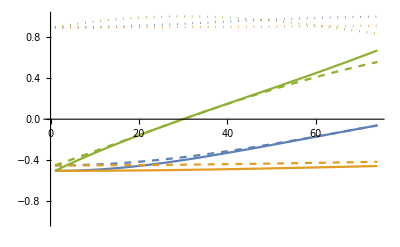

```mathematica
With[{modes=SingularValueDecomposition[#][[1]].#&@ochhBendVecs[[;;3]]},
Show[
Table[
1/(Divide@@getAngleComps[
displaceCoords[ochhCoords, d*#],
4, 2, 3
]),
{d, 0, 73, 1}
]&/@modes//ListLinePlot[#, PlotRange->{-1, 1}]&,
Table[
getAngleComps[
displaceCoords[ochhCoords, d*#],
4, 2, 3
][[1]],
{d, 0, 73, 1}
]&/@modes//ListLinePlot[#,PlotStyle->Dotted, PlotRange->{-1, 1}]&,
Table[
getAngleComps[
displaceCoords[ochhCoords, d*#],
4, 2, 3
][[2]],
{d, 0, 73, 1}
]&/@modes//ListLinePlot[#, PlotStyle->Dashed, PlotRange->{-1, 1}]&
]
]
```

```mathematica
ochhBendVecs//Dimensions
```

{6,12}

```mathematica
animateOCHH[ochhBendVecs[[3]], ViewPoint->{1, 1,1}]
```

```mathematica
animateOCHH[ochhBendVecs[[2]]]
```

```mathematica
getAngle[]
```

```mathematica
testAngles[
ochhCoords,
ochhModes.Transpose[
Join@@getOrthogSpaces[ochhCoords, ochhModes,4, 2, 1]
]//Threshold//Transpose,
{4, 2, 1}
]
```

{121.643,128.737,121.413,122.807,121.643,121.643,121.643}

```mathematica
testAngles[
ochhCoords,
ochhModes.Transpose[
Join@@getOrthogSpaces[ochhCoords, ochhModes,4, 1, 3]
]//Threshold//100*Transpose[#]&,
{4, 1, 3}
]
```

{124.717,145.137,134.584,164.983,124.717,124.717,124.717}

```mathematica
testAngles[
h2oCoords,
h2oModes.Transpose[
Join@@getOrthogSpaces[h2oCoords, h2oModes,2, 1, 3]
]//Threshold//100*Transpose[#]&,
{2, 1, 3}
]
```

{103.873,122.422,110.442,103.873}

```mathematica
testAngles[
h2oCoords,
h2oModes.Transpose[
Join@@getOrthogSpaces[h2oCoords, h2oModes,2, 1, 3]
]//Threshold//100*Transpose[#]&,
{2, 1, 3}
]
```

```mathematica
testAngles[
ch4Coords,
ch4Modes.Transpose[
Join@@getOrthogSpaces[ch4Coords, ch4Modes,2, 1, 3]
]//Threshold//100*Transpose[#]&,
{2, 1, 3}
]
```

{109.471,168.123,131.042,168.559,91.3451,109.471,109.471,109.471,109.471,109.471}

```mathematica
testAngles[
ch4Coords,
ch4Modes.Transpose[
Join@@getOrthogSpaces[ch4Coords, ch4Modes,1, 2, 3]
]//Threshold//100*Transpose[#]&,
{1, 2, 3}
]
```

{144.736,168.435,148.664,153.966,95.7205,144.736,144.736,144.736,144.736,144.736}

Bond Lengths

```mathematica
drMat[5, {1, 2, 3}].ch4Modes.
SingularValueDecomposition[
getDeltaProjModes[ch4Modes,{1, 2, 3}]
][[3]]//Threshold//MatrixForm
```

(0. | 0.0120114 | -0.00696143 | 0. | -0.0168723 | 0.000466877 | 0. | 0. | 0.
-0.00952471 | 0.00795207 | 0.0135253 | 0.0145574 | 2.31891×10^-10 | 0.00487956 | 0. | 0. | 0.
0.01347 | 0.000726775 | -0.00107684 | 0.0102936 | -3.61233×10^-10 | -0.0127124 | 0. | 0. | 0.
0. | -0.0120114 | 0.00696143 | 0. | -0.0168723 | -0.000466877 | 0. | 0. | 0.
0.00952471 | -0.0033359 | -0.00349319 | 0.0145574 | 2.94803×10^-10 | 0.0103588 | 0. | 0. | 0.
-0.01347 | -0.00725503 | -0.0131108 | 0.0102936 | -3.19343×10^-10 | -0.00883795 | 0. | 0. | 0.
0. | -0.0240229 | 0.0139229 | 0. | 1.074×10^-9 | -0.000933754 | 0. | 0. | 0.
0.0190494 | -0.011288 | -0.0170185 | 0. | 0. | 0.00547925 | 0. | 0. | 0.
-0.0269399 | -0.00798181 | -0.0120339 | 0. | 0. | 0.00387441 | 0. | 0. | 0.)

```mathematica
SingularValueDecomposition[getDeltaProjModes[h2oModes,{1, 2}]][[3]]
```

{{0.0471329,0.998348,-0.0328536},{0.70048,-0.00958687,0.713608},{0.712114,-0.0566477,-0.699775}}

```mathematica
getDeltaProjModes[h2oModes,{1, 2}]//Threshold//MatrixForm
```

(0. | 0. | 0.
0.00966779 | -0.0133677 | -0.0140858
0.0141849 | 0.0102589 | 0.00979571)

```mathematica
SingularValueDecomposition[getDeltaProjModes[h2oModes,{1, 2}]][[3]]//Threshold//MatrixForm
```

(0.0471329 | 0.998348 | -0.0328536
0.70048 | -0.00958687 | 0.713608
0.712114 | -0.0566477 | -0.699775)

```mathematica
getDeltaProjModes[h2o3DModes,{1, 2}]
```

(0.010701 | 0.0125558 | -0.0140858
0.0133235 | -0.0113553 | 0.00979571
0. | 0. | 0.)

```mathematica
getOrthogSpaces[h2o3DModes, 1, 2][[1]]//Transpose//MatrixForm
```

(-0.0087673 | 0.995944
-0.702009 | -0.0699013
0.712114 | -0.0566477)

```mathematica
h2o3DModes//MatrixForm
```

(6.15523×10^-16 | 5.7143×10^-15 | -0.00157641
0.00149109 | -0.00127083 | -3.9785×10^-15
2.67477×10^-17 | 3.44131×10^-16 | 5.69066×10^-17
-0.010701 | -0.0125558 | 0.0125094
-0.0118324 | 0.0100845 | -0.00979571
6.29303×10^-15 | 7.2506×10^-15 | 2.70945×10^-15
0.010701 | 0.0125558 | 0.0125094
-0.0118324 | 0.0100845 | 0.00979571
6.03605×10^-15 | 3.58921×10^-15 | 2.70945×10^-15)

```mathematica
getDeltaProjModes[h2o3DModes[[;;, ;;2]],{1, 2}]//Threshold//MatrixForm
```

(0.010701 | 0.0125558
0.0133235 | -0.0113553
0. | 0.)

```mathematica
SingularValueDecomposition[
getDeltaProjModes[h2o3DModes[[;;, ;;2]],{1, 2}]
][[1]]//Det
```

-1.

```mathematica
SingularValueDecomposition[
getDeltaProjModes[h2o3DModes[[;;, ;;2]],{1, 2}]
]//Map[MatrixForm@*Threshold]
```

{(9.3213×10^-9 | 1. | 0.
1. | -9.3213×10^-9 | 0.
0. | 0. | 1.),(0.0175059 | 0.
0. | 0.0164973
0. | 0.),(0.761083 | 0.648655
-0.648655 | 0.761083)}

```mathematica
SingularValueDecomposition[
getDeltaProjModes[h2o3DModes[[;;, ;;2]],{1, 2}]
][[3]]//MatrixForm
```

(0.761083 | 0.648655
-0.648655 | 0.761083)

```mathematica
getDeltaProjModes[h2o3DModes[[;;, ;;2]],{1, 2}].
SingularValueDecomposition[getDeltaProjModes[h2o3DModes[[;;, ;;2]],{1, 2}]][[3]]//Threshold//MatrixForm
```

(1.63178×10^-10 | 0.0164973
0.0175059 | -1.53776×10^-10
0. | 0.)

```mathematica
getDeltaProjModes[h2o3DModes[[;;, ;;2]],{1, 3}].
SingularValueDecomposition[getDeltaProjModes[h2o3DModes[[;;, ;;2]],{1, 3}]][[3]]//Threshold//MatrixForm
```

(-1.63236×10^-10 | -0.0164973
0.0175059 | -1.53831×10^-10
0. | 0.)

```mathematica
getDeltaProjModes[h2oModes,{1, 3}].SingularValueDecomposition[getDeltaProjModes[h2oModes,{1, 3}]][[3]]//Threshold//MatrixForm
```

(0. | 0. | 0.
-0.0189388 | -0.0105779 | 0.
-0.0148304 | 0.0135083 | 0.)

```mathematica
drMat[3, {1, 2}].
```

```mathematica
drMat[3, 1, 2][[;;3]].h2oModes.SingularValueDecomposition[getDeltaProjModes[h2oModes,1, 2]][[3]]//Threshold//MatrixForm
```

(0. | 0. | 0.
-0.0189388 | 0.0105779 | 0.
0.0148304 | 0.0135083 | 0.)

```mathematica
getDeltaProjModes[h2oModes,2, 3].SingularValueDecomposition[getDeltaProjModes[h2oModes,2, 3]][[3]]//Threshold//MatrixForm
```

(0. | 0. | 0.
-0.0329946 | 0. | 0.
0. | 0.0195914 | 0.)

```mathematica
Table[
Table[testDists[h2oModes,i, j], {j, i+1, 3}],
{i, 2}
]//Catenate
```

{{0.240545,0.171571,0.},{0.240545,0.171571,0.},{0.329946,0.195914,0.}}

```mathematica
Table[
Table[testDists[h2oModes,i, j, h2oCoords], {j, i+1, 3}],
{i, 2}
]//Catenate
```

{{2.06589,1.83339,1.82534},{1.5848,1.83339,1.82534},{2.54434,2.88096,2.87429}}

```mathematica
getDistProjections[h2oModes, 1, 2]//Transpose//Map[Norm]
```

{0.0240545,0.0171571,3.21456×10^-27}

```mathematica
Table[
Table[testDists[ochhModes,i, j], {j, i+1, 4}],
{i, 3}
]//Catenate
```

{{0.0894495,0.0508301,0.0430323,0.,0.,0.},{0.240545,0.20691,0.131298,0.,0.,0.},{0.240545,0.20691,0.131298,0.,0.,0.},{0.242906,0.233525,0.174331,0.,0.,0.},{0.242906,0.233525,0.174331,0.,0.,0.},{0.329946,0.309688,0.,0.,0.,0.}}

```mathematica
Table[
Table[testDists[ch4Modes,i, j], {j, i+1, 5}],
{i, 4}
]//Catenate
```

{{0.242906,0.219128,0.207541,0.,0.,0.,0.,0.,0.},{0.242906,0.219128,0.207541,0.,0.,0.,0.,0.,0.},{0.178349,0.147812,0.131917,0.,0.,0.,0.,0.,0.},{0.150865,0.113138,0.104281,0.,0.,0.,0.,0.,0.},{0.329946,0.279842,0.256771,0.,0.,0.,0.,0.,0.},{0.285778,0.23249,0.199128,0.,0.,0.,0.,0.,0.},{0.269482,0.210699,0.190406,0.,0.,0.,0.,0.,0.},{0.285778,0.23249,0.199128,0.,0.,0.,0.,0.,0.},{0.269482,0.210699,0.190406,0.,0.,0.,0.,0.,0.},{0.213133,0.137353,0.117232,0.,0.,0.,0.,0.,0.}}

Test Dists Old

```mathematica
ochhDistanceModes=ochhModes.Transpose[Join@@getOrthogSpaces[ochhModes, 1, 2] ]//Threshold;
```

```mathematica
Norm[#[[1]]-#[[2]]]&/@(ConstantArray[ochhCoords, 6]+5*ArrayReshape[Transpose@ochhDistanceModes, {6, 4, 3}])//Threshold
```

{2.26776,2.31262,2.31258,2.31248,2.31248,2.31248}

```mathematica
ch4DistModes=ch4Modes.Transpose[Join@@getOrthogSpaces[ch4Modes, 1, 2] ];
```

```mathematica
Norm[#[[1]]-#[[2]]]&/@(5*ArrayReshape[Transpose@ch4DistModes, {9, 5, 3}])//Threshold
```

{0.121453,0.109564,0.10377,0.,0.,0.,0.,0.,0.}

```mathematica
h2oDistModes=h2oModes.Transpose[Join@@getOrthogSpaces[h2oModes, 1, 2] ];
```

```mathematica
With[{modes=h2oModes},
With[{n=Dimensions[modes][[1]]/3},
Norm[#[[1]]-#[[2]]]&/@(5*ArrayReshape[Transpose@modes, {3*n-6, n, 3}])//Threshold
]
]
```

{0.0858311,0.0842524,0.0857854}

```mathematica
getOrthogSpaces[h2oModes, 1, 2]
```

{{{0.0471329,0.70048,0.712114},{0.998348,-0.00958687,-0.0566477}},{{-0.0328536,0.713608,-0.699775}}}

```mathematica
Transpose[Join@@getOrthogSpaces[h2oModes, 1, 2] ]//MatrixForm
```

(0.0471329 | 0.998348 | -0.0328536
0.70048 | -0.00958687 | 0.713608
0.712114 | -0.0566477 | -0.699775)

```mathematica
Transpose[Join@@getOrthogSpaces1[h2oModes, 1, 2] ]//MatrixForm
```

(-0.0328536 | 0.99946 | 0.0334662
0.713608 | 0.0234573 | 0.700546
-0.699775 | -0.0230026 | 0.712822)

```mathematica
getOrthogSpaces[h2oModes, 1, 2]
```

{{{0.0471329,0.70048,0.712114},{0.998348,-0.00958687,-0.0566477}},{{-0.0328536,0.713608,-0.699775}}}

Misc

```mathematica
orthoVecs=drMat[4, 1, 2][[;;3]].ochhModes//NullSpace;
```

```mathematica
goodVecs=Map[
Normalize,
IdentityMatrix[6][[;;3]].(IdentityMatrix[6]-Transpose[orthoVecs].orthoVecs)//Threshold
];
```

```mathematica
ochhModes//Dimensions
```

{12,6}

```mathematica
goodVecs.Transpose[goodVecs]
```

{{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

```mathematica
goodVecs.Transpose[orthoVecs]//Threshold
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
orthoVecs.Transpose[orthoVecs]//Threshold
```

{{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

```mathematica
ochhModes.Transpose[Join[goodVecs,orthoVecs] ]//Threshold//Dimensions
```

{12,6}

##### Redo

```mathematica
ochhModes.(IdentityMatrix[])
```

```mathematica
ochhModes.Transpose@Eigenvectors[ochhModes[[;;6]].Transpose[ochhModes[[;;6]]]]//Threshold//MatrixForm
```

(0. | 0. | -0.000197398 | 0. | 0. | -0.000815267
-9.9236×10^-6 | 0.000542801 | 0. | 7.29705×10^-6 | -0.00149384 | 0.
0.00128316 | 7.11332×10^-6 | 0.00327088 | 0.00174503 | 2.58469×10^-6 | -0.000791968
0. | 0. | 0.000815267 | 0. | 0. | 0.00336711
0.00181303 | -0.00101163 | 0. | -0.00133316 | 0.0027841 | 0.
-0.000374136 | 0.00124496 | -0.00488691 | -0.000508805 | 0.000452366 | 0.00118325
0. | 0. | -0.0032872 | 0. | 0. | -0.0135764
-0.0149967 | 0.0149598 | 0.00449035 | 0.00205612 | 0.0000917673 | -0.00108723
-0.00145372 | -0.00295495 | 0.00313818 | -0.0155988 | -0.0151345 | -0.000759837
0. | 0. | -0.0032872 | 0. | 0. | -0.0135764
-0.00643331 | -0.0115292 | -0.00449035 | 0.0137018 | -0.00953324 | 0.00108723
-0.0144562 | -0.0119814 | 0.00313818 | -0.00603781 | 0.00970724 | -0.000759837)

```mathematica
Transpose[lsMatOC].lsMatOC//MatrixForm
```

(1. | 2.26816×10^-15 | 1.62115×10^-15
2.26816×10^-15 | 1. | -3.86062×10^-17
1.62115×10^-15 | -3.86062×10^-17 | 1.)

```mathematica
lsMatOC//Orthogonalize//Threshold
```

{{0.,0.,-0.707107,0.,0.,0.707107},{0.,-0.462906,0.,0.,-0.886408,0.},{0.776891,0.,0.,0.629635,0.,0.},{-0.629635,0.,0.,0.776891,0.,0.},{0.,-0.886408,0.,0.,0.462906,0.},{0.,0.,0.,0.,0.,0.}}

```mathematica
Transpose[drMat[4, 1, 2][[4;;]]].(drMat[4, 1, 2][[4;;]])//MatrixForm
```

(1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Transpose[drMat[4, 1, 2]][[coordSel[1, 2]]][[;;3]]//MatrixForm
```

(1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1)

```mathematica
ochhModes[[coordSel[1, 2]]]//Chop//RowReduce//MatrixForm
```

(1 | 0. | 0. | 0. | 0. | 0.
0 | 1 | 0. | 0. | 0. | 0.
0 | 0 | 1 | 0. | 0.512898 | 0.
0 | 0 | 0 | 1 | -0.327859 | 0.
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ochhModes[[coordSel[1, 2]]]//Eigensystem//Transpose[#[[2]]].DiagonalMatrix[#[[1]]//Chop].Inverse[Transpose@#[[2]]]&//Chop
```

{{0.000838825,0,0,0,0,0},{0,-0.0015894,0,0,0,0.0000123177},{0,0,0.00216602,0.0033654,7.56835×10^-6,0},{-0.0034644,0,0,0,0,0},{0,0.0029622,0,0,0,-0.00225042},{0,0,-0.000631554,-0.00502812,0.0013246,0}}

```mathematica
With[{n=1, m=2},
With[{sel=coordSel[n, m]},
With[{p=Transpose[drMat[4, 1, 2]][[coordSel[1, 2]]][[;;3]]},
(IdentityMatrix[6]-Transpose[p].p)
]
]
]//MatrixForm
```

(0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | -1
-1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0)

```mathematica
Transpose[drMat[4, 1, 2]][[;;3]]
```

{{1,0,0,1,0,0},{0,1,0,0,1,0},{0,0,1,0,0,1}}

```mathematica
ochhModes//Dimensions
```

{12,6}

```mathematica
With[{n=1, m=2},
With[{sel=coordSel[n, m]},
With[{p=drMat[4, n, m][[4]]},
ochhModes[[;;, 1]]-p*p.ochhModes[[;;, 1]]
]
]
]
```

{0.0034644,8.40135×10^-19,3.12686×10^-21,-0.000838825,-2.15655×10^-18,1.26219×10^-18,0.0139687,-7.09877×10^-18,-2.72106×10^-18,0.0139687,1.94429×10^-17,-1.23572×10^-17}

```mathematica
With[{n=1, m=2},
With[{sel=coordSel[n, m]},
With[{p=Normalize/@(drMat[4, n, m][[4;;, sel]])},
ochhModes.Transpose[Normalize/@Transpose@
LeastSquares[
(IdentityMatrix[6]-Transpose[p].p).ochhModes[[sel]],
Normalize/@(drMat[4, n, m][[;;3, sel]])//Transpose
]
]
]
]
]//Threshold//MatrixForm
```

(0.000838825 | 0. | 0.
0. | 0.00142872 | 0.
0. | 0. | 0.00383425
-0.0034644 | 0. | 0.
0. | -0.0036543 | 0.
0. | 0. | -0.0051107
0.0139687 | 0. | 0.
0. | 0.0104182 | 0.
0. | 0.00824151 | 0.
0.0139687 | 0. | 0.
0. | 0.0104182 | 0.
0. | -0.00824151 | 0.)

```mathematica
With[{n=1, m=2},
With[{sel=coordSel[n, m]},
With[{p=Normalize/@(drMat[4, n, m][[;;3, sel]])},
ochhModes.Transpose[Normalize/@Transpose@
LeastSquares[
(IdentityMatrix[6]-Transpose[p].p).ochhModes[[sel]],
Normalize/@(drMat[4, n, m][[4;;, sel]])//Transpose
]
]
]
]
]//Threshold//MatrixForm
```

(-0.000838825 | 0. | 0.
0. | -0.000841524 | 0.
0. | 0. | -0.0008615
0.0034644 | 0. | 0.
0. | 0.00346711 | 0.
0. | 0. | 0.00348712
-0.0139687 | 0. | 0.
0. | -0.0139633 | 0.
0. | -0.0000309736 | -0.013924
-0.0139687 | 0. | 0.
0. | -0.0139633 | 0.
0. | 0.0000309736 | -0.013924)

```mathematica
With[{n=1, m=2},
With[{sel=coordSel[n, m]},
ochhModes.Transpose[
Normalize/@Transpose@
LeastSquares[
ochhModes[[sel]],
Normalize/@(drMat[4, n, m][[;;, sel]])//Transpose
]
]
]
]//Threshold//MatrixForm
```

(0.000838825 | 0. | 0. | -0.000838825 | 0. | 0.
0. | 0.0013484 | 0. | 0. | 0.000696504 | 0.
0. | 0. | 0.00390838 | 0. | 0. | 0.00114723
-0.0034644 | 0. | 0. | 0.0034644 | 0. | 0.
0. | -0.0013484 | 0. | 0. | 0.000696504 | 0.
0. | 0. | -0.00390838 | 0. | 0. | 0.00114723
0.0139687 | 0. | 0. | -0.0139687 | 0. | 0.
0. | -0.00267246 | 0. | 0. | -0.00967358 | 0.
0. | 0.0154844 | -0.0077462 | 0. | 0.0131089 | -0.0159336
0.0139687 | 0. | 0. | -0.0139687 | 0. | 0.
0. | -0.00267246 | 0. | 0. | -0.00967358 | 0.
0. | -0.0154844 | -0.0077462 | 0. | -0.0131089 | -0.0159336)

```mathematica
With[{n=1, m=2},
With[{sel=coordSel[n, m]},
With[{p=Normalize/@(drMat[4, n, m][[4;;, sel]])},
(IdentityMatrix[6]-Transpose[p].p).ochhModes[[sel]]
]
]
]//Threshold//MatrixForm
```

(0.00215161 | 0. | 0. | 0. | 0. | 0.
0. | -0.0022758 | 0. | 0. | 0. | 0.00113137
0. | 0. | 0.00139879 | 0.00419676 | -0.000658513 | 0.
-0.00215161 | 0. | 0. | 0. | 0. | 0.
0. | 0.0022758 | 0. | 0. | 0. | -0.00113137
0. | 0. | -0.00139879 | -0.00419676 | 0.000658513 | 0.)

```mathematica
lsMatOC=With[{n=1, m=2},
With[{sel=coordSel[n, m]},
Transpose@Map[
Normalize,
Transpose@LeastSquares[
ochhModes[[sel]],
Transpose[Reverse@drMat[4, n, m]][[sel]]
]
]
]
];
ochhModes.lsMatOC//Threshold[#, 1*^-5]&//Transpose//MatrixForm
```

(0. | 0. | 0.00114723 | 0. | 0. | 0.00114723 | 0. | 0. | -0.0159336 | 0. | 0. | -0.0159336
0. | 0.000696504 | 0. | 0. | 0.000696504 | 0. | 0. | -0.00967358 | 0.0131089 | 0. | -0.00967358 | -0.0131089
-0.000838825 | 0. | 0. | 0.0034644 | 0. | 0. | -0.0139687 | 0. | 0. | -0.0139687 | 0. | 0.
0. | 0. | 0.00390838 | 0. | 0. | -0.00390838 | 0. | 0. | -0.0077462 | 0. | 0. | -0.0077462
0. | 0.0013484 | 0. | 0. | -0.0013484 | 0. | 0. | -0.00267246 | 0.0154844 | 0. | -0.00267246 | -0.0154844
0.000838825 | 0. | 0. | -0.0034644 | 0. | 0. | 0.0139687 | 0. | 0. | 0.0139687 | 0. | 0.)

```mathematica
Eigenvalues[ochhModes[[coordSel[1, 2]]]]//Threshold
```

{0.00216742+0. ⅈ,-5.11098×10^-6+0.00172336 ⅈ,-5.11098×10^-6-0.00172336 ⅈ,-0.00158058+0. ⅈ,0.000838825+0. ⅈ,0.+0. ⅈ}

```mathematica
lsMatNH//MatrixForm
```

(-0.0000437995 | 0.233827 | -0.233827
0.00226847 | -0.536611 | 0.536611
0.0658687 | 0.0176607 | -0.0176607
-0.000125001 | 0.667327 | -0.667327
0.0000861942 | -0.460148 | 0.460148
0.997826 | 9.553×10^-11 | -9.553×10^-11)

```mathematica
RowReduce[Transpose[nh3Modes]]//Threshold[#, 1*^-8]&//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | -6.92675 | -4.01095 | -3.24993 | -6.9676 | 4.01095 | 3.24993
0. | 1. | 0. | 0. | 0. | 0. | -2.77316×10^9 | -0.409191 | -6.71178 | 2.77316×10^9 | -1.03294 | -4.52794
0. | 0. | 1. | 0. | 0. | 0. | 3.42254×10^9 | -8.06896 | 1.33628 | -3.42254×10^9 | -7.29915 | -1.35895
0. | 0. | 0. | 1. | 0. | 0. | -0.518576 | -0.866025 | 0. | -0.481424 | 0.866025 | 0.
0. | 0. | 0. | 0. | 1. | 0. | -0.699732 | -0.5 | 0. | 0.699732 | -0.5 | 0.
0. | 0. | 0. | 0. | 0. | 1. | 7.38979×10^8 | -1.74221 | 1.28852 | -7.38979×10^8 | -1.576 | 0.706583)

```mathematica
animateOCHH[(ochhBigRealModes.Transpose[lsMat2])[[;;, 4]]]
```

```mathematica
lsMat.Transpose[lsMat]//Threshold//MatrixForm
```

(1. | 0. | 0. | -1. | 0. | 0.
0. | 1. | 0. | 0. | 0.847653 | 0.
0. | 0. | 1. | 0. | 0. | 0.486154
-1. | 0. | 0. | 1. | 0. | 0.
0. | 0.847653 | 0. | 0. | 1. | 0.
0. | 0. | 0.486154 | 0. | 0. | 1.)

```mathematica
lsMatOH=
Transpose@
LeastSquares[
ochhModes[[4;;9]],
Transpose[drMat[4, 2, 3]][[4;;9]]
];
ochhModes.Transpose[lsMatOH]//Threshold//MatrixForm
```

(-0.0706011 | 0. | 0. | 0.0425405 | 0. | 0.
0. | -0.329161 | -0.00915434 | 0. | -0.354677 | 0.0457073
0. | -0.16619 | -0.6417 | 0. | -0.214911 | -0.78898
0.291587 | 0. | 0. | -0.175695 | 0. | 0.
0. | 1. | 0. | 0. | 1. | 0.
0. | 0. | 1. | 0. | 0. | 1.
-1.1757 | 0. | 0. | 0.708413 | 0. | 0.
0. | -1. | 0. | 0. | 1. | 0.
0. | 0. | -1. | 0. | 0. | 1.
-1.1757 | 0. | 0. | 0.708413 | 0. | 0.
0. | -5.6828 | 0.145286 | 0. | -7.27784 | -0.725408
0. | 2.63755 | -0.722582 | 0. | 3.4108 | -0.385141)

```mathematica
lsMat=
Normalize/@Transpose@
LeastSquares[
ochhModes[[;;6]],
Transpose[Amat][[;;6]]
];
```

```mathematica
tr=lsMat[[;;3]];
```

```mathematica
Sbase=Det[];
Sr=tr.IdentityMatrix[6].Transpose[tr];
Sr//Det
```

1.

```mathematica
rFunc[q1_, q2_, q3_]:=
Norm[ochhCoords+{q1, q2, q3}.tr]
```

##### Test Integral

```mathematica
basePot=
0.20303895152520812(1-Exp[-1.1501821113857027(
Sqrt[(δ10+δ1)^2+(δ20+δ2)^2+(δ30+δ3)^2]-
Sqrt[(δ10)^2+(δ20)^2+(δ30)^2]
)
])^2;
```

Stretch Bend

```mathematica
(DGBN[{0, 0}, {0.00369336, 0.00875559}]*DGBN[{0, 0}, {0.00369336, 0.00875559}])
```

0.0425453 DGBN[{0.,0.},{0.00738672,0.0175112}]

```mathematica
r12Pot=basePot/.Flatten@{
Thread[
{δ1, δ2, δ3}->
getDeltaProjModes[h2o2DModes, 1, 2].{q1, q2}
],
Thread[
{δ10, δ20, δ30}->
drMat[Length[h2o2DCoords], {1, 2}].Flatten[h2o2DCoords]
]
};
```

```mathematica
Plot3D[
DGBN[{0.,0.},{0.00738672,0.01751118}][q1, q2]*
r12Pot,
{q1, -30, 30},
{q2, -30, 30},
PlotRange->All
]
```

-Graphics3D-

```mathematica
NIntegrate[
 DGBN[{0.,0.},{0.00738672,0.01751118}][q1, q2]*
r12Pot,
{q1, -50, 50},
{q2, -50, 50}
]
```

0.0516785

Stretch

```mathematica
Grad[
Grad[
basePot,
{δ1, δ2, δ3}
],
{δ1, δ2, δ3}
]/.Flatten@{
Thread[
{δ1, δ2, δ3}->
getDeltaProjModes[h2o2DStretchModes, 1, 2].{0, 0}
],
Thread[
{δ10, δ20, δ30}->
drMat[Length[h2o2DStretchCoords], {1, 2}].Flatten[h2o2DStretchCoords]
]
}//MatrixForm
```

(0.333008 | -0.260769 | 0.
-0.260769 | 0.2042 | 0.
0. | 0. | 0.)

```mathematica
r12StretchPot=basePot/.Flatten@{
Thread[
{δ1, δ2, δ3}->
getDeltaProjModes[h2o2DStretchModes, 1, 2].{q1, q2}
],
Thread[
{δ10, δ20, δ30}->
drMat[Length[h2o2DStretchCoords], {1, 2}].Flatten[h2o2DStretchCoords]
]
};
```

```mathematica
Grad[
Grad[
r12StretchPot, 
{q1, q2}
],
{q1, q2}
]/.Thread[{q1, q2}->{0, 0}]
```

{{0.00015321,-0.000155403},{-0.000155403,0.000157628}}

```mathematica
Plot3D[
DGBN[{0.,0.},{0.01750486,0.01775544}][q1, q2]*
r12StretchPot,
{q1, -30, 30},
{q2, -30, 30},
PlotRange->All
]
```

```mathematica
With[{bounds=50},
NIntegrate[
 DGBN[{0.,0.},{0.01750486,0.01775544}][q1, q2]*
r12StretchPot,
{q1, -bounds, bounds},
{q2, -bounds, bounds},
MaxRecursion->2000
]
]
```

```mathematica
0.08641399455645421*0.05297031871375703
```

0.00457738

```mathematica
(DGBN[{0.,0.},{0.00875243, 0.00887772}]*DGBN[{ 2.13455735,  2.13455748},{0.00933326, 0.00946799}])
```

0.0516296 DGBN[{1.10155,1.10162},{0.0180857,0.0183457}]

```mathematica
With[{bounds=50},
NIntegrate[
 DGBN[{1.1015548056204103,1.1016182461766375},{0.01808569,0.01834571}][q1, q2]*
r12StretchPot,
{q1, -bounds, bounds},
{q2, -bounds, bounds},
MaxRecursion->2000
]
]
```

0.0821066

```mathematica
0.0516296*0.0821066
```

0.00423913

```mathematica
"[[0.00875243 0.00887772]
 [0.00824452 0.00836127]
 [0.00933326 0.00946799]] [[ 0.          0.        ]
 [-2.13455771  2.13455748]
 [ 2.13455735  2.13455748]]"
```

##### HOD Stretch

```mathematica
rDelt=(
Sqrt[(δ10+δ1)^2+(δ20+δ2)^2+(δ30+δ3)^2]-
Sqrt[(δ10)^2+(δ20)^2+(δ30)^2]
);
```

```mathematica
hohPot=
0.20303895152520812(1-Exp[-1.1501821113857027*rDelt])^2;
```

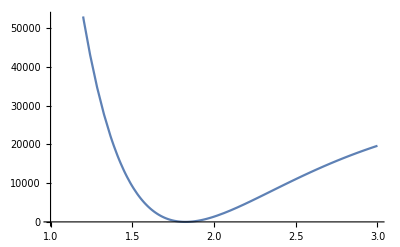

```mathematica
Plot[
hodPot*219475,
{r, 1, 3}
]
```

```mathematica
Grad[
Grad[
hodPot/.r->rDelt,
{δ1, δ2, δ3}
],
{δ1, δ2, δ3}
]/.Flatten@{
Thread[
{δ1, δ2, δ3}->
getDeltaProjModes[hod2DStretchModes, 1, 3].{0, 0}
],
Thread[
{δ10, δ20, δ30}->
drMat[Length[hod2DStretchCoords], {1, 3}].Flatten[hod2DStretchCoords]
]
}//MatrixForm
```

(111.882 | 40.2169 | 3.83634×10^-30
40.2169 | -12.4617 | 1.13264×10^-30
3.83634×10^-30 | 1.13264×10^-30 | -24.3353)

```mathematica
Norm[h2o2DCoords[[1]]-h2o2DCoords[[2]]]
```

1.82534

```mathematica
Grad[
Grad[
hohPot/.r->rDelt,
{δ1, δ2, δ3}
],
{δ1, δ2, δ3}
]/.Flatten@{
Thread[
{δ1, δ2, δ3}->
getDeltaProjModes[hod2DStretchModes, 1, 2].{0, 0}
],
Thread[
{δ10, δ20, δ30}->
drMat[Length[hod2DStretchCoords], {1, 2}].Flatten[hod2DStretchCoords]
]
}//MatrixForm
```

(0.136925 | -0.234113 | 0.
-0.234113 | 0.400284 | 0.
0. | 0. | 0.)

```mathematica
Grad[
Grad[
hohPot,
{δ1, δ2, δ3}
],
{δ1, δ2, δ3}
]/.Flatten@{
Thread[
{δ1, δ2, δ3}->
drMat[Length[hod2DStretchCoords], {1, 2}].Flatten[hod2DStretchCoords]
],
Thread[
{δ10, δ20, δ30}->
drMat[Length[hod2DStretchCoords], {1, 2}].Flatten[hod2DStretchCoords]
]
}//MatrixForm
```

(-0.00241645 | 0.0276492 | 0.
0.0276492 | -0.0335197 | 0.
0. | 0. | 0.0137546)

### Complex Phase Quadrature

We know from the work on projections that we can reduce the integrals down to the form

∫V(δ)exp(-1/2(Σ_δ)^-1⊙(q_δ-μ_δ)^2 + 𝕚(Σ_δ p)·q_δ)

and by expanding the product (and doing some shifts by μ) we get

∫V(δ)exp(-1/2(Σ_δ)^-1⊙(q_δ-μ_δ)^2 + 𝕚(Σ_δ p)·q_δ) =∫V(δ+μ)exp(𝕚(Σ_δ p)·(δ+μ))exp(-1/2(Σ_δ)^-1⊙δ^2)

where can evaluate the inner integral by Gauss Hermite quadrature, although we will first diagonalize Σ_δ and use the transformation to write y_k = L_k(q−μ)

∫V(δ-μ)exp(𝕚(Σ_δ p)·δ)exp(-(Σ_δ)^-1⊙δ^2) = ∫V(δ) ∏_k exp(𝕚(Σ_δ p)·(Lᵀy)_k) exp(-α_k y_k^2)

taking the appropriate direct product of 1D quadrature points and weights to get (for vector x)

∫V(δ)exp(𝕚(Σ_δ p)·δ)exp(-(Σ_δ)^-1⊙(δ-μ_δ)^2) = ∑_x w_x V(x)exp(𝕚(Σ_δ p)·(x-μ))
= ∑_x w_x V(x)(cos((Σ_δ p)·x) + 𝕚 sin((Σ_δ p)·x))

and upon rephasing, we will take the ± combinations of the 𝕚sin((Σ_δ p)·x)) terms to recover entirely real eigenvalues, and therefore can omit those terms in the calculations

## Gram-Schmidt Orthogonalized Gaussians

Given two distributed Gaussians, ϕ_1, ϕ_2 we can obviously orthogonalize this system by writing

φ_2 = ϕ_2 - ϕ_1 ϕ_2 ϕ_1

which has corresponding norm

φ_2 φ_2 = ϕ_2 ϕ_2 - ϕ_1 ϕ_2ϕ_1 ϕ_2 + ϕ_1 ϕ_2 - ϕ_1 ϕ_2ϕ_1 ϕ_1
= 1 - (ϕ_1 ϕ_2)^2

and then if we want to introduce a third Gaussian, ϕ_3, we can orthogonalize this relative to the initial set of Gaussians by writing

φ_3 = ϕ_3 - ϕ_1 ϕ_3 ϕ_1 - ϕ_2 ϕ_3 ϕ_2

or we can orthogonalize relative the the new set by

φ_3 = ϕ_3 - ϕ_1 ϕ_3 ϕ_1 - (φ_2 ϕ_3)/(φ_2 φ_2)φ_2

##### Partial Orthog Reduction

which almost orthogonal to φ_2, that being a simple linear combination of ϕ_1 and ϕ_2, therefore this has a norm given by (reduction done as I went)

φ_3 φ_3 = 1 - (ϕ_1 ϕ_3)^2- (ϕ_2 ϕ_3)^2 + 2ϕ_1 ϕ_3ϕ_2 ϕ_3ϕ_1 ϕ_2

and introducing a n-th function, the orthogonalization is obvious but the normalization comes out to

φ_3 φ_3 = 1 - ∑_(i<4) (ϕ_i ϕ_4)^2 + ∑_(j<4) ϕ_i ϕ_4∑_(i<4≠j) ϕ_j ϕ_4ϕ_i ϕ_j

##### Full Orthog Reduction

and generically we can write this as

φ_k = ϕ_k - ∑_(i=1)^(k-1) OverBar[φ_i]  ϕ_k φ_i
OverBar[φ_i]  ϕ_k = (φ_i ϕ_k)/(φ_i φ_i)

which inductively is

φ_1 = ϕ_1
φ_2 = ϕ_2 - ϕ_1 ϕ_2 ϕ_1
φ_3 = ϕ_3 - ϕ_1 ϕ_3 ϕ_1 - OverBar[φ_2]  ϕ_3 φ_2
= ϕ_3 - ϕ_1 ϕ_3 ϕ_1 - OverBar[φ_2]  ϕ_3 ϕ_2 + OverBar[φ_2]  ϕ_3ϕ_1 ϕ_2 ϕ_1
= ϕ_3 - (ϕ_1 ϕ_3 + OverBar[φ_2] ϕ_3ϕ_1 ϕ_2)ϕ_1 - OverBar[φ_2]  ϕ_3 ϕ_2
φ_4 = ϕ_4 - ϕ_1 ϕ_4 ϕ_1 - OverBar[φ_2] ϕ_4 φ_2 - OverBar[φ_3] ϕ_4 φ_3
= ϕ_4 - (ϕ_1 ϕ_3 + OverBar[φ_2] ϕ_3ϕ_1 ϕ_2)ϕ_1 - OverBar[φ_2]  ϕ_3 ϕ_2 
      - OverBar[φ_3] ϕ_4(ϕ_3 - (ϕ_1 ϕ_3 + OverBar[φ_2] ϕ_3ϕ_1 ϕ_2)ϕ_1 - OverBar[φ_2]  ϕ_3 ϕ_2)

we’ll note that we can also write

Γ_k = ϕ_k - ∑_(i=1)^(k-1) ϕ_i  ϕ_k ϕ_i
φ_k = Γ_k - ∑_(i=1)^(k-1) OverBar[Γ_i]  ϕ_k Γ_i
= ϕ_k - ∑_(i=1)^(k-1) ϕ_i  ϕ_k ϕ_i

#### Algorithm with Pivoting

Generically, we have a basis of {ϕ_i} functions that we would like to turn into {φ_i} orthogonalized functions

To do this, we can almost use standard Gram-Schmidt with pivoting, in which the function φ_i is computed by removing the contribution from all {φ_(i−1)} functions from every {ϕ_(i+1)} and then the one with the largest remaining norm is φ_i. This removes much of the order-dependence and improve the numerical stability.

The only difference is that our norms must be computed via the overlap matrix, i.e. if we have

f = ∑_k c_k ϕ_k

then

ϕ_i f = ∑_k c_k ϕ_i ϕ_k = ∑_k c_k S_ik

##### Tests

```mathematica
ClearAll[gsN, gsV, fgsV];
gsN[ϕ[i_], ϕ[i_]]:=1;
gsN[ϕ[i_], ϕ[j_]]/;j<i:=gsN[ϕ[j], ϕ[i]];
gsN[a:Except[_ϕ], b_]:=a/.{
g_gsN:>g,
f_ϕ:>gsN[f, b]
};
gsN[a_ϕ, b:Except[_ϕ]]:=b/.{
g_gsN:>g,
f_ϕ:>gsN[a, f]
};
Format[gsN[ϕ[i_], ϕ[j_]]]:=Style[Row@{"⟨",Subscript[ϕ, i], "|", Subscript[ϕ, j], "⟩"}, ShowStringCharacters->False];
gsV[ϕ[j_]]:=
gsV[ϕ[j]]=ϕ[j]-Sum[gsN[ϕ[i], ϕ[j]]*ϕ[i], {i, j-1}];
fgsV[ϕ[j_]]:=
fgsV[ϕ[j]]=ϕ[j]-Sum[
gsN[fgsV[ϕ[i]],ϕ[j]]/
gsN[fgsV[ϕ[i]],fgsV[ϕ[i]]]*fgsV[ϕ[i]], 
{i, j-1}
];
subGSN[expr_, sMat_]:=
expr/.gsN[ϕ[i_], ϕ[j_]]:>sMat[[i, j]];
subGSN[sMat_][expr_]:=subGSN[expr, sMat];
gsCoeff[expr_]:=
expr//Expand//ReplaceAll[{
g_gsN:>g,
ϕ[k_]:>Power[ϕ, k]
}]//CoefficientList[#, ϕ]&//Rest;
gsSimp[expr_]:=
Block[
{
norms=DeleteDuplicates@Cases[
expr,
_gsN,
Infinity
],
syms,
simpExpr,
normsMap=<||>
},
syms=norms/.g:gsN[ϕ[i_], ϕ[j_]]:>
With[{s=Symbol["s"<>ToString[i]<>ToString[j]]},
normsMap[s]=g;
s
];
simpExpr=expr/.gsN[ϕ[i_], ϕ[j_]]:>Symbol["s"<>ToString[i]<>ToString[j]];
Assuming[
And@@Map[GreaterThan[0], syms],
Expand[simpExpr]//FullSimplify
]//ReplaceAll[s_Symbol:>Lookup[normsMap, s, s]]
]
```

```mathematica
sssss=getOverlapMatrix[{{1/2}, {2},{3}, {1}}, {{1/2},{1/2},{1/2}, {1/2}}];
```

```mathematica
sssss[[;;, {1, 3, 2, 4}]][[{1, 3, 2, 4}, ;;]]//simpleOrtho[#, Length@#]&//MatrixForm
```

(1. | 0 | 0 | 0
-0.214374 | 1.02272 | 0 | 0
-0.905336 | -1.46838 | 2.1291 | 0
-5.31883 | 1.7246 | -4.59091 | 8.06158)

```mathematica
"[[ 1.          0.20961139  0.56978282  0.93941306]
 [-0.21437375  1.02271995  0.77880078  0.36787944]
 [-1.29951366 -2.10769702  3.0560959   0.77880078]
 [-0.90192935 -0.17882478  0.          1.        ]]"
```

```mathematica
sssss//ExportString[#, "PythonExpression"]&
```

[[1., 0.569782824730923, 0.2096113871510978, 0.9394130628134758], [0.569782824730923, 1., 0.7788007830714049, 0.7788007830714049], [0.2096113871510978, 0.7788007830714049, 1., 0.36787944117144233], [0.9394130628134758, 0.7788007830714049, 0.36787944117144233, 1.]]

```mathematica
"[[ 1.          0.20961139  0.56978282  0.93941306]
 [-0.21437375  1.02271995  0.77880078  0.36787944]
 [-1.3606815  -2.20690588  3.1999457   0.77880078]
 [-0.90192935 -0.17882478  0.          1.        ]]"
```

```mathematica
"[[ 1.          0.20961139  0.56978282  0.93941306]
 [-0.21437375  1.02271995  0.77880078  0.36787944]
 [-1.29951366 -2.10769702  3.0560959   0.77880078]
 [-0.90192935 -0.17882478  0.          1.        ]]"
```

```mathematica
simpleOrtho[sssss, 4]//MatrixForm
```

(1. | 0 | 0 | 0
-0.693339 | 1.21685 | 0 | 0
0.620379 | -1.7471 | 1.78944 | 0
-5.31883 | -4.59091 | 1.7246 | 8.06158)

```mathematica
DiagonalMatrix[1/Diagonal[#]].#&@QRDecomposition[sssss][[2]]//MatrixForm
```

(1. | 0.903753 | 0.536879 | 1.06601
0. | 1. | 1.24633 | 0.301311
0. | 0. | 1. | -0.228698
0. | 0. | 0. | 1.)

```mathematica
DiagonalMatrix[1/Diagonal[#]].#&@simpleOrtho[sssss, 4]//MatrixForm
```

(1. | 0. | 0. | 0.
-0.569783 | 1. | 0. | 0.
0.34669 | -0.976339 | 1. | 0.
-0.659775 | -0.56948 | 0.213928 | 1.)

```mathematica
Transpose[QRDecomposition[sssss][[2]]]//MatrixForm
```

(-1.50036 | 0. | 0. | 0.
-1.35596 | -0.836118 | 0. | 0.
-0.805513 | -1.04208 | -0.225899 | 0.
-1.5994 | -0.251931 | 0.0516627 | 0.0114519)

```mathematica
QRDecomposition[sssss]//Map[MatrixForm]
```

{(-0.666506 | -0.379764 | -0.139707 | -0.626124
0.39943 | -0.580129 | -0.704881 | 0.0839557
-0.393841 | 0.582748 | -0.67696 | 0.216837
-0.491035 | -0.423833 | 0.159215 | 0.744246),(-1.50036 | -1.35596 | -0.805513 | -1.5994
0. | -0.836118 | -1.04208 | -0.251931
0. | 0. | -0.225899 | 0.0516627
0. | 0. | 0. | 0.0114519)}

```mathematica
{bbbb, asdasd} = Eigensystem[sssss];
```

```mathematica
Transpose[asdasd].sssss//MatrixForm
```

(-1.14404 | -0.799529 | -0.196847 | -1.1755
-0.921515 | -0.860438 | -0.695278 | -0.955934
0.291422 | 1.05349 | 1.08621 | 0.562453
-0.0901821 | -0.219708 | -0.289449 | -0.111327)

```mathematica
fgsV[ϕ[2]]//gsCoeff//gsSimp//subGSN[sssss]
```

{-0.569783,1}

```mathematica
fgsV[ϕ[3]]//gsCoeff//gsSimp//subGSN[sssss]
```

{0.34669,-0.976339,1}

```mathematica
fgsV[ϕ[4]]//gsCoeff//gsSimp//subGSN[sssss]
```

{-0.659775,-0.56948,0.213928,1}

```mathematica
ClearAll[gsnorm,gsify, simpleOrtho];
gsnorm[vec_, sMat_]:=
Dot[
Flatten@sMat[[;;Length@vec, ;;Length@vec]],
Flatten@Outer[Times, vec, vec]
];
gsify[vec_, vecs_]:=(* assume normed *)
Append[ConstantArray[0, Length@vec-1], 1]-
Sum[(vec.v)*v, {v, vecs}];
gsify[vec_, vecs_, sMat_]:=
Append[ConstantArray[0, Length@vec-1], 1]-
Sum[(vec.v)*v/Sqrt[gsnorm[v, sMat]], {v, vecs}];
simpleOrtho[sMat_, k_Integer, 
normalize:True|False:True
]:=
If[k==1,
{{1.}},
With[{m=ArrayPad[simpleOrtho[sMat, k-1, normalize],{{0, 0} , {0, 1}}]},
Append[
m,
If[normalize,
#/Sqrt[gsnorm[#, sMat]]&@
gsify[sMat[[k, ;;k]], m],
gsify[sMat[[k, ;;k]], m, sMat]
]
]
]
]
```

```mathematica
Outer[Times, {1/4, 1/3, 1/2, 1}, {1/4, 1/3, 1/2, 1}]//MatrixForm
```

(1/16 | 1/12 | 1/8 | 1/4
1/12 | 1/9 | 1/6 | 1/3
1/8 | 1/6 | 1/4 | 1/2
1/4 | 1/3 | 1/2 | 1)

```mathematica
simpleOrtho[sssss, 4, True]//MatrixForm
```

(1. | 0 | 0 | 0
-0.693339 | 1.21685 | 0 | 0
0.620379 | -1.7471 | 1.78944 | 0
-5.31883 | -4.59091 | 1.7246 | 8.06158)

```mathematica
Or
```

```mathematica
sssss//ExportString[#, "PythonExpression"]&
```

[[1., 0.569782824730923, 0.2096113871510978, 0.9394130628134758], [0.569782824730923, 1., 0.7788007830714049, 0.7788007830714049], [0.2096113871510978, 0.7788007830714049, 1., 0.36787944117144233], [0.9394130628134758, 0.7788007830714049, 0.36787944117144233, 1.]]

```mathematica
simpleOrtho[sssss, 4, True]//MatrixForm
```

(1. | 0 | 0 | 0
-0.693339 | 1.21685 | 0 | 0
0.620379 | -1.7471 | 1.78944 | 0
-5.31883 | -4.59091 | 1.7246 | 8.06158)

```mathematica
[array([1.]),
array([-0.6933391,1.21684802]),
array([0.62037876,-1.74709538,1.78943607]),array([-5.3188295,-4.59090562,1.72459874,8.06157955])]
```

```mathematica
Orthogonalize[
{ϕ[1], ϕ[2], ϕ[3], ϕ[4]},
gsN
]//Map[gsCoeff]//subGSN[sssss]
```

{{1},{-0.693339,1.21685},{0.620379,-1.7471,1.78944},{-5.31883,-4.59091,1.7246,8.06158}}

```mathematica
huh=simpleOrtho[sssss, 4];
huh//MatrixForm
```

(1. | 0 | 0 | 0
-0.693339 | 1.21685 | 0 | 0
0.620379 | -1.7471 | 1.78944 | 0
-5.31883 | -4.59091 | 1.7246 | 8.06158)

```mathematica
1/8.061579549783678^2
```

0.0153872

```mathematica
Orthogonalize[
{ϕ[1], ϕ[2], ϕ[3], ϕ[4]},
gsN
]//Map[gsCoeff]//subGSN[sssss]
```

{{1},{-0.693339,1.21685},{0.620379,-1.7471,1.78944},{-5.31883,-4.59091,1.7246,8.06158}}

Ploots

```mathematica
orthoBasis[centers_, alphas_, x_:x]:=
simpleOrtho[getOverlapMatrix[centers, alphas], Length@centers, False].MapThread[
DGB[#[[1]], #2[[1]]][x]&,
{alphas, centers}
]//Simplify
```

```mathematica
orthoBasis[
{{1/2}, {2},{3}, {1}}, 
{{1/2},{1/2},{1/2}, {1/2}}
]
```

{0.751126 ⅇ^(-1/8 (1-2 x)^2),-0.427978 ⅇ^(-1/8 (1-2 x)^2)+0.751126 ⅇ^(-1/2 (-2+x)^2),0.185944 ⅇ^(-1/8 (1-2 x)^2)+0.751126 ⅇ^(-1/2 (-3+x)^2)-0.602666 ⅇ^(-1/2 (-2+x)^2),-0.570909 ⅇ^(-1/8 (1-2 x)^2)+0.0318194 ⅇ^(-1/2 (-3+x)^2)-0.248127 ⅇ^(-1/2 (-2+x)^2)+0.751126 ⅇ^(-1/2 (-1+x)^2)}

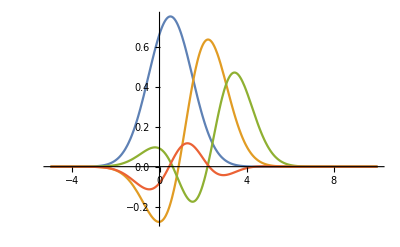

```mathematica
Plot[
orthoBasis[
{{1/2}, {2},{3}, {1}}, 
{{1/2},{1/2},{1/2}, {1/2}}
]//Evaluate,
{x, -5, 10},
PlotRange->All
]
```

```mathematica
BlockRandom@
simpleOrtho[
BlockRandom@getOverlapMatrix[
RandomReal[{-3, 3}, {8, 1}], 
RandomReal[{.2, 1}, {8, 1}]
], 8, 
True
]
```

{{1.,0,0,0,0,0,0,0},{-0.731658,1.23908,0,0,0,0,0,0},{0.0365454,-0.0882506,1.00265,0,0,0,0,0},{0.200129,-0.739869,-1.22161,1.73711,0,0,0,0},{0.278098,-1.02483,4.10241,-33.2846,30.8472,0,0,0},{0.165337,-0.919693,-10.9684,-4.04534,6.68702,9.82945,0,0},{0.355414,-4.11107,5.62907,145.437,-157.468,-14.9251,21.7111,0},{-5.41318,-10.9148,1.4019,40.0864,-43.3801,-3.97072,-5.04026,22.7249}}

```mathematica
BlockRandom@
simpleOrtho[
BlockRandom@getOverlapMatrix[
RandomReal[{-3, 3}, {8, 1}], 
RandomReal[{.2, 1}, {8, 1}]
], 8, 
True
]//Diagonal//Power[1/#, 2]&
```

{1.,0.651329,0.994713,0.331396,0.00105092,0.01035,0.00212146,0.00193641}

```mathematica
BlockRandom[
getOverlapMatrix[
RandomReal[{-3, 3}, {8, 1}], 
RandomReal[{.2, 1}, {8, 1}]
]
]//ExportString[#, "PythonExpression"]&
```

[[1., 0.5904838687400775, 0.01552395869233441, 0.14720772453682418, 0.167377452031327, 0.002466903712502018, 0.3209755227079643, 0.6523197048639714], [0.5904838687400775, 1., 0.06649468417026722, 0.40465349622715674, 0.4556846584818106, 0.014364220434673287, 0.7666858572585823, 0.9454800545578962], [0.01552395869233441, 0.06649468417026722, 1., 0.7297787444307743, 0.6565221862722166, 0.975539221033819, 0.29678670280023145, 0.17615962977874852], [0.14720772453682418, 0.40465349622715674, 0.7297787444307743, 1., 0.994080386454501, 0.5849999118745158, 0.7983813592352177, 0.597335682225005], [0.167377452031327, 0.4556846584818106, 0.6565221862722166, 0.994080386454501, 1., 0.5012271179327956, 0.8517063433063524, 0.6501017121626642], [0.002466903712502018, 0.014364220434673287, 0.975539221033819, 0.5849999118745158, 0.5012271179327956, 1., 0.1537832532576693, 0.08101755827158182], [0.3209755227079643, 0.7666858572585823, 0.29678670280023145, 0.7983813592352177, 0.8517063433063524, 0.1537832532576693, 1., 0.8925675102993075], [0.6523197048639714, 0.9454800545578962, 0.17615962977874852, 0.597335682225005, 0.6501017121626642, 0.08101755827158182, 0.8925675102993075, 1.]]

```mathematica
[array([1.]),array([-3.33905543,3.48558333]),array([-7.84252098,4.7806548,3.67794165]),array([-10.40806947,7.88796563,-6.2119076,9.73428123]),array([8.6958557,-8.35554011,4.50947772,-6.43360259,1.80355745]),array([-14.6459231,11.09598923,-0.40961501,5.13907259,-0.70866025,1.49843307]),array([22.7115075,-16.81736858,-3.79710369,-3.2784194,0.96301436,-6.98075758,5.66344799]),array([-32.66926907,23.40336967,25.97518137,-20.75683429,-1.11449744,-51.64698952,28.93714453,33.64724275])]
ERROR
```

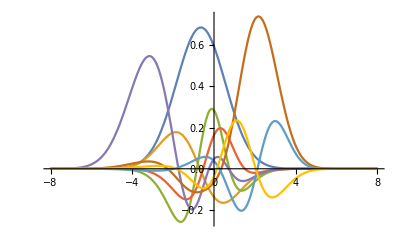

```mathematica
BlockRandom@Plot[
orthoBasis[
RandomReal[{-3, 3}, {8, 1}], 
RandomReal[{.2, 1}, {8, 1}]
]//Evaluate,
{x, -8, 8},
PlotRange->All
]
```

## Interpolations

The simplest treatment for the interpolation of the potential is the inverse-distance weighted interpolation, given by

V(x) = (∑_i V(ξ^(i))|x-ξ^(i)|^-p)/(∑_i |x-ξ^(i)|^-p)

We will take advantage of the fact, however, that at every point we have a local quadratic expansion, i.e. we can write

V(x; ξ^(i)) = V(ξ^(i)) + ∇_x V(ξ^(i))⊙(x-ξ^(i)) + 1/2∇_x V(ξ^(i))⊙(x-ξ^(i))^2

where ⊙ is a total contraction and (x-ξ^(i))^2 is the outer product of (x-ξ^(i)) with itself.

Now we can do an inverse distance weighting of these Taylor series to give

V(x) = (∑_i V(x; ξ^(i))|x-ξ^(i)|^-p)/(∑_i |x-ξ^(i)|^-p)

### Derivatives

Unfortunately, derivatives of this interpolation are formally quite messy as we have

∇_x V(x) =∑_i ( ∇_x V(x; ξ^(i))w^(i) + V(x; ξ^(i))∇_x w^(i))

where

∇_x w^(i) = (∇_x |x-ξ^(i)|^-p)/(∑_j |x-ξ^(j)|^-p) + |x-ξ^(i)|^-p∇_x (∑_j |x-ξ^(j)|^-p)^-1

For later convenience, we will write

d(x, ξ^(i), m) = ((x-ξ^(i))·(x-ξ^(i)))^-m
= |(x-ξ^(i))|^(-2m)

and so we have

∇_x |x-ξ^(i)|^-p = ∇_x d(x, ξ^(i), p/2)
= p (x-ξ^(i))d(x, ξ^(i), p/2+1)

which is becomes poorly behaved when distances are small

Then we also have

∇_x (∑_j |x-ξ^(j)|^-p )^-1 = -(∑_j |x-ξ^(j)|^-p)^-2∑_j ∇_x |x-ξ^(j)|^-p
= -(∑_j |x-ξ^(j)|^-p)^-2∑_j p (x-ξ^(j)) d(x, ξ^(j), p/2+1)

giving us

∇_x w^(i) = (x-ξ^(i))(p d(x, ξ^(i), p/2+1))/(∑_j |x-ξ^(i)|^-p) - (|x-ξ^(i)|^-p)/((∑_j |x-ξ^(i)|^-p)^2)∑_j p (x-ξ^(j)) d(x, ξ^(j), p/2+1) 
= 1/(∑_j |x-ξ^(i)|^-p)((x-ξ^(i))p d(x, ξ^(i), p/2+1) - w^(i)∑_j p (x-ξ^(j)) d(x, ξ^(j), p/2+1) )
= ∑_k (x-ξ^(j)) (δ_ki-w^(i))p (d(x, ξ^(j), p/2+1))/(∑_j d(x, ξ^(j), p/2))

then biting the bullet and doing this one more time we have

∇_(x^2) w^(i) = ∇_x (∑_j (x-ξ^(j)) (δ_ji-w^(i))p (d(x, ξ^(j), p/2+1))/(∑_k d(x, ξ^(k), p/2)))

which has three terms, the first two of which are simple

(∇_x (x-ξ^(j)))... = I...
(x-ξ^(j))∇_x (δ_ji-w^(i))... = -(x-ξ^(j))⊗∇_x w^(i)

and the last of which is a bit nastier, but is really just a redo of the previous stuff

∇_x (d(x, ξ^(j), p/2+1))/(∑_j d(x, ξ^(j), p/2))=∑_k (x-ξ^(k))(p+2)(δ_kj-(d(x, ξ^(j), p/2+1))/(∑_j d(x, ξ^(j), p/2)))(d(x, ξ^(j), p/2+2))/(∑_j d(x, ξ^(j), p/2))

Now we can generalize fully, letting

Γ^(i)(p,n) = (d(x, ξ^(j), p/2+n))/(∑_j d(x, ξ^(j), p/2))
=((|x-ξ^(i)|)^(-(p+2n)))/(∑_j (|x-ξ^(i)|)^-p)

We have

V(x) = ∑_i V(x; ξ^(i))Γ^(i)(p,n)
∇_x Γ^(i)(p,n) =∑_j (x-ξ^(j))(p+n+1)(δ_ij-Γ^(i)(p,n))Γ^(j)(p,n+1)

which gives a generic way to build the derivatives if we wanted, for now, we’ll just write

∇_x V(x) =∑_i ∇_x V(x; ξ^(i))w^(i) + V(x; ξ^(i))∇_x w^(i)
∇_(x^2) V(x) = ∑_i ∇_(x^2) V(x; ξ^(i))w^(i) + (∇_x V(x; ξ^(i))⊗∇_x w^(i))^T + (∇_x V(x; ξ^(i))⊗∇_x w^(i))
               + V(x; ξ^(i))∇_(x^2) w^(i)

where

∇_x w^(i) = (p+1)∑_j (x-ξ^(j))(δ_ij-w^(i))Γ^(i)(p,1)
∇_(x^2) w^(i) = (p+1)∑_j I(δ_ij-w^(i))Γ^(i)(p,1) - (x-ξ^(j))⊗(∇_x w^(i))Γ^(i)(p,1)
               + (p+2)(δ_ij-w^(i)) ∑_k (x-ξ^(j))⊗(x-ξ^(k))(δ_jk-Γ^(j)(p,1))Γ^(j)(p,2)

Shifting to a full tensor algebra form, letting Γ(p,n) = {Γ^(i)(p,n)}_i, Δ={(x-ξ^(i))} we have

∇_x Γ(p,n) = (p+n+1)(diag(Γ(p,n)) - Γ(p,n)⊗Γ(p,n+1))Δ)

and then we’ll note that

∇_x diag(Γ(p,n)) = diag(∇_x Γ(p,n))

and so quite simply we have (roughly...I didn’t bother to get everything clean)

∇_(x^2) Γ(p,n) = (p+n+1)(diag(∇_x Γ(p,n)) - ∇_x (Γ(p,n)⊗Γ(p,n+1)))Δ
+ (diag(Γ(p,n)) - Γ(p,n)⊗Γ(p,n+1))⊗diag(I...))

∇_x (AB) = ∇_x A B + A∇_x B^(n->1)
∇_x () =

∇_Q (A⟨α, β⟩B) = ∇_Q A⟨α+1, β⟩B + (A⟨α, β+1⟩ ∇_Q B)^(n→1)

```mathematica
Grad[ConstantArray[{x, y, z}, 15], {x, y, z}]//Transpose[#,
{2, 3, 1}
]&//Dimensions
```

{3,15,3}

```mathematica
Clear[DM, prod, transp, rank];
prod[A_, B_]:=prod[A, B, rank[A], 1];
DM[prod[A_, B_, n_, m_]]:=
transp[prod[DM[A], B, n+1, m], 1, 1]+
transp[prod[A, DM[B], n, m+1], rank[A], 1];
DM[DM[x_, k_]]:=DM[x, k+1];
DM[transp[A_, n_, k_]]:=transp[DM[A], n+1, k+1];
DM[HoldPattern[Plus][x___]]:=Plus@@Map[DM, {x}];
prod[HoldPattern[Plus][x___], B_, n_, k_]:=
Plus@@Map[prod[#, B, n, k]&, {x}];
prod[A_, HoldPattern[Plus][x___], n_, k_]:=
Plus@@Map[prod[A, #, n, k]&, {x}];
transp[HoldPattern[Plus][x___], n_, k_]:=
Plus@@Map[transp[#, n, k]&, {x}];
transp[A_, {n1_, k1_, r__}]:=
Fold[transp[#, #2[[1]], #2[[2]]]&, A, Partition[{n1, k1, r}, 2]];
DMSimp[expr_]:=expr//.{
DM[s_Symbol]:>DM[s, 1],
DM[DM[s_, k_]]:>DM[s, k+1],
rank[DM[x_, k_]]:>rank[x]+k
};
DMFormat[expr_]:=
Interpretation[
Style[
expr//.{
DM[A_]:>Row@{Subscript["∇", "x"], A},
DM[A_, k_]:>Row@{Subscript["∇", Superscript["x", k]], A},
transp[x_, a_, b_]:>Superscript[Row@{"(", x, ")"}, Row@{a, "→", b}],
prod[A_, B_, n_, k_]:>Row@{A, "⟨", n,",", k, "⟩", B},
rank[A_]:>Subscript["n", A]
},
18,
ShowStringCharacters->False
],
expr
]
```

```mathematica
Ordering[#, -1]&/@Permutations[{1, 0, 0, 0}]
```

```mathematica
Ordering[#, -2]&/@Permutations[{1, 1, 0, 0, 0}]
```

{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}

```mathematica
Ordering[#, -1]&/@Permutations[{1, 0, 0, 0, 0}]
```

{{1},{2},{3},{4},{5}}

```mathematica
DM[prod[A, B, 1, 2]]//DMSimp//Apply[List]//Map[DMFormat]//Column
```

(A⟨1,3⟩∇_(x^1) B)^(n_A→1)
(∇_(x^1) A⟨2,2⟩B)^(1→1)

```mathematica
DM[DM[prod[A, B, a, b]]]//DMSimp//Apply[List]//Map[DMFormat]//Column
```

((A⟨a,2+b⟩∇_(x^2) B)^(n_A→1))^(1+n_A→2)
((∇_(x^1) A⟨1+a,1+b⟩∇_(x^1) B)^(1→1))^(1+n_A→2)
((∇_(x^1) A⟨1+a,1+b⟩∇_(x^1) B)^(1+n_A→1))^(2→2)
((∇_(x^2) A⟨2+a,b⟩B)^(1→1))^(2→2)

```mathematica
DM[DM[DM[prod[A, B, a, b]]]]//DMSimp//Apply[List]//Map[DMFormat]//Column
```

(((A⟨a,3+b⟩∇_(x^3) B)^(n_A→1))^(1+n_A→2))^(2+n_A→3)
(((∇_(x^1) A⟨1+a,2+b⟩∇_(x^2) B)^(1→1))^(1+n_A→2))^(2+n_A→3)
(((∇_(x^1) A⟨1+a,2+b⟩∇_(x^2) B)^(1+n_A→1))^(2→2))^(2+n_A→3)
(((∇_(x^1) A⟨1+a,2+b⟩∇_(x^2) B)^(1+n_A→1))^(2+n_A→2))^(3→3)
(((∇_(x^2) A⟨2+a,1+b⟩∇_(x^1) B)^(1→1))^(2→2))^(2+n_A→3)
(((∇_(x^2) A⟨2+a,1+b⟩∇_(x^1) B)^(1→1))^(2+n_A→2))^(3→3)
(((∇_(x^2) A⟨2+a,1+b⟩∇_(x^1) B)^(2+n_A→1))^(2→2))^(3→3)
(((∇_(x^3) A⟨3+a,b⟩B)^(1→1))^(2→2))^(3→3)

```mathematica
matDerivPerms[A_, B_, a_, b_, o_, s_]:=
With[
{
base=prod[If[s==0, A, DM[A, s]], If[s==o, B, DM[B, o-s]], a+s, b+(o-s)],
nAPos=
Ordering[#, -(o-s)]&/@
Permutations@Join[ConstantArray[1, o-s], ConstantArray[0, s]],
nAs = rank[A]+Range[(o-s)]
},
transp[
base,
Flatten@Transpose[{
ReplacePart[Range[o], Thread[#->nAs]],
Range[o]
}]
]&/@nAPos
];
matProdDeriv[prod[A_, B_, a_, b_], o_]:=
Table[
matDerivPerms[A, B, a, b, o, s],
{s, 0, o}
]
```

```mathematica
Binomial[6, 2]
```

15

```mathematica
matProdDeriv[prod[A, B, a, b], 4]//Flatten//Map[DMFormat]//Column
```

((((A⟨a,4+b⟩∇_(x^4) B)^(1+n_A→1))^(2+n_A→2))^(3+n_A→3))^(4+n_A→4)
((((∇_(x^1) A⟨1+a,3+b⟩∇_(x^3) B)^(1+n_A→1))^(2+n_A→2))^(3+n_A→3))^(4→4)
((((∇_(x^1) A⟨1+a,3+b⟩∇_(x^3) B)^(1+n_A→1))^(2+n_A→2))^(3→3))^(3+n_A→4)
((((∇_(x^1) A⟨1+a,3+b⟩∇_(x^3) B)^(1+n_A→1))^(2→2))^(2+n_A→3))^(3+n_A→4)
((((∇_(x^1) A⟨1+a,3+b⟩∇_(x^3) B)^(1→1))^(1+n_A→2))^(2+n_A→3))^(3+n_A→4)
((((∇_(x^2) A⟨2+a,2+b⟩∇_(x^2) B)^(1+n_A→1))^(2+n_A→2))^(3→3))^(4→4)
((((∇_(x^2) A⟨2+a,2+b⟩∇_(x^2) B)^(1+n_A→1))^(2→2))^(2+n_A→3))^(4→4)
((((∇_(x^2) A⟨2+a,2+b⟩∇_(x^2) B)^(1+n_A→1))^(2→2))^(3→3))^(2+n_A→4)
((((∇_(x^2) A⟨2+a,2+b⟩∇_(x^2) B)^(1→1))^(1+n_A→2))^(2+n_A→3))^(4→4)
((((∇_(x^2) A⟨2+a,2+b⟩∇_(x^2) B)^(1→1))^(1+n_A→2))^(3→3))^(2+n_A→4)
((((∇_(x^2) A⟨2+a,2+b⟩∇_(x^2) B)^(1→1))^(2→2))^(1+n_A→3))^(2+n_A→4)
((((∇_(x^3) A⟨3+a,1+b⟩∇_(x^1) B)^(1+n_A→1))^(2→2))^(3→3))^(4→4)
((((∇_(x^3) A⟨3+a,1+b⟩∇_(x^1) B)^(1→1))^(1+n_A→2))^(3→3))^(4→4)
((((∇_(x^3) A⟨3+a,1+b⟩∇_(x^1) B)^(1→1))^(2→2))^(1+n_A→3))^(4→4)
((((∇_(x^3) A⟨3+a,1+b⟩∇_(x^1) B)^(1→1))^(2→2))^(3→3))^(1+n_A→4)
((((∇_(x^4) A⟨4+a,b⟩B)^(1→1))^(2→2))^(3→3))^(4→4)

```mathematica
Nest[DM, prod[A, B, a, b], 3]//DMSimp//Apply[List]//Map[DMFormat]//Column
```

(((A⟨a,3+b⟩∇_(x^3) B)^(n_A→1))^(1+n_A→2))^(2+n_A→3)
(((∇_(x^1) A⟨1+a,2+b⟩∇_(x^2) B)^(1→1))^(1+n_A→2))^(2+n_A→3)
(((∇_(x^1) A⟨1+a,2+b⟩∇_(x^2) B)^(1+n_A→1))^(2→2))^(2+n_A→3)
(((∇_(x^1) A⟨1+a,2+b⟩∇_(x^2) B)^(1+n_A→1))^(2+n_A→2))^(3→3)
(((∇_(x^2) A⟨2+a,1+b⟩∇_(x^1) B)^(1→1))^(2→2))^(2+n_A→3)
(((∇_(x^2) A⟨2+a,1+b⟩∇_(x^1) B)^(1→1))^(2+n_A→2))^(3→3)
(((∇_(x^2) A⟨2+a,1+b⟩∇_(x^1) B)^(2+n_A→1))^(2→2))^(3→3)
(((∇_(x^3) A⟨3+a,b⟩B)^(1→1))^(2→2))^(3→3)

and so

∇_x V(x) = ∇_x V(x; ξ^(.))⊙w^(.) + ∇_x w^(.)⊙V(x; ξ^(.))
∇_x V(x) = ∇_x V(x; ξ^(.))⊙w^(.)

### GPR Potentials

## Coordinate Decompositions

Can we find a basis for the space of Cartesian displacement coordinates that lead to a change in an internal coordinate τ that lead to the minimum possible change in some alternate space of coordinates Q?

I can find B_τ and C_Q where B_τ is the basis for τ and C_Q is the complement to the B_Q, the basis for Q, then in principle I can then use least squares to find a way to best describe B_τ in C_Q if I need it to be the case that Q not change or I can use least squares to describe C_Q in B_τ

Generally, B_τ is likely a lower-dimensional space than C_Q, and so there is no pseudoinverse-based transformation that maps it cleanly onto all of C_Q...

#### Maximally Linearized Modes

For ease of use, we would like to be able to decompose our normal modes into versions of themselves that look the most like a local stretch or bend to be able to fit potential contributions. As we can do this via a sequence of linear transformations, we can quickly get a “linearized” internal coordinate representation

Letting Q_r(q) be the linear transformation that takes L to ∇_X r, we can then write

r̃(q) = Q_r(q)q

and then we just have linear transformations so, e.g.,

∇_r V(q) = Q_r(q)∇_q V

and then we’ll write a 1D potential contribution as

Ṽ(q) = (Ṽ)_r_1(q) + (Ṽ)_r_2(q) + ...

where we do a global fit to a potential of this form

#### Multiple Interpolant Form

Alternately, to avoid imposing any type of model, we can try to build 1D potentials by minimizing in all coordinates except for a given one by assuming a quadratic expansion, that means given a local quadratic expansion

V(q; ξ) ≃ 1/2(q-ξ)^T F(q-ξ) + (q-ξ)^T f + V_0

we simply fix the select coordinate, r, and find minimizing position by noting that with a quadratic form like this—letting F_(/r) and f_(/r) be the submatrices/vectors where the r coordinate is dropped—we can complete the square to get a minimum energy contribution from

V_(0/r) = -1/2 ((f_(/r))^T(F_(/r)))^-1 f_(/r)

#### Exploration

```mathematica
woof1=stretchModes[ochhModes, 1, 2].SingularValueDecomposition[
{distVector[ochhCoords, 1, 2].stretchModes[ochhModes, 1, 2]}
][[3]];
```

```mathematica
woof2=ochhModes.SingularValueDecomposition[
{distVector[ochhCoords, 1, 2].ochhModes}
][[3]];
```

```mathematica
animateOCHH[woof1[[;;, 1]]]
```

```mathematica
distVector[coords_, i_, j_]:=
With[{n=Norm[coords[[i]]-coords[[j]]]},
Flatten@ReplacePart[
ConstantArray[0, Dimensions[coords]],
{
i->coords[[i]]-coords[[j]],
j->-(coords[[i]]-coords[[j]])
}
]
]
```

```mathematica
ochhStretchModes//Dimensions
```

{12,6}

```mathematica
{
distVector[ochhCoords, 1, 2],
distVector[ochhCoords, 2, 3],
distVector[ochhCoords, 2, 4]
}.ochhModes//Dimensions
```

{3,6}

```mathematica
ochhStretchModes[[2]]//Dimensions
```

{3,6}

```mathematica
"{
distVector[ochhCoords, 1, 2],
distVector[ochhCoords, 2, 3],
distVector[ochhCoords, 2, 4]
}"
```

```mathematica
SingularValueDecomposition[
{
distVector[ochhCoords, 1, 2],
distVector[ochhCoords, 2, 3],
distVector[ochhCoords, 2, 4]
}.ochhModes
][[1]]
```

{{-4.73238×10^-14,0.0783014,0.99693},{0.707107,-0.704936,0.0553674},{-0.707107,-0.704936,0.0553674}}

```mathematica
ochhStretchModes=
With[{svdDat=SingularValueDecomposition[
{
distVector[ochhCoords, 1, 2],
distVector[ochhCoords, 2, 3],
distVector[ochhCoords, 2, 4]
}.ochhModes
]},
ochhModes.svdDat[[3]][[;;, 
Pick[Range[Length[svdDat[[2]]]], UnitStep[Diagonal[svdDat[[2]]]-1*^-8], 1]
]]
];
```

```mathematica
ochhLocStretchModes=
Block[{looook=ochhStretchModes},
Do[
looook=looook.QRDecomposition[
Dot[
Orthogonalize@{
distVector[ochhCoords, 1, 2],
distVector[ochhCoords, 2, 3],
distVector[ochhCoords, 2, 4]
},
Transpose[Map[Normalize, Transpose@looook]]
]
][[1]],
{10}
];
looook
];
```

```mathematica
Dot[
Normalize/@{
distVector[ochhCoords, 1, 2],
distVector[ochhCoords, 2, 3],
distVector[ochhCoords, 2, 4]
},
Transpose[Map[Normalize, Transpose@ochhLocStretchModes]]
]//MatrixForm
```

(-0.480641 | 0.0335954 | -0.133409
0.0946171 | -0.759782 | -0.121597
0.803274 | 0.147962 | -0.673964)

```mathematica
QRDecomposition[distBasis][[1]]//Dimensions
```

{3,12}

```mathematica
QRDecomposition[distBasis][[1]]//MatrixForm
```

```mathematica
#.Transpose[#]&@QRDecomposition[distBasis][[1]]
```

{{1.,0.,0.},{0.,1.,-2.08167×10^-17},{0.,-2.08167×10^-17,1.}}

```mathematica
animateOCHH[Transpose[QRDecomposition[distBasis][[1]]][[;;, 3]]/100]
```

```mathematica
distBasis=Transpose[
Map[Normalize,
{
distVector[ochhCoords, 1, 2],
distVector[ochhCoords, 2, 3],
distVector[ochhCoords, 2, 4]
}
]
];
distSMat=Transpose[distBasis].distBasis;
```

```mathematica
orthoBasis=distBasis.simpleOrtho[distSMat, 3];
```

```mathematica
Transpose[orthoBasis].orthoBasis
```

{{0.82953,-0.0595266,0.0582387},{-0.0595266,1.03204,0.121583},{0.0582387,0.121583,1.19241}}

```mathematica
diagonalBasis=distBasis.QRDecomposition[distSMat][[1]];
```

```mathematica
Transpose[diagonalBasis].diagonalBasis//Ma
```

```mathematica
#.Transpose[#]&@Map[Normalize,
{
distVector[ochhCoords, 1, 2],
distVector[ochhCoords, 2, 3],
distVector[ochhCoords, 2, 4]
}
]
```

{{1.,-0.262315,-0.262315},{-0.262315,1.,-0.224763},{-0.262315,-0.224763,1.}}

```mathematica
animateOCHH[ochhLocStretchModes[[;;, 1]]]
```

#### Code

Data

```mathematica
h2oCoords=ImportString["[[-5.91645679e-31,  0.00000000e+00,  2.25076607e-01],
               [-3.15544362e-30,  1.43714391e+00, -9.00306427e-01],
               [-1.75999369e-16, -1.43714391e+00, -9.00306427e-01]]","JSON"];
```

```mathematica
h2o2DStretchCoords=ImportString[#, "JSON"]&@ "[[-4.19488113e-17,  1.25947101e-01,  9.84847362e-18],
               [ 1.43714391e+00, -9.99435933e-01,  9.84847362e-18],
               [-1.43714391e+00, -9.99435933e-01, -1.66150895e-16]]";
```

```mathematica
h2o2DStretchModes=ImportString[#, "JSON"]&@ "[[ 5.49053676e-15, -1.57640898e-03],
       [-1.25210802e-03, -3.73273159e-15],
       [ 3.46270935e-16,  5.69066255e-17],
       [-1.26884474e-02,  1.25093772e-02],
       [ 9.93593149e-03, -9.79570716e-03],
       [ 7.32862332e-15,  2.70944833e-15],
       [ 1.26884474e-02,  1.25093772e-02],
       [ 9.93593149e-03,  9.79570716e-03],
       [ 3.66431166e-15,  2.70944833e-15]]";
```

```mathematica
hod2DStretchModes=ImportString[#, "JSON"]&@
StringReplace[n:(NumberString|"]")~~w:(" "|"\n"):>n<>","<>w]@"[[1.85026704e-03 -7.56042865e-04]
 [ 6.02583794e-04  1.21924940e-03]
 [-3.39700795e-16 -1.94681800e-16]
 [ 4.45716635e-04  1.14177488e-02]
 [-7.62082392e-04 -1.95219667e-02]
 [-8.07632729e-15 -3.05887902e-15]
 [-1.49168568e-02  2.90823443e-04]
 [-4.40406276e-03  8.58629076e-05]
 [-2.66488179e-15 -2.69925673e-16]]";
```

```mathematica
hod2DStretchCoords=ImportString[#, "JSON"]&@
"[[ 1.36574181e-01,  1.38244533e-01,  3.08148791e-33],
               [ 1.05811267e+00, -1.43739388e+00,  3.08148791e-33],
               [-1.61406182e+00, -3.78614411e-01, -4.62223187e-32]]";
```

```mathematica
h2o2DCoords=ImportString[#, "JSON"]&@ "[[-0.        ,  0.1259471 ,  0.        ],
       [ 1.43714391, -0.99943593,  0.        ],
       [-1.43714391, -0.99943593, -0.        ]]";
```

```mathematica
h2o2DModes=ImportString[#, "JSON"]&@"[[ 5.79634183e-16,  4.60385932e-15],
       [ 1.49109275e-03, -1.27082773e-03],
       [ 3.76255423e-16,  1.68515388e-16],
       [-1.07010445e-02, -1.25557929e-02],
       [-1.18323619e-02,  1.00844790e-02],
       [ 2.03664289e-15,  5.47145769e-15],
       [ 1.07010445e-02,  1.25557929e-02],
       [-1.18323619e-02,  1.00844790e-02],
       [ 2.03663065e-15,  5.47146088e-15]]";
```

```mathematica
(*animateModes[
{"O", "H", "H"}, 
{{1, 2}, {1, 3}},
h2o2DCoords
][h2o2DModes[[;;, 1]], ViewPoint->Top]*)
```

```mathematica
h2o3DModes=ImportString[#, "JSON"]&@"[[ 6.15523240e-16,  5.71429890e-15, -1.57640898e-03],
       [ 1.49109274e-03, -1.27082773e-03, -3.97850281e-15],
       [ 2.67476728e-17,  3.44131498e-16,  5.69066255e-17],
       [-1.07010446e-02, -1.25557930e-02,  1.25093772e-02],
       [-1.18323619e-02,  1.00844791e-02, -9.79570716e-03],
       [ 6.29302910e-15,  7.25060202e-15,  2.70944833e-15],
       [ 1.07010446e-02,  1.25557930e-02,  1.25093772e-02],
       [-1.18323619e-02,  1.00844791e-02,  9.79570716e-03],
       [ 6.03605121e-15,  3.58921398e-15,  2.70944833e-15]]";
```

```mathematica
h2oModes=ImportString["[[ 1.24135596e-19,  8.97777247e-20, -9.65272103e-20],
       [-2.47822069e-15, -2.72182340e-13, -1.57640898e-03],
       [ 1.58750676e-03,  1.14812149e-03, -2.00730152e-13],
       [-1.57704257e-18,  1.06113682e-19, -1.58632041e-29],
       [-9.66779280e-03,  1.33676502e-02,  1.25093772e-02],
       [-1.25974421e-02, -9.11076056e-03, -9.79570712e-03],
       [-3.93079415e-19, -1.53095132e-18,  1.53195687e-18],
       [ 9.66779280e-03, -1.33676502e-02,  1.25093772e-02],
       [-1.25974421e-02, -9.11076054e-03,  9.79570712e-03]]","JSON"];
```

```mathematica
ochhCoords=ImportString["[[-3.94430453e-31, -7.88860905e-31,  1.29398370e+00],
               [ 1.97215226e-31,  0.00000000e+00, -1.01849646e+00],
               [ 0.00000000e+00,  1.78816067e+00, -2.12044542e+00],
               [-2.18986524e-16, -1.78816067e+00, -2.12044542e+00]]", "JSON"];
```

```mathematica
ochhMasses={15.9949146,12.,1.00782504,1.00782504};
```

```mathematica
ch4Coords=ImportString["[[-6.76267799e-25,  1.37973726e-20,  4.38012420e-08],
               [ 6.99117674e-17,  1.95654889e+00, -6.91744453e-01],
               [-3.20361735e-17, -4.44089210e-16,  2.07523310e+00],
               [ 1.69442104e+00, -9.78274445e-01, -6.91744453e-01],
               [-1.69442104e+00, -9.78274445e-01, -6.91744453e-01]]", "JSON"];
```

```mathematica
ch4Modes=ImportString["[[ 4.26420604e-04,  1.07405936e-09, -2.41978457e-03, -5.25190808e-09,  1.70604641e-04, -2.09971305e-03, -2.36733024e-03,  2.73696292e-05, -3.82624604e-10],
       [-2.25934795e-03,  1.91906097e-03, -1.31057337e-04, -2.44820225e-04, -1.05437139e-03, -1.55416485e-03,  8.79438703e-04, -1.31518373e-03, -1.19165646e-03],
       [-1.59759754e-03, -2.71396378e-03, -9.26740720e-05,  3.46227694e-04, -7.45555137e-04, -1.09896074e-03,  6.21857266e-04, -9.29934441e-04,  1.68530192e-03],
       [-1.82497929e-03,  2.68915796e-03,  1.39683939e-02,  1.36280428e-02, -5.34235235e-04,  2.55523193e-04, -1.33775339e-04,  3.90761942e-06, -4.68226862e-06],
       [-9.11575296e-04,  5.29054323e-03,  2.68858143e-04, -6.37599695e-04,  4.84048353e-03, -1.50374679e-03,  1.28200784e-03,  1.49868141e-02,  1.48847492e-02],
       [ 1.52411384e-03,  8.07866825e-03,  8.77534601e-04, -1.03061434e-03,  1.50783802e-02,  7.84331611e-04, -3.91466247e-04, -5.59285185e-03, -5.01651528e-03],
       [-1.82497918e-03, -2.68916927e-03,  1.39684540e-02, -1.36279804e-02, -5.34232713e-04,  2.55521594e-04, -1.33776516e-04,  3.90779262e-06,  4.68215811e-06],
       [ 1.13310243e-03, -9.38016960e-03,  9.16955382e-04,  1.18421556e-03,  1.58295206e-02,  2.38225328e-04,  5.82582753e-05, -2.77394648e-04, -2.31959304e-04],
       [-1.36747681e-03, -2.29508451e-03, -3.90324880e-05,  2.57596865e-04, -4.62478609e-04, -1.67918916e-03,  1.33917569e-03,  1.59934782e-02, -1.57061668e-02],
       [ 7.81240645e-03,  5.18707211e-09,  1.40673154e-03,  1.78003220e-09, -7.70293684e-04, -2.32799166e-03,  1.22691503e-02, -6.97653494e-04,  1.04887739e-08],
       [ 6.35411155e-03, -3.91679131e-03,  4.00275698e-03,  4.52966060e-03, -2.04575648e-03,  1.48276662e-03, -7.10409039e-03,  2.87076096e-04, -1.17427685e-04],
       [ 4.49302899e-03,  5.53918704e-03,  2.83040036e-03, -6.40588989e-03, -1.44656197e-03,  1.04847422e-03, -5.02335097e-03,  2.02997750e-04,  1.66058798e-04],
       [-5.69404140e-03, -3.96038065e-09, -6.46985593e-04, -1.14053177e-09,  1.92643715e-04,  9.73801231e-03,  1.31506167e-03,  3.54381819e-04, -5.44506659e-09],
       [ 4.67203485e-03, -3.65321864e-03, -2.54782458e-03, -2.23346747e-03, -1.34577682e-03,  5.61627410e-03,  7.97182914e-04,  1.25821270e-04, -7.66100444e-05],
       [ 3.30362306e-03,  5.16644024e-03, -1.80159157e-03,  3.15858509e-03, -9.51604780e-04,  3.97130611e-03,  5.63693600e-04,  8.89718707e-05,  1.08338891e-04]]", "JSON"];
```

```mathematica
nh3Modes=ImportString["[[-6.18866021e-14, -5.00988451e-05, -1.52222430e-03,  1.91227992e-13,  6.89656503e-13,  1.77709605e-03],
       [ 2.02893398e-11,  1.52222430e-03, -5.00988451e-05, -3.55411060e-12, -1.77709605e-03,  1.72150641e-12],
       [-2.48915341e-03,  3.35287045e-11, -9.07157371e-13,  8.72183011e-04, -1.41774029e-12, -1.23673082e-14],
       [ 1.27217168e-12,  5.68457146e-04,  1.72722401e-02, -2.49657246e-13, -3.38731304e-13,  5.35024914e-04],
       [ 4.45426693e-03,  3.17202839e-03, -1.04396545e-04,  1.27121870e-02,  1.69960881e-02, -1.79073617e-11],
       [ 1.15283898e-02,  5.71244422e-03, -1.88005709e-04, -4.03947208e-03, -6.66890041e-03,  6.48190159e-12],
       [-3.85750818e-03,  8.91644485e-03,  1.64768453e-03, -1.10090769e-02,  7.59119462e-03, -1.26133099e-02],
       [-2.22713360e-03, -1.24525272e-02, -8.45238423e-03, -6.35609349e-03,  3.84775334e-03, -7.59119461e-03],
       [ 1.15283896e-02, -2.69340461e-03,  5.04112480e-03, -4.03947208e-03,  3.33445021e-03, -5.77543717e-03],
       [ 3.85750818e-03, -8.78881111e-03,  2.23039292e-03,  1.10090769e-02, -7.59119461e-03, -1.26133099e-02],
       [-2.22713360e-03, -1.18698188e-02,  9.25287167e-03, -6.35609349e-03,  3.84775334e-03,  7.59119461e-03],
       [ 1.15283896e-02, -3.01904006e-03, -4.85311910e-03, -4.03947205e-03,  3.33445023e-03,  5.77543719e-03]]", "JSON"];
```

```mathematica
ochhModes=ImportString["[[ 8.38824772e-04,  3.71354294e-19, -5.21494735e-19,  3.62953348e-19,  4.03489229e-19, -2.65545493e-19],
       [ 8.40134841e-19, -1.58940025e-03,  6.00164172e-16, -1.92461086e-16, -1.01555097e-16,  1.23176664e-05],
       [ 3.12686407e-21,  4.09586412e-16,  2.16601823e-03,  3.36539644e-03,  7.56834834e-06, -4.01523727e-17],
       [-3.46440414e-03, -1.75428604e-18,  2.37792828e-18, -1.55291241e-18, -1.53381986e-18,  9.62037470e-19],
       [-2.15654927e-18,  2.96219691e-03, -8.81134854e-16,  1.97150562e-16, -7.82086062e-15, -2.25042488e-03],
       [ 1.26218673e-18,  2.51129333e-16, -6.31554116e-04, -5.02812291e-03,  1.32459506e-03, -4.46642780e-15],
       [ 1.39686543e-02,  7.80471331e-18, -1.04611057e-17,  6.64786423e-18,  6.79250072e-18, -4.43459590e-18],
       [-7.09877205e-18, -5.02271790e-03, -7.22760867e-03,  4.62010387e-03,  1.40917211e-02,  1.32999666e-02],
       [-2.72105784e-18, -1.32154245e-02, -1.34282372e-02,  3.22885718e-03, -7.94592078e-03, -8.06966113e-03],
       [ 1.39686543e-02,  7.18960776e-18, -9.57597894e-18,  6.08206469e-18,  5.06676262e-18, -2.80581976e-18],
       [ 1.94428850e-17, -5.02271790e-03,  7.22760867e-03, -4.62010387e-03, -1.40917211e-02,  1.32999666e-02],
       [-1.23572088e-17,  1.32154245e-02, -1.34282372e-02,  3.22885718e-03, -7.94592078e-03,  8.06966113e-03]]", "JSON"];
```

```mathematica
ochhModesBigInv=ImportString["[[ 1.13424278e+02,  1.25274527e+02, -3.44559188e-04, -1.33729719e-05, -1.73807711e-07,  1.39947144e-09, -2.44575514e+01,  2.19879624e-14, -1.04256510e-14,  6.05200030e-15, -1.06181083e-14,  8.53976355e-15],
       [ 2.88220077e-07, -1.30875057e-05,  8.34057080e-03, -1.21804643e+02,  1.10330698e+02, -2.37823241e-08, -1.89575078e-14,  4.63420177e+01,  1.23336996e-12,  2.59942520e-12, -1.84753865e-13, -3.59147819e-01],
       [ 2.13030567e-07, -3.43061004e-04, -1.24659360e+02, -8.54707868e-03, -1.21784414e-05, -7.08707441e-09,  2.09252204e-15,  1.16569637e-12, -6.31544750e+01, -9.81246820e+01, -2.20669903e-01,  2.29483525e-13],
       [-8.64397153e+01,  9.30581883e+01, -2.56242005e-04, -1.00105246e-05,  2.32229594e-07,  2.69937639e-09,  7.57826566e+01,  1.64202931e-14, -4.72613087e-14, -1.44001175e-14,  3.59384775e-14, -2.21289106e-14],
       [-1.22580261e-07, -1.01856970e-05,  6.56296984e-03, -9.56096913e+01, -7.81758813e+01, -2.11823593e-08,  4.50250694e-14, -6.47970269e+01, -7.76401070e-13, -7.96903156e-13, -2.05894264e-13,  4.92272852e+01],
       [ 1.59823703e-07, -2.57377557e-04, -9.35242453e+01, -6.41234709e-03, -9.13673737e-06, -5.31691025e-09, -2.68277314e-14, -1.65756493e-12,  1.38150315e+01,  1.09988489e+02, -2.89750691e+01, -2.16350544e-13],
       [-1.41246625e+01,  7.77840848e+00, -2.14284406e-05, -8.33505235e-07,  3.44790832e-08, -3.03080242e+01, -2.56625525e+01, -3.09311601e-14, -5.90082907e-16,  1.52069823e-15, -3.01743067e-14, -1.41272126e-15],
       [-2.38546019e-08, -8.70135627e-07,  5.63412639e-04, -8.19899507e+00, -1.30070081e+01, -1.91267618e-09,  1.39301116e-14,  9.22750437e+00,  1.32782206e+01, -8.48783600e+00, -2.58886428e+01, -2.44340687e+01],
       [-8.58072091e-09, -2.16397929e-05, -7.85465317e+00, -2.75063078e-01, -1.04525809e+01, -6.63504491e-10,  6.77105545e-15,  2.42787560e+01,  2.46697217e+01, -5.93190326e+00,  1.45978695e+01,  1.48251997e+01],
       [-1.41246625e+01,  7.77840848e+00, -2.14318859e-05, -8.46178616e-07,  3.35540297e-08,  3.03080242e+01, -2.56625525e+01,  2.37932001e-15,  3.62893773e-14, -3.77380820e-14,  8.72664611e-15,  1.43874507e-14],
       [-2.38546052e-08, -8.70135574e-07,  5.63431932e-04, -8.19899507e+00, -1.30070081e+01, -1.91268132e-09, -3.37766759e-14,  9.22750437e+00, -1.32782206e+01,  8.48783600e+00,  2.58886428e+01, -2.44340687e+01],
       [ 3.54264571e-08, -2.15921316e-05, -7.85469285e+00,  2.73985990e-01,  1.04525794e+01, -2.29654870e-10,  1.92226631e-14, -2.42787560e+01,  2.46697217e+01, -5.93190326e+00,  1.45978695e+01, -1.48251997e+01]]", "JSON"];
ochhModesBig=Inverse[Transpose@ochhModesBigInv];
ochhBigTRModes=ochhModesBig[[;;, ;;6]];
ochhBigRealModes=ochhModesBig[[;;, 7;;]];
ochhModesBigUnscaled=MatrixPower[ochhModesBig.Transpose[ochhModesBig], -1/2].ochhModesBig;
ochhBigUSTRModes=ochhModesBigUnscaled[[;;, ;;6]];
ochhBigUSRealModes=ochhModesBigUnscaled[[;;, 7;;]];
```

```mathematica
(*animateModes[
{"O", "H", "H"}, 
{
{1, 2},
{1, 3}
},
h2o2DCoords
][
h2o2DModes[[;;, 2]],
ViewPoint->Top
]*)
```

animateOCHH

```mathematica
animateOCHH=animateModes[{"O", "C", "H", "H"}, {{1,2 }, {2, 3}, {2, 4}}, ochhCoords];
```

drMat

```mathematica
drMat[n_, coords:{__Integer}, sign:-1|1:-1]:=
Block[
{
m=ConstantArray[0, {3*Binomial[Length@coords, 2], 3*n}], 
offsets=3*(Sort@coords-1),
crds=Sort@coords,
d=Length@coords,
bos=Accumulate[Prepend[0]@(3*Range[Length@coords-1, 2, -1])]
},
Do[
Do[
Do[
m[[bos[[k]]+3*(j-1)+i, offsets[[k]]+i]]=1;m[[bos[[k]]+3*(j-1)+i, offsets[[k+j]]+i]]=-1,
{i, 3}
],
{j, d-k}
],
{k, d}
];
m
];
drMat[n_, x_, y_]:=
Block[{m=ConstantArray[0, {6, 3*n}], 
sx=3*(x-1), 
sy=3*(y-1)
},
Do[
m[[i, sx+i]]=1;m[[i, sy+i]]=-1;
m[[3+i, sx+i]]=1;m[[3+i, sy+i]]=1,
{i, 3}
];
m
];
coordSel[n_, m_]:=
Join[3*(n-1)+Range[3], 3*(m-1)+Range[3]];
```

getAngle

```mathematica
getAngle[coords_, i_, j_, k_]:=
With[{
a=coords[[i]]-coords[[j]]//Normalize, 
b=coords[[k]]-coords[[j]]//Normalize
},
π-Abs@ArcTan[
Norm[Cross[b, a]]/(a.b)
]
]
```

```mathematica
getAngleComps[coords_, i_, j_, k_]:=
With[{
a=coords[[i]]-coords[[j]]//Normalize, 
b=coords[[k]]-coords[[j]]//Normalize
},
{Norm[Cross[b, a]],(a.b)}
]
```

ndaMat

```mathematica
ndaMat[coords_, i_, j_, k_]:=
Block[
{
m=ConstantArray[0, {7, Times@@Dimensions[coords]}], 
si=3*(i-1), 
sj=3*(j-1),
sk=3*(k-1),
v1=Normalize[coords[[i]]-coords[[j]]],
v2=Normalize[coords[[k]]-coords[[j]]]
},
Do[
m[[x, si+x]]=1;
m[[x, sj+x]]=1;
m[[x, sk+x]]=1,
{x, 3}
];
m[[4, 1+si;;si+3]]=v1;
m[[5, 1+sj;;sj+3]]=-v1;
m[[5, 1+sk;;sk+3]]=-v1;
m[[6, 1+sk;;sk+3]]=v2;
m[[7, 1+sj;;sj+3]]=-v2;
m[[7, 1+si;;si+3]]=-v2;
Normalize/@m
]
```

```mathematica
ndaProj[coords_, i_, j_, k_]:=
ReplacePart[
ConstantArray[0, {3*Length[coords], 3*Length[coords]}],
Flatten@Table[
{3*(x-1)+y, 3*(x-1)+y}->1,
{x, {i, j, k}},
{y, 3}
]
]-(
Transpose[Orthogonalize[ndaMat[coords, i, j, k]]].Orthogonalize[ndaMat[coords, i, j, k]]
)
```

ndtMat

```mathematica
ndtMat[coords_, i_, j_, k_, l_]:=
Block[
{
m=ConstantArray[0, {7, Times@@Dimensions[coords]}], 
si=3*(i-1), 
sj=3*(j-1),
sk=3*(k-1),
sl=3*(l-1),
v1=Normalize[coords[[i]]-coords[[j]]],
v2=Normalize[coords[[k]]-coords[[j]]],
v3=Normalize[coords[[k]]-coords[[l]]]
},
(* three total displacements *)
Do[
m[[x, si+x]]=1;
m[[x, sj+x]]=1;
m[[x, sk+x]]=1;
m[[x, sl+x]]=1;,
{x, 3}
];
(* two displacements of atom i in the v1 x v2 plane*)
m[[4, 1+si;;si+3]]=v1;
m[[5, 1+si;;si+3]]=v2;
(* two displacements of atom k in the v2 x v3 plane*)
m[[6, 1+sk;;sk+3]]=v2;
m[[7, 1+sk;;sk+3]]=v3;
Normalize/@m
]
```

```mathematica
ndtProj[coords_, i_, j_, k_, l_]:=
ReplacePart[
ConstantArray[0, {3*Length[coords], 3*Length[coords]}],
Flatten@Table[
{3*(x-1)+y, 3*(x-1)+y}->1,
{x, {i, j, k, l}},
{y, 3}
]
]-(
Transpose[Orthogonalize[ndtMat[coords, i, j, k, l]]].Orthogonalize[ndtMat[coords, i, j, k, l]]
)
```

```mathematica
ndtProj[
ochhCoords,
4, 2, 1, 3
].ochhModes//Threshold//SingularValueDecomposition//#[[2]]&
```

{{0.0171761,0.,0.,0.,0.,0.},{0.,0.0165127,0.,0.,0.,0.},{0.,0.,0.0155814,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.}}

```mathematica
animateOCHH[
ochhModes.SingularValueDecomposition[
ndaProj[
ochhCoords,
4, 2, 3
].ochhModes
][[3]]
]
```

getOrthogSpaces

```mathematica
(*getOrthogSpaces1[modes_, n_, m_]:=
With[{
k=Dimensions[modes][[2]],
nullVecs=NullSpace[drMat[Length[modes]/3, n, m][[;;3]].modes]},
{
nullVecs,
Map[
Normalize,
IdentityMatrix[k][[;;(k-Length@nullVecs)]].(IdentityMatrix[k]-Transpose[nullVecs].nullVecs)
]
}
]*)
```

```mathematica
ClearAll[getDeltaProjModes];
getDeltaProjModes[modes_, n_, m_]:=
drMat[Length[modes]/3, n, m][[;;3]].modes;
getDeltaProjModes[modes_, coords:{__Integer}]:=
drMat[Length[modes]/3, coords].modes;
```

```mathematica
ClearAll[getOrthogSpaces];
getOrthogSpaces[modes_, n_, m_]:=
With[
{
d=SingularValueDecomposition[getDeltaProjModes[modes, n, m]]
},
With[{k=Length@Select[Diagonal[d[[2]]], Abs[#]>1*^-10&]},
{
Transpose[d[[3]]][[;;k]],
Transpose[d[[3]]][[k+1;;]]
}
]
];
getOrthogSpaces[coords_, modes_, i_, j_, k_]:=
With[
{
d=SingularValueDecomposition[ndaProj[coords, i, j, k].modes]
},
With[{n=Length@Select[Diagonal[d[[2]]], Abs[#]>1*^-10&]},
{
Transpose[d[[3]]][[;;n]],
Transpose[d[[3]]][[n+1;;]]
}
]
]
(*getOrthogSpaces[modes_, coords:{__Integer}]:=
With[
{
d=SingularValueDecomposition[getDeltaProjModes[modes, coords]]
},
With[{k=Length@Select[Diagonal[d[[2]]], Abs[#]>1*^-10&]},
{
Transpose[d[[3]]][[;;k]],
Transpose[d[[3]]][[k+1;;]]
}
]
];*)
```

displaceCoords

```mathematica
displaceCoords[coords_, mode_]:=
coords+ArrayReshape[mode, Dimensions[coords]];
```

testDists

```mathematica
ClearAll[testDists]
testDists[modes_, i_, j_, initCoords_:None]:=
With[{
n=Dimensions[modes][[1]]/3, 
orthoModes=modes.Transpose[Join@@getOrthogSpaces[modes, i, j] ]
},
With[{
coords=Replace[initCoords,None->ConstantArray[0, {n, 3}]
]
},
Norm[(coords[[i]]+#[[i]])-(coords[[j]]+#[[j]])]&/@(10*ArrayReshape[Transpose@orthoModes, {3*n-6, n, 3}])//Threshold
]
]
```

```mathematica
getDistProjections[modes_, i_, j_]:=
drMat[Length[modes]/3, i, j][[;;3]].modes.Transpose[Join@@getOrthogSpaces[modes, i, j] ]
```

testAngles

```mathematica
testAngles[coords_, modes_, ijk_]:=
getAngle[
coords+ArrayReshape[#, Dimensions[coords]],
Sequence@@ijk
]/Degree&/@
Prepend[
10*modes,
ConstantArray[0, Dimensions[modes][[1]]]
]
```

testDihed

```mathematica
getDihed[coords_, i_, j_, k_, l_]:=
VectorAngle[
Cross[
Normalize[coords[[i]]-coords[[j]]],
Normalize[coords[[j]]-coords[[k]]]
],
Cross[
Normalize[coords[[j]]-coords[[k]]],
Normalize[coords[[k]]-coords[[l]]]
]
]
```

```mathematica
testDihed[coords_, modes_, ijkl_]:=
getDihed[
coords+ArrayReshape[#, Dimensions[coords]],
Sequence@@ijkl
]/Degree&/@
Prepend[
10*modes,
ConstantArray[0, Dimensions[modes][[1]]]
]
```

coordVectors

```mathematica
distVector[coords_, i_, j_]:=
With[{n=Norm[coords[[i]]-coords[[j]]]},
Flatten@ReplacePart[
ConstantArray[0, Dimensions[coords]],
{
i->-(coords⟦j⟧-coords⟦i⟧)/n,
j->(coords⟦j⟧-coords⟦i⟧)/n
}
]
]
```

```mathematica
bendVector[coords_, i_, j_, k_]:=
Block[{
a,b,bh,ah,
dqda, 
dqdb,
dadx,
dbdx
},
a=coords[[i]]-coords[[j]];
b=coords[[k]]-coords[[j]];
bh=Normalize[b];
ah=Normalize[a];
dqda=-(bh-(ah.bh)*ah)/Norm[a];
dqdb=-(ah-(ah.bh)*bh)/Norm[b];
dadx=drMat[Length[coords], i, j][[;;3]];
dbdx=drMat[Length[coords], k, j][[;;3]];
Transpose[
Join[
dadx,
dbdx
]
].Join[dqda, dqdb]
]
```

stretchModes

```mathematica
stretchModes[modes_, i_, j_]:=
modes.Transpose[getOrthogSpaces[modes, i, j][[1]]];
stretchModeProj[coords_, modes_, i_, j_]:=
distVector[coords, i, j].stretchModes[modes, i, j];
localizedStretchModes[coords_, modes_, i_, j_]:=
With[{d=distVector[coords, i, j], m=stretchModes[modes, i, j]},
m.SingularValueDecomposition[{d.m}][[3]]
]
```

localBasis

```mathematica
localBasis[coords_, modes_, specs_]:=
Block[
{curBasis=modes, newBasis={},locBasis},
Do[
locBasis=curBasis.SingularValueDecomposition[
{
If[Length[s]==2,
distVector[coords, Sequence@@s],
bendVector[coords, Sequence@@s]
].curBasis
}
][[3]];
AppendTo[newBasis, locBasis[[;;, 1]]];
curBasis=locBasis[[;;, 2;;]],
{s, specs}
];
{Transpose@newBasis,curBasis}
]
```

#### Tests

```mathematica
localWaterModes=
localizedStretchModes[h2oCoords, h2oModes, 1, 2];
```

```mathematica
animateH2O=animateModes[{"O", "H", "H"}, {{1, 2}, {1, 3}}, h2oCoords];
```

```mathematica
{locH2O, remH2O}=localBasis[h2oCoords, h2oModes, {{1, 2}, {1, 3}}];
```

```mathematica
Normalize[distVector[h2oCoords, 1, 3]]
```

{3.45844×10^-31,0.,-0.131568,0.,0.,0.,-1.0288×10^-16,-0.840077,-0.526271}

```mathematica
Norm/@Transpose[locH2O]
```

{0.0227822,0.0227727}

```mathematica
Normalize[distVector[h2oCoords, 1, 3]].locH2O
```

{0.000424754,0.0223616}

```mathematica
distVector[h2oCoords, 1, 3].remH2O
```

{-3.46945×10^-18}

```mathematica
animateH2O[locH2O[[;;, 2]]]
```

```mathematica
animateH2O[dr2Basis[[;;, 1]]]
```

```mathematica
animateH2O[dr2Basis[[;;, 2]]]
```

```mathematica
ch
```

#### MB-Pol Form

```mathematica
mbpolCoords=ImportString[#, "JSON"]&@"[[-5.17493405e-17,  1.24006828e-01,  0.00000000e+00],
       [-1.43126159e+00, -9.84039175e-01,  0.00000000e+00],
       [ 1.43126159e+00, -9.84039175e-01,  0.00000000e+00]]";
mbpolModes=ImportString[#, "JSON"]&@"[[ 4.53307978e-11,  8.37988056e-12, -1.58272426e-03],
       [-1.59414563e-03,  1.13888205e-03,  3.98112632e-12],
       [ 5.48596461e-19,  4.82561702e-20,  0.00000000e+00],
       [-9.58998519e-03, -1.34235792e-02,  1.25594913e-02],
       [ 1.26501516e-02, -9.03743516e-03,  9.72323282e-03],
       [ 0.00000000e+00,  0.00000000e+00,  0.00000000e+00],
       [ 9.58998511e-03,  1.34235790e-02,  1.25594915e-02],
       [ 1.26501517e-02, -9.03743518e-03, -9.72323277e-03],
       [-4.85785159e-25,  1.64118584e-26,  1.12463512e-35]]";
```

```mathematica
animateModes
```

```mathematica
lookyBasis=Transpose@{
distVector[mbpolCoords, 1, 2],
distVector[mbpolCoords, 1, 3],
bendVector[mbpolCoords, 3, 1, 2]
};
```

```mathematica
lsTF=LeastSquares[mbpolModes, lookyBasis]
```

{{-7.17691,-7.17691,36.2653},{58.4388,58.4388,-1.51707},{-61.1652,61.1652,1.28499×10^-7}}

```mathematica
lookyBasis//MatrixForm
```

(0.790731 | -0.790731 | 0.
0.612164 | 0.612164 | -0.845853
0. | 0. | 0.
-0.790731 | 0 | -0.327419
-0.612164 | 0 | 0.422927
0. | 0 | 0.
0 | 0.790731 | 0.327419
0 | -0.612164 | 0.422927
0 | 0. | 0.)

```mathematica
lsTF
```

{{-7.17691,-7.17691,36.2653},{58.4388,58.4388,-1.51707},{-61.1652,61.1652,1.28499×10^-7}}

```mathematica
tfRoot=#[[1]].Transpose[#[[3]]]&@SingularValueDecomposition[lsTF];
```

```mathematica
tfRoot//MatrixForm
```

(-0.0511996 | -0.0511996 | 0.997375
0.705251 | 0.705251 | 0.0724072
-0.707107 | 0.707107 | 5.96098×10^-9)

```mathematica
lsTF.Transpose[tfRoot]
```

{{36.6789,7.58888,-1.95869×10^-9},{7.58888,83.0911,-1.66353×10^-8},{-1.95869×10^-9,-1.66353×10^-8,87.1532}}

```mathematica
tfRoot
```

{{-0.0511996,-0.0511996,0.997375},{0.705251,0.705251,0.0724072},{-0.707107,0.707107,5.96098×10^-9}}

```mathematica
lookedMoods=mbpolModes.tfRoot;
```

```mathematica
mbpolCoords
```

```mathematica
animateModes[{"O", "H", "H"},  {{1, 2}, {1, 3}},mbpolCoords][
lookedMoods[[;;, 2]],
ViewPoint->Top
]
```

```mathematica
animateH2O[lookedMoods[[;;, 3]]]
```

```mathematica
animateH2O[lookedMoods[[;;, 2]]]
```

```mathematica
animateH2O[lookedMoods[[;;, 1]]]
```

```mathematica
distVector[h2oCoords, 1, 2].h2oModes
```

{0.00206949,0.0307564,0.0312672}

```mathematica
localOCHHModes=parseNPArr@"[[-0.         -0.          0.         -0.         -0.          1.94672728]
 [-0.          0.14989504 -0.14989504  2.53628872 -2.53628872 -0.        ]
 [ 7.54075091 -0.06837134 -0.06837134 -1.5416622  -1.5416622   0.        ]
 [ 0.          0.         -0.          0.          0.         -6.9640568 ]
 [ 0.         -2.21141294  2.21141294 -3.98769333  3.98769333  0.        ]
 [-8.20959478  1.61657116  1.61657116 -0.93210949 -0.93210949 -0.        ]
 [-0.         -0.          0.         -0.         -0.          8.13748838]
 [ 1.20090786  6.73744053 -0.29616823  5.25428256  1.59832635  0.        ]
 [-0.85632577 -4.43399951 -0.87180677 10.08593456 -0.72788605  0.        ]
 [-0.         -0.          0.         -0.         -0.          8.13748838]
 [-1.20090786  0.29616823 -6.73744053 -1.59832635 -5.25428256 -0.        ]
 [-0.85632577 -0.87180677 -4.43399951 -0.72788605 10.08593456  0.        ]]";
```

```mathematica
ochhAltModes=parseNPArr@"[-1.94672728e+00  1.02473079e-15 -5.46380224e-16  1.22718090e-15  1.78761260e-16 -2.21240473e-16]
 [-1.50894491e-15  3.59306844e+00  9.17119889e-14  1.71340343e-13 -7.73430491e-15 -1.78079104e-02]
 [ 1.66554929e-16  9.68268927e-14 -4.43404360e+00 -6.47802844e+00 -1.10950209e-02  9.72399464e-15]
 [ 6.96405680e+00 -2.57223026e-15 -2.56099760e-15  5.74270582e-17  1.30282016e-15 -7.60066082e-16]
 [ 2.53413799e-15 -5.80024008e+00 -6.54297828e-14 -5.63598783e-14 -3.84983095e-15  2.81803222e+00]
 [-2.46534111e-15 -1.47716194e-13  1.11981956e+00  8.38324506e+00 -1.68193745e+00 -5.33524940e-15]
 [-8.13748838e+00 -9.55399812e-15 -2.09462897e-16  8.25653826e-16 -6.53787642e-15  3.12104430e-17]
 [ 5.20644706e-15  2.85018599e+00  3.71393332e+00 -2.23233803e+00 -5.18552454e+00 -4.82651778e+00]
 [ 4.21759365e-15  7.49920752e+00  6.90014904e+00 -1.56011653e+00  2.92396984e+00  2.92845578e+00]
 [-8.13748838e+00  3.30715319e-15  1.14367608e-14 -9.49957726e-15  1.53699825e-15  3.08616204e-15]
 [-9.92114259e-15  2.85018599e+00 -3.71393332e+00  2.23233803e+00  5.18552454e+00 -4.82651778e+00]
 [ 4.02492236e-15 -7.49920752e+00  6.90014904e+00 -1.56011653e+00  2.92396984e+00 -2.92845578e+00]";
```

```mathematica
animateOCHH[
localOCHHModes[[;;, 6]]/1000,
ViewPoint->Front
]
```

```mathematica
animateOCHH[ochhAltModes[[;;, 2]]/1000]
```

#### OCHH

```mathematica
animateOCHH[
ochhModes[[;;, 6]]
]
```

## Nearest Modes

Mostly for plotting, we want to find the minimal linear combination of normal modes that puts atom i at position p, mathematically, we have

(Lq + x_0)_i = p

we just need to use least squares to get q

## Quadratic Forms

##### Completing the Square

The key trick to all of this is just the recognition that

1/2 xᵀAxᵀ + bᵀx = 1/2(x-A^-1 b)ᵀA(x-A^-1 b) - 1/2 bᵀ A^-1 b

which is the multivariate generalization of the completing the square trick we all learned for dealing with univariate quadratic equations

From this we can also simply read off the minimum position and value

Note that x could be given by x = y − ξ, in which case the minimum position in y space would be y_0 = A^-1 b + ξ but the minimum value wouldn’t change

##### Partial Minimization

Given the quadratic form

1/2 xᵀAxᵀ + bᵀx = 1/2(x-A^-1 b)ᵀA(x-A^-1 b) - 1/2 bᵀ A^-1 b

if we are interested in minimizing with respect to some subset of coordinates S, we just need to account for the energy shift from the minimum in those coordinates and then can take the remainder submatrix in A and b

##### Sum of Forms

Most of the properties of Gaussian integrals are really properties of the sums of quadratic forms, e.g. the product of two Gaussians turns into a question over sums of forms

exp(-1/2(q-ξ^(i))^T Σ^((i)-1)(q-ξ^(i)))exp(-1/2(q-ξ^(j))^T Σ^((j)-1)(q-ξ^(j)))
⇒ (q-ξ^(i))^T Σ^((i)-1)(q-ξ^(i))  + (q-ξ^(i))^T Σ^((j)-1)(q-ξ^(i)) = ?

where we can first foil these out as

-1/2(q-ξ^(i))^T Σ^((i)-1)(q-ξ^(i)) = -1/2 q^T Σ^((i)-1)q + q^T Σ^((i)-1)ξ^(i) -1/2 (ξ^(i))^T Σ^((i)-1)ξ^(i)

and so

-1/2(q-ξ^(i))^T Σ^((i)-1)(q-ξ^(i)) + -1/2(q-ξ^(i))^T Σ^((j)-1)(q-ξ^(j)) =-1/2q^T(Σ^((i)-1)+Σ^((j)-1))q + q^T(Σ^((i)-1)ξ^(i)+Σ^((j)-1)ξ^(j)) + c_1

with

c_1 = -1/2 ((ξ^(i))^T Σ^((i)-1)ξ^(i)+(ξ^(j))^T Σ^((j)-1)ξ^(j))

and the first part of this, completing the square, this first part of this becomes

-1/2q^T(Σ^((i)-1)+Σ^((j)-1))q + q^T(Σ^((i)-1)ξ^(i)+Σ^((j)-1)ξ^(j)) = -1/2(q-ξ^(i,j))^T Σ^((i,j)-1)(q-ξ^(i,j)) + c_2

for

Σ^((i,j)-1) = (Σ^((i)-1)+Σ^((j)-1))
ξ^(i,j) = Σ^(i,j)(Σ^((i)-1)ξ^(i)+Σ^((j)-1)ξ^(j))
c = 1/2(Σ^((i)-1)ξ^(i)+Σ^((j)-1)ξ^(j))^T Σ^(i,j)(Σ^((i)-1)ξ^(i)+Σ^((j)-1)ξ^(j))

and so the total constant contribution becomes its own form, given by

c_1 + c_2 = (ξ^(i)-ξ^(j))^T(Σ^(i)+Σ^(j))^-1(ξ^(i)-ξ^(j))

driven by the fact that

(Σ^(i)+Σ^(j))^-1 = (Σ^(i))^-1-((Σ^(i))^-1((Σ^(i))^-1+(Σ^(j))^-1))^-1(Σ^(i))^-1
= (Σ^(j))^-1-((Σ^(i))^-1((Σ^(i))^-1+(Σ^(j))^-1))^-1(Σ^(j))^-1

therefore, denoting a form a Q(Σ, ξ), we have

Q(q; Σ^(j), ξ^(i)) + Q(Σ, ξ) = Q(Σ^((i,j)-1), ξ^(i,j)) + Q(ξ^(j); (Σ^(i)+Σ^(j))^-1, ξ^(i))

## Moment of Inertia Derivatives

Previously, we’ve shown

∂/(∂y_n)I_0=2y_n(𝕀_3⊗𝕀_3)-(y_n⊗𝕀_3+𝕀_3⊗y_n)
∂/(∂y_n∂y_m)I_0=(2(𝕀_3⊗𝕀_3)-( (𝕀_3⊗(𝕀_3)_i)_i +  ((𝕀_3⊗(𝕀_3)_i)_i)^(1,2,4,3)))δ_nm
∂/(∂y_n∂y_m∂y_l)I_0 = 0

and then when computing the derivatives of the moments of inertia, letting P be the transformation to the principal axis frame and μ_0^-1 be the moments of inertia expressed as

μ_0^-1 = P^T I_0 P

we know from properties of derivatives of eigenvalues that (letting multiplication here stand in for multiplication along the proper axes)

∇_Y μ_0 = ∇_Y (μ_0^-1)^-1
= -μ_0(∇_Y μ_0^-1)μ_0
= -μ_0(P^T ∇_Y I_0P)μ_0

and so we can actually get clean forms for ∇_Y μ_0 and ∇_(Y^2) μ_0 which could be used to improve our kinetic energy if we wanted